```mathematica
t3[x_]:=Piecewise[{{x, Total[x]==65}, {0, True}}]
```

```mathematica
l3[x_]:=Piecewise[{{x, Length[x]==5}, {0, True}}]
```

```mathematica
IntegerPartitions[65,5]
```

{{65},{64,1},{63,2},{63,1,1},{62,3},{62,2,1},{62,1,1,1},{61,4},{61,3,1},{61,2,2},{61,2,1,1},{61,1,1,1,1},{60,5},«9517»,{15,14,13,13,10},{15,14,13,12,11},{15,14,12,12,12},{15,13,13,13,11},{15,13,13,12,12},{14,14,14,14,9},{14,14,14,13,10},{14,14,14,12,11},{14,14,13,13,11},{14,14,13,12,12},{14,13,13,13,12},{13,13,13,13,13}}

```mathematica
Map[DeleteDuplicates,%]
```

{{65},{64,1},{63,2},{63,1},{62,3},{62,2,1},{62,1},{61,4},{61,3,1},{61,2},{61,2,1},{61,1},{60,5},{60,4,1},{60,3,2},{60,3,1},{60,2,1},«9509»,{15,14,8},{15,14,13,9},{15,14,12,10},{15,14,11},{15,14,13,10},{15,14,13,12,11},{15,14,12},{15,13,11},{15,13,12},{14,9},{14,13,10},{14,12,11},{14,13,11},{14,13,12},{14,13,12},{13}}

```mathematica
Map[t3,%]
```

{{65},{64,1},{63,2},0,{62,3},{62,2,1},0,{61,4},{61,3,1},0,0,0,{60,5},{60,4,1},{60,3,2},0,0,0,{59,6},{59,5,1},{59,4,2},0,0,{59,3,2,1},0,0,0,{58,7},{58,6,1},{58,5,2},0,{58,4,3},{58,4,2,1},0,0,0,0,0,{57,8},«9464»,0,0,0,{16,14,13,12,10},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{15,14,13,12,11},0,0,0,0,0,0,0,0,0,0}

```mathematica
DeleteDuplicates[%]
```

{{65},{64,1},{63,2},0,{62,3},{62,2,1},{61,4},{61,3,1},{60,5},{60,4,1},{60,3,2},{59,6},{59,5,1},«5588»,{17,15,14,10,9},{17,15,13,12,8},{17,15,13,11,9},{17,15,12,11,10},{17,14,13,12,9},{17,14,13,11,10},{16,15,14,13,7},{16,15,14,12,8},{16,15,14,11,9},{16,15,13,12,9},{16,15,13,11,10},{16,14,13,12,10},{15,14,13,12,11}}

```mathematica
Map[l3,%]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«5580»,{17,16,12,11,9},{17,15,14,13,6},{17,15,14,12,7},{17,15,14,11,8},{17,15,14,10,9},{17,15,13,12,8},{17,15,13,11,9},{17,15,12,11,10},{17,14,13,12,9},{17,14,13,11,10},{16,15,14,13,7},{16,15,14,12,8},{16,15,14,11,9},{16,15,13,12,9},{16,15,13,11,10},{16,14,13,12,10},{15,14,13,12,11}}

```mathematica
DeleteDuplicates[%]
```

```mathematica
l={{55,4,3,2,1},{54,5,3,2,1},{53,6,3,2,1},{53,5,4,2,1},{52,7,3,2,1},{52,6,4,2,1},{52,5,4,3,1},{51,8,3,2,1},{51,7,4,2,1},{51,6,5,2,1},{51,6,4,3,1},{51,5,4,3,2},{50,9,3,2,1},{50,8,4,2,1},{50,7,5,2,1},{50,7,4,3,1},{50,6,5,3,1},{50,6,4,3,2},{49,10,3,2,1},{49,9,4,2,1},{49,8,5,2,1},{49,8,4,3,1},{49,7,6,2,1},{49,7,5,3,1},{49,7,4,3,2},{49,6,5,4,1},{49,6,5,3,2},{48,11,3,2,1},{48,10,4,2,1},{48,9,5,2,1},{48,9,4,3,1},{48,8,6,2,1},{48,8,5,3,1},{48,8,4,3,2},{48,7,6,3,1},{48,7,5,4,1},{48,7,5,3,2},{48,6,5,4,2},{47,12,3,2,1},{47,11,4,2,1},{47,10,5,2,1},{47,10,4,3,1},{47,9,6,2,1},{47,9,5,3,1},{47,9,4,3,2},{47,8,7,2,1},{47,8,6,3,1},{47,8,5,4,1},{47,8,5,3,2},{47,7,6,4,1},{47,7,6,3,2},{47,7,5,4,2},{47,6,5,4,3},{46,13,3,2,1},{46,12,4,2,1},{46,11,5,2,1},{46,11,4,3,1},{46,10,6,2,1},{46,10,5,3,1},{46,10,4,3,2},{46,9,7,2,1},{46,9,6,3,1},{46,9,5,4,1},{46,9,5,3,2},{46,8,7,3,1},{46,8,6,4,1},{46,8,6,3,2},{46,8,5,4,2},{46,7,6,5,1},{46,7,6,4,2},{46,7,5,4,3},{45,14,3,2,1},{45,13,4,2,1},{45,12,5,2,1},{45,12,4,3,1},{45,11,6,2,1},{45,11,5,3,1},{45,11,4,3,2},{45,10,7,2,1},{45,10,6,3,1},{45,10,5,4,1},{45,10,5,3,2},{45,9,8,2,1},{45,9,7,3,1},{45,9,6,4,1},{45,9,6,3,2},{45,9,5,4,2},{45,8,7,4,1},{45,8,7,3,2},{45,8,6,5,1},{45,8,6,4,2},{45,8,5,4,3},{45,7,6,5,2},{45,7,6,4,3},{44,15,3,2,1},{44,14,4,2,1},{44,13,5,2,1},{44,13,4,3,1},{44,12,6,2,1},{44,12,5,3,1},{44,12,4,3,2},{44,11,7,2,1},{44,11,6,3,1},{44,11,5,4,1},{44,11,5,3,2},{44,10,8,2,1},{44,10,7,3,1},{44,10,6,4,1},{44,10,6,3,2},{44,10,5,4,2},{44,9,8,3,1},{44,9,7,4,1},{44,9,7,3,2},{44,9,6,5,1},{44,9,6,4,2},{44,9,5,4,3},{44,8,7,5,1},{44,8,7,4,2},{44,8,6,5,2},{44,8,6,4,3},{44,7,6,5,3},{43,16,3,2,1},{43,15,4,2,1},{43,14,5,2,1},{43,14,4,3,1},{43,13,6,2,1},{43,13,5,3,1},{43,13,4,3,2},{43,12,7,2,1},{43,12,6,3,1},{43,12,5,4,1},{43,12,5,3,2},{43,11,8,2,1},{43,11,7,3,1},{43,11,6,4,1},{43,11,6,3,2},{43,11,5,4,2},{43,10,9,2,1},{43,10,8,3,1},{43,10,7,4,1},{43,10,7,3,2},{43,10,6,5,1},{43,10,6,4,2},{43,10,5,4,3},{43,9,8,4,1},{43,9,8,3,2},{43,9,7,5,1},{43,9,7,4,2},{43,9,6,5,2},{43,9,6,4,3},{43,8,7,6,1},{43,8,7,5,2},{43,8,7,4,3},{43,8,6,5,3},{43,7,6,5,4},{42,17,3,2,1},{42,16,4,2,1},{42,15,5,2,1},{42,15,4,3,1},{42,14,6,2,1},{42,14,5,3,1},{42,14,4,3,2},{42,13,7,2,1},{42,13,6,3,1},{42,13,5,4,1},{42,13,5,3,2},{42,12,8,2,1},{42,12,7,3,1},{42,12,6,4,1},{42,12,6,3,2},{42,12,5,4,2},{42,11,9,2,1},{42,11,8,3,1},{42,11,7,4,1},{42,11,7,3,2},{42,11,6,5,1},{42,11,6,4,2},{42,11,5,4,3},{42,10,9,3,1},{42,10,8,4,1},{42,10,8,3,2},{42,10,7,5,1},{42,10,7,4,2},{42,10,6,5,2},{42,10,6,4,3},{42,9,8,5,1},{42,9,8,4,2},{42,9,7,6,1},{42,9,7,5,2},{42,9,7,4,3},{42,9,6,5,3},{42,8,7,6,2},{42,8,7,5,3},{42,8,6,5,4},{41,18,3,2,1},{41,17,4,2,1},{41,16,5,2,1},{41,16,4,3,1},{41,15,6,2,1},{41,15,5,3,1},{41,15,4,3,2},{41,14,7,2,1},{41,14,6,3,1},{41,14,5,4,1},{41,14,5,3,2},{41,13,8,2,1},{41,13,7,3,1},{41,13,6,4,1},{41,13,6,3,2},{41,13,5,4,2},{41,12,9,2,1},{41,12,8,3,1},{41,12,7,4,1},{41,12,7,3,2},{41,12,6,5,1},{41,12,6,4,2},{41,12,5,4,3},{41,11,10,2,1},{41,11,9,3,1},{41,11,8,4,1},{41,11,8,3,2},{41,11,7,5,1},{41,11,7,4,2},{41,11,6,5,2},{41,11,6,4,3},{41,10,9,4,1},{41,10,9,3,2},{41,10,8,5,1},{41,10,8,4,2},{41,10,7,6,1},{41,10,7,5,2},{41,10,7,4,3},{41,10,6,5,3},{41,9,8,6,1},{41,9,8,5,2},{41,9,8,4,3},{41,9,7,6,2},{41,9,7,5,3},{41,9,6,5,4},{41,8,7,6,3},{41,8,7,5,4},{40,19,3,2,1},{40,18,4,2,1},{40,17,5,2,1},{40,17,4,3,1},{40,16,6,2,1},{40,16,5,3,1},{40,16,4,3,2},{40,15,7,2,1},{40,15,6,3,1},{40,15,5,4,1},{40,15,5,3,2},{40,14,8,2,1},{40,14,7,3,1},{40,14,6,4,1},{40,14,6,3,2},{40,14,5,4,2},{40,13,9,2,1},{40,13,8,3,1},{40,13,7,4,1},{40,13,7,3,2},{40,13,6,5,1},{40,13,6,4,2},{40,13,5,4,3},{40,12,10,2,1},{40,12,9,3,1},{40,12,8,4,1},{40,12,8,3,2},{40,12,7,5,1},{40,12,7,4,2},{40,12,6,5,2},{40,12,6,4,3},{40,11,10,3,1},{40,11,9,4,1},{40,11,9,3,2},{40,11,8,5,1},{40,11,8,4,2},{40,11,7,6,1},{40,11,7,5,2},{40,11,7,4,3},{40,11,6,5,3},{40,10,9,5,1},{40,10,9,4,2},{40,10,8,6,1},{40,10,8,5,2},{40,10,8,4,3},{40,10,7,6,2},{40,10,7,5,3},{40,10,6,5,4},{40,9,8,7,1},{40,9,8,6,2},{40,9,8,5,3},{40,9,7,6,3},{40,9,7,5,4},{40,8,7,6,4},{39,20,3,2,1},{39,19,4,2,1},{39,18,5,2,1},{39,18,4,3,1},{39,17,6,2,1},{39,17,5,3,1},{39,17,4,3,2},{39,16,7,2,1},{39,16,6,3,1},{39,16,5,4,1},{39,16,5,3,2},{39,15,8,2,1},{39,15,7,3,1},{39,15,6,4,1},{39,15,6,3,2},{39,15,5,4,2},{39,14,9,2,1},{39,14,8,3,1},{39,14,7,4,1},{39,14,7,3,2},{39,14,6,5,1},{39,14,6,4,2},{39,14,5,4,3},{39,13,10,2,1},{39,13,9,3,1},{39,13,8,4,1},{39,13,8,3,2},{39,13,7,5,1},{39,13,7,4,2},{39,13,6,5,2},{39,13,6,4,3},{39,12,11,2,1},{39,12,10,3,1},{39,12,9,4,1},{39,12,9,3,2},{39,12,8,5,1},{39,12,8,4,2},{39,12,7,6,1},{39,12,7,5,2},{39,12,7,4,3},{39,12,6,5,3},{39,11,10,4,1},{39,11,10,3,2},{39,11,9,5,1},{39,11,9,4,2},{39,11,8,6,1},{39,11,8,5,2},{39,11,8,4,3},{39,11,7,6,2},{39,11,7,5,3},{39,11,6,5,4},{39,10,9,6,1},{39,10,9,5,2},{39,10,9,4,3},{39,10,8,7,1},{39,10,8,6,2},{39,10,8,5,3},{39,10,7,6,3},{39,10,7,5,4},{39,9,8,7,2},{39,9,8,6,3},{39,9,8,5,4},{39,9,7,6,4},{39,8,7,6,5},{38,21,3,2,1},{38,20,4,2,1},{38,19,5,2,1},{38,19,4,3,1},{38,18,6,2,1},{38,18,5,3,1},{38,18,4,3,2},{38,17,7,2,1},{38,17,6,3,1},{38,17,5,4,1},{38,17,5,3,2},{38,16,8,2,1},{38,16,7,3,1},{38,16,6,4,1},{38,16,6,3,2},{38,16,5,4,2},{38,15,9,2,1},{38,15,8,3,1},{38,15,7,4,1},{38,15,7,3,2},{38,15,6,5,1},{38,15,6,4,2},{38,15,5,4,3},{38,14,10,2,1},{38,14,9,3,1},{38,14,8,4,1},{38,14,8,3,2},{38,14,7,5,1},{38,14,7,4,2},{38,14,6,5,2},{38,14,6,4,3},{38,13,11,2,1},{38,13,10,3,1},{38,13,9,4,1},{38,13,9,3,2},{38,13,8,5,1},{38,13,8,4,2},{38,13,7,6,1},{38,13,7,5,2},{38,13,7,4,3},{38,13,6,5,3},{38,12,11,3,1},{38,12,10,4,1},{38,12,10,3,2},{38,12,9,5,1},{38,12,9,4,2},{38,12,8,6,1},{38,12,8,5,2},{38,12,8,4,3},{38,12,7,6,2},{38,12,7,5,3},{38,12,6,5,4},{38,11,10,5,1},{38,11,10,4,2},{38,11,9,6,1},{38,11,9,5,2},{38,11,9,4,3},{38,11,8,7,1},{38,11,8,6,2},{38,11,8,5,3},{38,11,7,6,3},{38,11,7,5,4},{38,10,9,7,1},{38,10,9,6,2},{38,10,9,5,3},{38,10,8,7,2},{38,10,8,6,3},{38,10,8,5,4},{38,10,7,6,4},{38,9,8,7,3},{38,9,8,6,4},{38,9,7,6,5},{37,22,3,2,1},{37,21,4,2,1},{37,20,5,2,1},{37,20,4,3,1},{37,19,6,2,1},{37,19,5,3,1},{37,19,4,3,2},{37,18,7,2,1},{37,18,6,3,1},{37,18,5,4,1},{37,18,5,3,2},{37,17,8,2,1},{37,17,7,3,1},{37,17,6,4,1},{37,17,6,3,2},{37,17,5,4,2},{37,16,9,2,1},{37,16,8,3,1},{37,16,7,4,1},{37,16,7,3,2},{37,16,6,5,1},{37,16,6,4,2},{37,16,5,4,3},{37,15,10,2,1},{37,15,9,3,1},{37,15,8,4,1},{37,15,8,3,2},{37,15,7,5,1},{37,15,7,4,2},{37,15,6,5,2},{37,15,6,4,3},{37,14,11,2,1},{37,14,10,3,1},{37,14,9,4,1},{37,14,9,3,2},{37,14,8,5,1},{37,14,8,4,2},{37,14,7,6,1},{37,14,7,5,2},{37,14,7,4,3},{37,14,6,5,3},{37,13,12,2,1},{37,13,11,3,1},{37,13,10,4,1},{37,13,10,3,2},{37,13,9,5,1},{37,13,9,4,2},{37,13,8,6,1},{37,13,8,5,2},{37,13,8,4,3},{37,13,7,6,2},{37,13,7,5,3},{37,13,6,5,4},{37,12,11,4,1},{37,12,11,3,2},{37,12,10,5,1},{37,12,10,4,2},{37,12,9,6,1},{37,12,9,5,2},{37,12,9,4,3},{37,12,8,7,1},{37,12,8,6,2},{37,12,8,5,3},{37,12,7,6,3},{37,12,7,5,4},{37,11,10,6,1},{37,11,10,5,2},{37,11,10,4,3},{37,11,9,7,1},{37,11,9,6,2},{37,11,9,5,3},{37,11,8,7,2},{37,11,8,6,3},{37,11,8,5,4},{37,11,7,6,4},{37,10,9,8,1},{37,10,9,7,2},{37,10,9,6,3},{37,10,9,5,4},{37,10,8,7,3},{37,10,8,6,4},{37,10,7,6,5},{37,9,8,7,4},{37,9,8,6,5},{36,23,3,2,1},{36,22,4,2,1},{36,21,5,2,1},{36,21,4,3,1},{36,20,6,2,1},{36,20,5,3,1},{36,20,4,3,2},{36,19,7,2,1},{36,19,6,3,1},{36,19,5,4,1},{36,19,5,3,2},{36,18,8,2,1},{36,18,7,3,1},{36,18,6,4,1},{36,18,6,3,2},{36,18,5,4,2},{36,17,9,2,1},{36,17,8,3,1},{36,17,7,4,1},{36,17,7,3,2},{36,17,6,5,1},{36,17,6,4,2},{36,17,5,4,3},{36,16,10,2,1},{36,16,9,3,1},{36,16,8,4,1},{36,16,8,3,2},{36,16,7,5,1},{36,16,7,4,2},{36,16,6,5,2},{36,16,6,4,3},{36,15,11,2,1},{36,15,10,3,1},{36,15,9,4,1},{36,15,9,3,2},{36,15,8,5,1},{36,15,8,4,2},{36,15,7,6,1},{36,15,7,5,2},{36,15,7,4,3},{36,15,6,5,3},{36,14,12,2,1},{36,14,11,3,1},{36,14,10,4,1},{36,14,10,3,2},{36,14,9,5,1},{36,14,9,4,2},{36,14,8,6,1},{36,14,8,5,2},{36,14,8,4,3},{36,14,7,6,2},{36,14,7,5,3},{36,14,6,5,4},{36,13,12,3,1},{36,13,11,4,1},{36,13,11,3,2},{36,13,10,5,1},{36,13,10,4,2},{36,13,9,6,1},{36,13,9,5,2},{36,13,9,4,3},{36,13,8,7,1},{36,13,8,6,2},{36,13,8,5,3},{36,13,7,6,3},{36,13,7,5,4},{36,12,11,5,1},{36,12,11,4,2},{36,12,10,6,1},{36,12,10,5,2},{36,12,10,4,3},{36,12,9,7,1},{36,12,9,6,2},{36,12,9,5,3},{36,12,8,7,2},{36,12,8,6,3},{36,12,8,5,4},{36,12,7,6,4},{36,11,10,7,1},{36,11,10,6,2},{36,11,10,5,3},{36,11,9,8,1},{36,11,9,7,2},{36,11,9,6,3},{36,11,9,5,4},{36,11,8,7,3},{36,11,8,6,4},{36,11,7,6,5},{36,10,9,8,2},{36,10,9,7,3},{36,10,9,6,4},{36,10,8,7,4},{36,10,8,6,5},{36,9,8,7,5},{35,24,3,2,1},{35,23,4,2,1},{35,22,5,2,1},{35,22,4,3,1},{35,21,6,2,1},{35,21,5,3,1},{35,21,4,3,2},{35,20,7,2,1},{35,20,6,3,1},{35,20,5,4,1},{35,20,5,3,2},{35,19,8,2,1},{35,19,7,3,1},{35,19,6,4,1},{35,19,6,3,2},{35,19,5,4,2},{35,18,9,2,1},{35,18,8,3,1},{35,18,7,4,1},{35,18,7,3,2},{35,18,6,5,1},{35,18,6,4,2},{35,18,5,4,3},{35,17,10,2,1},{35,17,9,3,1},{35,17,8,4,1},{35,17,8,3,2},{35,17,7,5,1},{35,17,7,4,2},{35,17,6,5,2},{35,17,6,4,3},{35,16,11,2,1},{35,16,10,3,1},{35,16,9,4,1},{35,16,9,3,2},{35,16,8,5,1},{35,16,8,4,2},{35,16,7,6,1},{35,16,7,5,2},{35,16,7,4,3},{35,16,6,5,3},{35,15,12,2,1},{35,15,11,3,1},{35,15,10,4,1},{35,15,10,3,2},{35,15,9,5,1},{35,15,9,4,2},{35,15,8,6,1},{35,15,8,5,2},{35,15,8,4,3},{35,15,7,6,2},{35,15,7,5,3},{35,15,6,5,4},{35,14,13,2,1},{35,14,12,3,1},{35,14,11,4,1},{35,14,11,3,2},{35,14,10,5,1},{35,14,10,4,2},{35,14,9,6,1},{35,14,9,5,2},{35,14,9,4,3},{35,14,8,7,1},{35,14,8,6,2},{35,14,8,5,3},{35,14,7,6,3},{35,14,7,5,4},{35,13,12,4,1},{35,13,12,3,2},{35,13,11,5,1},{35,13,11,4,2},{35,13,10,6,1},{35,13,10,5,2},{35,13,10,4,3},{35,13,9,7,1},{35,13,9,6,2},{35,13,9,5,3},{35,13,8,7,2},{35,13,8,6,3},{35,13,8,5,4},{35,13,7,6,4},{35,12,11,6,1},{35,12,11,5,2},{35,12,11,4,3},{35,12,10,7,1},{35,12,10,6,2},{35,12,10,5,3},{35,12,9,8,1},{35,12,9,7,2},{35,12,9,6,3},{35,12,9,5,4},{35,12,8,7,3},{35,12,8,6,4},{35,12,7,6,5},{35,11,10,8,1},{35,11,10,7,2},{35,11,10,6,3},{35,11,10,5,4},{35,11,9,8,2},{35,11,9,7,3},{35,11,9,6,4},{35,11,8,7,4},{35,11,8,6,5},{35,10,9,8,3},{35,10,9,7,4},{35,10,9,6,5},{35,10,8,7,5},{35,9,8,7,6},{34,25,3,2,1},{34,24,4,2,1},{34,23,5,2,1},{34,23,4,3,1},{34,22,6,2,1},{34,22,5,3,1},{34,22,4,3,2},{34,21,7,2,1},{34,21,6,3,1},{34,21,5,4,1},{34,21,5,3,2},{34,20,8,2,1},{34,20,7,3,1},{34,20,6,4,1},{34,20,6,3,2},{34,20,5,4,2},{34,19,9,2,1},{34,19,8,3,1},{34,19,7,4,1},{34,19,7,3,2},{34,19,6,5,1},{34,19,6,4,2},{34,19,5,4,3},{34,18,10,2,1},{34,18,9,3,1},{34,18,8,4,1},{34,18,8,3,2},{34,18,7,5,1},{34,18,7,4,2},{34,18,6,5,2},{34,18,6,4,3},{34,17,11,2,1},{34,17,10,3,1},{34,17,9,4,1},{34,17,9,3,2},{34,17,8,5,1},{34,17,8,4,2},{34,17,7,6,1},{34,17,7,5,2},{34,17,7,4,3},{34,17,6,5,3},{34,16,12,2,1},{34,16,11,3,1},{34,16,10,4,1},{34,16,10,3,2},{34,16,9,5,1},{34,16,9,4,2},{34,16,8,6,1},{34,16,8,5,2},{34,16,8,4,3},{34,16,7,6,2},{34,16,7,5,3},{34,16,6,5,4},{34,15,13,2,1},{34,15,12,3,1},{34,15,11,4,1},{34,15,11,3,2},{34,15,10,5,1},{34,15,10,4,2},{34,15,9,6,1},{34,15,9,5,2},{34,15,9,4,3},{34,15,8,7,1},{34,15,8,6,2},{34,15,8,5,3},{34,15,7,6,3},{34,15,7,5,4},{34,14,13,3,1},{34,14,12,4,1},{34,14,12,3,2},{34,14,11,5,1},{34,14,11,4,2},{34,14,10,6,1},{34,14,10,5,2},{34,14,10,4,3},{34,14,9,7,1},{34,14,9,6,2},{34,14,9,5,3},{34,14,8,7,2},{34,14,8,6,3},{34,14,8,5,4},{34,14,7,6,4},{34,13,12,5,1},{34,13,12,4,2},{34,13,11,6,1},{34,13,11,5,2},{34,13,11,4,3},{34,13,10,7,1},{34,13,10,6,2},{34,13,10,5,3},{34,13,9,8,1},{34,13,9,7,2},{34,13,9,6,3},{34,13,9,5,4},{34,13,8,7,3},{34,13,8,6,4},{34,13,7,6,5},{34,12,11,7,1},{34,12,11,6,2},{34,12,11,5,3},{34,12,10,8,1},{34,12,10,7,2},{34,12,10,6,3},{34,12,10,5,4},{34,12,9,8,2},{34,12,9,7,3},{34,12,9,6,4},{34,12,8,7,4},{34,12,8,6,5},{34,11,10,9,1},{34,11,10,8,2},{34,11,10,7,3},{34,11,10,6,4},{34,11,9,8,3},{34,11,9,7,4},{34,11,9,6,5},{34,11,8,7,5},{34,10,9,8,4},{34,10,9,7,5},{34,10,8,7,6},{33,26,3,2,1},{33,25,4,2,1},{33,24,5,2,1},{33,24,4,3,1},{33,23,6,2,1},{33,23,5,3,1},{33,23,4,3,2},{33,22,7,2,1},{33,22,6,3,1},{33,22,5,4,1},{33,22,5,3,2},{33,21,8,2,1},{33,21,7,3,1},{33,21,6,4,1},{33,21,6,3,2},{33,21,5,4,2},{33,20,9,2,1},{33,20,8,3,1},{33,20,7,4,1},{33,20,7,3,2},{33,20,6,5,1},{33,20,6,4,2},{33,20,5,4,3},{33,19,10,2,1},{33,19,9,3,1},{33,19,8,4,1},{33,19,8,3,2},{33,19,7,5,1},{33,19,7,4,2},{33,19,6,5,2},{33,19,6,4,3},{33,18,11,2,1},{33,18,10,3,1},{33,18,9,4,1},{33,18,9,3,2},{33,18,8,5,1},{33,18,8,4,2},{33,18,7,6,1},{33,18,7,5,2},{33,18,7,4,3},{33,18,6,5,3},{33,17,12,2,1},{33,17,11,3,1},{33,17,10,4,1},{33,17,10,3,2},{33,17,9,5,1},{33,17,9,4,2},{33,17,8,6,1},{33,17,8,5,2},{33,17,8,4,3},{33,17,7,6,2},{33,17,7,5,3},{33,17,6,5,4},{33,16,13,2,1},{33,16,12,3,1},{33,16,11,4,1},{33,16,11,3,2},{33,16,10,5,1},{33,16,10,4,2},{33,16,9,6,1},{33,16,9,5,2},{33,16,9,4,3},{33,16,8,7,1},{33,16,8,6,2},{33,16,8,5,3},{33,16,7,6,3},{33,16,7,5,4},{33,15,14,2,1},{33,15,13,3,1},{33,15,12,4,1},{33,15,12,3,2},{33,15,11,5,1},{33,15,11,4,2},{33,15,10,6,1},{33,15,10,5,2},{33,15,10,4,3},{33,15,9,7,1},{33,15,9,6,2},{33,15,9,5,3},{33,15,8,7,2},{33,15,8,6,3},{33,15,8,5,4},{33,15,7,6,4},{33,14,13,4,1},{33,14,13,3,2},{33,14,12,5,1},{33,14,12,4,2},{33,14,11,6,1},{33,14,11,5,2},{33,14,11,4,3},{33,14,10,7,1},{33,14,10,6,2},{33,14,10,5,3},{33,14,9,8,1},{33,14,9,7,2},{33,14,9,6,3},{33,14,9,5,4},{33,14,8,7,3},{33,14,8,6,4},{33,14,7,6,5},{33,13,12,6,1},{33,13,12,5,2},{33,13,12,4,3},{33,13,11,7,1},{33,13,11,6,2},{33,13,11,5,3},{33,13,10,8,1},{33,13,10,7,2},{33,13,10,6,3},{33,13,10,5,4},{33,13,9,8,2},{33,13,9,7,3},{33,13,9,6,4},{33,13,8,7,4},{33,13,8,6,5},{33,12,11,8,1},{33,12,11,7,2},{33,12,11,6,3},{33,12,11,5,4},{33,12,10,9,1},{33,12,10,8,2},{33,12,10,7,3},{33,12,10,6,4},{33,12,9,8,3},{33,12,9,7,4},{33,12,9,6,5},{33,12,8,7,5},{33,11,10,9,2},{33,11,10,8,3},{33,11,10,7,4},{33,11,10,6,5},{33,11,9,8,4},{33,11,9,7,5},{33,11,8,7,6},{33,10,9,8,5},{33,10,9,7,6},{32,27,3,2,1},{32,26,4,2,1},{32,25,5,2,1},{32,25,4,3,1},{32,24,6,2,1},{32,24,5,3,1},{32,24,4,3,2},{32,23,7,2,1},{32,23,6,3,1},{32,23,5,4,1},{32,23,5,3,2},{32,22,8,2,1},{32,22,7,3,1},{32,22,6,4,1},{32,22,6,3,2},{32,22,5,4,2},{32,21,9,2,1},{32,21,8,3,1},{32,21,7,4,1},{32,21,7,3,2},{32,21,6,5,1},{32,21,6,4,2},{32,21,5,4,3},{32,20,10,2,1},{32,20,9,3,1},{32,20,8,4,1},{32,20,8,3,2},{32,20,7,5,1},{32,20,7,4,2},{32,20,6,5,2},{32,20,6,4,3},{32,19,11,2,1},{32,19,10,3,1},{32,19,9,4,1},{32,19,9,3,2},{32,19,8,5,1},{32,19,8,4,2},{32,19,7,6,1},{32,19,7,5,2},{32,19,7,4,3},{32,19,6,5,3},{32,18,12,2,1},{32,18,11,3,1},{32,18,10,4,1},{32,18,10,3,2},{32,18,9,5,1},{32,18,9,4,2},{32,18,8,6,1},{32,18,8,5,2},{32,18,8,4,3},{32,18,7,6,2},{32,18,7,5,3},{32,18,6,5,4},{32,17,13,2,1},{32,17,12,3,1},{32,17,11,4,1},{32,17,11,3,2},{32,17,10,5,1},{32,17,10,4,2},{32,17,9,6,1},{32,17,9,5,2},{32,17,9,4,3},{32,17,8,7,1},{32,17,8,6,2},{32,17,8,5,3},{32,17,7,6,3},{32,17,7,5,4},{32,16,14,2,1},{32,16,13,3,1},{32,16,12,4,1},{32,16,12,3,2},{32,16,11,5,1},{32,16,11,4,2},{32,16,10,6,1},{32,16,10,5,2},{32,16,10,4,3},{32,16,9,7,1},{32,16,9,6,2},{32,16,9,5,3},{32,16,8,7,2},{32,16,8,6,3},{32,16,8,5,4},{32,16,7,6,4},{32,15,14,3,1},{32,15,13,4,1},{32,15,13,3,2},{32,15,12,5,1},{32,15,12,4,2},{32,15,11,6,1},{32,15,11,5,2},{32,15,11,4,3},{32,15,10,7,1},{32,15,10,6,2},{32,15,10,5,3},{32,15,9,8,1},{32,15,9,7,2},{32,15,9,6,3},{32,15,9,5,4},{32,15,8,7,3},{32,15,8,6,4},{32,15,7,6,5},{32,14,13,5,1},{32,14,13,4,2},{32,14,12,6,1},{32,14,12,5,2},{32,14,12,4,3},{32,14,11,7,1},{32,14,11,6,2},{32,14,11,5,3},{32,14,10,8,1},{32,14,10,7,2},{32,14,10,6,3},{32,14,10,5,4},{32,14,9,8,2},{32,14,9,7,3},{32,14,9,6,4},{32,14,8,7,4},{32,14,8,6,5},{32,13,12,7,1},{32,13,12,6,2},{32,13,12,5,3},{32,13,11,8,1},{32,13,11,7,2},{32,13,11,6,3},{32,13,11,5,4},{32,13,10,9,1},{32,13,10,8,2},{32,13,10,7,3},{32,13,10,6,4},{32,13,9,8,3},{32,13,9,7,4},{32,13,9,6,5},{32,13,8,7,5},{32,12,11,9,1},{32,12,11,8,2},{32,12,11,7,3},{32,12,11,6,4},{32,12,10,9,2},{32,12,10,8,3},{32,12,10,7,4},{32,12,10,6,5},{32,12,9,8,4},{32,12,9,7,5},{32,12,8,7,6},{32,11,10,9,3},{32,11,10,8,4},{32,11,10,7,5},{32,11,9,8,5},{32,11,9,7,6},{32,10,9,8,6},{31,28,3,2,1},{31,27,4,2,1},{31,26,5,2,1},{31,26,4,3,1},{31,25,6,2,1},{31,25,5,3,1},{31,25,4,3,2},{31,24,7,2,1},{31,24,6,3,1},{31,24,5,4,1},{31,24,5,3,2},{31,23,8,2,1},{31,23,7,3,1},{31,23,6,4,1},{31,23,6,3,2},{31,23,5,4,2},{31,22,9,2,1},{31,22,8,3,1},{31,22,7,4,1},{31,22,7,3,2},{31,22,6,5,1},{31,22,6,4,2},{31,22,5,4,3},{31,21,10,2,1},{31,21,9,3,1},{31,21,8,4,1},{31,21,8,3,2},{31,21,7,5,1},{31,21,7,4,2},{31,21,6,5,2},{31,21,6,4,3},{31,20,11,2,1},{31,20,10,3,1},{31,20,9,4,1},{31,20,9,3,2},{31,20,8,5,1},{31,20,8,4,2},{31,20,7,6,1},{31,20,7,5,2},{31,20,7,4,3},{31,20,6,5,3},{31,19,12,2,1},{31,19,11,3,1},{31,19,10,4,1},{31,19,10,3,2},{31,19,9,5,1},{31,19,9,4,2},{31,19,8,6,1},{31,19,8,5,2},{31,19,8,4,3},{31,19,7,6,2},{31,19,7,5,3},{31,19,6,5,4},{31,18,13,2,1},{31,18,12,3,1},{31,18,11,4,1},{31,18,11,3,2},{31,18,10,5,1},{31,18,10,4,2},{31,18,9,6,1},{31,18,9,5,2},{31,18,9,4,3},{31,18,8,7,1},{31,18,8,6,2},{31,18,8,5,3},{31,18,7,6,3},{31,18,7,5,4},{31,17,14,2,1},{31,17,13,3,1},{31,17,12,4,1},{31,17,12,3,2},{31,17,11,5,1},{31,17,11,4,2},{31,17,10,6,1},{31,17,10,5,2},{31,17,10,4,3},{31,17,9,7,1},{31,17,9,6,2},{31,17,9,5,3},{31,17,8,7,2},{31,17,8,6,3},{31,17,8,5,4},{31,17,7,6,4},{31,16,15,2,1},{31,16,14,3,1},{31,16,13,4,1},{31,16,13,3,2},{31,16,12,5,1},{31,16,12,4,2},{31,16,11,6,1},{31,16,11,5,2},{31,16,11,4,3},{31,16,10,7,1},{31,16,10,6,2},{31,16,10,5,3},{31,16,9,8,1},{31,16,9,7,2},{31,16,9,6,3},{31,16,9,5,4},{31,16,8,7,3},{31,16,8,6,4},{31,16,7,6,5},{31,15,14,4,1},{31,15,14,3,2},{31,15,13,5,1},{31,15,13,4,2},{31,15,12,6,1},{31,15,12,5,2},{31,15,12,4,3},{31,15,11,7,1},{31,15,11,6,2},{31,15,11,5,3},{31,15,10,8,1},{31,15,10,7,2},{31,15,10,6,3},{31,15,10,5,4},{31,15,9,8,2},{31,15,9,7,3},{31,15,9,6,4},{31,15,8,7,4},{31,15,8,6,5},{31,14,13,6,1},{31,14,13,5,2},{31,14,13,4,3},{31,14,12,7,1},{31,14,12,6,2},{31,14,12,5,3},{31,14,11,8,1},{31,14,11,7,2},{31,14,11,6,3},{31,14,11,5,4},{31,14,10,9,1},{31,14,10,8,2},{31,14,10,7,3},{31,14,10,6,4},{31,14,9,8,3},{31,14,9,7,4},{31,14,9,6,5},{31,14,8,7,5},{31,13,12,8,1},{31,13,12,7,2},{31,13,12,6,3},{31,13,12,5,4},{31,13,11,9,1},{31,13,11,8,2},{31,13,11,7,3},{31,13,11,6,4},{31,13,10,9,2},{31,13,10,8,3},{31,13,10,7,4},{31,13,10,6,5},{31,13,9,8,4},{31,13,9,7,5},{31,13,8,7,6},{31,12,11,10,1},{31,12,11,9,2},{31,12,11,8,3},{31,12,11,7,4},{31,12,11,6,5},{31,12,10,9,3},{31,12,10,8,4},{31,12,10,7,5},{31,12,9,8,5},{31,12,9,7,6},{31,11,10,9,4},{31,11,10,8,5},{31,11,10,7,6},{31,11,9,8,6},{31,10,9,8,7},{30,29,3,2,1},{30,28,4,2,1},{30,27,5,2,1},{30,27,4,3,1},{30,26,6,2,1},{30,26,5,3,1},{30,26,4,3,2},{30,25,7,2,1},{30,25,6,3,1},{30,25,5,4,1},{30,25,5,3,2},{30,24,8,2,1},{30,24,7,3,1},{30,24,6,4,1},{30,24,6,3,2},{30,24,5,4,2},{30,23,9,2,1},{30,23,8,3,1},{30,23,7,4,1},{30,23,7,3,2},{30,23,6,5,1},{30,23,6,4,2},{30,23,5,4,3},{30,22,10,2,1},{30,22,9,3,1},{30,22,8,4,1},{30,22,8,3,2},{30,22,7,5,1},{30,22,7,4,2},{30,22,6,5,2},{30,22,6,4,3},{30,21,11,2,1},{30,21,10,3,1},{30,21,9,4,1},{30,21,9,3,2},{30,21,8,5,1},{30,21,8,4,2},{30,21,7,6,1},{30,21,7,5,2},{30,21,7,4,3},{30,21,6,5,3},{30,20,12,2,1},{30,20,11,3,1},{30,20,10,4,1},{30,20,10,3,2},{30,20,9,5,1},{30,20,9,4,2},{30,20,8,6,1},{30,20,8,5,2},{30,20,8,4,3},{30,20,7,6,2},{30,20,7,5,3},{30,20,6,5,4},{30,19,13,2,1},{30,19,12,3,1},{30,19,11,4,1},{30,19,11,3,2},{30,19,10,5,1},{30,19,10,4,2},{30,19,9,6,1},{30,19,9,5,2},{30,19,9,4,3},{30,19,8,7,1},{30,19,8,6,2},{30,19,8,5,3},{30,19,7,6,3},{30,19,7,5,4},{30,18,14,2,1},{30,18,13,3,1},{30,18,12,4,1},{30,18,12,3,2},{30,18,11,5,1},{30,18,11,4,2},{30,18,10,6,1},{30,18,10,5,2},{30,18,10,4,3},{30,18,9,7,1},{30,18,9,6,2},{30,18,9,5,3},{30,18,8,7,2},{30,18,8,6,3},{30,18,8,5,4},{30,18,7,6,4},{30,17,15,2,1},{30,17,14,3,1},{30,17,13,4,1},{30,17,13,3,2},{30,17,12,5,1},{30,17,12,4,2},{30,17,11,6,1},{30,17,11,5,2},{30,17,11,4,3},{30,17,10,7,1},{30,17,10,6,2},{30,17,10,5,3},{30,17,9,8,1},{30,17,9,7,2},{30,17,9,6,3},{30,17,9,5,4},{30,17,8,7,3},{30,17,8,6,4},{30,17,7,6,5},{30,16,15,3,1},{30,16,14,4,1},{30,16,14,3,2},{30,16,13,5,1},{30,16,13,4,2},{30,16,12,6,1},{30,16,12,5,2},{30,16,12,4,3},{30,16,11,7,1},{30,16,11,6,2},{30,16,11,5,3},{30,16,10,8,1},{30,16,10,7,2},{30,16,10,6,3},{30,16,10,5,4},{30,16,9,8,2},{30,16,9,7,3},{30,16,9,6,4},{30,16,8,7,4},{30,16,8,6,5},{30,15,14,5,1},{30,15,14,4,2},{30,15,13,6,1},{30,15,13,5,2},{30,15,13,4,3},{30,15,12,7,1},{30,15,12,6,2},{30,15,12,5,3},{30,15,11,8,1},{30,15,11,7,2},{30,15,11,6,3},{30,15,11,5,4},{30,15,10,9,1},{30,15,10,8,2},{30,15,10,7,3},{30,15,10,6,4},{30,15,9,8,3},{30,15,9,7,4},{30,15,9,6,5},{30,15,8,7,5},{30,14,13,7,1},{30,14,13,6,2},{30,14,13,5,3},{30,14,12,8,1},{30,14,12,7,2},{30,14,12,6,3},{30,14,12,5,4},{30,14,11,9,1},{30,14,11,8,2},{30,14,11,7,3},{30,14,11,6,4},{30,14,10,9,2},{30,14,10,8,3},{30,14,10,7,4},{30,14,10,6,5},{30,14,9,8,4},{30,14,9,7,5},{30,14,8,7,6},{30,13,12,9,1},{30,13,12,8,2},{30,13,12,7,3},{30,13,12,6,4},{30,13,11,10,1},{30,13,11,9,2},{30,13,11,8,3},{30,13,11,7,4},{30,13,11,6,5},{30,13,10,9,3},{30,13,10,8,4},{30,13,10,7,5},{30,13,9,8,5},{30,13,9,7,6},{30,12,11,10,2},{30,12,11,9,3},{30,12,11,8,4},{30,12,11,7,5},{30,12,10,9,4},{30,12,10,8,5},{30,12,10,7,6},{30,12,9,8,6},{30,11,10,9,5},{30,11,10,8,6},{30,11,9,8,7},{29,28,5,2,1},{29,28,4,3,1},{29,27,6,2,1},{29,27,5,3,1},{29,27,4,3,2},{29,26,7,2,1},{29,26,6,3,1},{29,26,5,4,1},{29,26,5,3,2},{29,25,8,2,1},{29,25,7,3,1},{29,25,6,4,1},{29,25,6,3,2},{29,25,5,4,2},{29,24,9,2,1},{29,24,8,3,1},{29,24,7,4,1},{29,24,7,3,2},{29,24,6,5,1},{29,24,6,4,2},{29,24,5,4,3},{29,23,10,2,1},{29,23,9,3,1},{29,23,8,4,1},{29,23,8,3,2},{29,23,7,5,1},{29,23,7,4,2},{29,23,6,5,2},{29,23,6,4,3},{29,22,11,2,1},{29,22,10,3,1},{29,22,9,4,1},{29,22,9,3,2},{29,22,8,5,1},{29,22,8,4,2},{29,22,7,6,1},{29,22,7,5,2},{29,22,7,4,3},{29,22,6,5,3},{29,21,12,2,1},{29,21,11,3,1},{29,21,10,4,1},{29,21,10,3,2},{29,21,9,5,1},{29,21,9,4,2},{29,21,8,6,1},{29,21,8,5,2},{29,21,8,4,3},{29,21,7,6,2},{29,21,7,5,3},{29,21,6,5,4},{29,20,13,2,1},{29,20,12,3,1},{29,20,11,4,1},{29,20,11,3,2},{29,20,10,5,1},{29,20,10,4,2},{29,20,9,6,1},{29,20,9,5,2},{29,20,9,4,3},{29,20,8,7,1},{29,20,8,6,2},{29,20,8,5,3},{29,20,7,6,3},{29,20,7,5,4},{29,19,14,2,1},{29,19,13,3,1},{29,19,12,4,1},{29,19,12,3,2},{29,19,11,5,1},{29,19,11,4,2},{29,19,10,6,1},{29,19,10,5,2},{29,19,10,4,3},{29,19,9,7,1},{29,19,9,6,2},{29,19,9,5,3},{29,19,8,7,2},{29,19,8,6,3},{29,19,8,5,4},{29,19,7,6,4},{29,18,15,2,1},{29,18,14,3,1},{29,18,13,4,1},{29,18,13,3,2},{29,18,12,5,1},{29,18,12,4,2},{29,18,11,6,1},{29,18,11,5,2},{29,18,11,4,3},{29,18,10,7,1},{29,18,10,6,2},{29,18,10,5,3},{29,18,9,8,1},{29,18,9,7,2},{29,18,9,6,3},{29,18,9,5,4},{29,18,8,7,3},{29,18,8,6,4},{29,18,7,6,5},{29,17,16,2,1},{29,17,15,3,1},{29,17,14,4,1},{29,17,14,3,2},{29,17,13,5,1},{29,17,13,4,2},{29,17,12,6,1},{29,17,12,5,2},{29,17,12,4,3},{29,17,11,7,1},{29,17,11,6,2},{29,17,11,5,3},{29,17,10,8,1},{29,17,10,7,2},{29,17,10,6,3},{29,17,10,5,4},{29,17,9,8,2},{29,17,9,7,3},{29,17,9,6,4},{29,17,8,7,4},{29,17,8,6,5},{29,16,15,4,1},{29,16,15,3,2},{29,16,14,5,1},{29,16,14,4,2},{29,16,13,6,1},{29,16,13,5,2},{29,16,13,4,3},{29,16,12,7,1},{29,16,12,6,2},{29,16,12,5,3},{29,16,11,8,1},{29,16,11,7,2},{29,16,11,6,3},{29,16,11,5,4},{29,16,10,9,1},{29,16,10,8,2},{29,16,10,7,3},{29,16,10,6,4},{29,16,9,8,3},{29,16,9,7,4},{29,16,9,6,5},{29,16,8,7,5},{29,15,14,6,1},{29,15,14,5,2},{29,15,14,4,3},{29,15,13,7,1},{29,15,13,6,2},{29,15,13,5,3},{29,15,12,8,1},{29,15,12,7,2},{29,15,12,6,3},{29,15,12,5,4},{29,15,11,9,1},{29,15,11,8,2},{29,15,11,7,3},{29,15,11,6,4},{29,15,10,9,2},{29,15,10,8,3},{29,15,10,7,4},{29,15,10,6,5},{29,15,9,8,4},{29,15,9,7,5},{29,15,8,7,6},{29,14,13,8,1},{29,14,13,7,2},{29,14,13,6,3},{29,14,13,5,4},{29,14,12,9,1},{29,14,12,8,2},{29,14,12,7,3},{29,14,12,6,4},{29,14,11,10,1},{29,14,11,9,2},{29,14,11,8,3},{29,14,11,7,4},{29,14,11,6,5},{29,14,10,9,3},{29,14,10,8,4},{29,14,10,7,5},{29,14,9,8,5},{29,14,9,7,6},{29,13,12,10,1},{29,13,12,9,2},{29,13,12,8,3},{29,13,12,7,4},{29,13,12,6,5},{29,13,11,10,2},{29,13,11,9,3},{29,13,11,8,4},{29,13,11,7,5},{29,13,10,9,4},{29,13,10,8,5},{29,13,10,7,6},{29,13,9,8,6},{29,12,11,10,3},{29,12,11,9,4},{29,12,11,8,5},{29,12,11,7,6},{29,12,10,9,5},{29,12,10,8,6},{29,12,9,8,7},{29,11,10,9,6},{29,11,10,8,7},{28,27,7,2,1},{28,27,6,3,1},{28,27,5,4,1},{28,27,5,3,2},{28,26,8,2,1},{28,26,7,3,1},{28,26,6,4,1},{28,26,6,3,2},{28,26,5,4,2},{28,25,9,2,1},{28,25,8,3,1},{28,25,7,4,1},{28,25,7,3,2},{28,25,6,5,1},{28,25,6,4,2},{28,25,5,4,3},{28,24,10,2,1},{28,24,9,3,1},{28,24,8,4,1},{28,24,8,3,2},{28,24,7,5,1},{28,24,7,4,2},{28,24,6,5,2},{28,24,6,4,3},{28,23,11,2,1},{28,23,10,3,1},{28,23,9,4,1},{28,23,9,3,2},{28,23,8,5,1},{28,23,8,4,2},{28,23,7,6,1},{28,23,7,5,2},{28,23,7,4,3},{28,23,6,5,3},{28,22,12,2,1},{28,22,11,3,1},{28,22,10,4,1},{28,22,10,3,2},{28,22,9,5,1},{28,22,9,4,2},{28,22,8,6,1},{28,22,8,5,2},{28,22,8,4,3},{28,22,7,6,2},{28,22,7,5,3},{28,22,6,5,4},{28,21,13,2,1},{28,21,12,3,1},{28,21,11,4,1},{28,21,11,3,2},{28,21,10,5,1},{28,21,10,4,2},{28,21,9,6,1},{28,21,9,5,2},{28,21,9,4,3},{28,21,8,7,1},{28,21,8,6,2},{28,21,8,5,3},{28,21,7,6,3},{28,21,7,5,4},{28,20,14,2,1},{28,20,13,3,1},{28,20,12,4,1},{28,20,12,3,2},{28,20,11,5,1},{28,20,11,4,2},{28,20,10,6,1},{28,20,10,5,2},{28,20,10,4,3},{28,20,9,7,1},{28,20,9,6,2},{28,20,9,5,3},{28,20,8,7,2},{28,20,8,6,3},{28,20,8,5,4},{28,20,7,6,4},{28,19,15,2,1},{28,19,14,3,1},{28,19,13,4,1},{28,19,13,3,2},{28,19,12,5,1},{28,19,12,4,2},{28,19,11,6,1},{28,19,11,5,2},{28,19,11,4,3},{28,19,10,7,1},{28,19,10,6,2},{28,19,10,5,3},{28,19,9,8,1},{28,19,9,7,2},{28,19,9,6,3},{28,19,9,5,4},{28,19,8,7,3},{28,19,8,6,4},{28,19,7,6,5},{28,18,16,2,1},{28,18,15,3,1},{28,18,14,4,1},{28,18,14,3,2},{28,18,13,5,1},{28,18,13,4,2},{28,18,12,6,1},{28,18,12,5,2},{28,18,12,4,3},{28,18,11,7,1},{28,18,11,6,2},{28,18,11,5,3},{28,18,10,8,1},{28,18,10,7,2},{28,18,10,6,3},{28,18,10,5,4},{28,18,9,8,2},{28,18,9,7,3},{28,18,9,6,4},{28,18,8,7,4},{28,18,8,6,5},{28,17,16,3,1},{28,17,15,4,1},{28,17,15,3,2},{28,17,14,5,1},{28,17,14,4,2},{28,17,13,6,1},{28,17,13,5,2},{28,17,13,4,3},{28,17,12,7,1},{28,17,12,6,2},{28,17,12,5,3},{28,17,11,8,1},{28,17,11,7,2},{28,17,11,6,3},{28,17,11,5,4},{28,17,10,9,1},{28,17,10,8,2},{28,17,10,7,3},{28,17,10,6,4},{28,17,9,8,3},{28,17,9,7,4},{28,17,9,6,5},{28,17,8,7,5},{28,16,15,5,1},{28,16,15,4,2},{28,16,14,6,1},{28,16,14,5,2},{28,16,14,4,3},{28,16,13,7,1},{28,16,13,6,2},{28,16,13,5,3},{28,16,12,8,1},{28,16,12,7,2},{28,16,12,6,3},{28,16,12,5,4},{28,16,11,9,1},{28,16,11,8,2},{28,16,11,7,3},{28,16,11,6,4},{28,16,10,9,2},{28,16,10,8,3},{28,16,10,7,4},{28,16,10,6,5},{28,16,9,8,4},{28,16,9,7,5},{28,16,8,7,6},{28,15,14,7,1},{28,15,14,6,2},{28,15,14,5,3},{28,15,13,8,1},{28,15,13,7,2},{28,15,13,6,3},{28,15,13,5,4},{28,15,12,9,1},{28,15,12,8,2},{28,15,12,7,3},{28,15,12,6,4},{28,15,11,10,1},{28,15,11,9,2},{28,15,11,8,3},{28,15,11,7,4},{28,15,11,6,5},{28,15,10,9,3},{28,15,10,8,4},{28,15,10,7,5},{28,15,9,8,5},{28,15,9,7,6},{28,14,13,9,1},{28,14,13,8,2},{28,14,13,7,3},{28,14,13,6,4},{28,14,12,10,1},{28,14,12,9,2},{28,14,12,8,3},{28,14,12,7,4},{28,14,12,6,5},{28,14,11,10,2},{28,14,11,9,3},{28,14,11,8,4},{28,14,11,7,5},{28,14,10,9,4},{28,14,10,8,5},{28,14,10,7,6},{28,14,9,8,6},{28,13,12,11,1},{28,13,12,10,2},{28,13,12,9,3},{28,13,12,8,4},{28,13,12,7,5},{28,13,11,10,3},{28,13,11,9,4},{28,13,11,8,5},{28,13,11,7,6},{28,13,10,9,5},{28,13,10,8,6},{28,13,9,8,7},{28,12,11,10,4},{28,12,11,9,5},{28,12,11,8,6},{28,12,10,9,6},{28,12,10,8,7},{28,11,10,9,7},{27,26,9,2,1},{27,26,8,3,1},{27,26,7,4,1},{27,26,7,3,2},{27,26,6,5,1},{27,26,6,4,2},{27,26,5,4,3},{27,25,10,2,1},{27,25,9,3,1},{27,25,8,4,1},{27,25,8,3,2},{27,25,7,5,1},{27,25,7,4,2},{27,25,6,5,2},{27,25,6,4,3},{27,24,11,2,1},{27,24,10,3,1},{27,24,9,4,1},{27,24,9,3,2},{27,24,8,5,1},{27,24,8,4,2},{27,24,7,6,1},{27,24,7,5,2},{27,24,7,4,3},{27,24,6,5,3},{27,23,12,2,1},{27,23,11,3,1},{27,23,10,4,1},{27,23,10,3,2},{27,23,9,5,1},{27,23,9,4,2},{27,23,8,6,1},{27,23,8,5,2},{27,23,8,4,3},{27,23,7,6,2},{27,23,7,5,3},{27,23,6,5,4},{27,22,13,2,1},{27,22,12,3,1},{27,22,11,4,1},{27,22,11,3,2},{27,22,10,5,1},{27,22,10,4,2},{27,22,9,6,1},{27,22,9,5,2},{27,22,9,4,3},{27,22,8,7,1},{27,22,8,6,2},{27,22,8,5,3},{27,22,7,6,3},{27,22,7,5,4},{27,21,14,2,1},{27,21,13,3,1},{27,21,12,4,1},{27,21,12,3,2},{27,21,11,5,1},{27,21,11,4,2},{27,21,10,6,1},{27,21,10,5,2},{27,21,10,4,3},{27,21,9,7,1},{27,21,9,6,2},{27,21,9,5,3},{27,21,8,7,2},{27,21,8,6,3},{27,21,8,5,4},{27,21,7,6,4},{27,20,15,2,1},{27,20,14,3,1},{27,20,13,4,1},{27,20,13,3,2},{27,20,12,5,1},{27,20,12,4,2},{27,20,11,6,1},{27,20,11,5,2},{27,20,11,4,3},{27,20,10,7,1},{27,20,10,6,2},{27,20,10,5,3},{27,20,9,8,1},{27,20,9,7,2},{27,20,9,6,3},{27,20,9,5,4},{27,20,8,7,3},{27,20,8,6,4},{27,20,7,6,5},{27,19,16,2,1},{27,19,15,3,1},{27,19,14,4,1},{27,19,14,3,2},{27,19,13,5,1},{27,19,13,4,2},{27,19,12,6,1},{27,19,12,5,2},{27,19,12,4,3},{27,19,11,7,1},{27,19,11,6,2},{27,19,11,5,3},{27,19,10,8,1},{27,19,10,7,2},{27,19,10,6,3},{27,19,10,5,4},{27,19,9,8,2},{27,19,9,7,3},{27,19,9,6,4},{27,19,8,7,4},{27,19,8,6,5},{27,18,17,2,1},{27,18,16,3,1},{27,18,15,4,1},{27,18,15,3,2},{27,18,14,5,1},{27,18,14,4,2},{27,18,13,6,1},{27,18,13,5,2},{27,18,13,4,3},{27,18,12,7,1},{27,18,12,6,2},{27,18,12,5,3},{27,18,11,8,1},{27,18,11,7,2},{27,18,11,6,3},{27,18,11,5,4},{27,18,10,9,1},{27,18,10,8,2},{27,18,10,7,3},{27,18,10,6,4},{27,18,9,8,3},{27,18,9,7,4},{27,18,9,6,5},{27,18,8,7,5},{27,17,16,4,1},{27,17,16,3,2},{27,17,15,5,1},{27,17,15,4,2},{27,17,14,6,1},{27,17,14,5,2},{27,17,14,4,3},{27,17,13,7,1},{27,17,13,6,2},{27,17,13,5,3},{27,17,12,8,1},{27,17,12,7,2},{27,17,12,6,3},{27,17,12,5,4},{27,17,11,9,1},{27,17,11,8,2},{27,17,11,7,3},{27,17,11,6,4},{27,17,10,9,2},{27,17,10,8,3},{27,17,10,7,4},{27,17,10,6,5},{27,17,9,8,4},{27,17,9,7,5},{27,17,8,7,6},{27,16,15,6,1},{27,16,15,5,2},{27,16,15,4,3},{27,16,14,7,1},{27,16,14,6,2},{27,16,14,5,3},{27,16,13,8,1},{27,16,13,7,2},{27,16,13,6,3},{27,16,13,5,4},{27,16,12,9,1},{27,16,12,8,2},{27,16,12,7,3},{27,16,12,6,4},{27,16,11,10,1},{27,16,11,9,2},{27,16,11,8,3},{27,16,11,7,4},{27,16,11,6,5},{27,16,10,9,3},{27,16,10,8,4},{27,16,10,7,5},{27,16,9,8,5},{27,16,9,7,6},{27,15,14,8,1},{27,15,14,7,2},{27,15,14,6,3},{27,15,14,5,4},{27,15,13,9,1},{27,15,13,8,2},{27,15,13,7,3},{27,15,13,6,4},{27,15,12,10,1},{27,15,12,9,2},{27,15,12,8,3},{27,15,12,7,4},{27,15,12,6,5},{27,15,11,10,2},{27,15,11,9,3},{27,15,11,8,4},{27,15,11,7,5},{27,15,10,9,4},{27,15,10,8,5},{27,15,10,7,6},{27,15,9,8,6},{27,14,13,10,1},{27,14,13,9,2},{27,14,13,8,3},{27,14,13,7,4},{27,14,13,6,5},{27,14,12,11,1},{27,14,12,10,2},{27,14,12,9,3},{27,14,12,8,4},{27,14,12,7,5},{27,14,11,10,3},{27,14,11,9,4},{27,14,11,8,5},{27,14,11,7,6},{27,14,10,9,5},{27,14,10,8,6},{27,14,9,8,7},{27,13,12,11,2},{27,13,12,10,3},{27,13,12,9,4},{27,13,12,8,5},{27,13,12,7,6},{27,13,11,10,4},{27,13,11,9,5},{27,13,11,8,6},{27,13,10,9,6},{27,13,10,8,7},{27,12,11,10,5},{27,12,11,9,6},{27,12,11,8,7},{27,12,10,9,7},{27,11,10,9,8},{26,25,11,2,1},{26,25,10,3,1},{26,25,9,4,1},{26,25,9,3,2},{26,25,8,5,1},{26,25,8,4,2},{26,25,7,6,1},{26,25,7,5,2},{26,25,7,4,3},{26,25,6,5,3},{26,24,12,2,1},{26,24,11,3,1},{26,24,10,4,1},{26,24,10,3,2},{26,24,9,5,1},{26,24,9,4,2},{26,24,8,6,1},{26,24,8,5,2},{26,24,8,4,3},{26,24,7,6,2},{26,24,7,5,3},{26,24,6,5,4},{26,23,13,2,1},{26,23,12,3,1},{26,23,11,4,1},{26,23,11,3,2},{26,23,10,5,1},{26,23,10,4,2},{26,23,9,6,1},{26,23,9,5,2},{26,23,9,4,3},{26,23,8,7,1},{26,23,8,6,2},{26,23,8,5,3},{26,23,7,6,3},{26,23,7,5,4},{26,22,14,2,1},{26,22,13,3,1},{26,22,12,4,1},{26,22,12,3,2},{26,22,11,5,1},{26,22,11,4,2},{26,22,10,6,1},{26,22,10,5,2},{26,22,10,4,3},{26,22,9,7,1},{26,22,9,6,2},{26,22,9,5,3},{26,22,8,7,2},{26,22,8,6,3},{26,22,8,5,4},{26,22,7,6,4},{26,21,15,2,1},{26,21,14,3,1},{26,21,13,4,1},{26,21,13,3,2},{26,21,12,5,1},{26,21,12,4,2},{26,21,11,6,1},{26,21,11,5,2},{26,21,11,4,3},{26,21,10,7,1},{26,21,10,6,2},{26,21,10,5,3},{26,21,9,8,1},{26,21,9,7,2},{26,21,9,6,3},{26,21,9,5,4},{26,21,8,7,3},{26,21,8,6,4},{26,21,7,6,5},{26,20,16,2,1},{26,20,15,3,1},{26,20,14,4,1},{26,20,14,3,2},{26,20,13,5,1},{26,20,13,4,2},{26,20,12,6,1},{26,20,12,5,2},{26,20,12,4,3},{26,20,11,7,1},{26,20,11,6,2},{26,20,11,5,3},{26,20,10,8,1},{26,20,10,7,2},{26,20,10,6,3},{26,20,10,5,4},{26,20,9,8,2},{26,20,9,7,3},{26,20,9,6,4},{26,20,8,7,4},{26,20,8,6,5},{26,19,17,2,1},{26,19,16,3,1},{26,19,15,4,1},{26,19,15,3,2},{26,19,14,5,1},{26,19,14,4,2},{26,19,13,6,1},{26,19,13,5,2},{26,19,13,4,3},{26,19,12,7,1},{26,19,12,6,2},{26,19,12,5,3},{26,19,11,8,1},{26,19,11,7,2},{26,19,11,6,3},{26,19,11,5,4},{26,19,10,9,1},{26,19,10,8,2},{26,19,10,7,3},{26,19,10,6,4},{26,19,9,8,3},{26,19,9,7,4},{26,19,9,6,5},{26,19,8,7,5},{26,18,17,3,1},{26,18,16,4,1},{26,18,16,3,2},{26,18,15,5,1},{26,18,15,4,2},{26,18,14,6,1},{26,18,14,5,2},{26,18,14,4,3},{26,18,13,7,1},{26,18,13,6,2},{26,18,13,5,3},{26,18,12,8,1},{26,18,12,7,2},{26,18,12,6,3},{26,18,12,5,4},{26,18,11,9,1},{26,18,11,8,2},{26,18,11,7,3},{26,18,11,6,4},{26,18,10,9,2},{26,18,10,8,3},{26,18,10,7,4},{26,18,10,6,5},{26,18,9,8,4},{26,18,9,7,5},{26,18,8,7,6},{26,17,16,5,1},{26,17,16,4,2},{26,17,15,6,1},{26,17,15,5,2},{26,17,15,4,3},{26,17,14,7,1},{26,17,14,6,2},{26,17,14,5,3},{26,17,13,8,1},{26,17,13,7,2},{26,17,13,6,3},{26,17,13,5,4},{26,17,12,9,1},{26,17,12,8,2},{26,17,12,7,3},{26,17,12,6,4},{26,17,11,10,1},{26,17,11,9,2},{26,17,11,8,3},{26,17,11,7,4},{26,17,11,6,5},{26,17,10,9,3},{26,17,10,8,4},{26,17,10,7,5},{26,17,9,8,5},{26,17,9,7,6},{26,16,15,7,1},{26,16,15,6,2},{26,16,15,5,3},{26,16,14,8,1},{26,16,14,7,2},{26,16,14,6,3},{26,16,14,5,4},{26,16,13,9,1},{26,16,13,8,2},{26,16,13,7,3},{26,16,13,6,4},{26,16,12,10,1},{26,16,12,9,2},{26,16,12,8,3},{26,16,12,7,4},{26,16,12,6,5},{26,16,11,10,2},{26,16,11,9,3},{26,16,11,8,4},{26,16,11,7,5},{26,16,10,9,4},{26,16,10,8,5},{26,16,10,7,6},{26,16,9,8,6},{26,15,14,9,1},{26,15,14,8,2},{26,15,14,7,3},{26,15,14,6,4},{26,15,13,10,1},{26,15,13,9,2},{26,15,13,8,3},{26,15,13,7,4},{26,15,13,6,5},{26,15,12,11,1},{26,15,12,10,2},{26,15,12,9,3},{26,15,12,8,4},{26,15,12,7,5},{26,15,11,10,3},{26,15,11,9,4},{26,15,11,8,5},{26,15,11,7,6},{26,15,10,9,5},{26,15,10,8,6},{26,15,9,8,7},{26,14,13,11,1},{26,14,13,10,2},{26,14,13,9,3},{26,14,13,8,4},{26,14,13,7,5},{26,14,12,11,2},{26,14,12,10,3},{26,14,12,9,4},{26,14,12,8,5},{26,14,12,7,6},{26,14,11,10,4},{26,14,11,9,5},{26,14,11,8,6},{26,14,10,9,6},{26,14,10,8,7},{26,13,12,11,3},{26,13,12,10,4},{26,13,12,9,5},{26,13,12,8,6},{26,13,11,10,5},{26,13,11,9,6},{26,13,11,8,7},{26,13,10,9,7},{26,12,11,10,6},{26,12,11,9,7},{26,12,10,9,8},{25,24,13,2,1},{25,24,12,3,1},{25,24,11,4,1},{25,24,11,3,2},{25,24,10,5,1},{25,24,10,4,2},{25,24,9,6,1},{25,24,9,5,2},{25,24,9,4,3},{25,24,8,7,1},{25,24,8,6,2},{25,24,8,5,3},{25,24,7,6,3},{25,24,7,5,4},{25,23,14,2,1},{25,23,13,3,1},{25,23,12,4,1},{25,23,12,3,2},{25,23,11,5,1},{25,23,11,4,2},{25,23,10,6,1},{25,23,10,5,2},{25,23,10,4,3},{25,23,9,7,1},{25,23,9,6,2},{25,23,9,5,3},{25,23,8,7,2},{25,23,8,6,3},{25,23,8,5,4},{25,23,7,6,4},{25,22,15,2,1},{25,22,14,3,1},{25,22,13,4,1},{25,22,13,3,2},{25,22,12,5,1},{25,22,12,4,2},{25,22,11,6,1},{25,22,11,5,2},{25,22,11,4,3},{25,22,10,7,1},{25,22,10,6,2},{25,22,10,5,3},{25,22,9,8,1},{25,22,9,7,2},{25,22,9,6,3},{25,22,9,5,4},{25,22,8,7,3},{25,22,8,6,4},{25,22,7,6,5},{25,21,16,2,1},{25,21,15,3,1},{25,21,14,4,1},{25,21,14,3,2},{25,21,13,5,1},{25,21,13,4,2},{25,21,12,6,1},{25,21,12,5,2},{25,21,12,4,3},{25,21,11,7,1},{25,21,11,6,2},{25,21,11,5,3},{25,21,10,8,1},{25,21,10,7,2},{25,21,10,6,3},{25,21,10,5,4},{25,21,9,8,2},{25,21,9,7,3},{25,21,9,6,4},{25,21,8,7,4},{25,21,8,6,5},{25,20,17,2,1},{25,20,16,3,1},{25,20,15,4,1},{25,20,15,3,2},{25,20,14,5,1},{25,20,14,4,2},{25,20,13,6,1},{25,20,13,5,2},{25,20,13,4,3},{25,20,12,7,1},{25,20,12,6,2},{25,20,12,5,3},{25,20,11,8,1},{25,20,11,7,2},{25,20,11,6,3},{25,20,11,5,4},{25,20,10,9,1},{25,20,10,8,2},{25,20,10,7,3},{25,20,10,6,4},{25,20,9,8,3},{25,20,9,7,4},{25,20,9,6,5},{25,20,8,7,5},{25,19,18,2,1},{25,19,17,3,1},{25,19,16,4,1},{25,19,16,3,2},{25,19,15,5,1},{25,19,15,4,2},{25,19,14,6,1},{25,19,14,5,2},{25,19,14,4,3},{25,19,13,7,1},{25,19,13,6,2},{25,19,13,5,3},{25,19,12,8,1},{25,19,12,7,2},{25,19,12,6,3},{25,19,12,5,4},{25,19,11,9,1},{25,19,11,8,2},{25,19,11,7,3},{25,19,11,6,4},{25,19,10,9,2},{25,19,10,8,3},{25,19,10,7,4},{25,19,10,6,5},{25,19,9,8,4},{25,19,9,7,5},{25,19,8,7,6},{25,18,17,4,1},{25,18,17,3,2},{25,18,16,5,1},{25,18,16,4,2},{25,18,15,6,1},{25,18,15,5,2},{25,18,15,4,3},{25,18,14,7,1},{25,18,14,6,2},{25,18,14,5,3},{25,18,13,8,1},{25,18,13,7,2},{25,18,13,6,3},{25,18,13,5,4},{25,18,12,9,1},{25,18,12,8,2},{25,18,12,7,3},{25,18,12,6,4},{25,18,11,10,1},{25,18,11,9,2},{25,18,11,8,3},{25,18,11,7,4},{25,18,11,6,5},{25,18,10,9,3},{25,18,10,8,4},{25,18,10,7,5},{25,18,9,8,5},{25,18,9,7,6},{25,17,16,6,1},{25,17,16,5,2},{25,17,16,4,3},{25,17,15,7,1},{25,17,15,6,2},{25,17,15,5,3},{25,17,14,8,1},{25,17,14,7,2},{25,17,14,6,3},{25,17,14,5,4},{25,17,13,9,1},{25,17,13,8,2},{25,17,13,7,3},{25,17,13,6,4},{25,17,12,10,1},{25,17,12,9,2},{25,17,12,8,3},{25,17,12,7,4},{25,17,12,6,5},{25,17,11,10,2},{25,17,11,9,3},{25,17,11,8,4},{25,17,11,7,5},{25,17,10,9,4},{25,17,10,8,5},{25,17,10,7,6},{25,17,9,8,6},{25,16,15,8,1},{25,16,15,7,2},{25,16,15,6,3},{25,16,15,5,4},{25,16,14,9,1},{25,16,14,8,2},{25,16,14,7,3},{25,16,14,6,4},{25,16,13,10,1},{25,16,13,9,2},{25,16,13,8,3},{25,16,13,7,4},{25,16,13,6,5},{25,16,12,11,1},{25,16,12,10,2},{25,16,12,9,3},{25,16,12,8,4},{25,16,12,7,5},{25,16,11,10,3},{25,16,11,9,4},{25,16,11,8,5},{25,16,11,7,6},{25,16,10,9,5},{25,16,10,8,6},{25,16,9,8,7},{25,15,14,10,1},{25,15,14,9,2},{25,15,14,8,3},{25,15,14,7,4},{25,15,14,6,5},{25,15,13,11,1},{25,15,13,10,2},{25,15,13,9,3},{25,15,13,8,4},{25,15,13,7,5},{25,15,12,11,2},{25,15,12,10,3},{25,15,12,9,4},{25,15,12,8,5},{25,15,12,7,6},{25,15,11,10,4},{25,15,11,9,5},{25,15,11,8,6},{25,15,10,9,6},{25,15,10,8,7},{25,14,13,12,1},{25,14,13,11,2},{25,14,13,10,3},{25,14,13,9,4},{25,14,13,8,5},{25,14,13,7,6},{25,14,12,11,3},{25,14,12,10,4},{25,14,12,9,5},{25,14,12,8,6},{25,14,11,10,5},{25,14,11,9,6},{25,14,11,8,7},{25,14,10,9,7},{25,13,12,11,4},{25,13,12,10,5},{25,13,12,9,6},{25,13,12,8,7},{25,13,11,10,6},{25,13,11,9,7},{25,13,10,9,8},{25,12,11,10,7},{25,12,11,9,8},{24,23,15,2,1},{24,23,14,3,1},{24,23,13,4,1},{24,23,13,3,2},{24,23,12,5,1},{24,23,12,4,2},{24,23,11,6,1},{24,23,11,5,2},{24,23,11,4,3},{24,23,10,7,1},{24,23,10,6,2},{24,23,10,5,3},{24,23,9,8,1},{24,23,9,7,2},{24,23,9,6,3},{24,23,9,5,4},{24,23,8,7,3},{24,23,8,6,4},{24,23,7,6,5},{24,22,16,2,1},{24,22,15,3,1},{24,22,14,4,1},{24,22,14,3,2},{24,22,13,5,1},{24,22,13,4,2},{24,22,12,6,1},{24,22,12,5,2},{24,22,12,4,3},{24,22,11,7,1},{24,22,11,6,2},{24,22,11,5,3},{24,22,10,8,1},{24,22,10,7,2},{24,22,10,6,3},{24,22,10,5,4},{24,22,9,8,2},{24,22,9,7,3},{24,22,9,6,4},{24,22,8,7,4},{24,22,8,6,5},{24,21,17,2,1},{24,21,16,3,1},{24,21,15,4,1},{24,21,15,3,2},{24,21,14,5,1},{24,21,14,4,2},{24,21,13,6,1},{24,21,13,5,2},{24,21,13,4,3},{24,21,12,7,1},{24,21,12,6,2},{24,21,12,5,3},{24,21,11,8,1},{24,21,11,7,2},{24,21,11,6,3},{24,21,11,5,4},{24,21,10,9,1},{24,21,10,8,2},{24,21,10,7,3},{24,21,10,6,4},{24,21,9,8,3},{24,21,9,7,4},{24,21,9,6,5},{24,21,8,7,5},{24,20,18,2,1},{24,20,17,3,1},{24,20,16,4,1},{24,20,16,3,2},{24,20,15,5,1},{24,20,15,4,2},{24,20,14,6,1},{24,20,14,5,2},{24,20,14,4,3},{24,20,13,7,1},{24,20,13,6,2},{24,20,13,5,3},{24,20,12,8,1},{24,20,12,7,2},{24,20,12,6,3},{24,20,12,5,4},{24,20,11,9,1},{24,20,11,8,2},{24,20,11,7,3},{24,20,11,6,4},{24,20,10,9,2},{24,20,10,8,3},{24,20,10,7,4},{24,20,10,6,5},{24,20,9,8,4},{24,20,9,7,5},{24,20,8,7,6},{24,19,18,3,1},{24,19,17,4,1},{24,19,17,3,2},{24,19,16,5,1},{24,19,16,4,2},{24,19,15,6,1},{24,19,15,5,2},{24,19,15,4,3},{24,19,14,7,1},{24,19,14,6,2},{24,19,14,5,3},{24,19,13,8,1},{24,19,13,7,2},{24,19,13,6,3},{24,19,13,5,4},{24,19,12,9,1},{24,19,12,8,2},{24,19,12,7,3},{24,19,12,6,4},{24,19,11,10,1},{24,19,11,9,2},{24,19,11,8,3},{24,19,11,7,4},{24,19,11,6,5},{24,19,10,9,3},{24,19,10,8,4},{24,19,10,7,5},{24,19,9,8,5},{24,19,9,7,6},{24,18,17,5,1},{24,18,17,4,2},{24,18,16,6,1},{24,18,16,5,2},{24,18,16,4,3},{24,18,15,7,1},{24,18,15,6,2},{24,18,15,5,3},{24,18,14,8,1},{24,18,14,7,2},{24,18,14,6,3},{24,18,14,5,4},{24,18,13,9,1},{24,18,13,8,2},{24,18,13,7,3},{24,18,13,6,4},{24,18,12,10,1},{24,18,12,9,2},{24,18,12,8,3},{24,18,12,7,4},{24,18,12,6,5},{24,18,11,10,2},{24,18,11,9,3},{24,18,11,8,4},{24,18,11,7,5},{24,18,10,9,4},{24,18,10,8,5},{24,18,10,7,6},{24,18,9,8,6},{24,17,16,7,1},{24,17,16,6,2},{24,17,16,5,3},{24,17,15,8,1},{24,17,15,7,2},{24,17,15,6,3},{24,17,15,5,4},{24,17,14,9,1},{24,17,14,8,2},{24,17,14,7,3},{24,17,14,6,4},{24,17,13,10,1},{24,17,13,9,2},{24,17,13,8,3},{24,17,13,7,4},{24,17,13,6,5},{24,17,12,11,1},{24,17,12,10,2},{24,17,12,9,3},{24,17,12,8,4},{24,17,12,7,5},{24,17,11,10,3},{24,17,11,9,4},{24,17,11,8,5},{24,17,11,7,6},{24,17,10,9,5},{24,17,10,8,6},{24,17,9,8,7},{24,16,15,9,1},{24,16,15,8,2},{24,16,15,7,3},{24,16,15,6,4},{24,16,14,10,1},{24,16,14,9,2},{24,16,14,8,3},{24,16,14,7,4},{24,16,14,6,5},{24,16,13,11,1},{24,16,13,10,2},{24,16,13,9,3},{24,16,13,8,4},{24,16,13,7,5},{24,16,12,11,2},{24,16,12,10,3},{24,16,12,9,4},{24,16,12,8,5},{24,16,12,7,6},{24,16,11,10,4},{24,16,11,9,5},{24,16,11,8,6},{24,16,10,9,6},{24,16,10,8,7},{24,15,14,11,1},{24,15,14,10,2},{24,15,14,9,3},{24,15,14,8,4},{24,15,14,7,5},{24,15,13,12,1},{24,15,13,11,2},{24,15,13,10,3},{24,15,13,9,4},{24,15,13,8,5},{24,15,13,7,6},{24,15,12,11,3},{24,15,12,10,4},{24,15,12,9,5},{24,15,12,8,6},{24,15,11,10,5},{24,15,11,9,6},{24,15,11,8,7},{24,15,10,9,7},{24,14,13,12,2},{24,14,13,11,3},{24,14,13,10,4},{24,14,13,9,5},{24,14,13,8,6},{24,14,12,11,4},{24,14,12,10,5},{24,14,12,9,6},{24,14,12,8,7},{24,14,11,10,6},{24,14,11,9,7},{24,14,10,9,8},{24,13,12,11,5},{24,13,12,10,6},{24,13,12,9,7},{24,13,11,10,7},{24,13,11,9,8},{24,12,11,10,8},{23,22,17,2,1},{23,22,16,3,1},{23,22,15,4,1},{23,22,15,3,2},{23,22,14,5,1},{23,22,14,4,2},{23,22,13,6,1},{23,22,13,5,2},{23,22,13,4,3},{23,22,12,7,1},{23,22,12,6,2},{23,22,12,5,3},{23,22,11,8,1},{23,22,11,7,2},{23,22,11,6,3},{23,22,11,5,4},{23,22,10,9,1},{23,22,10,8,2},{23,22,10,7,3},{23,22,10,6,4},{23,22,9,8,3},{23,22,9,7,4},{23,22,9,6,5},{23,22,8,7,5},{23,21,18,2,1},{23,21,17,3,1},{23,21,16,4,1},{23,21,16,3,2},{23,21,15,5,1},{23,21,15,4,2},{23,21,14,6,1},{23,21,14,5,2},{23,21,14,4,3},{23,21,13,7,1},{23,21,13,6,2},{23,21,13,5,3},{23,21,12,8,1},{23,21,12,7,2},{23,21,12,6,3},{23,21,12,5,4},{23,21,11,9,1},{23,21,11,8,2},{23,21,11,7,3},{23,21,11,6,4},{23,21,10,9,2},{23,21,10,8,3},{23,21,10,7,4},{23,21,10,6,5},{23,21,9,8,4},{23,21,9,7,5},{23,21,8,7,6},{23,20,19,2,1},{23,20,18,3,1},{23,20,17,4,1},{23,20,17,3,2},{23,20,16,5,1},{23,20,16,4,2},{23,20,15,6,1},{23,20,15,5,2},{23,20,15,4,3},{23,20,14,7,1},{23,20,14,6,2},{23,20,14,5,3},{23,20,13,8,1},{23,20,13,7,2},{23,20,13,6,3},{23,20,13,5,4},{23,20,12,9,1},{23,20,12,8,2},{23,20,12,7,3},{23,20,12,6,4},{23,20,11,10,1},{23,20,11,9,2},{23,20,11,8,3},{23,20,11,7,4},{23,20,11,6,5},{23,20,10,9,3},{23,20,10,8,4},{23,20,10,7,5},{23,20,9,8,5},{23,20,9,7,6},{23,19,18,4,1},{23,19,18,3,2},{23,19,17,5,1},{23,19,17,4,2},{23,19,16,6,1},{23,19,16,5,2},{23,19,16,4,3},{23,19,15,7,1},{23,19,15,6,2},{23,19,15,5,3},{23,19,14,8,1},{23,19,14,7,2},{23,19,14,6,3},{23,19,14,5,4},{23,19,13,9,1},{23,19,13,8,2},{23,19,13,7,3},{23,19,13,6,4},{23,19,12,10,1},{23,19,12,9,2},{23,19,12,8,3},{23,19,12,7,4},{23,19,12,6,5},{23,19,11,10,2},{23,19,11,9,3},{23,19,11,8,4},{23,19,11,7,5},{23,19,10,9,4},{23,19,10,8,5},{23,19,10,7,6},{23,19,9,8,6},{23,18,17,6,1},{23,18,17,5,2},{23,18,17,4,3},{23,18,16,7,1},{23,18,16,6,2},{23,18,16,5,3},{23,18,15,8,1},{23,18,15,7,2},{23,18,15,6,3},{23,18,15,5,4},{23,18,14,9,1},{23,18,14,8,2},{23,18,14,7,3},{23,18,14,6,4},{23,18,13,10,1},{23,18,13,9,2},{23,18,13,8,3},{23,18,13,7,4},{23,18,13,6,5},{23,18,12,11,1},{23,18,12,10,2},{23,18,12,9,3},{23,18,12,8,4},{23,18,12,7,5},{23,18,11,10,3},{23,18,11,9,4},{23,18,11,8,5},{23,18,11,7,6},{23,18,10,9,5},{23,18,10,8,6},{23,18,9,8,7},{23,17,16,8,1},{23,17,16,7,2},{23,17,16,6,3},{23,17,16,5,4},{23,17,15,9,1},{23,17,15,8,2},{23,17,15,7,3},{23,17,15,6,4},{23,17,14,10,1},{23,17,14,9,2},{23,17,14,8,3},{23,17,14,7,4},{23,17,14,6,5},{23,17,13,11,1},{23,17,13,10,2},{23,17,13,9,3},{23,17,13,8,4},{23,17,13,7,5},{23,17,12,11,2},{23,17,12,10,3},{23,17,12,9,4},{23,17,12,8,5},{23,17,12,7,6},{23,17,11,10,4},{23,17,11,9,5},{23,17,11,8,6},{23,17,10,9,6},{23,17,10,8,7},{23,16,15,10,1},{23,16,15,9,2},{23,16,15,8,3},{23,16,15,7,4},{23,16,15,6,5},{23,16,14,11,1},{23,16,14,10,2},{23,16,14,9,3},{23,16,14,8,4},{23,16,14,7,5},{23,16,13,12,1},{23,16,13,11,2},{23,16,13,10,3},{23,16,13,9,4},{23,16,13,8,5},{23,16,13,7,6},{23,16,12,11,3},{23,16,12,10,4},{23,16,12,9,5},{23,16,12,8,6},{23,16,11,10,5},{23,16,11,9,6},{23,16,11,8,7},{23,16,10,9,7},{23,15,14,12,1},{23,15,14,11,2},{23,15,14,10,3},{23,15,14,9,4},{23,15,14,8,5},{23,15,14,7,6},{23,15,13,12,2},{23,15,13,11,3},{23,15,13,10,4},{23,15,13,9,5},{23,15,13,8,6},{23,15,12,11,4},{23,15,12,10,5},{23,15,12,9,6},{23,15,12,8,7},{23,15,11,10,6},{23,15,11,9,7},{23,15,10,9,8},{23,14,13,12,3},{23,14,13,11,4},{23,14,13,10,5},{23,14,13,9,6},{23,14,13,8,7},{23,14,12,11,5},{23,14,12,10,6},{23,14,12,9,7},{23,14,11,10,7},{23,14,11,9,8},{23,13,12,11,6},{23,13,12,10,7},{23,13,12,9,8},{23,13,11,10,8},{23,12,11,10,9},{22,21,19,2,1},{22,21,18,3,1},{22,21,17,4,1},{22,21,17,3,2},{22,21,16,5,1},{22,21,16,4,2},{22,21,15,6,1},{22,21,15,5,2},{22,21,15,4,3},{22,21,14,7,1},{22,21,14,6,2},{22,21,14,5,3},{22,21,13,8,1},{22,21,13,7,2},{22,21,13,6,3},{22,21,13,5,4},{22,21,12,9,1},{22,21,12,8,2},{22,21,12,7,3},{22,21,12,6,4},{22,21,11,10,1},{22,21,11,9,2},{22,21,11,8,3},{22,21,11,7,4},{22,21,11,6,5},{22,21,10,9,3},{22,21,10,8,4},{22,21,10,7,5},{22,21,9,8,5},{22,21,9,7,6},{22,20,19,3,1},{22,20,18,4,1},{22,20,18,3,2},{22,20,17,5,1},{22,20,17,4,2},{22,20,16,6,1},{22,20,16,5,2},{22,20,16,4,3},{22,20,15,7,1},{22,20,15,6,2},{22,20,15,5,3},{22,20,14,8,1},{22,20,14,7,2},{22,20,14,6,3},{22,20,14,5,4},{22,20,13,9,1},{22,20,13,8,2},{22,20,13,7,3},{22,20,13,6,4},{22,20,12,10,1},{22,20,12,9,2},{22,20,12,8,3},{22,20,12,7,4},{22,20,12,6,5},{22,20,11,10,2},{22,20,11,9,3},{22,20,11,8,4},{22,20,11,7,5},{22,20,10,9,4},{22,20,10,8,5},{22,20,10,7,6},{22,20,9,8,6},{22,19,18,5,1},{22,19,18,4,2},{22,19,17,6,1},{22,19,17,5,2},{22,19,17,4,3},{22,19,16,7,1},{22,19,16,6,2},{22,19,16,5,3},{22,19,15,8,1},{22,19,15,7,2},{22,19,15,6,3},{22,19,15,5,4},{22,19,14,9,1},{22,19,14,8,2},{22,19,14,7,3},{22,19,14,6,4},{22,19,13,10,1},{22,19,13,9,2},{22,19,13,8,3},{22,19,13,7,4},{22,19,13,6,5},{22,19,12,11,1},{22,19,12,10,2},{22,19,12,9,3},{22,19,12,8,4},{22,19,12,7,5},{22,19,11,10,3},{22,19,11,9,4},{22,19,11,8,5},{22,19,11,7,6},{22,19,10,9,5},{22,19,10,8,6},{22,19,9,8,7},{22,18,17,7,1},{22,18,17,6,2},{22,18,17,5,3},{22,18,16,8,1},{22,18,16,7,2},{22,18,16,6,3},{22,18,16,5,4},{22,18,15,9,1},{22,18,15,8,2},{22,18,15,7,3},{22,18,15,6,4},{22,18,14,10,1},{22,18,14,9,2},{22,18,14,8,3},{22,18,14,7,4},{22,18,14,6,5},{22,18,13,11,1},{22,18,13,10,2},{22,18,13,9,3},{22,18,13,8,4},{22,18,13,7,5},{22,18,12,11,2},{22,18,12,10,3},{22,18,12,9,4},{22,18,12,8,5},{22,18,12,7,6},{22,18,11,10,4},{22,18,11,9,5},{22,18,11,8,6},{22,18,10,9,6},{22,18,10,8,7},{22,17,16,9,1},{22,17,16,8,2},{22,17,16,7,3},{22,17,16,6,4},{22,17,15,10,1},{22,17,15,9,2},{22,17,15,8,3},{22,17,15,7,4},{22,17,15,6,5},{22,17,14,11,1},{22,17,14,10,2},{22,17,14,9,3},{22,17,14,8,4},{22,17,14,7,5},{22,17,13,12,1},{22,17,13,11,2},{22,17,13,10,3},{22,17,13,9,4},{22,17,13,8,5},{22,17,13,7,6},{22,17,12,11,3},{22,17,12,10,4},{22,17,12,9,5},{22,17,12,8,6},{22,17,11,10,5},{22,17,11,9,6},{22,17,11,8,7},{22,17,10,9,7},{22,16,15,11,1},{22,16,15,10,2},{22,16,15,9,3},{22,16,15,8,4},{22,16,15,7,5},{22,16,14,12,1},{22,16,14,11,2},{22,16,14,10,3},{22,16,14,9,4},{22,16,14,8,5},{22,16,14,7,6},{22,16,13,12,2},{22,16,13,11,3},{22,16,13,10,4},{22,16,13,9,5},{22,16,13,8,6},{22,16,12,11,4},{22,16,12,10,5},{22,16,12,9,6},{22,16,12,8,7},{22,16,11,10,6},{22,16,11,9,7},{22,16,10,9,8},{22,15,14,13,1},{22,15,14,12,2},{22,15,14,11,3},{22,15,14,10,4},{22,15,14,9,5},{22,15,14,8,6},{22,15,13,12,3},{22,15,13,11,4},{22,15,13,10,5},{22,15,13,9,6},{22,15,13,8,7},{22,15,12,11,5},{22,15,12,10,6},{22,15,12,9,7},{22,15,11,10,7},{22,15,11,9,8},{22,14,13,12,4},{22,14,13,11,5},{22,14,13,10,6},{22,14,13,9,7},{22,14,12,11,6},{22,14,12,10,7},{22,14,12,9,8},{22,14,11,10,8},{22,13,12,11,7},{22,13,12,10,8},{22,13,11,10,9},{21,20,19,4,1},{21,20,19,3,2},{21,20,18,5,1},{21,20,18,4,2},{21,20,17,6,1},{21,20,17,5,2},{21,20,17,4,3},{21,20,16,7,1},{21,20,16,6,2},{21,20,16,5,3},{21,20,15,8,1},{21,20,15,7,2},{21,20,15,6,3},{21,20,15,5,4},{21,20,14,9,1},{21,20,14,8,2},{21,20,14,7,3},{21,20,14,6,4},{21,20,13,10,1},{21,20,13,9,2},{21,20,13,8,3},{21,20,13,7,4},{21,20,13,6,5},{21,20,12,11,1},{21,20,12,10,2},{21,20,12,9,3},{21,20,12,8,4},{21,20,12,7,5},{21,20,11,10,3},{21,20,11,9,4},{21,20,11,8,5},{21,20,11,7,6},{21,20,10,9,5},{21,20,10,8,6},{21,20,9,8,7},{21,19,18,6,1},{21,19,18,5,2},{21,19,18,4,3},{21,19,17,7,1},{21,19,17,6,2},{21,19,17,5,3},{21,19,16,8,1},{21,19,16,7,2},{21,19,16,6,3},{21,19,16,5,4},{21,19,15,9,1},{21,19,15,8,2},{21,19,15,7,3},{21,19,15,6,4},{21,19,14,10,1},{21,19,14,9,2},{21,19,14,8,3},{21,19,14,7,4},{21,19,14,6,5},{21,19,13,11,1},{21,19,13,10,2},{21,19,13,9,3},{21,19,13,8,4},{21,19,13,7,5},{21,19,12,11,2},{21,19,12,10,3},{21,19,12,9,4},{21,19,12,8,5},{21,19,12,7,6},{21,19,11,10,4},{21,19,11,9,5},{21,19,11,8,6},{21,19,10,9,6},{21,19,10,8,7},{21,18,17,8,1},{21,18,17,7,2},{21,18,17,6,3},{21,18,17,5,4},{21,18,16,9,1},{21,18,16,8,2},{21,18,16,7,3},{21,18,16,6,4},{21,18,15,10,1},{21,18,15,9,2},{21,18,15,8,3},{21,18,15,7,4},{21,18,15,6,5},{21,18,14,11,1},{21,18,14,10,2},{21,18,14,9,3},{21,18,14,8,4},{21,18,14,7,5},{21,18,13,12,1},{21,18,13,11,2},{21,18,13,10,3},{21,18,13,9,4},{21,18,13,8,5},{21,18,13,7,6},{21,18,12,11,3},{21,18,12,10,4},{21,18,12,9,5},{21,18,12,8,6},{21,18,11,10,5},{21,18,11,9,6},{21,18,11,8,7},{21,18,10,9,7},{21,17,16,10,1},{21,17,16,9,2},{21,17,16,8,3},{21,17,16,7,4},{21,17,16,6,5},{21,17,15,11,1},{21,17,15,10,2},{21,17,15,9,3},{21,17,15,8,4},{21,17,15,7,5},{21,17,14,12,1},{21,17,14,11,2},{21,17,14,10,3},{21,17,14,9,4},{21,17,14,8,5},{21,17,14,7,6},{21,17,13,12,2},{21,17,13,11,3},{21,17,13,10,4},{21,17,13,9,5},{21,17,13,8,6},{21,17,12,11,4},{21,17,12,10,5},{21,17,12,9,6},{21,17,12,8,7},{21,17,11,10,6},{21,17,11,9,7},{21,17,10,9,8},{21,16,15,12,1},{21,16,15,11,2},{21,16,15,10,3},{21,16,15,9,4},{21,16,15,8,5},{21,16,15,7,6},{21,16,14,13,1},{21,16,14,12,2},{21,16,14,11,3},{21,16,14,10,4},{21,16,14,9,5},{21,16,14,8,6},{21,16,13,12,3},{21,16,13,11,4},{21,16,13,10,5},{21,16,13,9,6},{21,16,13,8,7},{21,16,12,11,5},{21,16,12,10,6},{21,16,12,9,7},{21,16,11,10,7},{21,16,11,9,8},{21,15,14,13,2},{21,15,14,12,3},{21,15,14,11,4},{21,15,14,10,5},{21,15,14,9,6},{21,15,14,8,7},{21,15,13,12,4},{21,15,13,11,5},{21,15,13,10,6},{21,15,13,9,7},{21,15,12,11,6},{21,15,12,10,7},{21,15,12,9,8},{21,15,11,10,8},{21,14,13,12,5},{21,14,13,11,6},{21,14,13,10,7},{21,14,13,9,8},{21,14,12,11,7},{21,14,12,10,8},{21,14,11,10,9},{21,13,12,11,8},{21,13,12,10,9},{20,19,18,7,1},{20,19,18,6,2},{20,19,18,5,3},{20,19,17,8,1},{20,19,17,7,2},{20,19,17,6,3},{20,19,17,5,4},{20,19,16,9,1},{20,19,16,8,2},{20,19,16,7,3},{20,19,16,6,4},{20,19,15,10,1},{20,19,15,9,2},{20,19,15,8,3},{20,19,15,7,4},{20,19,15,6,5},{20,19,14,11,1},{20,19,14,10,2},{20,19,14,9,3},{20,19,14,8,4},{20,19,14,7,5},{20,19,13,12,1},{20,19,13,11,2},{20,19,13,10,3},{20,19,13,9,4},{20,19,13,8,5},{20,19,13,7,6},{20,19,12,11,3},{20,19,12,10,4},{20,19,12,9,5},{20,19,12,8,6},{20,19,11,10,5},{20,19,11,9,6},{20,19,11,8,7},{20,19,10,9,7},{20,18,17,9,1},{20,18,17,8,2},{20,18,17,7,3},{20,18,17,6,4},{20,18,16,10,1},{20,18,16,9,2},{20,18,16,8,3},{20,18,16,7,4},{20,18,16,6,5},{20,18,15,11,1},{20,18,15,10,2},{20,18,15,9,3},{20,18,15,8,4},{20,18,15,7,5},{20,18,14,12,1},{20,18,14,11,2},{20,18,14,10,3},{20,18,14,9,4},{20,18,14,8,5},{20,18,14,7,6},{20,18,13,12,2},{20,18,13,11,3},{20,18,13,10,4},{20,18,13,9,5},{20,18,13,8,6},{20,18,12,11,4},{20,18,12,10,5},{20,18,12,9,6},{20,18,12,8,7},{20,18,11,10,6},{20,18,11,9,7},{20,18,10,9,8},{20,17,16,11,1},{20,17,16,10,2},{20,17,16,9,3},{20,17,16,8,4},{20,17,16,7,5},{20,17,15,12,1},{20,17,15,11,2},{20,17,15,10,3},{20,17,15,9,4},{20,17,15,8,5},{20,17,15,7,6},{20,17,14,13,1},{20,17,14,12,2},{20,17,14,11,3},{20,17,14,10,4},{20,17,14,9,5},{20,17,14,8,6},{20,17,13,12,3},{20,17,13,11,4},{20,17,13,10,5},{20,17,13,9,6},{20,17,13,8,7},{20,17,12,11,5},{20,17,12,10,6},{20,17,12,9,7},{20,17,11,10,7},{20,17,11,9,8},{20,16,15,13,1},{20,16,15,12,2},{20,16,15,11,3},{20,16,15,10,4},{20,16,15,9,5},{20,16,15,8,6},{20,16,14,13,2},{20,16,14,12,3},{20,16,14,11,4},{20,16,14,10,5},{20,16,14,9,6},{20,16,14,8,7},{20,16,13,12,4},{20,16,13,11,5},{20,16,13,10,6},{20,16,13,9,7},{20,16,12,11,6},{20,16,12,10,7},{20,16,12,9,8},{20,16,11,10,8},{20,15,14,13,3},{20,15,14,12,4},{20,15,14,11,5},{20,15,14,10,6},{20,15,14,9,7},{20,15,13,12,5},{20,15,13,11,6},{20,15,13,10,7},{20,15,13,9,8},{20,15,12,11,7},{20,15,12,10,8},{20,15,11,10,9},{20,14,13,12,6},{20,14,13,11,7},{20,14,13,10,8},{20,14,12,11,8},{20,14,12,10,9},{20,13,12,11,9},{19,18,17,10,1},{19,18,17,9,2},{19,18,17,8,3},{19,18,17,7,4},{19,18,17,6,5},{19,18,16,11,1},{19,18,16,10,2},{19,18,16,9,3},{19,18,16,8,4},{19,18,16,7,5},{19,18,15,12,1},{19,18,15,11,2},{19,18,15,10,3},{19,18,15,9,4},{19,18,15,8,5},{19,18,15,7,6},{19,18,14,13,1},{19,18,14,12,2},{19,18,14,11,3},{19,18,14,10,4},{19,18,14,9,5},{19,18,14,8,6},{19,18,13,12,3},{19,18,13,11,4},{19,18,13,10,5},{19,18,13,9,6},{19,18,13,8,7},{19,18,12,11,5},{19,18,12,10,6},{19,18,12,9,7},{19,18,11,10,7},{19,18,11,9,8},{19,17,16,12,1},{19,17,16,11,2},{19,17,16,10,3},{19,17,16,9,4},{19,17,16,8,5},{19,17,16,7,6},{19,17,15,13,1},{19,17,15,12,2},{19,17,15,11,3},{19,17,15,10,4},{19,17,15,9,5},{19,17,15,8,6},{19,17,14,13,2},{19,17,14,12,3},{19,17,14,11,4},{19,17,14,10,5},{19,17,14,9,6},{19,17,14,8,7},{19,17,13,12,4},{19,17,13,11,5},{19,17,13,10,6},{19,17,13,9,7},{19,17,12,11,6},{19,17,12,10,7},{19,17,12,9,8},{19,17,11,10,8},{19,16,15,14,1},{19,16,15,13,2},{19,16,15,12,3},{19,16,15,11,4},{19,16,15,10,5},{19,16,15,9,6},{19,16,15,8,7},{19,16,14,13,3},{19,16,14,12,4},{19,16,14,11,5},{19,16,14,10,6},{19,16,14,9,7},{19,16,13,12,5},{19,16,13,11,6},{19,16,13,10,7},{19,16,13,9,8},{19,16,12,11,7},{19,16,12,10,8},{19,16,11,10,9},{19,15,14,13,4},{19,15,14,12,5},{19,15,14,11,6},{19,15,14,10,7},{19,15,14,9,8},{19,15,13,12,6},{19,15,13,11,7},{19,15,13,10,8},{19,15,12,11,8},{19,15,12,10,9},{19,14,13,12,7},{19,14,13,11,8},{19,14,13,10,9},{19,14,12,11,9},{19,13,12,11,10},{18,17,16,13,1},{18,17,16,12,2},{18,17,16,11,3},{18,17,16,10,4},{18,17,16,9,5},{18,17,16,8,6},{18,17,15,14,1},{18,17,15,13,2},{18,17,15,12,3},{18,17,15,11,4},{18,17,15,10,5},{18,17,15,9,6},{18,17,15,8,7},{18,17,14,13,3},{18,17,14,12,4},{18,17,14,11,5},{18,17,14,10,6},{18,17,14,9,7},{18,17,13,12,5},{18,17,13,11,6},{18,17,13,10,7},{18,17,13,9,8},{18,17,12,11,7},{18,17,12,10,8},{18,17,11,10,9},{18,16,15,14,2},{18,16,15,13,3},{18,16,15,12,4},{18,16,15,11,5},{18,16,15,10,6},{18,16,15,9,7},{18,16,14,13,4},{18,16,14,12,5},{18,16,14,11,6},{18,16,14,10,7},{18,16,14,9,8},{18,16,13,12,6},{18,16,13,11,7},{18,16,13,10,8},{18,16,12,11,8},{18,16,12,10,9},{18,15,14,13,5},{18,15,14,12,6},{18,15,14,11,7},{18,15,14,10,8},{18,15,13,12,7},{18,15,13,11,8},{18,15,13,10,9},{18,15,12,11,9},{18,14,13,12,8},{18,14,13,11,9},{18,14,12,11,10},{17,16,15,14,3},{17,16,15,13,4},{17,16,15,12,5},{17,16,15,11,6},{17,16,15,10,7},{17,16,15,9,8},{17,16,14,13,5},{17,16,14,12,6},{17,16,14,11,7},{17,16,14,10,8},{17,16,13,12,7},{17,16,13,11,8},{17,16,13,10,9},{17,16,12,11,9},{17,15,14,13,6},{17,15,14,12,7},{17,15,14,11,8},{17,15,14,10,9},{17,15,13,12,8},{17,15,13,11,9},{17,15,12,11,10},{17,14,13,12,9},{17,14,13,11,10},{16,15,14,13,7},{16,15,14,12,8},{16,15,14,11,9},{16,15,13,12,9},{16,15,13,11,10},{16,14,13,12,10},{15,14,13,12,11}}
```

{{55,4,3,2,1},{54,5,3,2,1},{53,6,3,2,1},{53,5,4,2,1},{52,7,3,2,1},{52,6,4,2,1},{52,5,4,3,1},{51,8,3,2,1},{51,7,4,2,1},{51,6,5,2,1},{51,6,4,3,1},«3744»,{17,15,12,11,10},{17,14,13,12,9},{17,14,13,11,10},{16,15,14,13,7},{16,15,14,12,8},{16,15,14,11,9},{16,15,13,12,9},{16,15,13,11,10},{16,14,13,12,10},{15,14,13,12,11}}

```mathematica
Length[l]
```

3765

```mathematica
Length[l](Length[l]-1)(Length[l]-2)
```

53327203980

```mathematica
5!*Length[l]
```

451800

```mathematica
pr=DeleteDuplicates[Partition[Flatten[Table[Piecewise[{{{i,j}, i≠j}, {{0,0}, True}}],{i,1,25},{j,1,25}]],2]]
```

{{0,0},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{2,1},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{3,1},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{4,1},{4,2},{4,3},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{5,1},{5,2},{5,3},{5,4},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{6,1},{6,2},{6,3},{6,4},{6,5},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19},{20,21},{20,22},{20,23},{20,24},{20,25},{21,1},{21,2},{21,3},{21,4},{21,5},{21,6},{21,7},{21,8},{21,9},{21,10},{21,11},{21,12},{21,13},{21,14},{21,15},{21,16},{21,17},{21,18},{21,19},{21,20},{21,22},{21,23},{21,24},{21,25},{22,1},{22,2},{22,3},{22,4},{22,5},{22,6},{22,7},{22,8},{22,9},{22,10},{22,11},{22,12},{22,13},{22,14},{22,15},{22,16},{22,17},{22,18},{22,19},{22,20},{22,21},{22,23},{22,24},{22,25},{23,1},{23,2},{23,3},{23,4},{23,5},{23,6},{23,7},{23,8},{23,9},{23,10},{23,11},{23,12},{23,13},{23,14},{23,15},{23,16},{23,17},{23,18},{23,19},{23,20},{23,21},{23,22},{23,24},{23,25},{24,1},{24,2},{24,3},{24,4},{24,5},{24,6},{24,7},{24,8},{24,9},{24,10},{24,11},{24,12},{24,13},{24,14},{24,15},{24,16},{24,17},{24,18},{24,19},{24,20},{24,21},{24,22},{24,23},{24,25},{25,1},{25,2},{25,3},{25,4},{25,5},{25,6},{25,7},{25,8},{25,9},{25,10},{25,11},{25,12},{25,13},{25,14},{25,15},{25,16},{25,17},{25,18},{25,19},{25,20},{25,21},{25,22},{25,23},{25,24}}

```mathematica
tpr[x_]:=Table[MemberQ[l[[x]],k[[1]]]&&MemberQ[l[[x]],k[[2]]],{k,pr}]
```

```mathematica
tpr[1]
```

```mathematica
tprt[x_]:=Count[tpr[x],True]
```

```mathematica
tprt[1]
```

12

```mathematica
tprt[2]
```

12

```mathematica
c2=Monitor[Table[tprt[x],{x,1,Length[l]}],x]
```

```mathematica
Sort[DeleteDuplicates[c2],Less]
```

{6,12,20}

```mathematica
Total[c2]/Length[c2]
```

56098/3765

```mathematica
N[%]
```

14.8999

```mathematica
Length[l]*56098/3765
```

56098

```mathematica
56098/(3765*3764)
```

28049/7085730

```mathematica
N[%]
```

0.00395852

```mathematica
({{x1, x2, x3, x4, x5}, {x6, x7, x8, x9, x10}, {x11, x12, x13, x14, x15}, {x16, x17, x18, x19, x20}, {x21, x22, x23, x24, x25}})
```

```mathematica
{{16, 3 ,2 ,13},
{5 ,10, 11, 8},
{9 ,6 ,7 ,12},
{4 ,15, 14, 1}}//MatrixForm
```

(16 | 3 | 2 | 13
5 | 10 | 11 | 8
9 | 6 | 7 | 12
4 | 15 | 14 | 1)

{{16,3,2,13},{5,10,11,8},{9,6,7,12},{4,15,14,1}}

{{16,1,1},{3,1,2},{2,1,3},{13,1,4},{5,2,1},{10,2,2},{11,2,3},{8,2,4},{9,3,1},{6,3,2},{7,3,3},{12,3,4},{4,4,1},{15,4,2},{14,4,3},{1,4,4}}

{{1,4,4},{2,1,3},{3,1,2},{4,4,1},{5,2,1},{6,3,2},{7,3,3},{8,2,4},{9,3,1},{10,2,2},{11,2,3},{12,3,4},{13,1,4},{14,4,3},{15,4,2},{16,1,1}}

{{4,4},{1,3},{1,2},{4,1},{2,1},{3,2},{3,3},{2,4},{3,1},{2,2},{2,3},{3,4},{1,4},{4,3},{4,2},{1,1}}

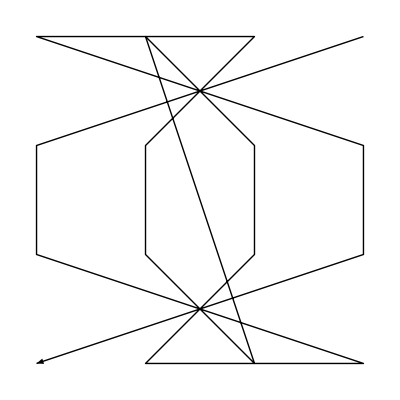

{{-3,-1},{0,-1},{3,-1},{-2,0},{1,1},{0,1},{-1,1},{1,-3},{-1,1},{0,1},{1,1},{-2,0},{3,-1},{0,-1},{-3,-1}}

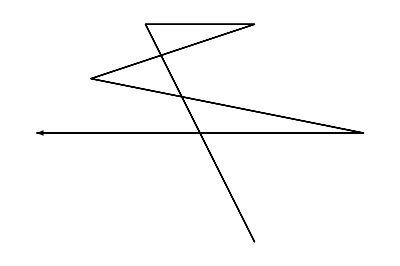

```mathematica
sq=({{16, 3, 2, 13}, {5, 10, 11, 8}, {9, 6, 7, 12}, {4, 15, 14, 1}})
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
{{1 ,14 ,14, 4},
{11, 7 ,6 ,9},
{8 ,10 ,10, 5},
{13, 2, 3 ,15}}//MatrixForm
```

(1 | 14 | 14 | 4
11 | 7 | 6 | 9
8 | 10 | 10 | 5
13 | 2 | 3 | 15)

{{1,14,14,4},{11,7,6,9},{8,10,10,5},{13,2,3,15}}

{{1,1,1},{14,1,2},{14,1,3},{4,1,4},{11,2,1},{7,2,2},{6,2,3},{9,2,4},{8,3,1},{10,3,2},{10,3,3},{5,3,4},{13,4,1},{2,4,2},{3,4,3},{15,4,4}}

{{1,1,1},{2,4,2},{3,4,3},{4,1,4},{5,3,4},{6,2,3},{7,2,2},{8,3,1},{9,2,4},{10,3,3},{10,3,2},{11,2,1},{13,4,1},{14,1,3},{14,1,2},{15,4,4}}

{{1,1},{4,2},{4,3},{1,4},{3,4},{2,3},{2,2},{3,1},{2,4},{3,3},{3,2},{2,1},{4,1},{1,3},{1,2},{4,4}}

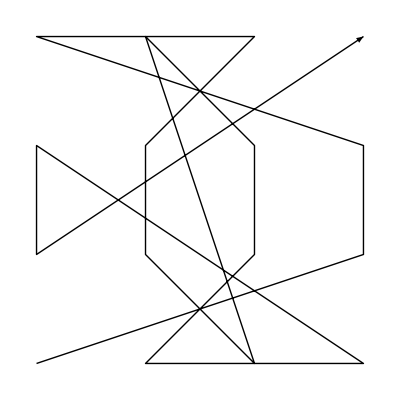

{{3,1},{0,1},{-3,1},{2,0},{-1,-1},{0,-1},{1,-1},{-1,3},{1,-1},{0,-1},{-1,-1},{2,0},{-3,2},{0,-1},{3,2}}

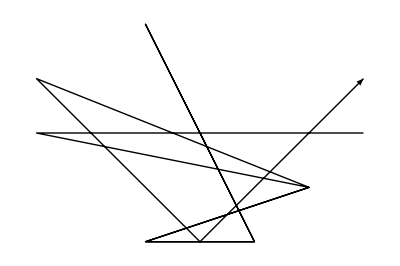

```mathematica
sq=({{1, 14, 14, 4}, {11, 7, 6, 9}, {8, 10, 10, 5}, {13, 2, 3, 15}})
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
{{1 ,6 ,12 ,15},
{11, 16, 2, 5},
{8 ,3 ,13 ,10},
{14, 9, 7 ,4}}//MatrixForm
```

{{1,6,12,15},{11,16,2,5},{8,3,13,10},{14,9,7,4}}

{{1,1,1},{6,1,2},{12,1,3},{15,1,4},{11,2,1},{16,2,2},{2,2,3},{5,2,4},{8,3,1},{3,3,2},{13,3,3},{10,3,4},{14,4,1},{9,4,2},{7,4,3},{4,4,4}}

{{1,1,1},{2,2,3},{3,3,2},{4,4,4},{5,2,4},{6,1,2},{7,4,3},{8,3,1},{9,4,2},{10,3,4},{11,2,1},{12,1,3},{13,3,3},{14,4,1},{15,1,4},{16,2,2}}

{{1,1},{2,3},{3,2},{4,4},{2,4},{1,2},{4,3},{3,1},{4,2},{3,4},{2,1},{1,3},{3,3},{4,1},{1,4},{2,2}}

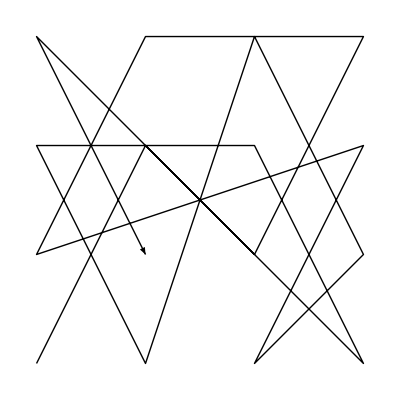

{{1,2},{1,-1},{1,2},{-2,0},{-1,-2},{3,1},{-1,-2},{1,1},{-1,2},{-1,-3},{-1,2},{2,0},{1,-2},{-3,3},{1,-2}}

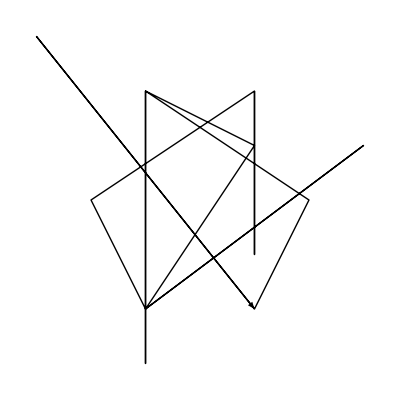

```mathematica
sq=({{1, 6, 12, 15}, {11, 16, 2, 5}, {8, 3, 13, 10}, {14, 9, 7, 4}})
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
StringReplace["3323 3406 3489 3572 3655 3738 3821 3904 3987 4070 4153 4236 4319 4402 4485 4568 4651 4734 4817 4900 4983 5066 5149 5232 5315 5398 5481 5564 5647 5730 5813 5896 5979 6062 6145 6228 6311 6394 6477 6560 1 84 167 250 333 416 499 582 665 748 831 914 997 1080 1163 1246 1329 1412 1495 1578 1661 1744 1827 1910 1993 2076 2159 2242 2325 2408 2491 2574 2657 2740 2823 2906 2989 3072 3155 3238 3321
3405 3488 3571 3654 3737 3820 3903 3986 4069 4152 4235 4318 4401 4484 4567 4650 4733 4816 4899 4982 5065 5148 5231 5314 5397 5480 5563 5646 5729 5812 5895 5978 6061 6144 6227 6310 6393 6476 6559 81 83 166 249 332 415 498 581 664 747 830 913 996 1079 1162 1245 1328 1411 1494 1577 1660 1743 1826 1909 1992 2075 2158 2241 2324 2407 2490 2573 2656 2739 2822 2905 2988 3071 3154 3237 3320 3322
3487 3570 3653 3736 3819 3902 3985 4068 4151 4234 4317 4400 4483 4566 4649 4732 4815 4898 4981 5064 5147 5230 5313 5396 5479 5562 5645 5728 5811 5894 5977 6060 6143 6226 6309 6392 6475 6558 80 82 165 248 331 414 497 580 663 746 829 912 995 1078 1161 1244 1327 1410 1493 1576 1659 1742 1825 1908 1991 2074 2157 2240 2323 2406 2489 2572 2655 2738 2821 2904 2987 3070 3153 3236 3319 3402 3404
3569 3652 3735 3818 3901 3984 4067 4150 4233 4316 4399 4482 4565 4648 4731 4814 4897 4980 5063 5146 5229 5312 5395 5478 5561 5644 5727 5810 5893 5976 6059 6142 6225 6308 6391 6474 6557 79 162 164 247 330 413 496 579 662 745 828 911 994 1077 1160 1243 1326 1409 1492 1575 1658 1741 1824 1907 1990 2073 2156 2239 2322 2405 2488 2571 2654 2737 2820 2903 2986 3069 3152 3235 3318 3401 3403 3486
3651 3734 3817 3900 3983 4066 4149 4232 4315 4398 4481 4564 4647 4730 4813 4896 4979 5062 5145 5228 5311 5394 5477 5560 5643 5726 5809 5892 5975 6058 6141 6224 6307 6390 6473 6556 78 161 163 246 329 412 495 578 661 744 827 910 993 1076 1159 1242 1325 1408 1491 1574 1657 1740 1823 1906 1989 2072 2155 2238 2321 2404 2487 2570 2653 2736 2819 2902 2985 3068 3151 3234 3317 3400 3483 3485 3568
3733 3816 3899 3982 4065 4148 4231 4314 4397 4480 4563 4646 4729 4812 4895 4978 5061 5144 5227 5310 5393 5476 5559 5642 5725 5808 5891 5974 6057 6140 6223 6306 6389 6472 6555 77 160 243 245 328 411 494 577 660 743 826 909 992 1075 1158 1241 1324 1407 1490 1573 1656 1739 1822 1905 1988 2071 2154 2237 2320 2403 2486 2569 2652 2735 2818 2901 2984 3067 3150 3233 3316 3399 3482 3484 3567 3650
3815 3898 3981 4064 4147 4230 4313 4396 4479 4562 4645 4728 4811 4894 4977 5060 5143 5226 5309 5392 5475 5558 5641 5724 5807 5890 5973 6056 6139 6222 6305 6388 6471 6554 76 159 242 244 327 410 493 576 659 742 825 908 991 1074 1157 1240 1323 1406 1489 1572 1655 1738 1821 1904 1987 2070 2153 2236 2319 2402 2485 2568 2651 2734 2817 2900 2983 3066 3149 3232 3315 3398 3481 3564 3566 3649 3732
3897 3980 4063 4146 4229 4312 4395 4478 4561 4644 4727 4810 4893 4976 5059 5142 5225 5308 5391 5474 5557 5640 5723 5806 5889 5972 6055 6138 6221 6304 6387 6470 6553 75 158 241 324 326 409 492 575 658 741 824 907 990 1073 1156 1239 1322 1405 1488 1571 1654 1737 1820 1903 1986 2069 2152 2235 2318 2401 2484 2567 2650 2733 2816 2899 2982 3065 3148 3231 3314 3397 3480 3563 3565 3648 3731 3814
3979 4062 4145 4228 4311 4394 4477 4560 4643 4726 4809 4892 4975 5058 5141 5224 5307 5390 5473 5556 5639 5722 5805 5888 5971 6054 6137 6220 6303 6386 6469 6552 74 157 240 323 325 408 491 574 657 740 823 906 989 1072 1155 1238 1321 1404 1487 1570 1653 1736 1819 1902 1985 2068 2151 2234 2317 2400 2483 2566 2649 2732 2815 2898 2981 3064 3147 3230 3313 3396 3479 3562 3645 3647 3730 3813 3896
4061 4144 4227 4310 4393 4476 4559 4642 4725 4808 4891 4974 5057 5140 5223 5306 5389 5472 5555 5638 5721 5804 5887 5970 6053 6136 6219 6302 6385 6468 6551 73 156 239 322 405 407 490 573 656 739 822 905 988 1071 1154 1237 1320 1403 1486 1569 1652 1735 1818 1901 1984 2067 2150 2233 2316 2399 2482 2565 2648 2731 2814 2897 2980 3063 3146 3229 3312 3395 3478 3561 3644 3646 3729 3812 3895 3978
4143 4226 4309 4392 4475 4558 4641 4724 4807 4890 4973 5056 5139 5222 5305 5388 5471 5554 5637 5720 5803 5886 5969 6052 6135 6218 6301 6384 6467 6550 72 155 238 321 404 406 489 572 655 738 821 904 987 1070 1153 1236 1319 1402 1485 1568 1651 1734 1817 1900 1983 2066 2149 2232 2315 2398 2481 2564 2647 2730 2813 2896 2979 3062 3145 3228 3311 3394 3477 3560 3643 3726 3728 3811 3894 3977 4060
4225 4308 4391 4474 4557 4640 4723 4806 4889 4972 5055 5138 5221 5304 5387 5470 5553 5636 5719 5802 5885 5968 6051 6134 6217 6300 6383 6466 6549 71 154 237 320 403 486 488 571 654 737 820 903 986 1069 1152 1235 1318 1401 1484 1567 1650 1733 1816 1899 1982 2065 2148 2231 2314 2397 2480 2563 2646 2729 2812 2895 2978 3061 3144 3227 3310 3393 3476 3559 3642 3725 3727 3810 3893 3976 4059 4142
4307 4390 4473 4556 4639 4722 4805 4888 4971 5054 5137 5220 5303 5386 5469 5552 5635 5718 5801 5884 5967 6050 6133 6216 6299 6382 6465 6548 70 153 236 319 402 485 487 570 653 736 819 902 985 1068 1151 1234 1317 1400 1483 1566 1649 1732 1815 1898 1981 2064 2147 2230 2313 2396 2479 2562 2645 2728 2811 2894 2977 3060 3143 3226 3309 3392 3475 3558 3641 3724 3807 3809 3892 3975 4058 4141 4224
4389 4472 4555 4638 4721 4804 4887 4970 5053 5136 5219 5302 5385 5468 5551 5634 5717 5800 5883 5966 6049 6132 6215 6298 6381 6464 6547 69 152 235 318 401 484 567 569 652 735 818 901 984 1067 1150 1233 1316 1399 1482 1565 1648 1731 1814 1897 1980 2063 2146 2229 2312 2395 2478 2561 2644 2727 2810 2893 2976 3059 3142 3225 3308 3391 3474 3557 3640 3723 3806 3808 3891 3974 4057 4140 4223 4306
4471 4554 4637 4720 4803 4886 4969 5052 5135 5218 5301 5384 5467 5550 5633 5716 5799 5882 5965 6048 6131 6214 6297 6380 6463 6546 68 151 234 317 400 483 566 568 651 734 817 900 983 1066 1149 1232 1315 1398 1481 1564 1647 1730 1813 1896 1979 2062 2145 2228 2311 2394 2477 2560 2643 2726 2809 2892 2975 3058 3141 3224 3307 3390 3473 3556 3639 3722 3805 3888 3890 3973 4056 4139 4222 4305 4388
4553 4636 4719 4802 4885 4968 5051 5134 5217 5300 5383 5466 5549 5632 5715 5798 5881 5964 6047 6130 6213 6296 6379 6462 6545 67 150 233 316 399 482 565 648 650 733 816 899 982 1065 1148 1231 1314 1397 1480 1563 1646 1729 1812 1895 1978 2061 2144 2227 2310 2393 2476 2559 2642 2725 2808 2891 2974 3057 3140 3223 3306 3389 3472 3555 3638 3721 3804 3887 3889 3972 4055 4138 4221 4304 4387 4470
4635 4718 4801 4884 4967 5050 5133 5216 5299 5382 5465 5548 5631 5714 5797 5880 5963 6046 6129 6212 6295 6378 6461 6544 66 149 232 315 398 481 564 647 649 732 815 898 981 1064 1147 1230 1313 1396 1479 1562 1645 1728 1811 1894 1977 2060 2143 2226 2309 2392 2475 2558 2641 2724 2807 2890 2973 3056 3139 3222 3305 3388 3471 3554 3637 3720 3803 3886 3969 3971 4054 4137 4220 4303 4386 4469 4552
4717 4800 4883 4966 5049 5132 5215 5298 5381 5464 5547 5630 5713 5796 5879 5962 6045 6128 6211 6294 6377 6460 6543 65 148 231 314 397 480 563 646 729 731 814 897 980 1063 1146 1229 1312 1395 1478 1561 1644 1727 1810 1893 1976 2059 2142 2225 2308 2391 2474 2557 2640 2723 2806 2889 2972 3055 3138 3221 3304 3387 3470 3553 3636 3719 3802 3885 3968 3970 4053 4136 4219 4302 4385 4468 4551 4634
4799 4882 4965 5048 5131 5214 5297 5380 5463 5546 5629 5712 5795 5878 5961 6044 6127 6210 6293 6376 6459 6542 64 147 230 313 396 479 562 645 728 730 813 896 979 1062 1145 1228 1311 1394 1477 1560 1643 1726 1809 1892 1975 2058 2141 2224 2307 2390 2473 2556 2639 2722 2805 2888 2971 3054 3137 3220 3303 3386 3469 3552 3635 3718 3801 3884 3967 4050 4052 4135 4218 4301 4384 4467 4550 4633 4716
4881 4964 5047 5130 5213 5296 5379 5462 5545 5628 5711 5794 5877 5960 6043 6126 6209 6292 6375 6458 6541 63 146 229 312 395 478 561 644 727 810 812 895 978 1061 1144 1227 1310 1393 1476 1559 1642 1725 1808 1891 1974 2057 2140 2223 2306 2389 2472 2555 2638 2721 2804 2887 2970 3053 3136 3219 3302 3385 3468 3551 3634 3717 3800 3883 3966 4049 4051 4134 4217 4300 4383 4466 4549 4632 4715 4798
4963 5046 5129 5212 5295 5378 5461 5544 5627 5710 5793 5876 5959 6042 6125 6208 6291 6374 6457 6540 62 145 228 311 394 477 560 643 726 809 811 894 977 1060 1143 1226 1309 1392 1475 1558 1641 1724 1807 1890 1973 2056 2139 2222 2305 2388 2471 2554 2637 2720 2803 2886 2969 3052 3135 3218 3301 3384 3467 3550 3633 3716 3799 3882 3965 4048 4131 4133 4216 4299 4382 4465 4548 4631 4714 4797 4880
5045 5128 5211 5294 5377 5460 5543 5626 5709 5792 5875 5958 6041 6124 6207 6290 6373 6456 6539 61 144 227 310 393 476 559 642 725 808 891 893 976 1059 1142 1225 1308 1391 1474 1557 1640 1723 1806 1889 1972 2055 2138 2221 2304 2387 2470 2553 2636 2719 2802 2885 2968 3051 3134 3217 3300 3383 3466 3549 3632 3715 3798 3881 3964 4047 4130 4132 4215 4298 4381 4464 4547 4630 4713 4796 4879 4962
5127 5210 5293 5376 5459 5542 5625 5708 5791 5874 5957 6040 6123 6206 6289 6372 6455 6538 60 143 226 309 392 475 558 641 724 807 890 892 975 1058 1141 1224 1307 1390 1473 1556 1639 1722 1805 1888 1971 2054 2137 2220 2303 2386 2469 2552 2635 2718 2801 2884 2967 3050 3133 3216 3299 3382 3465 3548 3631 3714 3797 3880 3963 4046 4129 4212 4214 4297 4380 4463 4546 4629 4712 4795 4878 4961 5044
5209 5292 5375 5458 5541 5624 5707 5790 5873 5956 6039 6122 6205 6288 6371 6454 6537 59 142 225 308 391 474 557 640 723 806 889 972 974 1057 1140 1223 1306 1389 1472 1555 1638 1721 1804 1887 1970 2053 2136 2219 2302 2385 2468 2551 2634 2717 2800 2883 2966 3049 3132 3215 3298 3381 3464 3547 3630 3713 3796 3879 3962 4045 4128 4211 4213 4296 4379 4462 4545 4628 4711 4794 4877 4960 5043 5126
5291 5374 5457 5540 5623 5706 5789 5872 5955 6038 6121 6204 6287 6370 6453 6536 58 141 224 307 390 473 556 639 722 805 888 971 973 1056 1139 1222 1305 1388 1471 1554 1637 1720 1803 1886 1969 2052 2135 2218 2301 2384 2467 2550 2633 2716 2799 2882 2965 3048 3131 3214 3297 3380 3463 3546 3629 3712 3795 3878 3961 4044 4127 4210 4293 4295 4378 4461 4544 4627 4710 4793 4876 4959 5042 5125 5208
5373 5456 5539 5622 5705 5788 5871 5954 6037 6120 6203 6286 6369 6452 6535 57 140 223 306 389 472 555 638 721 804 887 970 1053 1055 1138 1221 1304 1387 1470 1553 1636 1719 1802 1885 1968 2051 2134 2217 2300 2383 2466 2549 2632 2715 2798 2881 2964 3047 3130 3213 3296 3379 3462 3545 3628 3711 3794 3877 3960 4043 4126 4209 4292 4294 4377 4460 4543 4626 4709 4792 4875 4958 5041 5124 5207 5290
5455 5538 5621 5704 5787 5870 5953 6036 6119 6202 6285 6368 6451 6534 56 139 222 305 388 471 554 637 720 803 886 969 1052 1054 1137 1220 1303 1386 1469 1552 1635 1718 1801 1884 1967 2050 2133 2216 2299 2382 2465 2548 2631 2714 2797 2880 2963 3046 3129 3212 3295 3378 3461 3544 3627 3710 3793 3876 3959 4042 4125 4208 4291 4374 4376 4459 4542 4625 4708 4791 4874 4957 5040 5123 5206 5289 5372
5537 5620 5703 5786 5869 5952 6035 6118 6201 6284 6367 6450 6533 55 138 221 304 387 470 553 636 719 802 885 968 1051 1134 1136 1219 1302 1385 1468 1551 1634 1717 1800 1883 1966 2049 2132 2215 2298 2381 2464 2547 2630 2713 2796 2879 2962 3045 3128 3211 3294 3377 3460 3543 3626 3709 3792 3875 3958 4041 4124 4207 4290 4373 4375 4458 4541 4624 4707 4790 4873 4956 5039 5122 5205 5288 5371 5454
5619 5702 5785 5868 5951 6034 6117 6200 6283 6366 6449 6532 54 137 220 303 386 469 552 635 718 801 884 967 1050 1133 1135 1218 1301 1384 1467 1550 1633 1716 1799 1882 1965 2048 2131 2214 2297 2380 2463 2546 2629 2712 2795 2878 2961 3044 3127 3210 3293 3376 3459 3542 3625 3708 3791 3874 3957 4040 4123 4206 4289 4372 4455 4457 4540 4623 4706 4789 4872 4955 5038 5121 5204 5287 5370 5453 5536
5701 5784 5867 5950 6033 6116 6199 6282 6365 6448 6531 53 136 219 302 385 468 551 634 717 800 883 966 1049 1132 1215 1217 1300 1383 1466 1549 1632 1715 1798 1881 1964 2047 2130 2213 2296 2379 2462 2545 2628 2711 2794 2877 2960 3043 3126 3209 3292 3375 3458 3541 3624 3707 3790 3873 3956 4039 4122 4205 4288 4371 4454 4456 4539 4622 4705 4788 4871 4954 5037 5120 5203 5286 5369 5452 5535 5618
5783 5866 5949 6032 6115 6198 6281 6364 6447 6530 52 135 218 301 384 467 550 633 716 799 882 965 1048 1131 1214 1216 1299 1382 1465 1548 1631 1714 1797 1880 1963 2046 2129 2212 2295 2378 2461 2544 2627 2710 2793 2876 2959 3042 3125 3208 3291 3374 3457 3540 3623 3706 3789 3872 3955 4038 4121 4204 4287 4370 4453 4536 4538 4621 4704 4787 4870 4953 5036 5119 5202 5285 5368 5451 5534 5617 5700
5865 5948 6031 6114 6197 6280 6363 6446 6529 51 134 217 300 383 466 549 632 715 798 881 964 1047 1130 1213 1296 1298 1381 1464 1547 1630 1713 1796 1879 1962 2045 2128 2211 2294 2377 2460 2543 2626 2709 2792 2875 2958 3041 3124 3207 3290 3373 3456 3539 3622 3705 3788 3871 3954 4037 4120 4203 4286 4369 4452 4535 4537 4620 4703 4786 4869 4952 5035 5118 5201 5284 5367 5450 5533 5616 5699 5782
5947 6030 6113 6196 6279 6362 6445 6528 50 133 216 299 382 465 548 631 714 797 880 963 1046 1129 1212 1295 1297 1380 1463 1546 1629 1712 1795 1878 1961 2044 2127 2210 2293 2376 2459 2542 2625 2708 2791 2874 2957 3040 3123 3206 3289 3372 3455 3538 3621 3704 3787 3870 3953 4036 4119 4202 4285 4368 4451 4534 4617 4619 4702 4785 4868 4951 5034 5117 5200 5283 5366 5449 5532 5615 5698 5781 5864
6029 6112 6195 6278 6361 6444 6527 49 132 215 298 381 464 547 630 713 796 879 962 1045 1128 1211 1294 1377 1379 1462 1545 1628 1711 1794 1877 1960 2043 2126 2209 2292 2375 2458 2541 2624 2707 2790 2873 2956 3039 3122 3205 3288 3371 3454 3537 3620 3703 3786 3869 3952 4035 4118 4201 4284 4367 4450 4533 4616 4618 4701 4784 4867 4950 5033 5116 5199 5282 5365 5448 5531 5614 5697 5780 5863 5946
6111 6194 6277 6360 6443 6526 48 131 214 297 380 463 546 629 712 795 878 961 1044 1127 1210 1293 1376 1378 1461 1544 1627 1710 1793 1876 1959 2042 2125 2208 2291 2374 2457 2540 2623 2706 2789 2872 2955 3038 3121 3204 3287 3370 3453 3536 3619 3702 3785 3868 3951 4034 4117 4200 4283 4366 4449 4532 4615 4698 4700 4783 4866 4949 5032 5115 5198 5281 5364 5447 5530 5613 5696 5779 5862 5945 6028
6193 6276 6359 6442 6525 47 130 213 296 379 462 545 628 711 794 877 960 1043 1126 1209 1292 1375 1458 1460 1543 1626 1709 1792 1875 1958 2041 2124 2207 2290 2373 2456 2539 2622 2705 2788 2871 2954 3037 3120 3203 3286 3369 3452 3535 3618 3701 3784 3867 3950 4033 4116 4199 4282 4365 4448 4531 4614 4697 4699 4782 4865 4948 5031 5114 5197 5280 5363 5446 5529 5612 5695 5778 5861 5944 6027 6110
6275 6358 6441 6524 46 129 212 295 378 461 544 627 710 793 876 959 1042 1125 1208 1291 1374 1457 1459 1542 1625 1708 1791 1874 1957 2040 2123 2206 2289 2372 2455 2538 2621 2704 2787 2870 2953 3036 3119 3202 3285 3368 3451 3534 3617 3700 3783 3866 3949 4032 4115 4198 4281 4364 4447 4530 4613 4696 4779 4781 4864 4947 5030 5113 5196 5279 5362 5445 5528 5611 5694 5777 5860 5943 6026 6109 6192
6357 6440 6523 45 128 211 294 377 460 543 626 709 792 875 958 1041 1124 1207 1290 1373 1456 1539 1541 1624 1707 1790 1873 1956 2039 2122 2205 2288 2371 2454 2537 2620 2703 2786 2869 2952 3035 3118 3201 3284 3367 3450 3533 3616 3699 3782 3865 3948 4031 4114 4197 4280 4363 4446 4529 4612 4695 4778 4780 4863 4946 5029 5112 5195 5278 5361 5444 5527 5610 5693 5776 5859 5942 6025 6108 6191 6274
6439 6522 44 127 210 293 376 459 542 625 708 791 874 957 1040 1123 1206 1289 1372 1455 1538 1540 1623 1706 1789 1872 1955 2038 2121 2204 2287 2370 2453 2536 2619 2702 2785 2868 2951 3034 3117 3200 3283 3366 3449 3532 3615 3698 3781 3864 3947 4030 4113 4196 4279 4362 4445 4528 4611 4694 4777 4860 4862 4945 5028 5111 5194 5277 5360 5443 5526 5609 5692 5775 5858 5941 6024 6107 6190 6273 6356
6521 43 126 209 292 375 458 541 624 707 790 873 956 1039 1122 1205 1288 1371 1454 1537 1620 1622 1705 1788 1871 1954 2037 2120 2203 2286 2369 2452 2535 2618 2701 2784 2867 2950 3033 3116 3199 3282 3365 3448 3531 3614 3697 3780 3863 3946 4029 4112 4195 4278 4361 4444 4527 4610 4693 4776 4859 4861 4944 5027 5110 5193 5276 5359 5442 5525 5608 5691 5774 5857 5940 6023 6106 6189 6272 6355 6438
42 125 208 291 374 457 540 623 706 789 872 955 1038 1121 1204 1287 1370 1453 1536 1619 1621 1704 1787 1870 1953 2036 2119 2202 2285 2368 2451 2534 2617 2700 2783 2866 2949 3032 3115 3198 3281 3364 3447 3530 3613 3696 3779 3862 3945 4028 4111 4194 4277 4360 4443 4526 4609 4692 4775 4858 4941 4943 5026 5109 5192 5275 5358 5441 5524 5607 5690 5773 5856 5939 6022 6105 6188 6271 6354 6437 6520
124 207 290 373 456 539 622 705 788 871 954 1037 1120 1203 1286 1369 1452 1535 1618 1701 1703 1786 1869 1952 2035 2118 2201 2284 2367 2450 2533 2616 2699 2782 2865 2948 3031 3114 3197 3280 3363 3446 3529 3612 3695 3778 3861 3944 4027 4110 4193 4276 4359 4442 4525 4608 4691 4774 4857 4940 4942 5025 5108 5191 5274 5357 5440 5523 5606 5689 5772 5855 5938 6021 6104 6187 6270 6353 6436 6519 41
206 289 372 455 538 621 704 787 870 953 1036 1119 1202 1285 1368 1451 1534 1617 1700 1702 1785 1868 1951 2034 2117 2200 2283 2366 2449 2532 2615 2698 2781 2864 2947 3030 3113 3196 3279 3362 3445 3528 3611 3694 3777 3860 3943 4026 4109 4192 4275 4358 4441 4524 4607 4690 4773 4856 4939 5022 5024 5107 5190 5273 5356 5439 5522 5605 5688 5771 5854 5937 6020 6103 6186 6269 6352 6435 6518 40 123
288 371 454 537 620 703 786 869 952 1035 1118 1201 1284 1367 1450 1533 1616 1699 1782 1784 1867 1950 2033 2116 2199 2282 2365 2448 2531 2614 2697 2780 2863 2946 3029 3112 3195 3278 3361 3444 3527 3610 3693 3776 3859 3942 4025 4108 4191 4274 4357 4440 4523 4606 4689 4772 4855 4938 5021 5023 5106 5189 5272 5355 5438 5521 5604 5687 5770 5853 5936 6019 6102 6185 6268 6351 6434 6517 39 122 205
370 453 536 619 702 785 868 951 1034 1117 1200 1283 1366 1449 1532 1615 1698 1781 1783 1866 1949 2032 2115 2198 2281 2364 2447 2530 2613 2696 2779 2862 2945 3028 3111 3194 3277 3360 3443 3526 3609 3692 3775 3858 3941 4024 4107 4190 4273 4356 4439 4522 4605 4688 4771 4854 4937 5020 5103 5105 5188 5271 5354 5437 5520 5603 5686 5769 5852 5935 6018 6101 6184 6267 6350 6433 6516 38 121 204 287
452 535 618 701 784 867 950 1033 1116 1199 1282 1365 1448 1531 1614 1697 1780 1863 1865 1948 2031 2114 2197 2280 2363 2446 2529 2612 2695 2778 2861 2944 3027 3110 3193 3276 3359 3442 3525 3608 3691 3774 3857 3940 4023 4106 4189 4272 4355 4438 4521 4604 4687 4770 4853 4936 5019 5102 5104 5187 5270 5353 5436 5519 5602 5685 5768 5851 5934 6017 6100 6183 6266 6349 6432 6515 37 120 203 286 369
534 617 700 783 866 949 1032 1115 1198 1281 1364 1447 1530 1613 1696 1779 1862 1864 1947 2030 2113 2196 2279 2362 2445 2528 2611 2694 2777 2860 2943 3026 3109 3192 3275 3358 3441 3524 3607 3690 3773 3856 3939 4022 4105 4188 4271 4354 4437 4520 4603 4686 4769 4852 4935 5018 5101 5184 5186 5269 5352 5435 5518 5601 5684 5767 5850 5933 6016 6099 6182 6265 6348 6431 6514 36 119 202 285 368 451
616 699 782 865 948 1031 1114 1197 1280 1363 1446 1529 1612 1695 1778 1861 1944 1946 2029 2112 2195 2278 2361 2444 2527 2610 2693 2776 2859 2942 3025 3108 3191 3274 3357 3440 3523 3606 3689 3772 3855 3938 4021 4104 4187 4270 4353 4436 4519 4602 4685 4768 4851 4934 5017 5100 5183 5185 5268 5351 5434 5517 5600 5683 5766 5849 5932 6015 6098 6181 6264 6347 6430 6513 35 118 201 284 367 450 533
698 781 864 947 1030 1113 1196 1279 1362 1445 1528 1611 1694 1777 1860 1943 1945 2028 2111 2194 2277 2360 2443 2526 2609 2692 2775 2858 2941 3024 3107 3190 3273 3356 3439 3522 3605 3688 3771 3854 3937 4020 4103 4186 4269 4352 4435 4518 4601 4684 4767 4850 4933 5016 5099 5182 5265 5267 5350 5433 5516 5599 5682 5765 5848 5931 6014 6097 6180 6263 6346 6429 6512 34 117 200 283 366 449 532 615
780 863 946 1029 1112 1195 1278 1361 1444 1527 1610 1693 1776 1859 1942 2025 2027 2110 2193 2276 2359 2442 2525 2608 2691 2774 2857 2940 3023 3106 3189 3272 3355 3438 3521 3604 3687 3770 3853 3936 4019 4102 4185 4268 4351 4434 4517 4600 4683 4766 4849 4932 5015 5098 5181 5264 5266 5349 5432 5515 5598 5681 5764 5847 5930 6013 6096 6179 6262 6345 6428 6511 33 116 199 282 365 448 531 614 697
862 945 1028 1111 1194 1277 1360 1443 1526 1609 1692 1775 1858 1941 2024 2026 2109 2192 2275 2358 2441 2524 2607 2690 2773 2856 2939 3022 3105 3188 3271 3354 3437 3520 3603 3686 3769 3852 3935 4018 4101 4184 4267 4350 4433 4516 4599 4682 4765 4848 4931 5014 5097 5180 5263 5346 5348 5431 5514 5597 5680 5763 5846 5929 6012 6095 6178 6261 6344 6427 6510 32 115 198 281 364 447 530 613 696 779
944 1027 1110 1193 1276 1359 1442 1525 1608 1691 1774 1857 1940 2023 2106 2108 2191 2274 2357 2440 2523 2606 2689 2772 2855 2938 3021 3104 3187 3270 3353 3436 3519 3602 3685 3768 3851 3934 4017 4100 4183 4266 4349 4432 4515 4598 4681 4764 4847 4930 5013 5096 5179 5262 5345 5347 5430 5513 5596 5679 5762 5845 5928 6011 6094 6177 6260 6343 6426 6509 31 114 197 280 363 446 529 612 695 778 861
1026 1109 1192 1275 1358 1441 1524 1607 1690 1773 1856 1939 2022 2105 2107 2190 2273 2356 2439 2522 2605 2688 2771 2854 2937 3020 3103 3186 3269 3352 3435 3518 3601 3684 3767 3850 3933 4016 4099 4182 4265 4348 4431 4514 4597 4680 4763 4846 4929 5012 5095 5178 5261 5344 5427 5429 5512 5595 5678 5761 5844 5927 6010 6093 6176 6259 6342 6425 6508 30 113 196 279 362 445 528 611 694 777 860 943
1108 1191 1274 1357 1440 1523 1606 1689 1772 1855 1938 2021 2104 2187 2189 2272 2355 2438 2521 2604 2687 2770 2853 2936 3019 3102 3185 3268 3351 3434 3517 3600 3683 3766 3849 3932 4015 4098 4181 4264 4347 4430 4513 4596 4679 4762 4845 4928 5011 5094 5177 5260 5343 5426 5428 5511 5594 5677 5760 5843 5926 6009 6092 6175 6258 6341 6424 6507 29 112 195 278 361 444 527 610 693 776 859 942 1025
1190 1273 1356 1439 1522 1605 1688 1771 1854 1937 2020 2103 2186 2188 2271 2354 2437 2520 2603 2686 2769 2852 2935 3018 3101 3184 3267 3350 3433 3516 3599 3682 3765 3848 3931 4014 4097 4180 4263 4346 4429 4512 4595 4678 4761 4844 4927 5010 5093 5176 5259 5342 5425 5508 5510 5593 5676 5759 5842 5925 6008 6091 6174 6257 6340 6423 6506 28 111 194 277 360 443 526 609 692 775 858 941 1024 1107
1272 1355 1438 1521 1604 1687 1770 1853 1936 2019 2102 2185 2268 2270 2353 2436 2519 2602 2685 2768 2851 2934 3017 3100 3183 3266 3349 3432 3515 3598 3681 3764 3847 3930 4013 4096 4179 4262 4345 4428 4511 4594 4677 4760 4843 4926 5009 5092 5175 5258 5341 5424 5507 5509 5592 5675 5758 5841 5924 6007 6090 6173 6256 6339 6422 6505 27 110 193 276 359 442 525 608 691 774 857 940 1023 1106 1189
1354 1437 1520 1603 1686 1769 1852 1935 2018 2101 2184 2267 2269 2352 2435 2518 2601 2684 2767 2850 2933 3016 3099 3182 3265 3348 3431 3514 3597 3680 3763 3846 3929 4012 4095 4178 4261 4344 4427 4510 4593 4676 4759 4842 4925 5008 5091 5174 5257 5340 5423 5506 5589 5591 5674 5757 5840 5923 6006 6089 6172 6255 6338 6421 6504 26 109 192 275 358 441 524 607 690 773 856 939 1022 1105 1188 1271
1436 1519 1602 1685 1768 1851 1934 2017 2100 2183 2266 2349 2351 2434 2517 2600 2683 2766 2849 2932 3015 3098 3181 3264 3347 3430 3513 3596 3679 3762 3845 3928 4011 4094 4177 4260 4343 4426 4509 4592 4675 4758 4841 4924 5007 5090 5173 5256 5339 5422 5505 5588 5590 5673 5756 5839 5922 6005 6088 6171 6254 6337 6420 6503 25 108 191 274 357 440 523 606 689 772 855 938 1021 1104 1187 1270 1353
1518 1601 1684 1767 1850 1933 2016 2099 2182 2265 2348 2350 2433 2516 2599 2682 2765 2848 2931 3014 3097 3180 3263 3346 3429 3512 3595 3678 3761 3844 3927 4010 4093 4176 4259 4342 4425 4508 4591 4674 4757 4840 4923 5006 5089 5172 5255 5338 5421 5504 5587 5670 5672 5755 5838 5921 6004 6087 6170 6253 6336 6419 6502 24 107 190 273 356 439 522 605 688 771 854 937 1020 1103 1186 1269 1352 1435
1600 1683 1766 1849 1932 2015 2098 2181 2264 2347 2430 2432 2515 2598 2681 2764 2847 2930 3013 3096 3179 3262 3345 3428 3511 3594 3677 3760 3843 3926 4009 4092 4175 4258 4341 4424 4507 4590 4673 4756 4839 4922 5005 5088 5171 5254 5337 5420 5503 5586 5669 5671 5754 5837 5920 6003 6086 6169 6252 6335 6418 6501 23 106 189 272 355 438 521 604 687 770 853 936 1019 1102 1185 1268 1351 1434 1517
1682 1765 1848 1931 2014 2097 2180 2263 2346 2429 2431 2514 2597 2680 2763 2846 2929 3012 3095 3178 3261 3344 3427 3510 3593 3676 3759 3842 3925 4008 4091 4174 4257 4340 4423 4506 4589 4672 4755 4838 4921 5004 5087 5170 5253 5336 5419 5502 5585 5668 5751 5753 5836 5919 6002 6085 6168 6251 6334 6417 6500 22 105 188 271 354 437 520 603 686 769 852 935 1018 1101 1184 1267 1350 1433 1516 1599
1764 1847 1930 2013 2096 2179 2262 2345 2428 2511 2513 2596 2679 2762 2845 2928 3011 3094 3177 3260 3343 3426 3509 3592 3675 3758 3841 3924 4007 4090 4173 4256 4339 4422 4505 4588 4671 4754 4837 4920 5003 5086 5169 5252 5335 5418 5501 5584 5667 5750 5752 5835 5918 6001 6084 6167 6250 6333 6416 6499 21 104 187 270 353 436 519 602 685 768 851 934 1017 1100 1183 1266 1349 1432 1515 1598 1681
1846 1929 2012 2095 2178 2261 2344 2427 2510 2512 2595 2678 2761 2844 2927 3010 3093 3176 3259 3342 3425 3508 3591 3674 3757 3840 3923 4006 4089 4172 4255 4338 4421 4504 4587 4670 4753 4836 4919 5002 5085 5168 5251 5334 5417 5500 5583 5666 5749 5832 5834 5917 6000 6083 6166 6249 6332 6415 6498 20 103 186 269 352 435 518 601 684 767 850 933 1016 1099 1182 1265 1348 1431 1514 1597 1680 1763
1928 2011 2094 2177 2260 2343 2426 2509 2592 2594 2677 2760 2843 2926 3009 3092 3175 3258 3341 3424 3507 3590 3673 3756 3839 3922 4005 4088 4171 4254 4337 4420 4503 4586 4669 4752 4835 4918 5001 5084 5167 5250 5333 5416 5499 5582 5665 5748 5831 5833 5916 5999 6082 6165 6248 6331 6414 6497 19 102 185 268 351 434 517 600 683 766 849 932 1015 1098 1181 1264 1347 1430 1513 1596 1679 1762 1845
2010 2093 2176 2259 2342 2425 2508 2591 2593 2676 2759 2842 2925 3008 3091 3174 3257 3340 3423 3506 3589 3672 3755 3838 3921 4004 4087 4170 4253 4336 4419 4502 4585 4668 4751 4834 4917 5000 5083 5166 5249 5332 5415 5498 5581 5664 5747 5830 5913 5915 5998 6081 6164 6247 6330 6413 6496 18 101 184 267 350 433 516 599 682 765 848 931 1014 1097 1180 1263 1346 1429 1512 1595 1678 1761 1844 1927
2092 2175 2258 2341 2424 2507 2590 2673 2675 2758 2841 2924 3007 3090 3173 3256 3339 3422 3505 3588 3671 3754 3837 3920 4003 4086 4169 4252 4335 4418 4501 4584 4667 4750 4833 4916 4999 5082 5165 5248 5331 5414 5497 5580 5663 5746 5829 5912 5914 5997 6080 6163 6246 6329 6412 6495 17 100 183 266 349 432 515 598 681 764 847 930 1013 1096 1179 1262 1345 1428 1511 1594 1677 1760 1843 1926 2009
2174 2257 2340 2423 2506 2589 2672 2674 2757 2840 2923 3006 3089 3172 3255 3338 3421 3504 3587 3670 3753 3836 3919 4002 4085 4168 4251 4334 4417 4500 4583 4666 4749 4832 4915 4998 5081 5164 5247 5330 5413 5496 5579 5662 5745 5828 5911 5994 5996 6079 6162 6245 6328 6411 6494 16 99 182 265 348 431 514 597 680 763 846 929 1012 1095 1178 1261 1344 1427 1510 1593 1676 1759 1842 1925 2008 2091
2256 2339 2422 2505 2588 2671 2754 2756 2839 2922 3005 3088 3171 3254 3337 3420 3503 3586 3669 3752 3835 3918 4001 4084 4167 4250 4333 4416 4499 4582 4665 4748 4831 4914 4997 5080 5163 5246 5329 5412 5495 5578 5661 5744 5827 5910 5993 5995 6078 6161 6244 6327 6410 6493 15 98 181 264 347 430 513 596 679 762 845 928 1011 1094 1177 1260 1343 1426 1509 1592 1675 1758 1841 1924 2007 2090 2173
2338 2421 2504 2587 2670 2753 2755 2838 2921 3004 3087 3170 3253 3336 3419 3502 3585 3668 3751 3834 3917 4000 4083 4166 4249 4332 4415 4498 4581 4664 4747 4830 4913 4996 5079 5162 5245 5328 5411 5494 5577 5660 5743 5826 5909 5992 6075 6077 6160 6243 6326 6409 6492 14 97 180 263 346 429 512 595 678 761 844 927 1010 1093 1176 1259 1342 1425 1508 1591 1674 1757 1840 1923 2006 2089 2172 2255
2420 2503 2586 2669 2752 2835 2837 2920 3003 3086 3169 3252 3335 3418 3501 3584 3667 3750 3833 3916 3999 4082 4165 4248 4331 4414 4497 4580 4663 4746 4829 4912 4995 5078 5161 5244 5327 5410 5493 5576 5659 5742 5825 5908 5991 6074 6076 6159 6242 6325 6408 6491 13 96 179 262 345 428 511 594 677 760 843 926 1009 1092 1175 1258 1341 1424 1507 1590 1673 1756 1839 1922 2005 2088 2171 2254 2337
2502 2585 2668 2751 2834 2836 2919 3002 3085 3168 3251 3334 3417 3500 3583 3666 3749 3832 3915 3998 4081 4164 4247 4330 4413 4496 4579 4662 4745 4828 4911 4994 5077 5160 5243 5326 5409 5492 5575 5658 5741 5824 5907 5990 6073 6156 6158 6241 6324 6407 6490 12 95 178 261 344 427 510 593 676 759 842 925 1008 1091 1174 1257 1340 1423 1506 1589 1672 1755 1838 1921 2004 2087 2170 2253 2336 2419
2584 2667 2750 2833 2916 2918 3001 3084 3167 3250 3333 3416 3499 3582 3665 3748 3831 3914 3997 4080 4163 4246 4329 4412 4495 4578 4661 4744 4827 4910 4993 5076 5159 5242 5325 5408 5491 5574 5657 5740 5823 5906 5989 6072 6155 6157 6240 6323 6406 6489 11 94 177 260 343 426 509 592 675 758 841 924 1007 1090 1173 1256 1339 1422 1505 1588 1671 1754 1837 1920 2003 2086 2169 2252 2335 2418 2501
2666 2749 2832 2915 2917 3000 3083 3166 3249 3332 3415 3498 3581 3664 3747 3830 3913 3996 4079 4162 4245 4328 4411 4494 4577 4660 4743 4826 4909 4992 5075 5158 5241 5324 5407 5490 5573 5656 5739 5822 5905 5988 6071 6154 6237 6239 6322 6405 6488 10 93 176 259 342 425 508 591 674 757 840 923 1006 1089 1172 1255 1338 1421 1504 1587 1670 1753 1836 1919 2002 2085 2168 2251 2334 2417 2500 2583
2748 2831 2914 2997 2999 3082 3165 3248 3331 3414 3497 3580 3663 3746 3829 3912 3995 4078 4161 4244 4327 4410 4493 4576 4659 4742 4825 4908 4991 5074 5157 5240 5323 5406 5489 5572 5655 5738 5821 5904 5987 6070 6153 6236 6238 6321 6404 6487 9 92 175 258 341 424 507 590 673 756 839 922 1005 1088 1171 1254 1337 1420 1503 1586 1669 1752 1835 1918 2001 2084 2167 2250 2333 2416 2499 2582 2665
2830 2913 2996 2998 3081 3164 3247 3330 3413 3496 3579 3662 3745 3828 3911 3994 4077 4160 4243 4326 4409 4492 4575 4658 4741 4824 4907 4990 5073 5156 5239 5322 5405 5488 5571 5654 5737 5820 5903 5986 6069 6152 6235 6318 6320 6403 6486 8 91 174 257 340 423 506 589 672 755 838 921 1004 1087 1170 1253 1336 1419 1502 1585 1668 1751 1834 1917 2000 2083 2166 2249 2332 2415 2498 2581 2664 2747
2912 2995 3078 3080 3163 3246 3329 3412 3495 3578 3661 3744 3827 3910 3993 4076 4159 4242 4325 4408 4491 4574 4657 4740 4823 4906 4989 5072 5155 5238 5321 5404 5487 5570 5653 5736 5819 5902 5985 6068 6151 6234 6317 6319 6402 6485 7 90 173 256 339 422 505 588 671 754 837 920 1003 1086 1169 1252 1335 1418 1501 1584 1667 1750 1833 1916 1999 2082 2165 2248 2331 2414 2497 2580 2663 2746 2829
2994 3077 3079 3162 3245 3328 3411 3494 3577 3660 3743 3826 3909 3992 4075 4158 4241 4324 4407 4490 4573 4656 4739 4822 4905 4988 5071 5154 5237 5320 5403 5486 5569 5652 5735 5818 5901 5984 6067 6150 6233 6316 6399 6401 6484 6 89 172 255 338 421 504 587 670 753 836 919 1002 1085 1168 1251 1334 1417 1500 1583 1666 1749 1832 1915 1998 2081 2164 2247 2330 2413 2496 2579 2662 2745 2828 2911
3076 3159 3161 3244 3327 3410 3493 3576 3659 3742 3825 3908 3991 4074 4157 4240 4323 4406 4489 4572 4655 4738 4821 4904 4987 5070 5153 5236 5319 5402 5485 5568 5651 5734 5817 5900 5983 6066 6149 6232 6315 6398 6400 6483 5 88 171 254 337 420 503 586 669 752 835 918 1001 1084 1167 1250 1333 1416 1499 1582 1665 1748 1831 1914 1997 2080 2163 2246 2329 2412 2495 2578 2661 2744 2827 2910 2993
3158 3160 3243 3326 3409 3492 3575 3658 3741 3824 3907 3990 4073 4156 4239 4322 4405 4488 4571 4654 4737 4820 4903 4986 5069 5152 5235 5318 5401 5484 5567 5650 5733 5816 5899 5982 6065 6148 6231 6314 6397 6480 6482 4 87 170 253 336 419 502 585 668 751 834 917 1000 1083 1166 1249 1332 1415 1498 1581 1664 1747 1830 1913 1996 2079 2162 2245 2328 2411 2494 2577 2660 2743 2826 2909 2992 3075
3240 3242 3325 3408 3491 3574 3657 3740 3823 3906 3989 4072 4155 4238 4321 4404 4487 4570 4653 4736 4819 4902 4985 5068 5151 5234 5317 5400 5483 5566 5649 5732 5815 5898 5981 6064 6147 6230 6313 6396 6479 6481 3 86 169 252 335 418 501 584 667 750 833 916 999 1082 1165 1248 1331 1414 1497 1580 1663 1746 1829 1912 1995 2078 2161 2244 2327 2410 2493 2576 2659 2742 2825 2908 2991 3074 3157
3241 3324 3407 3490 3573 3656 3739 3822 3905 3988 4071 4154 4237 4320 4403 4486 4569 4652 4735 4818 4901 4984 5067 5150 5233 5316 5399 5482 5565 5648 5731 5814 5897 5980 6063 6146 6229 6312 6395 6478 6561 2 85 168 251 334 417 500 583 666 749 832 915 998 1081 1164 1247 1330 1413 1496 1579 1662 1745 1828 1911 1994 2077 2160 2243 2326 2409 2492 2575 2658 2741 2824 2907 2990 3073 3156 3239
"," "->","]
```

```mathematica
StringReplace["3323,3406,3489,3572,3655,3738,3821,3904,3987,4070,4153,4236,4319,4402,4485,4568,4651,4734,4817,4900,4983,5066,5149,5232,5315,5398,5481,5564,5647,5730,5813,5896,5979,6062,6145,6228,6311,6394,6477,6560,1,84,167,250,333,416,499,582,665,748,831,914,997,1080,1163,1246,1329,1412,1495,1578,1661,1744,1827,1910,1993,2076,2159,2242,2325,2408,2491,2574,2657,2740,2823,2906,2989,3072,3155,3238,3321\n3405,3488,3571,3654,3737,3820,3903,3986,4069,4152,4235,4318,4401,4484,4567,4650,4733,4816,4899,4982,5065,5148,5231,5314,5397,5480,5563,5646,5729,5812,5895,5978,6061,6144,6227,6310,6393,6476,6559,81,83,166,249,332,415,498,581,664,747,830,913,996,1079,1162,1245,1328,1411,1494,1577,1660,1743,1826,1909,1992,2075,2158,2241,2324,2407,2490,2573,2656,2739,2822,2905,2988,3071,3154,3237,3320,3322\n3487,3570,3653,3736,3819,3902,3985,4068,4151,4234,4317,4400,4483,4566,4649,4732,4815,4898,4981,5064,5147,5230,5313,5396,5479,5562,5645,5728,5811,5894,5977,6060,6143,6226,6309,6392,6475,6558,80,82,165,248,331,414,497,580,663,746,829,912,995,1078,1161,1244,1327,1410,1493,1576,1659,1742,1825,1908,1991,2074,2157,2240,2323,2406,2489,2572,2655,2738,2821,2904,2987,3070,3153,3236,3319,3402,3404\n3569,3652,3735,3818,3901,3984,4067,4150,4233,4316,4399,4482,4565,4648,4731,4814,4897,4980,5063,5146,5229,5312,5395,5478,5561,5644,5727,5810,5893,5976,6059,6142,6225,6308,6391,6474,6557,79,162,164,247,330,413,496,579,662,745,828,911,994,1077,1160,1243,1326,1409,1492,1575,1658,1741,1824,1907,1990,2073,2156,2239,2322,2405,2488,2571,2654,2737,2820,2903,2986,3069,3152,3235,3318,3401,3403,3486\n3651,3734,3817,3900,3983,4066,4149,4232,4315,4398,4481,4564,4647,4730,4813,4896,4979,5062,5145,5228,5311,5394,5477,5560,5643,5726,5809,5892,5975,6058,6141,6224,6307,6390,6473,6556,78,161,163,246,329,412,495,578,661,744,827,910,993,1076,1159,1242,1325,1408,1491,1574,1657,1740,1823,1906,1989,2072,2155,2238,2321,2404,2487,2570,2653,2736,2819,2902,2985,3068,3151,3234,3317,3400,3483,3485,3568\n3733,3816,3899,3982,4065,4148,4231,4314,4397,4480,4563,4646,4729,4812,4895,4978,5061,5144,5227,5310,5393,5476,5559,5642,5725,5808,5891,5974,6057,6140,6223,6306,6389,6472,6555,77,160,243,245,328,411,494,577,660,743,826,909,992,1075,1158,1241,1324,1407,1490,1573,1656,1739,1822,1905,1988,2071,2154,2237,2320,2403,2486,2569,2652,2735,2818,2901,2984,3067,3150,3233,3316,3399,3482,3484,3567,3650\n3815,3898,3981,4064,4147,4230,4313,4396,4479,4562,4645,4728,4811,4894,4977,5060,5143,5226,5309,5392,5475,5558,5641,5724,5807,5890,5973,6056,6139,6222,6305,6388,6471,6554,76,159,242,244,327,410,493,576,659,742,825,908,991,1074,1157,1240,1323,1406,1489,1572,1655,1738,1821,1904,1987,2070,2153,2236,2319,2402,2485,2568,2651,2734,2817,2900,2983,3066,3149,3232,3315,3398,3481,3564,3566,3649,3732\n3897,3980,4063,4146,4229,4312,4395,4478,4561,4644,4727,4810,4893,4976,5059,5142,5225,5308,5391,5474,5557,5640,5723,5806,5889,5972,6055,6138,6221,6304,6387,6470,6553,75,158,241,324,326,409,492,575,658,741,824,907,990,1073,1156,1239,1322,1405,1488,1571,1654,1737,1820,1903,1986,2069,2152,2235,2318,2401,2484,2567,2650,2733,2816,2899,2982,3065,3148,3231,3314,3397,3480,3563,3565,3648,3731,3814\n3979,4062,4145,4228,4311,4394,4477,4560,4643,4726,4809,4892,4975,5058,5141,5224,5307,5390,5473,5556,5639,5722,5805,5888,5971,6054,6137,6220,6303,6386,6469,6552,74,157,240,323,325,408,491,574,657,740,823,906,989,1072,1155,1238,1321,1404,1487,1570,1653,1736,1819,1902,1985,2068,2151,2234,2317,2400,2483,2566,2649,2732,2815,2898,2981,3064,3147,3230,3313,3396,3479,3562,3645,3647,3730,3813,3896\n4061,4144,4227,4310,4393,4476,4559,4642,4725,4808,4891,4974,5057,5140,5223,5306,5389,5472,5555,5638,5721,5804,5887,5970,6053,6136,6219,6302,6385,6468,6551,73,156,239,322,405,407,490,573,656,739,822,905,988,1071,1154,1237,1320,1403,1486,1569,1652,1735,1818,1901,1984,2067,2150,2233,2316,2399,2482,2565,2648,2731,2814,2897,2980,3063,3146,3229,3312,3395,3478,3561,3644,3646,3729,3812,3895,3978\n4143,4226,4309,4392,4475,4558,4641,4724,4807,4890,4973,5056,5139,5222,5305,5388,5471,5554,5637,5720,5803,5886,5969,6052,6135,6218,6301,6384,6467,6550,72,155,238,321,404,406,489,572,655,738,821,904,987,1070,1153,1236,1319,1402,1485,1568,1651,1734,1817,1900,1983,2066,2149,2232,2315,2398,2481,2564,2647,2730,2813,2896,2979,3062,3145,3228,3311,3394,3477,3560,3643,3726,3728,3811,3894,3977,4060\n4225,4308,4391,4474,4557,4640,4723,4806,4889,4972,5055,5138,5221,5304,5387,5470,5553,5636,5719,5802,5885,5968,6051,6134,6217,6300,6383,6466,6549,71,154,237,320,403,486,488,571,654,737,820,903,986,1069,1152,1235,1318,1401,1484,1567,1650,1733,1816,1899,1982,2065,2148,2231,2314,2397,2480,2563,2646,2729,2812,2895,2978,3061,3144,3227,3310,3393,3476,3559,3642,3725,3727,3810,3893,3976,4059,4142\n4307,4390,4473,4556,4639,4722,4805,4888,4971,5054,5137,5220,5303,5386,5469,5552,5635,5718,5801,5884,5967,6050,6133,6216,6299,6382,6465,6548,70,153,236,319,402,485,487,570,653,736,819,902,985,1068,1151,1234,1317,1400,1483,1566,1649,1732,1815,1898,1981,2064,2147,2230,2313,2396,2479,2562,2645,2728,2811,2894,2977,3060,3143,3226,3309,3392,3475,3558,3641,3724,3807,3809,3892,3975,4058,4141,4224\n4389,4472,4555,4638,4721,4804,4887,4970,5053,5136,5219,5302,5385,5468,5551,5634,5717,5800,5883,5966,6049,6132,6215,6298,6381,6464,6547,69,152,235,318,401,484,567,569,652,735,818,901,984,1067,1150,1233,1316,1399,1482,1565,1648,1731,1814,1897,1980,2063,2146,2229,2312,2395,2478,2561,2644,2727,2810,2893,2976,3059,3142,3225,3308,3391,3474,3557,3640,3723,3806,3808,3891,3974,4057,4140,4223,4306\n4471,4554,4637,4720,4803,4886,4969,5052,5135,5218,5301,5384,5467,5550,5633,5716,5799,5882,5965,6048,6131,6214,6297,6380,6463,6546,68,151,234,317,400,483,566,568,651,734,817,900,983,1066,1149,1232,1315,1398,1481,1564,1647,1730,1813,1896,1979,2062,2145,2228,2311,2394,2477,2560,2643,2726,2809,2892,2975,3058,3141,3224,3307,3390,3473,3556,3639,3722,3805,3888,3890,3973,4056,4139,4222,4305,4388\n4553,4636,4719,4802,4885,4968,5051,5134,5217,5300,5383,5466,5549,5632,5715,5798,5881,5964,6047,6130,6213,6296,6379,6462,6545,67,150,233,316,399,482,565,648,650,733,816,899,982,1065,1148,1231,1314,1397,1480,1563,1646,1729,1812,1895,1978,2061,2144,2227,2310,2393,2476,2559,2642,2725,2808,2891,2974,3057,3140,3223,3306,3389,3472,3555,3638,3721,3804,3887,3889,3972,4055,4138,4221,4304,4387,4470\n4635,4718,4801,4884,4967,5050,5133,5216,5299,5382,5465,5548,5631,5714,5797,5880,5963,6046,6129,6212,6295,6378,6461,6544,66,149,232,315,398,481,564,647,649,732,815,898,981,1064,1147,1230,1313,1396,1479,1562,1645,1728,1811,1894,1977,2060,2143,2226,2309,2392,2475,2558,2641,2724,2807,2890,2973,3056,3139,3222,3305,3388,3471,3554,3637,3720,3803,3886,3969,3971,4054,4137,4220,4303,4386,4469,4552\n4717,4800,4883,4966,5049,5132,5215,5298,5381,5464,5547,5630,5713,5796,5879,5962,6045,6128,6211,6294,6377,6460,6543,65,148,231,314,397,480,563,646,729,731,814,897,980,1063,1146,1229,1312,1395,1478,1561,1644,1727,1810,1893,1976,2059,2142,2225,2308,2391,2474,2557,2640,2723,2806,2889,2972,3055,3138,3221,3304,3387,3470,3553,3636,3719,3802,3885,3968,3970,4053,4136,4219,4302,4385,4468,4551,4634\n4799,4882,4965,5048,5131,5214,5297,5380,5463,5546,5629,5712,5795,5878,5961,6044,6127,6210,6293,6376,6459,6542,64,147,230,313,396,479,562,645,728,730,813,896,979,1062,1145,1228,1311,1394,1477,1560,1643,1726,1809,1892,1975,2058,2141,2224,2307,2390,2473,2556,2639,2722,2805,2888,2971,3054,3137,3220,3303,3386,3469,3552,3635,3718,3801,3884,3967,4050,4052,4135,4218,4301,4384,4467,4550,4633,4716\n4881,4964,5047,5130,5213,5296,5379,5462,5545,5628,5711,5794,5877,5960,6043,6126,6209,6292,6375,6458,6541,63,146,229,312,395,478,561,644,727,810,812,895,978,1061,1144,1227,1310,1393,1476,1559,1642,1725,1808,1891,1974,2057,2140,2223,2306,2389,2472,2555,2638,2721,2804,2887,2970,3053,3136,3219,3302,3385,3468,3551,3634,3717,3800,3883,3966,4049,4051,4134,4217,4300,4383,4466,4549,4632,4715,4798\n4963,5046,5129,5212,5295,5378,5461,5544,5627,5710,5793,5876,5959,6042,6125,6208,6291,6374,6457,6540,62,145,228,311,394,477,560,643,726,809,811,894,977,1060,1143,1226,1309,1392,1475,1558,1641,1724,1807,1890,1973,2056,2139,2222,2305,2388,2471,2554,2637,2720,2803,2886,2969,3052,3135,3218,3301,3384,3467,3550,3633,3716,3799,3882,3965,4048,4131,4133,4216,4299,4382,4465,4548,4631,4714,4797,4880\n5045,5128,5211,5294,5377,5460,5543,5626,5709,5792,5875,5958,6041,6124,6207,6290,6373,6456,6539,61,144,227,310,393,476,559,642,725,808,891,893,976,1059,1142,1225,1308,1391,1474,1557,1640,1723,1806,1889,1972,2055,2138,2221,2304,2387,2470,2553,2636,2719,2802,2885,2968,3051,3134,3217,3300,3383,3466,3549,3632,3715,3798,3881,3964,4047,4130,4132,4215,4298,4381,4464,4547,4630,4713,4796,4879,4962\n5127,5210,5293,5376,5459,5542,5625,5708,5791,5874,5957,6040,6123,6206,6289,6372,6455,6538,60,143,226,309,392,475,558,641,724,807,890,892,975,1058,1141,1224,1307,1390,1473,1556,1639,1722,1805,1888,1971,2054,2137,2220,2303,2386,2469,2552,2635,2718,2801,2884,2967,3050,3133,3216,3299,3382,3465,3548,3631,3714,3797,3880,3963,4046,4129,4212,4214,4297,4380,4463,4546,4629,4712,4795,4878,4961,5044\n5209,5292,5375,5458,5541,5624,5707,5790,5873,5956,6039,6122,6205,6288,6371,6454,6537,59,142,225,308,391,474,557,640,723,806,889,972,974,1057,1140,1223,1306,1389,1472,1555,1638,1721,1804,1887,1970,2053,2136,2219,2302,2385,2468,2551,2634,2717,2800,2883,2966,3049,3132,3215,3298,3381,3464,3547,3630,3713,3796,3879,3962,4045,4128,4211,4213,4296,4379,4462,4545,4628,4711,4794,4877,4960,5043,5126\n5291,5374,5457,5540,5623,5706,5789,5872,5955,6038,6121,6204,6287,6370,6453,6536,58,141,224,307,390,473,556,639,722,805,888,971,973,1056,1139,1222,1305,1388,1471,1554,1637,1720,1803,1886,1969,2052,2135,2218,2301,2384,2467,2550,2633,2716,2799,2882,2965,3048,3131,3214,3297,3380,3463,3546,3629,3712,3795,3878,3961,4044,4127,4210,4293,4295,4378,4461,4544,4627,4710,4793,4876,4959,5042,5125,5208\n5373,5456,5539,5622,5705,5788,5871,5954,6037,6120,6203,6286,6369,6452,6535,57,140,223,306,389,472,555,638,721,804,887,970,1053,1055,1138,1221,1304,1387,1470,1553,1636,1719,1802,1885,1968,2051,2134,2217,2300,2383,2466,2549,2632,2715,2798,2881,2964,3047,3130,3213,3296,3379,3462,3545,3628,3711,3794,3877,3960,4043,4126,4209,4292,4294,4377,4460,4543,4626,4709,4792,4875,4958,5041,5124,5207,5290\n5455,5538,5621,5704,5787,5870,5953,6036,6119,6202,6285,6368,6451,6534,56,139,222,305,388,471,554,637,720,803,886,969,1052,1054,1137,1220,1303,1386,1469,1552,1635,1718,1801,1884,1967,2050,2133,2216,2299,2382,2465,2548,2631,2714,2797,2880,2963,3046,3129,3212,3295,3378,3461,3544,3627,3710,3793,3876,3959,4042,4125,4208,4291,4374,4376,4459,4542,4625,4708,4791,4874,4957,5040,5123,5206,5289,5372\n5537,5620,5703,5786,5869,5952,6035,6118,6201,6284,6367,6450,6533,55,138,221,304,387,470,553,636,719,802,885,968,1051,1134,1136,1219,1302,1385,1468,1551,1634,1717,1800,1883,1966,2049,2132,2215,2298,2381,2464,2547,2630,2713,2796,2879,2962,3045,3128,3211,3294,3377,3460,3543,3626,3709,3792,3875,3958,4041,4124,4207,4290,4373,4375,4458,4541,4624,4707,4790,4873,4956,5039,5122,5205,5288,5371,5454\n5619,5702,5785,5868,5951,6034,6117,6200,6283,6366,6449,6532,54,137,220,303,386,469,552,635,718,801,884,967,1050,1133,1135,1218,1301,1384,1467,1550,1633,1716,1799,1882,1965,2048,2131,2214,2297,2380,2463,2546,2629,2712,2795,2878,2961,3044,3127,3210,3293,3376,3459,3542,3625,3708,3791,3874,3957,4040,4123,4206,4289,4372,4455,4457,4540,4623,4706,4789,4872,4955,5038,5121,5204,5287,5370,5453,5536\n5701,5784,5867,5950,6033,6116,6199,6282,6365,6448,6531,53,136,219,302,385,468,551,634,717,800,883,966,1049,1132,1215,1217,1300,1383,1466,1549,1632,1715,1798,1881,1964,2047,2130,2213,2296,2379,2462,2545,2628,2711,2794,2877,2960,3043,3126,3209,3292,3375,3458,3541,3624,3707,3790,3873,3956,4039,4122,4205,4288,4371,4454,4456,4539,4622,4705,4788,4871,4954,5037,5120,5203,5286,5369,5452,5535,5618\n5783,5866,5949,6032,6115,6198,6281,6364,6447,6530,52,135,218,301,384,467,550,633,716,799,882,965,1048,1131,1214,1216,1299,1382,1465,1548,1631,1714,1797,1880,1963,2046,2129,2212,2295,2378,2461,2544,2627,2710,2793,2876,2959,3042,3125,3208,3291,3374,3457,3540,3623,3706,3789,3872,3955,4038,4121,4204,4287,4370,4453,4536,4538,4621,4704,4787,4870,4953,5036,5119,5202,5285,5368,5451,5534,5617,5700\n5865,5948,6031,6114,6197,6280,6363,6446,6529,51,134,217,300,383,466,549,632,715,798,881,964,1047,1130,1213,1296,1298,1381,1464,1547,1630,1713,1796,1879,1962,2045,2128,2211,2294,2377,2460,2543,2626,2709,2792,2875,2958,3041,3124,3207,3290,3373,3456,3539,3622,3705,3788,3871,3954,4037,4120,4203,4286,4369,4452,4535,4537,4620,4703,4786,4869,4952,5035,5118,5201,5284,5367,5450,5533,5616,5699,5782\n5947,6030,6113,6196,6279,6362,6445,6528,50,133,216,299,382,465,548,631,714,797,880,963,1046,1129,1212,1295,1297,1380,1463,1546,1629,1712,1795,1878,1961,2044,2127,2210,2293,2376,2459,2542,2625,2708,2791,2874,2957,3040,3123,3206,3289,3372,3455,3538,3621,3704,3787,3870,3953,4036,4119,4202,4285,4368,4451,4534,4617,4619,4702,4785,4868,4951,5034,5117,5200,5283,5366,5449,5532,5615,5698,5781,5864\n6029,6112,6195,6278,6361,6444,6527,49,132,215,298,381,464,547,630,713,796,879,962,1045,1128,1211,1294,1377,1379,1462,1545,1628,1711,1794,1877,1960,2043,2126,2209,2292,2375,2458,2541,2624,2707,2790,2873,2956,3039,3122,3205,3288,3371,3454,3537,3620,3703,3786,3869,3952,4035,4118,4201,4284,4367,4450,4533,4616,4618,4701,4784,4867,4950,5033,5116,5199,5282,5365,5448,5531,5614,5697,5780,5863,5946\n6111,6194,6277,6360,6443,6526,48,131,214,297,380,463,546,629,712,795,878,961,1044,1127,1210,1293,1376,1378,1461,1544,1627,1710,1793,1876,1959,2042,2125,2208,2291,2374,2457,2540,2623,2706,2789,2872,2955,3038,3121,3204,3287,3370,3453,3536,3619,3702,3785,3868,3951,4034,4117,4200,4283,4366,4449,4532,4615,4698,4700,4783,4866,4949,5032,5115,5198,5281,5364,5447,5530,5613,5696,5779,5862,5945,6028\n6193,6276,6359,6442,6525,47,130,213,296,379,462,545,628,711,794,877,960,1043,1126,1209,1292,1375,1458,1460,1543,1626,1709,1792,1875,1958,2041,2124,2207,2290,2373,2456,2539,2622,2705,2788,2871,2954,3037,3120,3203,3286,3369,3452,3535,3618,3701,3784,3867,3950,4033,4116,4199,4282,4365,4448,4531,4614,4697,4699,4782,4865,4948,5031,5114,5197,5280,5363,5446,5529,5612,5695,5778,5861,5944,6027,6110\n6275,6358,6441,6524,46,129,212,295,378,461,544,627,710,793,876,959,1042,1125,1208,1291,1374,1457,1459,1542,1625,1708,1791,1874,1957,2040,2123,2206,2289,2372,2455,2538,2621,2704,2787,2870,2953,3036,3119,3202,3285,3368,3451,3534,3617,3700,3783,3866,3949,4032,4115,4198,4281,4364,4447,4530,4613,4696,4779,4781,4864,4947,5030,5113,5196,5279,5362,5445,5528,5611,5694,5777,5860,5943,6026,6109,6192\n6357,6440,6523,45,128,211,294,377,460,543,626,709,792,875,958,1041,1124,1207,1290,1373,1456,1539,1541,1624,1707,1790,1873,1956,2039,2122,2205,2288,2371,2454,2537,2620,2703,2786,2869,2952,3035,3118,3201,3284,3367,3450,3533,3616,3699,3782,3865,3948,4031,4114,4197,4280,4363,4446,4529,4612,4695,4778,4780,4863,4946,5029,5112,5195,5278,5361,5444,5527,5610,5693,5776,5859,5942,6025,6108,6191,6274\n6439,6522,44,127,210,293,376,459,542,625,708,791,874,957,1040,1123,1206,1289,1372,1455,1538,1540,1623,1706,1789,1872,1955,2038,2121,2204,2287,2370,2453,2536,2619,2702,2785,2868,2951,3034,3117,3200,3283,3366,3449,3532,3615,3698,3781,3864,3947,4030,4113,4196,4279,4362,4445,4528,4611,4694,4777,4860,4862,4945,5028,5111,5194,5277,5360,5443,5526,5609,5692,5775,5858,5941,6024,6107,6190,6273,6356\n6521,43,126,209,292,375,458,541,624,707,790,873,956,1039,1122,1205,1288,1371,1454,1537,1620,1622,1705,1788,1871,1954,2037,2120,2203,2286,2369,2452,2535,2618,2701,2784,2867,2950,3033,3116,3199,3282,3365,3448,3531,3614,3697,3780,3863,3946,4029,4112,4195,4278,4361,4444,4527,4610,4693,4776,4859,4861,4944,5027,5110,5193,5276,5359,5442,5525,5608,5691,5774,5857,5940,6023,6106,6189,6272,6355,6438\n42,125,208,291,374,457,540,623,706,789,872,955,1038,1121,1204,1287,1370,1453,1536,1619,1621,1704,1787,1870,1953,2036,2119,2202,2285,2368,2451,2534,2617,2700,2783,2866,2949,3032,3115,3198,3281,3364,3447,3530,3613,3696,3779,3862,3945,4028,4111,4194,4277,4360,4443,4526,4609,4692,4775,4858,4941,4943,5026,5109,5192,5275,5358,5441,5524,5607,5690,5773,5856,5939,6022,6105,6188,6271,6354,6437,6520\n124,207,290,373,456,539,622,705,788,871,954,1037,1120,1203,1286,1369,1452,1535,1618,1701,1703,1786,1869,1952,2035,2118,2201,2284,2367,2450,2533,2616,2699,2782,2865,2948,3031,3114,3197,3280,3363,3446,3529,3612,3695,3778,3861,3944,4027,4110,4193,4276,4359,4442,4525,4608,4691,4774,4857,4940,4942,5025,5108,5191,5274,5357,5440,5523,5606,5689,5772,5855,5938,6021,6104,6187,6270,6353,6436,6519,41\n206,289,372,455,538,621,704,787,870,953,1036,1119,1202,1285,1368,1451,1534,1617,1700,1702,1785,1868,1951,2034,2117,2200,2283,2366,2449,2532,2615,2698,2781,2864,2947,3030,3113,3196,3279,3362,3445,3528,3611,3694,3777,3860,3943,4026,4109,4192,4275,4358,4441,4524,4607,4690,4773,4856,4939,5022,5024,5107,5190,5273,5356,5439,5522,5605,5688,5771,5854,5937,6020,6103,6186,6269,6352,6435,6518,40,123\n288,371,454,537,620,703,786,869,952,1035,1118,1201,1284,1367,1450,1533,1616,1699,1782,1784,1867,1950,2033,2116,2199,2282,2365,2448,2531,2614,2697,2780,2863,2946,3029,3112,3195,3278,3361,3444,3527,3610,3693,3776,3859,3942,4025,4108,4191,4274,4357,4440,4523,4606,4689,4772,4855,4938,5021,5023,5106,5189,5272,5355,5438,5521,5604,5687,5770,5853,5936,6019,6102,6185,6268,6351,6434,6517,39,122,205\n370,453,536,619,702,785,868,951,1034,1117,1200,1283,1366,1449,1532,1615,1698,1781,1783,1866,1949,2032,2115,2198,2281,2364,2447,2530,2613,2696,2779,2862,2945,3028,3111,3194,3277,3360,3443,3526,3609,3692,3775,3858,3941,4024,4107,4190,4273,4356,4439,4522,4605,4688,4771,4854,4937,5020,5103,5105,5188,5271,5354,5437,5520,5603,5686,5769,5852,5935,6018,6101,6184,6267,6350,6433,6516,38,121,204,287\n452,535,618,701,784,867,950,1033,1116,1199,1282,1365,1448,1531,1614,1697,1780,1863,1865,1948,2031,2114,2197,2280,2363,2446,2529,2612,2695,2778,2861,2944,3027,3110,3193,3276,3359,3442,3525,3608,3691,3774,3857,3940,4023,4106,4189,4272,4355,4438,4521,4604,4687,4770,4853,4936,5019,5102,5104,5187,5270,5353,5436,5519,5602,5685,5768,5851,5934,6017,6100,6183,6266,6349,6432,6515,37,120,203,286,369\n534,617,700,783,866,949,1032,1115,1198,1281,1364,1447,1530,1613,1696,1779,1862,1864,1947,2030,2113,2196,2279,2362,2445,2528,2611,2694,2777,2860,2943,3026,3109,3192,3275,3358,3441,3524,3607,3690,3773,3856,3939,4022,4105,4188,4271,4354,4437,4520,4603,4686,4769,4852,4935,5018,5101,5184,5186,5269,5352,5435,5518,5601,5684,5767,5850,5933,6016,6099,6182,6265,6348,6431,6514,36,119,202,285,368,451\n616,699,782,865,948,1031,1114,1197,1280,1363,1446,1529,1612,1695,1778,1861,1944,1946,2029,2112,2195,2278,2361,2444,2527,2610,2693,2776,2859,2942,3025,3108,3191,3274,3357,3440,3523,3606,3689,3772,3855,3938,4021,4104,4187,4270,4353,4436,4519,4602,4685,4768,4851,4934,5017,5100,5183,5185,5268,5351,5434,5517,5600,5683,5766,5849,5932,6015,6098,6181,6264,6347,6430,6513,35,118,201,284,367,450,533\n698,781,864,947,1030,1113,1196,1279,1362,1445,1528,1611,1694,1777,1860,1943,1945,2028,2111,2194,2277,2360,2443,2526,2609,2692,2775,2858,2941,3024,3107,3190,3273,3356,3439,3522,3605,3688,3771,3854,3937,4020,4103,4186,4269,4352,4435,4518,4601,4684,4767,4850,4933,5016,5099,5182,5265,5267,5350,5433,5516,5599,5682,5765,5848,5931,6014,6097,6180,6263,6346,6429,6512,34,117,200,283,366,449,532,615\n780,863,946,1029,1112,1195,1278,1361,1444,1527,1610,1693,1776,1859,1942,2025,2027,2110,2193,2276,2359,2442,2525,2608,2691,2774,2857,2940,3023,3106,3189,3272,3355,3438,3521,3604,3687,3770,3853,3936,4019,4102,4185,4268,4351,4434,4517,4600,4683,4766,4849,4932,5015,5098,5181,5264,5266,5349,5432,5515,5598,5681,5764,5847,5930,6013,6096,6179,6262,6345,6428,6511,33,116,199,282,365,448,531,614,697\n862,945,1028,1111,1194,1277,1360,1443,1526,1609,1692,1775,1858,1941,2024,2026,2109,2192,2275,2358,2441,2524,2607,2690,2773,2856,2939,3022,3105,3188,3271,3354,3437,3520,3603,3686,3769,3852,3935,4018,4101,4184,4267,4350,4433,4516,4599,4682,4765,4848,4931,5014,5097,5180,5263,5346,5348,5431,5514,5597,5680,5763,5846,5929,6012,6095,6178,6261,6344,6427,6510,32,115,198,281,364,447,530,613,696,779\n944,1027,1110,1193,1276,1359,1442,1525,1608,1691,1774,1857,1940,2023,2106,2108,2191,2274,2357,2440,2523,2606,2689,2772,2855,2938,3021,3104,3187,3270,3353,3436,3519,3602,3685,3768,3851,3934,4017,4100,4183,4266,4349,4432,4515,4598,4681,4764,4847,4930,5013,5096,5179,5262,5345,5347,5430,5513,5596,5679,5762,5845,5928,6011,6094,6177,6260,6343,6426,6509,31,114,197,280,363,446,529,612,695,778,861\n1026,1109,1192,1275,1358,1441,1524,1607,1690,1773,1856,1939,2022,2105,2107,2190,2273,2356,2439,2522,2605,2688,2771,2854,2937,3020,3103,3186,3269,3352,3435,3518,3601,3684,3767,3850,3933,4016,4099,4182,4265,4348,4431,4514,4597,4680,4763,4846,4929,5012,5095,5178,5261,5344,5427,5429,5512,5595,5678,5761,5844,5927,6010,6093,6176,6259,6342,6425,6508,30,113,196,279,362,445,528,611,694,777,860,943\n1108,1191,1274,1357,1440,1523,1606,1689,1772,1855,1938,2021,2104,2187,2189,2272,2355,2438,2521,2604,2687,2770,2853,2936,3019,3102,3185,3268,3351,3434,3517,3600,3683,3766,3849,3932,4015,4098,4181,4264,4347,4430,4513,4596,4679,4762,4845,4928,5011,5094,5177,5260,5343,5426,5428,5511,5594,5677,5760,5843,5926,6009,6092,6175,6258,6341,6424,6507,29,112,195,278,361,444,527,610,693,776,859,942,1025\n1190,1273,1356,1439,1522,1605,1688,1771,1854,1937,2020,2103,2186,2188,2271,2354,2437,2520,2603,2686,2769,2852,2935,3018,3101,3184,3267,3350,3433,3516,3599,3682,3765,3848,3931,4014,4097,4180,4263,4346,4429,4512,4595,4678,4761,4844,4927,5010,5093,5176,5259,5342,5425,5508,5510,5593,5676,5759,5842,5925,6008,6091,6174,6257,6340,6423,6506,28,111,194,277,360,443,526,609,692,775,858,941,1024,1107\n1272,1355,1438,1521,1604,1687,1770,1853,1936,2019,2102,2185,2268,2270,2353,2436,2519,2602,2685,2768,2851,2934,3017,3100,3183,3266,3349,3432,3515,3598,3681,3764,3847,3930,4013,4096,4179,4262,4345,4428,4511,4594,4677,4760,4843,4926,5009,5092,5175,5258,5341,5424,5507,5509,5592,5675,5758,5841,5924,6007,6090,6173,6256,6339,6422,6505,27,110,193,276,359,442,525,608,691,774,857,940,1023,1106,1189\n1354,1437,1520,1603,1686,1769,1852,1935,2018,2101,2184,2267,2269,2352,2435,2518,2601,2684,2767,2850,2933,3016,3099,3182,3265,3348,3431,3514,3597,3680,3763,3846,3929,4012,4095,4178,4261,4344,4427,4510,4593,4676,4759,4842,4925,5008,5091,5174,5257,5340,5423,5506,5589,5591,5674,5757,5840,5923,6006,6089,6172,6255,6338,6421,6504,26,109,192,275,358,441,524,607,690,773,856,939,1022,1105,1188,1271\n1436,1519,1602,1685,1768,1851,1934,2017,2100,2183,2266,2349,2351,2434,2517,2600,2683,2766,2849,2932,3015,3098,3181,3264,3347,3430,3513,3596,3679,3762,3845,3928,4011,4094,4177,4260,4343,4426,4509,4592,4675,4758,4841,4924,5007,5090,5173,5256,5339,5422,5505,5588,5590,5673,5756,5839,5922,6005,6088,6171,6254,6337,6420,6503,25,108,191,274,357,440,523,606,689,772,855,938,1021,1104,1187,1270,1353\n1518,1601,1684,1767,1850,1933,2016,2099,2182,2265,2348,2350,2433,2516,2599,2682,2765,2848,2931,3014,3097,3180,3263,3346,3429,3512,3595,3678,3761,3844,3927,4010,4093,4176,4259,4342,4425,4508,4591,4674,4757,4840,4923,5006,5089,5172,5255,5338,5421,5504,5587,5670,5672,5755,5838,5921,6004,6087,6170,6253,6336,6419,6502,24,107,190,273,356,439,522,605,688,771,854,937,1020,1103,1186,1269,1352,1435\n1600,1683,1766,1849,1932,2015,2098,2181,2264,2347,2430,2432,2515,2598,2681,2764,2847,2930,3013,3096,3179,3262,3345,3428,3511,3594,3677,3760,3843,3926,4009,4092,4175,4258,4341,4424,4507,4590,4673,4756,4839,4922,5005,5088,5171,5254,5337,5420,5503,5586,5669,5671,5754,5837,5920,6003,6086,6169,6252,6335,6418,6501,23,106,189,272,355,438,521,604,687,770,853,936,1019,1102,1185,1268,1351,1434,1517\n1682,1765,1848,1931,2014,2097,2180,2263,2346,2429,2431,2514,2597,2680,2763,2846,2929,3012,3095,3178,3261,3344,3427,3510,3593,3676,3759,3842,3925,4008,4091,4174,4257,4340,4423,4506,4589,4672,4755,4838,4921,5004,5087,5170,5253,5336,5419,5502,5585,5668,5751,5753,5836,5919,6002,6085,6168,6251,6334,6417,6500,22,105,188,271,354,437,520,603,686,769,852,935,1018,1101,1184,1267,1350,1433,1516,1599\n1764,1847,1930,2013,2096,2179,2262,2345,2428,2511,2513,2596,2679,2762,2845,2928,3011,3094,3177,3260,3343,3426,3509,3592,3675,3758,3841,3924,4007,4090,4173,4256,4339,4422,4505,4588,4671,4754,4837,4920,5003,5086,5169,5252,5335,5418,5501,5584,5667,5750,5752,5835,5918,6001,6084,6167,6250,6333,6416,6499,21,104,187,270,353,436,519,602,685,768,851,934,1017,1100,1183,1266,1349,1432,1515,1598,1681\n1846,1929,2012,2095,2178,2261,2344,2427,2510,2512,2595,2678,2761,2844,2927,3010,3093,3176,3259,3342,3425,3508,3591,3674,3757,3840,3923,4006,4089,4172,4255,4338,4421,4504,4587,4670,4753,4836,4919,5002,5085,5168,5251,5334,5417,5500,5583,5666,5749,5832,5834,5917,6000,6083,6166,6249,6332,6415,6498,20,103,186,269,352,435,518,601,684,767,850,933,1016,1099,1182,1265,1348,1431,1514,1597,1680,1763\n1928,2011,2094,2177,2260,2343,2426,2509,2592,2594,2677,2760,2843,2926,3009,3092,3175,3258,3341,3424,3507,3590,3673,3756,3839,3922,4005,4088,4171,4254,4337,4420,4503,4586,4669,4752,4835,4918,5001,5084,5167,5250,5333,5416,5499,5582,5665,5748,5831,5833,5916,5999,6082,6165,6248,6331,6414,6497,19,102,185,268,351,434,517,600,683,766,849,932,1015,1098,1181,1264,1347,1430,1513,1596,1679,1762,1845\n2010,2093,2176,2259,2342,2425,2508,2591,2593,2676,2759,2842,2925,3008,3091,3174,3257,3340,3423,3506,3589,3672,3755,3838,3921,4004,4087,4170,4253,4336,4419,4502,4585,4668,4751,4834,4917,5000,5083,5166,5249,5332,5415,5498,5581,5664,5747,5830,5913,5915,5998,6081,6164,6247,6330,6413,6496,18,101,184,267,350,433,516,599,682,765,848,931,1014,1097,1180,1263,1346,1429,1512,1595,1678,1761,1844,1927\n2092,2175,2258,2341,2424,2507,2590,2673,2675,2758,2841,2924,3007,3090,3173,3256,3339,3422,3505,3588,3671,3754,3837,3920,4003,4086,4169,4252,4335,4418,4501,4584,4667,4750,4833,4916,4999,5082,5165,5248,5331,5414,5497,5580,5663,5746,5829,5912,5914,5997,6080,6163,6246,6329,6412,6495,17,100,183,266,349,432,515,598,681,764,847,930,1013,1096,1179,1262,1345,1428,1511,1594,1677,1760,1843,1926,2009\n2174,2257,2340,2423,2506,2589,2672,2674,2757,2840,2923,3006,3089,3172,3255,3338,3421,3504,3587,3670,3753,3836,3919,4002,4085,4168,4251,4334,4417,4500,4583,4666,4749,4832,4915,4998,5081,5164,5247,5330,5413,5496,5579,5662,5745,5828,5911,5994,5996,6079,6162,6245,6328,6411,6494,16,99,182,265,348,431,514,597,680,763,846,929,1012,1095,1178,1261,1344,1427,1510,1593,1676,1759,1842,1925,2008,2091\n2256,2339,2422,2505,2588,2671,2754,2756,2839,2922,3005,3088,3171,3254,3337,3420,3503,3586,3669,3752,3835,3918,4001,4084,4167,4250,4333,4416,4499,4582,4665,4748,4831,4914,4997,5080,5163,5246,5329,5412,5495,5578,5661,5744,5827,5910,5993,5995,6078,6161,6244,6327,6410,6493,15,98,181,264,347,430,513,596,679,762,845,928,1011,1094,1177,1260,1343,1426,1509,1592,1675,1758,1841,1924,2007,2090,2173\n2338,2421,2504,2587,2670,2753,2755,2838,2921,3004,3087,3170,3253,3336,3419,3502,3585,3668,3751,3834,3917,4000,4083,4166,4249,4332,4415,4498,4581,4664,4747,4830,4913,4996,5079,5162,5245,5328,5411,5494,5577,5660,5743,5826,5909,5992,6075,6077,6160,6243,6326,6409,6492,14,97,180,263,346,429,512,595,678,761,844,927,1010,1093,1176,1259,1342,1425,1508,1591,1674,1757,1840,1923,2006,2089,2172,2255\n2420,2503,2586,2669,2752,2835,2837,2920,3003,3086,3169,3252,3335,3418,3501,3584,3667,3750,3833,3916,3999,4082,4165,4248,4331,4414,4497,4580,4663,4746,4829,4912,4995,5078,5161,5244,5327,5410,5493,5576,5659,5742,5825,5908,5991,6074,6076,6159,6242,6325,6408,6491,13,96,179,262,345,428,511,594,677,760,843,926,1009,1092,1175,1258,1341,1424,1507,1590,1673,1756,1839,1922,2005,2088,2171,2254,2337\n2502,2585,2668,2751,2834,2836,2919,3002,3085,3168,3251,3334,3417,3500,3583,3666,3749,3832,3915,3998,4081,4164,4247,4330,4413,4496,4579,4662,4745,4828,4911,4994,5077,5160,5243,5326,5409,5492,5575,5658,5741,5824,5907,5990,6073,6156,6158,6241,6324,6407,6490,12,95,178,261,344,427,510,593,676,759,842,925,1008,1091,1174,1257,1340,1423,1506,1589,1672,1755,1838,1921,2004,2087,2170,2253,2336,2419\n2584,2667,2750,2833,2916,2918,3001,3084,3167,3250,3333,3416,3499,3582,3665,3748,3831,3914,3997,4080,4163,4246,4329,4412,4495,4578,4661,4744,4827,4910,4993,5076,5159,5242,5325,5408,5491,5574,5657,5740,5823,5906,5989,6072,6155,6157,6240,6323,6406,6489,11,94,177,260,343,426,509,592,675,758,841,924,1007,1090,1173,1256,1339,1422,1505,1588,1671,1754,1837,1920,2003,2086,2169,2252,2335,2418,2501\n2666,2749,2832,2915,2917,3000,3083,3166,3249,3332,3415,3498,3581,3664,3747,3830,3913,3996,4079,4162,4245,4328,4411,4494,4577,4660,4743,4826,4909,4992,5075,5158,5241,5324,5407,5490,5573,5656,5739,5822,5905,5988,6071,6154,6237,6239,6322,6405,6488,10,93,176,259,342,425,508,591,674,757,840,923,1006,1089,1172,1255,1338,1421,1504,1587,1670,1753,1836,1919,2002,2085,2168,2251,2334,2417,2500,2583\n2748,2831,2914,2997,2999,3082,3165,3248,3331,3414,3497,3580,3663,3746,3829,3912,3995,4078,4161,4244,4327,4410,4493,4576,4659,4742,4825,4908,4991,5074,5157,5240,5323,5406,5489,5572,5655,5738,5821,5904,5987,6070,6153,6236,6238,6321,6404,6487,9,92,175,258,341,424,507,590,673,756,839,922,1005,1088,1171,1254,1337,1420,1503,1586,1669,1752,1835,1918,2001,2084,2167,2250,2333,2416,2499,2582,2665\n2830,2913,2996,2998,3081,3164,3247,3330,3413,3496,3579,3662,3745,3828,3911,3994,4077,4160,4243,4326,4409,4492,4575,4658,4741,4824,4907,4990,5073,5156,5239,5322,5405,5488,5571,5654,5737,5820,5903,5986,6069,6152,6235,6318,6320,6403,6486,8,91,174,257,340,423,506,589,672,755,838,921,1004,1087,1170,1253,1336,1419,1502,1585,1668,1751,1834,1917,2000,2083,2166,2249,2332,2415,2498,2581,2664,2747\n2912,2995,3078,3080,3163,3246,3329,3412,3495,3578,3661,3744,3827,3910,3993,4076,4159,4242,4325,4408,4491,4574,4657,4740,4823,4906,4989,5072,5155,5238,5321,5404,5487,5570,5653,5736,5819,5902,5985,6068,6151,6234,6317,6319,6402,6485,7,90,173,256,339,422,505,588,671,754,837,920,1003,1086,1169,1252,1335,1418,1501,1584,1667,1750,1833,1916,1999,2082,2165,2248,2331,2414,2497,2580,2663,2746,2829\n2994,3077,3079,3162,3245,3328,3411,3494,3577,3660,3743,3826,3909,3992,4075,4158,4241,4324,4407,4490,4573,4656,4739,4822,4905,4988,5071,5154,5237,5320,5403,5486,5569,5652,5735,5818,5901,5984,6067,6150,6233,6316,6399,6401,6484,6,89,172,255,338,421,504,587,670,753,836,919,1002,1085,1168,1251,1334,1417,1500,1583,1666,1749,1832,1915,1998,2081,2164,2247,2330,2413,2496,2579,2662,2745,2828,2911\n3076,3159,3161,3244,3327,3410,3493,3576,3659,3742,3825,3908,3991,4074,4157,4240,4323,4406,4489,4572,4655,4738,4821,4904,4987,5070,5153,5236,5319,5402,5485,5568,5651,5734,5817,5900,5983,6066,6149,6232,6315,6398,6400,6483,5,88,171,254,337,420,503,586,669,752,835,918,1001,1084,1167,1250,1333,1416,1499,1582,1665,1748,1831,1914,1997,2080,2163,2246,2329,2412,2495,2578,2661,2744,2827,2910,2993\n3158,3160,3243,3326,3409,3492,3575,3658,3741,3824,3907,3990,4073,4156,4239,4322,4405,4488,4571,4654,4737,4820,4903,4986,5069,5152,5235,5318,5401,5484,5567,5650,5733,5816,5899,5982,6065,6148,6231,6314,6397,6480,6482,4,87,170,253,336,419,502,585,668,751,834,917,1000,1083,1166,1249,1332,1415,1498,1581,1664,1747,1830,1913,1996,2079,2162,2245,2328,2411,2494,2577,2660,2743,2826,2909,2992,3075\n3240,3242,3325,3408,3491,3574,3657,3740,3823,3906,3989,4072,4155,4238,4321,4404,4487,4570,4653,4736,4819,4902,4985,5068,5151,5234,5317,5400,5483,5566,5649,5732,5815,5898,5981,6064,6147,6230,6313,6396,6479,6481,3,86,169,252,335,418,501,584,667,750,833,916,999,1082,1165,1248,1331,1414,1497,1580,1663,1746,1829,1912,1995,2078,2161,2244,2327,2410,2493,2576,2659,2742,2825,2908,2991,3074,3157\n3241,3324,3407,3490,3573,3656,3739,3822,3905,3988,4071,4154,4237,4320,4403,4486,4569,4652,4735,4818,4901,4984,5067,5150,5233,5316,5399,5482,5565,5648,5731,5814,5897,5980,6063,6146,6229,6312,6395,6478,6561,2,85,168,251,334,417,500,583,666,749,832,915,998,1081,1164,1247,1330,1413,1496,1579,1662,1745,1828,1911,1994,2077,2160,2243,2326,2409,2492,2575,2658,2741,2824,2907,2990,3073,3156,3239
","\n"->"},{"]
```

```mathematica
{{3323,3406,3489,3572,3655,3738,3821,3904,3987,4070,4153,4236,4319,4402,4485,4568,4651,4734,4817,4900,4983,5066,5149,5232,5315,5398,5481,5564,5647,5730,5813,5896,5979,6062,6145,6228,6311,6394,6477,6560,1,84,167,250,333,416,499,582,665,748,831,914,997,1080,1163,1246,1329,1412,1495,1578,1661,1744,1827,1910,1993,2076,2159,2242,2325,2408,2491,2574,2657,2740,2823,2906,2989,3072,3155,3238,3321},{3405,3488,3571,3654,3737,3820,3903,3986,4069,4152,4235,4318,4401,4484,4567,4650,4733,4816,4899,4982,5065,5148,5231,5314,5397,5480,5563,5646,5729,5812,5895,5978,6061,6144,6227,6310,6393,6476,6559,81,83,166,249,332,415,498,581,664,747,830,913,996,1079,1162,1245,1328,1411,1494,1577,1660,1743,1826,1909,1992,2075,2158,2241,2324,2407,2490,2573,2656,2739,2822,2905,2988,3071,3154,3237,3320,3322},{3487,3570,3653,3736,3819,3902,3985,4068,4151,4234,4317,4400,4483,4566,4649,4732,4815,4898,4981,5064,5147,5230,5313,5396,5479,5562,5645,5728,5811,5894,5977,6060,6143,6226,6309,6392,6475,6558,80,82,165,248,331,414,497,580,663,746,829,912,995,1078,1161,1244,1327,1410,1493,1576,1659,1742,1825,1908,1991,2074,2157,2240,2323,2406,2489,2572,2655,2738,2821,2904,2987,3070,3153,3236,3319,3402,3404},{3569,3652,3735,3818,3901,3984,4067,4150,4233,4316,4399,4482,4565,4648,4731,4814,4897,4980,5063,5146,5229,5312,5395,5478,5561,5644,5727,5810,5893,5976,6059,6142,6225,6308,6391,6474,6557,79,162,164,247,330,413,496,579,662,745,828,911,994,1077,1160,1243,1326,1409,1492,1575,1658,1741,1824,1907,1990,2073,2156,2239,2322,2405,2488,2571,2654,2737,2820,2903,2986,3069,3152,3235,3318,3401,3403,3486},{3651,3734,3817,3900,3983,4066,4149,4232,4315,4398,4481,4564,4647,4730,4813,4896,4979,5062,5145,5228,5311,5394,5477,5560,5643,5726,5809,5892,5975,6058,6141,6224,6307,6390,6473,6556,78,161,163,246,329,412,495,578,661,744,827,910,993,1076,1159,1242,1325,1408,1491,1574,1657,1740,1823,1906,1989,2072,2155,2238,2321,2404,2487,2570,2653,2736,2819,2902,2985,3068,3151,3234,3317,3400,3483,3485,3568},{3733,3816,3899,3982,4065,4148,4231,4314,4397,4480,4563,4646,4729,4812,4895,4978,5061,5144,5227,5310,5393,5476,5559,5642,5725,5808,5891,5974,6057,6140,6223,6306,6389,6472,6555,77,160,243,245,328,411,494,577,660,743,826,909,992,1075,1158,1241,1324,1407,1490,1573,1656,1739,1822,1905,1988,2071,2154,2237,2320,2403,2486,2569,2652,2735,2818,2901,2984,3067,3150,3233,3316,3399,3482,3484,3567,3650},{3815,3898,3981,4064,4147,4230,4313,4396,4479,4562,4645,4728,4811,4894,4977,5060,5143,5226,5309,5392,5475,5558,5641,5724,5807,5890,5973,6056,6139,6222,6305,6388,6471,6554,76,159,242,244,327,410,493,576,659,742,825,908,991,1074,1157,1240,1323,1406,1489,1572,1655,1738,1821,1904,1987,2070,2153,2236,2319,2402,2485,2568,2651,2734,2817,2900,2983,3066,3149,3232,3315,3398,3481,3564,3566,3649,3732},{3897,3980,4063,4146,4229,4312,4395,4478,4561,4644,4727,4810,4893,4976,5059,5142,5225,5308,5391,5474,5557,5640,5723,5806,5889,5972,6055,6138,6221,6304,6387,6470,6553,75,158,241,324,326,409,492,575,658,741,824,907,990,1073,1156,1239,1322,1405,1488,1571,1654,1737,1820,1903,1986,2069,2152,2235,2318,2401,2484,2567,2650,2733,2816,2899,2982,3065,3148,3231,3314,3397,3480,3563,3565,3648,3731,3814},{3979,4062,4145,4228,4311,4394,4477,4560,4643,4726,4809,4892,4975,5058,5141,5224,5307,5390,5473,5556,5639,5722,5805,5888,5971,6054,6137,6220,6303,6386,6469,6552,74,157,240,323,325,408,491,574,657,740,823,906,989,1072,1155,1238,1321,1404,1487,1570,1653,1736,1819,1902,1985,2068,2151,2234,2317,2400,2483,2566,2649,2732,2815,2898,2981,3064,3147,3230,3313,3396,3479,3562,3645,3647,3730,3813,3896},{4061,4144,4227,4310,4393,4476,4559,4642,4725,4808,4891,4974,5057,5140,5223,5306,5389,5472,5555,5638,5721,5804,5887,5970,6053,6136,6219,6302,6385,6468,6551,73,156,239,322,405,407,490,573,656,739,822,905,988,1071,1154,1237,1320,1403,1486,1569,1652,1735,1818,1901,1984,2067,2150,2233,2316,2399,2482,2565,2648,2731,2814,2897,2980,3063,3146,3229,3312,3395,3478,3561,3644,3646,3729,3812,3895,3978},{4143,4226,4309,4392,4475,4558,4641,4724,4807,4890,4973,5056,5139,5222,5305,5388,5471,5554,5637,5720,5803,5886,5969,6052,6135,6218,6301,6384,6467,6550,72,155,238,321,404,406,489,572,655,738,821,904,987,1070,1153,1236,1319,1402,1485,1568,1651,1734,1817,1900,1983,2066,2149,2232,2315,2398,2481,2564,2647,2730,2813,2896,2979,3062,3145,3228,3311,3394,3477,3560,3643,3726,3728,3811,3894,3977,4060},{4225,4308,4391,4474,4557,4640,4723,4806,4889,4972,5055,5138,5221,5304,5387,5470,5553,5636,5719,5802,5885,5968,6051,6134,6217,6300,6383,6466,6549,71,154,237,320,403,486,488,571,654,737,820,903,986,1069,1152,1235,1318,1401,1484,1567,1650,1733,1816,1899,1982,2065,2148,2231,2314,2397,2480,2563,2646,2729,2812,2895,2978,3061,3144,3227,3310,3393,3476,3559,3642,3725,3727,3810,3893,3976,4059,4142},{4307,4390,4473,4556,4639,4722,4805,4888,4971,5054,5137,5220,5303,5386,5469,5552,5635,5718,5801,5884,5967,6050,6133,6216,6299,6382,6465,6548,70,153,236,319,402,485,487,570,653,736,819,902,985,1068,1151,1234,1317,1400,1483,1566,1649,1732,1815,1898,1981,2064,2147,2230,2313,2396,2479,2562,2645,2728,2811,2894,2977,3060,3143,3226,3309,3392,3475,3558,3641,3724,3807,3809,3892,3975,4058,4141,4224},{4389,4472,4555,4638,4721,4804,4887,4970,5053,5136,5219,5302,5385,5468,5551,5634,5717,5800,5883,5966,6049,6132,6215,6298,6381,6464,6547,69,152,235,318,401,484,567,569,652,735,818,901,984,1067,1150,1233,1316,1399,1482,1565,1648,1731,1814,1897,1980,2063,2146,2229,2312,2395,2478,2561,2644,2727,2810,2893,2976,3059,3142,3225,3308,3391,3474,3557,3640,3723,3806,3808,3891,3974,4057,4140,4223,4306},{4471,4554,4637,4720,4803,4886,4969,5052,5135,5218,5301,5384,5467,5550,5633,5716,5799,5882,5965,6048,6131,6214,6297,6380,6463,6546,68,151,234,317,400,483,566,568,651,734,817,900,983,1066,1149,1232,1315,1398,1481,1564,1647,1730,1813,1896,1979,2062,2145,2228,2311,2394,2477,2560,2643,2726,2809,2892,2975,3058,3141,3224,3307,3390,3473,3556,3639,3722,3805,3888,3890,3973,4056,4139,4222,4305,4388},{4553,4636,4719,4802,4885,4968,5051,5134,5217,5300,5383,5466,5549,5632,5715,5798,5881,5964,6047,6130,6213,6296,6379,6462,6545,67,150,233,316,399,482,565,648,650,733,816,899,982,1065,1148,1231,1314,1397,1480,1563,1646,1729,1812,1895,1978,2061,2144,2227,2310,2393,2476,2559,2642,2725,2808,2891,2974,3057,3140,3223,3306,3389,3472,3555,3638,3721,3804,3887,3889,3972,4055,4138,4221,4304,4387,4470},{4635,4718,4801,4884,4967,5050,5133,5216,5299,5382,5465,5548,5631,5714,5797,5880,5963,6046,6129,6212,6295,6378,6461,6544,66,149,232,315,398,481,564,647,649,732,815,898,981,1064,1147,1230,1313,1396,1479,1562,1645,1728,1811,1894,1977,2060,2143,2226,2309,2392,2475,2558,2641,2724,2807,2890,2973,3056,3139,3222,3305,3388,3471,3554,3637,3720,3803,3886,3969,3971,4054,4137,4220,4303,4386,4469,4552},{4717,4800,4883,4966,5049,5132,5215,5298,5381,5464,5547,5630,5713,5796,5879,5962,6045,6128,6211,6294,6377,6460,6543,65,148,231,314,397,480,563,646,729,731,814,897,980,1063,1146,1229,1312,1395,1478,1561,1644,1727,1810,1893,1976,2059,2142,2225,2308,2391,2474,2557,2640,2723,2806,2889,2972,3055,3138,3221,3304,3387,3470,3553,3636,3719,3802,3885,3968,3970,4053,4136,4219,4302,4385,4468,4551,4634},{4799,4882,4965,5048,5131,5214,5297,5380,5463,5546,5629,5712,5795,5878,5961,6044,6127,6210,6293,6376,6459,6542,64,147,230,313,396,479,562,645,728,730,813,896,979,1062,1145,1228,1311,1394,1477,1560,1643,1726,1809,1892,1975,2058,2141,2224,2307,2390,2473,2556,2639,2722,2805,2888,2971,3054,3137,3220,3303,3386,3469,3552,3635,3718,3801,3884,3967,4050,4052,4135,4218,4301,4384,4467,4550,4633,4716},{4881,4964,5047,5130,5213,5296,5379,5462,5545,5628,5711,5794,5877,5960,6043,6126,6209,6292,6375,6458,6541,63,146,229,312,395,478,561,644,727,810,812,895,978,1061,1144,1227,1310,1393,1476,1559,1642,1725,1808,1891,1974,2057,2140,2223,2306,2389,2472,2555,2638,2721,2804,2887,2970,3053,3136,3219,3302,3385,3468,3551,3634,3717,3800,3883,3966,4049,4051,4134,4217,4300,4383,4466,4549,4632,4715,4798},{4963,5046,5129,5212,5295,5378,5461,5544,5627,5710,5793,5876,5959,6042,6125,6208,6291,6374,6457,6540,62,145,228,311,394,477,560,643,726,809,811,894,977,1060,1143,1226,1309,1392,1475,1558,1641,1724,1807,1890,1973,2056,2139,2222,2305,2388,2471,2554,2637,2720,2803,2886,2969,3052,3135,3218,3301,3384,3467,3550,3633,3716,3799,3882,3965,4048,4131,4133,4216,4299,4382,4465,4548,4631,4714,4797,4880},{5045,5128,5211,5294,5377,5460,5543,5626,5709,5792,5875,5958,6041,6124,6207,6290,6373,6456,6539,61,144,227,310,393,476,559,642,725,808,891,893,976,1059,1142,1225,1308,1391,1474,1557,1640,1723,1806,1889,1972,2055,2138,2221,2304,2387,2470,2553,2636,2719,2802,2885,2968,3051,3134,3217,3300,3383,3466,3549,3632,3715,3798,3881,3964,4047,4130,4132,4215,4298,4381,4464,4547,4630,4713,4796,4879,4962},{5127,5210,5293,5376,5459,5542,5625,5708,5791,5874,5957,6040,6123,6206,6289,6372,6455,6538,60,143,226,309,392,475,558,641,724,807,890,892,975,1058,1141,1224,1307,1390,1473,1556,1639,1722,1805,1888,1971,2054,2137,2220,2303,2386,2469,2552,2635,2718,2801,2884,2967,3050,3133,3216,3299,3382,3465,3548,3631,3714,3797,3880,3963,4046,4129,4212,4214,4297,4380,4463,4546,4629,4712,4795,4878,4961,5044},{5209,5292,5375,5458,5541,5624,5707,5790,5873,5956,6039,6122,6205,6288,6371,6454,6537,59,142,225,308,391,474,557,640,723,806,889,972,974,1057,1140,1223,1306,1389,1472,1555,1638,1721,1804,1887,1970,2053,2136,2219,2302,2385,2468,2551,2634,2717,2800,2883,2966,3049,3132,3215,3298,3381,3464,3547,3630,3713,3796,3879,3962,4045,4128,4211,4213,4296,4379,4462,4545,4628,4711,4794,4877,4960,5043,5126},{5291,5374,5457,5540,5623,5706,5789,5872,5955,6038,6121,6204,6287,6370,6453,6536,58,141,224,307,390,473,556,639,722,805,888,971,973,1056,1139,1222,1305,1388,1471,1554,1637,1720,1803,1886,1969,2052,2135,2218,2301,2384,2467,2550,2633,2716,2799,2882,2965,3048,3131,3214,3297,3380,3463,3546,3629,3712,3795,3878,3961,4044,4127,4210,4293,4295,4378,4461,4544,4627,4710,4793,4876,4959,5042,5125,5208},{5373,5456,5539,5622,5705,5788,5871,5954,6037,6120,6203,6286,6369,6452,6535,57,140,223,306,389,472,555,638,721,804,887,970,1053,1055,1138,1221,1304,1387,1470,1553,1636,1719,1802,1885,1968,2051,2134,2217,2300,2383,2466,2549,2632,2715,2798,2881,2964,3047,3130,3213,3296,3379,3462,3545,3628,3711,3794,3877,3960,4043,4126,4209,4292,4294,4377,4460,4543,4626,4709,4792,4875,4958,5041,5124,5207,5290},{5455,5538,5621,5704,5787,5870,5953,6036,6119,6202,6285,6368,6451,6534,56,139,222,305,388,471,554,637,720,803,886,969,1052,1054,1137,1220,1303,1386,1469,1552,1635,1718,1801,1884,1967,2050,2133,2216,2299,2382,2465,2548,2631,2714,2797,2880,2963,3046,3129,3212,3295,3378,3461,3544,3627,3710,3793,3876,3959,4042,4125,4208,4291,4374,4376,4459,4542,4625,4708,4791,4874,4957,5040,5123,5206,5289,5372},{5537,5620,5703,5786,5869,5952,6035,6118,6201,6284,6367,6450,6533,55,138,221,304,387,470,553,636,719,802,885,968,1051,1134,1136,1219,1302,1385,1468,1551,1634,1717,1800,1883,1966,2049,2132,2215,2298,2381,2464,2547,2630,2713,2796,2879,2962,3045,3128,3211,3294,3377,3460,3543,3626,3709,3792,3875,3958,4041,4124,4207,4290,4373,4375,4458,4541,4624,4707,4790,4873,4956,5039,5122,5205,5288,5371,5454},{5619,5702,5785,5868,5951,6034,6117,6200,6283,6366,6449,6532,54,137,220,303,386,469,552,635,718,801,884,967,1050,1133,1135,1218,1301,1384,1467,1550,1633,1716,1799,1882,1965,2048,2131,2214,2297,2380,2463,2546,2629,2712,2795,2878,2961,3044,3127,3210,3293,3376,3459,3542,3625,3708,3791,3874,3957,4040,4123,4206,4289,4372,4455,4457,4540,4623,4706,4789,4872,4955,5038,5121,5204,5287,5370,5453,5536},{5701,5784,5867,5950,6033,6116,6199,6282,6365,6448,6531,53,136,219,302,385,468,551,634,717,800,883,966,1049,1132,1215,1217,1300,1383,1466,1549,1632,1715,1798,1881,1964,2047,2130,2213,2296,2379,2462,2545,2628,2711,2794,2877,2960,3043,3126,3209,3292,3375,3458,3541,3624,3707,3790,3873,3956,4039,4122,4205,4288,4371,4454,4456,4539,4622,4705,4788,4871,4954,5037,5120,5203,5286,5369,5452,5535,5618},{5783,5866,5949,6032,6115,6198,6281,6364,6447,6530,52,135,218,301,384,467,550,633,716,799,882,965,1048,1131,1214,1216,1299,1382,1465,1548,1631,1714,1797,1880,1963,2046,2129,2212,2295,2378,2461,2544,2627,2710,2793,2876,2959,3042,3125,3208,3291,3374,3457,3540,3623,3706,3789,3872,3955,4038,4121,4204,4287,4370,4453,4536,4538,4621,4704,4787,4870,4953,5036,5119,5202,5285,5368,5451,5534,5617,5700},{5865,5948,6031,6114,6197,6280,6363,6446,6529,51,134,217,300,383,466,549,632,715,798,881,964,1047,1130,1213,1296,1298,1381,1464,1547,1630,1713,1796,1879,1962,2045,2128,2211,2294,2377,2460,2543,2626,2709,2792,2875,2958,3041,3124,3207,3290,3373,3456,3539,3622,3705,3788,3871,3954,4037,4120,4203,4286,4369,4452,4535,4537,4620,4703,4786,4869,4952,5035,5118,5201,5284,5367,5450,5533,5616,5699,5782},{5947,6030,6113,6196,6279,6362,6445,6528,50,133,216,299,382,465,548,631,714,797,880,963,1046,1129,1212,1295,1297,1380,1463,1546,1629,1712,1795,1878,1961,2044,2127,2210,2293,2376,2459,2542,2625,2708,2791,2874,2957,3040,3123,3206,3289,3372,3455,3538,3621,3704,3787,3870,3953,4036,4119,4202,4285,4368,4451,4534,4617,4619,4702,4785,4868,4951,5034,5117,5200,5283,5366,5449,5532,5615,5698,5781,5864},{6029,6112,6195,6278,6361,6444,6527,49,132,215,298,381,464,547,630,713,796,879,962,1045,1128,1211,1294,1377,1379,1462,1545,1628,1711,1794,1877,1960,2043,2126,2209,2292,2375,2458,2541,2624,2707,2790,2873,2956,3039,3122,3205,3288,3371,3454,3537,3620,3703,3786,3869,3952,4035,4118,4201,4284,4367,4450,4533,4616,4618,4701,4784,4867,4950,5033,5116,5199,5282,5365,5448,5531,5614,5697,5780,5863,5946},{6111,6194,6277,6360,6443,6526,48,131,214,297,380,463,546,629,712,795,878,961,1044,1127,1210,1293,1376,1378,1461,1544,1627,1710,1793,1876,1959,2042,2125,2208,2291,2374,2457,2540,2623,2706,2789,2872,2955,3038,3121,3204,3287,3370,3453,3536,3619,3702,3785,3868,3951,4034,4117,4200,4283,4366,4449,4532,4615,4698,4700,4783,4866,4949,5032,5115,5198,5281,5364,5447,5530,5613,5696,5779,5862,5945,6028},{6193,6276,6359,6442,6525,47,130,213,296,379,462,545,628,711,794,877,960,1043,1126,1209,1292,1375,1458,1460,1543,1626,1709,1792,1875,1958,2041,2124,2207,2290,2373,2456,2539,2622,2705,2788,2871,2954,3037,3120,3203,3286,3369,3452,3535,3618,3701,3784,3867,3950,4033,4116,4199,4282,4365,4448,4531,4614,4697,4699,4782,4865,4948,5031,5114,5197,5280,5363,5446,5529,5612,5695,5778,5861,5944,6027,6110},{6275,6358,6441,6524,46,129,212,295,378,461,544,627,710,793,876,959,1042,1125,1208,1291,1374,1457,1459,1542,1625,1708,1791,1874,1957,2040,2123,2206,2289,2372,2455,2538,2621,2704,2787,2870,2953,3036,3119,3202,3285,3368,3451,3534,3617,3700,3783,3866,3949,4032,4115,4198,4281,4364,4447,4530,4613,4696,4779,4781,4864,4947,5030,5113,5196,5279,5362,5445,5528,5611,5694,5777,5860,5943,6026,6109,6192},{6357,6440,6523,45,128,211,294,377,460,543,626,709,792,875,958,1041,1124,1207,1290,1373,1456,1539,1541,1624,1707,1790,1873,1956,2039,2122,2205,2288,2371,2454,2537,2620,2703,2786,2869,2952,3035,3118,3201,3284,3367,3450,3533,3616,3699,3782,3865,3948,4031,4114,4197,4280,4363,4446,4529,4612,4695,4778,4780,4863,4946,5029,5112,5195,5278,5361,5444,5527,5610,5693,5776,5859,5942,6025,6108,6191,6274},{6439,6522,44,127,210,293,376,459,542,625,708,791,874,957,1040,1123,1206,1289,1372,1455,1538,1540,1623,1706,1789,1872,1955,2038,2121,2204,2287,2370,2453,2536,2619,2702,2785,2868,2951,3034,3117,3200,3283,3366,3449,3532,3615,3698,3781,3864,3947,4030,4113,4196,4279,4362,4445,4528,4611,4694,4777,4860,4862,4945,5028,5111,5194,5277,5360,5443,5526,5609,5692,5775,5858,5941,6024,6107,6190,6273,6356},{6521,43,126,209,292,375,458,541,624,707,790,873,956,1039,1122,1205,1288,1371,1454,1537,1620,1622,1705,1788,1871,1954,2037,2120,2203,2286,2369,2452,2535,2618,2701,2784,2867,2950,3033,3116,3199,3282,3365,3448,3531,3614,3697,3780,3863,3946,4029,4112,4195,4278,4361,4444,4527,4610,4693,4776,4859,4861,4944,5027,5110,5193,5276,5359,5442,5525,5608,5691,5774,5857,5940,6023,6106,6189,6272,6355,6438},{42,125,208,291,374,457,540,623,706,789,872,955,1038,1121,1204,1287,1370,1453,1536,1619,1621,1704,1787,1870,1953,2036,2119,2202,2285,2368,2451,2534,2617,2700,2783,2866,2949,3032,3115,3198,3281,3364,3447,3530,3613,3696,3779,3862,3945,4028,4111,4194,4277,4360,4443,4526,4609,4692,4775,4858,4941,4943,5026,5109,5192,5275,5358,5441,5524,5607,5690,5773,5856,5939,6022,6105,6188,6271,6354,6437,6520},{124,207,290,373,456,539,622,705,788,871,954,1037,1120,1203,1286,1369,1452,1535,1618,1701,1703,1786,1869,1952,2035,2118,2201,2284,2367,2450,2533,2616,2699,2782,2865,2948,3031,3114,3197,3280,3363,3446,3529,3612,3695,3778,3861,3944,4027,4110,4193,4276,4359,4442,4525,4608,4691,4774,4857,4940,4942,5025,5108,5191,5274,5357,5440,5523,5606,5689,5772,5855,5938,6021,6104,6187,6270,6353,6436,6519,41},{206,289,372,455,538,621,704,787,870,953,1036,1119,1202,1285,1368,1451,1534,1617,1700,1702,1785,1868,1951,2034,2117,2200,2283,2366,2449,2532,2615,2698,2781,2864,2947,3030,3113,3196,3279,3362,3445,3528,3611,3694,3777,3860,3943,4026,4109,4192,4275,4358,4441,4524,4607,4690,4773,4856,4939,5022,5024,5107,5190,5273,5356,5439,5522,5605,5688,5771,5854,5937,6020,6103,6186,6269,6352,6435,6518,40,123},{288,371,454,537,620,703,786,869,952,1035,1118,1201,1284,1367,1450,1533,1616,1699,1782,1784,1867,1950,2033,2116,2199,2282,2365,2448,2531,2614,2697,2780,2863,2946,3029,3112,3195,3278,3361,3444,3527,3610,3693,3776,3859,3942,4025,4108,4191,4274,4357,4440,4523,4606,4689,4772,4855,4938,5021,5023,5106,5189,5272,5355,5438,5521,5604,5687,5770,5853,5936,6019,6102,6185,6268,6351,6434,6517,39,122,205},{370,453,536,619,702,785,868,951,1034,1117,1200,1283,1366,1449,1532,1615,1698,1781,1783,1866,1949,2032,2115,2198,2281,2364,2447,2530,2613,2696,2779,2862,2945,3028,3111,3194,3277,3360,3443,3526,3609,3692,3775,3858,3941,4024,4107,4190,4273,4356,4439,4522,4605,4688,4771,4854,4937,5020,5103,5105,5188,5271,5354,5437,5520,5603,5686,5769,5852,5935,6018,6101,6184,6267,6350,6433,6516,38,121,204,287},{452,535,618,701,784,867,950,1033,1116,1199,1282,1365,1448,1531,1614,1697,1780,1863,1865,1948,2031,2114,2197,2280,2363,2446,2529,2612,2695,2778,2861,2944,3027,3110,3193,3276,3359,3442,3525,3608,3691,3774,3857,3940,4023,4106,4189,4272,4355,4438,4521,4604,4687,4770,4853,4936,5019,5102,5104,5187,5270,5353,5436,5519,5602,5685,5768,5851,5934,6017,6100,6183,6266,6349,6432,6515,37,120,203,286,369},{534,617,700,783,866,949,1032,1115,1198,1281,1364,1447,1530,1613,1696,1779,1862,1864,1947,2030,2113,2196,2279,2362,2445,2528,2611,2694,2777,2860,2943,3026,3109,3192,3275,3358,3441,3524,3607,3690,3773,3856,3939,4022,4105,4188,4271,4354,4437,4520,4603,4686,4769,4852,4935,5018,5101,5184,5186,5269,5352,5435,5518,5601,5684,5767,5850,5933,6016,6099,6182,6265,6348,6431,6514,36,119,202,285,368,451},{616,699,782,865,948,1031,1114,1197,1280,1363,1446,1529,1612,1695,1778,1861,1944,1946,2029,2112,2195,2278,2361,2444,2527,2610,2693,2776,2859,2942,3025,3108,3191,3274,3357,3440,3523,3606,3689,3772,3855,3938,4021,4104,4187,4270,4353,4436,4519,4602,4685,4768,4851,4934,5017,5100,5183,5185,5268,5351,5434,5517,5600,5683,5766,5849,5932,6015,6098,6181,6264,6347,6430,6513,35,118,201,284,367,450,533},{698,781,864,947,1030,1113,1196,1279,1362,1445,1528,1611,1694,1777,1860,1943,1945,2028,2111,2194,2277,2360,2443,2526,2609,2692,2775,2858,2941,3024,3107,3190,3273,3356,3439,3522,3605,3688,3771,3854,3937,4020,4103,4186,4269,4352,4435,4518,4601,4684,4767,4850,4933,5016,5099,5182,5265,5267,5350,5433,5516,5599,5682,5765,5848,5931,6014,6097,6180,6263,6346,6429,6512,34,117,200,283,366,449,532,615},{780,863,946,1029,1112,1195,1278,1361,1444,1527,1610,1693,1776,1859,1942,2025,2027,2110,2193,2276,2359,2442,2525,2608,2691,2774,2857,2940,3023,3106,3189,3272,3355,3438,3521,3604,3687,3770,3853,3936,4019,4102,4185,4268,4351,4434,4517,4600,4683,4766,4849,4932,5015,5098,5181,5264,5266,5349,5432,5515,5598,5681,5764,5847,5930,6013,6096,6179,6262,6345,6428,6511,33,116,199,282,365,448,531,614,697},{862,945,1028,1111,1194,1277,1360,1443,1526,1609,1692,1775,1858,1941,2024,2026,2109,2192,2275,2358,2441,2524,2607,2690,2773,2856,2939,3022,3105,3188,3271,3354,3437,3520,3603,3686,3769,3852,3935,4018,4101,4184,4267,4350,4433,4516,4599,4682,4765,4848,4931,5014,5097,5180,5263,5346,5348,5431,5514,5597,5680,5763,5846,5929,6012,6095,6178,6261,6344,6427,6510,32,115,198,281,364,447,530,613,696,779},{944,1027,1110,1193,1276,1359,1442,1525,1608,1691,1774,1857,1940,2023,2106,2108,2191,2274,2357,2440,2523,2606,2689,2772,2855,2938,3021,3104,3187,3270,3353,3436,3519,3602,3685,3768,3851,3934,4017,4100,4183,4266,4349,4432,4515,4598,4681,4764,4847,4930,5013,5096,5179,5262,5345,5347,5430,5513,5596,5679,5762,5845,5928,6011,6094,6177,6260,6343,6426,6509,31,114,197,280,363,446,529,612,695,778,861},{1026,1109,1192,1275,1358,1441,1524,1607,1690,1773,1856,1939,2022,2105,2107,2190,2273,2356,2439,2522,2605,2688,2771,2854,2937,3020,3103,3186,3269,3352,3435,3518,3601,3684,3767,3850,3933,4016,4099,4182,4265,4348,4431,4514,4597,4680,4763,4846,4929,5012,5095,5178,5261,5344,5427,5429,5512,5595,5678,5761,5844,5927,6010,6093,6176,6259,6342,6425,6508,30,113,196,279,362,445,528,611,694,777,860,943},{1108,1191,1274,1357,1440,1523,1606,1689,1772,1855,1938,2021,2104,2187,2189,2272,2355,2438,2521,2604,2687,2770,2853,2936,3019,3102,3185,3268,3351,3434,3517,3600,3683,3766,3849,3932,4015,4098,4181,4264,4347,4430,4513,4596,4679,4762,4845,4928,5011,5094,5177,5260,5343,5426,5428,5511,5594,5677,5760,5843,5926,6009,6092,6175,6258,6341,6424,6507,29,112,195,278,361,444,527,610,693,776,859,942,1025},{1190,1273,1356,1439,1522,1605,1688,1771,1854,1937,2020,2103,2186,2188,2271,2354,2437,2520,2603,2686,2769,2852,2935,3018,3101,3184,3267,3350,3433,3516,3599,3682,3765,3848,3931,4014,4097,4180,4263,4346,4429,4512,4595,4678,4761,4844,4927,5010,5093,5176,5259,5342,5425,5508,5510,5593,5676,5759,5842,5925,6008,6091,6174,6257,6340,6423,6506,28,111,194,277,360,443,526,609,692,775,858,941,1024,1107},{1272,1355,1438,1521,1604,1687,1770,1853,1936,2019,2102,2185,2268,2270,2353,2436,2519,2602,2685,2768,2851,2934,3017,3100,3183,3266,3349,3432,3515,3598,3681,3764,3847,3930,4013,4096,4179,4262,4345,4428,4511,4594,4677,4760,4843,4926,5009,5092,5175,5258,5341,5424,5507,5509,5592,5675,5758,5841,5924,6007,6090,6173,6256,6339,6422,6505,27,110,193,276,359,442,525,608,691,774,857,940,1023,1106,1189},{1354,1437,1520,1603,1686,1769,1852,1935,2018,2101,2184,2267,2269,2352,2435,2518,2601,2684,2767,2850,2933,3016,3099,3182,3265,3348,3431,3514,3597,3680,3763,3846,3929,4012,4095,4178,4261,4344,4427,4510,4593,4676,4759,4842,4925,5008,5091,5174,5257,5340,5423,5506,5589,5591,5674,5757,5840,5923,6006,6089,6172,6255,6338,6421,6504,26,109,192,275,358,441,524,607,690,773,856,939,1022,1105,1188,1271},{1436,1519,1602,1685,1768,1851,1934,2017,2100,2183,2266,2349,2351,2434,2517,2600,2683,2766,2849,2932,3015,3098,3181,3264,3347,3430,3513,3596,3679,3762,3845,3928,4011,4094,4177,4260,4343,4426,4509,4592,4675,4758,4841,4924,5007,5090,5173,5256,5339,5422,5505,5588,5590,5673,5756,5839,5922,6005,6088,6171,6254,6337,6420,6503,25,108,191,274,357,440,523,606,689,772,855,938,1021,1104,1187,1270,1353},{1518,1601,1684,1767,1850,1933,2016,2099,2182,2265,2348,2350,2433,2516,2599,2682,2765,2848,2931,3014,3097,3180,3263,3346,3429,3512,3595,3678,3761,3844,3927,4010,4093,4176,4259,4342,4425,4508,4591,4674,4757,4840,4923,5006,5089,5172,5255,5338,5421,5504,5587,5670,5672,5755,5838,5921,6004,6087,6170,6253,6336,6419,6502,24,107,190,273,356,439,522,605,688,771,854,937,1020,1103,1186,1269,1352,1435},{1600,1683,1766,1849,1932,2015,2098,2181,2264,2347,2430,2432,2515,2598,2681,2764,2847,2930,3013,3096,3179,3262,3345,3428,3511,3594,3677,3760,3843,3926,4009,4092,4175,4258,4341,4424,4507,4590,4673,4756,4839,4922,5005,5088,5171,5254,5337,5420,5503,5586,5669,5671,5754,5837,5920,6003,6086,6169,6252,6335,6418,6501,23,106,189,272,355,438,521,604,687,770,853,936,1019,1102,1185,1268,1351,1434,1517},{1682,1765,1848,1931,2014,2097,2180,2263,2346,2429,2431,2514,2597,2680,2763,2846,2929,3012,3095,3178,3261,3344,3427,3510,3593,3676,3759,3842,3925,4008,4091,4174,4257,4340,4423,4506,4589,4672,4755,4838,4921,5004,5087,5170,5253,5336,5419,5502,5585,5668,5751,5753,5836,5919,6002,6085,6168,6251,6334,6417,6500,22,105,188,271,354,437,520,603,686,769,852,935,1018,1101,1184,1267,1350,1433,1516,1599},{1764,1847,1930,2013,2096,2179,2262,2345,2428,2511,2513,2596,2679,2762,2845,2928,3011,3094,3177,3260,3343,3426,3509,3592,3675,3758,3841,3924,4007,4090,4173,4256,4339,4422,4505,4588,4671,4754,4837,4920,5003,5086,5169,5252,5335,5418,5501,5584,5667,5750,5752,5835,5918,6001,6084,6167,6250,6333,6416,6499,21,104,187,270,353,436,519,602,685,768,851,934,1017,1100,1183,1266,1349,1432,1515,1598,1681},{1846,1929,2012,2095,2178,2261,2344,2427,2510,2512,2595,2678,2761,2844,2927,3010,3093,3176,3259,3342,3425,3508,3591,3674,3757,3840,3923,4006,4089,4172,4255,4338,4421,4504,4587,4670,4753,4836,4919,5002,5085,5168,5251,5334,5417,5500,5583,5666,5749,5832,5834,5917,6000,6083,6166,6249,6332,6415,6498,20,103,186,269,352,435,518,601,684,767,850,933,1016,1099,1182,1265,1348,1431,1514,1597,1680,1763},{1928,2011,2094,2177,2260,2343,2426,2509,2592,2594,2677,2760,2843,2926,3009,3092,3175,3258,3341,3424,3507,3590,3673,3756,3839,3922,4005,4088,4171,4254,4337,4420,4503,4586,4669,4752,4835,4918,5001,5084,5167,5250,5333,5416,5499,5582,5665,5748,5831,5833,5916,5999,6082,6165,6248,6331,6414,6497,19,102,185,268,351,434,517,600,683,766,849,932,1015,1098,1181,1264,1347,1430,1513,1596,1679,1762,1845},{2010,2093,2176,2259,2342,2425,2508,2591,2593,2676,2759,2842,2925,3008,3091,3174,3257,3340,3423,3506,3589,3672,3755,3838,3921,4004,4087,4170,4253,4336,4419,4502,4585,4668,4751,4834,4917,5000,5083,5166,5249,5332,5415,5498,5581,5664,5747,5830,5913,5915,5998,6081,6164,6247,6330,6413,6496,18,101,184,267,350,433,516,599,682,765,848,931,1014,1097,1180,1263,1346,1429,1512,1595,1678,1761,1844,1927},{2092,2175,2258,2341,2424,2507,2590,2673,2675,2758,2841,2924,3007,3090,3173,3256,3339,3422,3505,3588,3671,3754,3837,3920,4003,4086,4169,4252,4335,4418,4501,4584,4667,4750,4833,4916,4999,5082,5165,5248,5331,5414,5497,5580,5663,5746,5829,5912,5914,5997,6080,6163,6246,6329,6412,6495,17,100,183,266,349,432,515,598,681,764,847,930,1013,1096,1179,1262,1345,1428,1511,1594,1677,1760,1843,1926,2009},{2174,2257,2340,2423,2506,2589,2672,2674,2757,2840,2923,3006,3089,3172,3255,3338,3421,3504,3587,3670,3753,3836,3919,4002,4085,4168,4251,4334,4417,4500,4583,4666,4749,4832,4915,4998,5081,5164,5247,5330,5413,5496,5579,5662,5745,5828,5911,5994,5996,6079,6162,6245,6328,6411,6494,16,99,182,265,348,431,514,597,680,763,846,929,1012,1095,1178,1261,1344,1427,1510,1593,1676,1759,1842,1925,2008,2091},{2256,2339,2422,2505,2588,2671,2754,2756,2839,2922,3005,3088,3171,3254,3337,3420,3503,3586,3669,3752,3835,3918,4001,4084,4167,4250,4333,4416,4499,4582,4665,4748,4831,4914,4997,5080,5163,5246,5329,5412,5495,5578,5661,5744,5827,5910,5993,5995,6078,6161,6244,6327,6410,6493,15,98,181,264,347,430,513,596,679,762,845,928,1011,1094,1177,1260,1343,1426,1509,1592,1675,1758,1841,1924,2007,2090,2173},{2338,2421,2504,2587,2670,2753,2755,2838,2921,3004,3087,3170,3253,3336,3419,3502,3585,3668,3751,3834,3917,4000,4083,4166,4249,4332,4415,4498,4581,4664,4747,4830,4913,4996,5079,5162,5245,5328,5411,5494,5577,5660,5743,5826,5909,5992,6075,6077,6160,6243,6326,6409,6492,14,97,180,263,346,429,512,595,678,761,844,927,1010,1093,1176,1259,1342,1425,1508,1591,1674,1757,1840,1923,2006,2089,2172,2255},{2420,2503,2586,2669,2752,2835,2837,2920,3003,3086,3169,3252,3335,3418,3501,3584,3667,3750,3833,3916,3999,4082,4165,4248,4331,4414,4497,4580,4663,4746,4829,4912,4995,5078,5161,5244,5327,5410,5493,5576,5659,5742,5825,5908,5991,6074,6076,6159,6242,6325,6408,6491,13,96,179,262,345,428,511,594,677,760,843,926,1009,1092,1175,1258,1341,1424,1507,1590,1673,1756,1839,1922,2005,2088,2171,2254,2337},{2502,2585,2668,2751,2834,2836,2919,3002,3085,3168,3251,3334,3417,3500,3583,3666,3749,3832,3915,3998,4081,4164,4247,4330,4413,4496,4579,4662,4745,4828,4911,4994,5077,5160,5243,5326,5409,5492,5575,5658,5741,5824,5907,5990,6073,6156,6158,6241,6324,6407,6490,12,95,178,261,344,427,510,593,676,759,842,925,1008,1091,1174,1257,1340,1423,1506,1589,1672,1755,1838,1921,2004,2087,2170,2253,2336,2419},{2584,2667,2750,2833,2916,2918,3001,3084,3167,3250,3333,3416,3499,3582,3665,3748,3831,3914,3997,4080,4163,4246,4329,4412,4495,4578,4661,4744,4827,4910,4993,5076,5159,5242,5325,5408,5491,5574,5657,5740,5823,5906,5989,6072,6155,6157,6240,6323,6406,6489,11,94,177,260,343,426,509,592,675,758,841,924,1007,1090,1173,1256,1339,1422,1505,1588,1671,1754,1837,1920,2003,2086,2169,2252,2335,2418,2501},{2666,2749,2832,2915,2917,3000,3083,3166,3249,3332,3415,3498,3581,3664,3747,3830,3913,3996,4079,4162,4245,4328,4411,4494,4577,4660,4743,4826,4909,4992,5075,5158,5241,5324,5407,5490,5573,5656,5739,5822,5905,5988,6071,6154,6237,6239,6322,6405,6488,10,93,176,259,342,425,508,591,674,757,840,923,1006,1089,1172,1255,1338,1421,1504,1587,1670,1753,1836,1919,2002,2085,2168,2251,2334,2417,2500,2583},{2748,2831,2914,2997,2999,3082,3165,3248,3331,3414,3497,3580,3663,3746,3829,3912,3995,4078,4161,4244,4327,4410,4493,4576,4659,4742,4825,4908,4991,5074,5157,5240,5323,5406,5489,5572,5655,5738,5821,5904,5987,6070,6153,6236,6238,6321,6404,6487,9,92,175,258,341,424,507,590,673,756,839,922,1005,1088,1171,1254,1337,1420,1503,1586,1669,1752,1835,1918,2001,2084,2167,2250,2333,2416,2499,2582,2665},{2830,2913,2996,2998,3081,3164,3247,3330,3413,3496,3579,3662,3745,3828,3911,3994,4077,4160,4243,4326,4409,4492,4575,4658,4741,4824,4907,4990,5073,5156,5239,5322,5405,5488,5571,5654,5737,5820,5903,5986,6069,6152,6235,6318,6320,6403,6486,8,91,174,257,340,423,506,589,672,755,838,921,1004,1087,1170,1253,1336,1419,1502,1585,1668,1751,1834,1917,2000,2083,2166,2249,2332,2415,2498,2581,2664,2747},{2912,2995,3078,3080,3163,3246,3329,3412,3495,3578,3661,3744,3827,3910,3993,4076,4159,4242,4325,4408,4491,4574,4657,4740,4823,4906,4989,5072,5155,5238,5321,5404,5487,5570,5653,5736,5819,5902,5985,6068,6151,6234,6317,6319,6402,6485,7,90,173,256,339,422,505,588,671,754,837,920,1003,1086,1169,1252,1335,1418,1501,1584,1667,1750,1833,1916,1999,2082,2165,2248,2331,2414,2497,2580,2663,2746,2829},{2994,3077,3079,3162,3245,3328,3411,3494,3577,3660,3743,3826,3909,3992,4075,4158,4241,4324,4407,4490,4573,4656,4739,4822,4905,4988,5071,5154,5237,5320,5403,5486,5569,5652,5735,5818,5901,5984,6067,6150,6233,6316,6399,6401,6484,6,89,172,255,338,421,504,587,670,753,836,919,1002,1085,1168,1251,1334,1417,1500,1583,1666,1749,1832,1915,1998,2081,2164,2247,2330,2413,2496,2579,2662,2745,2828,2911},{3076,3159,3161,3244,3327,3410,3493,3576,3659,3742,3825,3908,3991,4074,4157,4240,4323,4406,4489,4572,4655,4738,4821,4904,4987,5070,5153,5236,5319,5402,5485,5568,5651,5734,5817,5900,5983,6066,6149,6232,6315,6398,6400,6483,5,88,171,254,337,420,503,586,669,752,835,918,1001,1084,1167,1250,1333,1416,1499,1582,1665,1748,1831,1914,1997,2080,2163,2246,2329,2412,2495,2578,2661,2744,2827,2910,2993},{3158,3160,3243,3326,3409,3492,3575,3658,3741,3824,3907,3990,4073,4156,4239,4322,4405,4488,4571,4654,4737,4820,4903,4986,5069,5152,5235,5318,5401,5484,5567,5650,5733,5816,5899,5982,6065,6148,6231,6314,6397,6480,6482,4,87,170,253,336,419,502,585,668,751,834,917,1000,1083,1166,1249,1332,1415,1498,1581,1664,1747,1830,1913,1996,2079,2162,2245,2328,2411,2494,2577,2660,2743,2826,2909,2992,3075},{3240,3242,3325,3408,3491,3574,3657,3740,3823,3906,3989,4072,4155,4238,4321,4404,4487,4570,4653,4736,4819,4902,4985,5068,5151,5234,5317,5400,5483,5566,5649,5732,5815,5898,5981,6064,6147,6230,6313,6396,6479,6481,3,86,169,252,335,418,501,584,667,750,833,916,999,1082,1165,1248,1331,1414,1497,1580,1663,1746,1829,1912,1995,2078,2161,2244,2327,2410,2493,2576,2659,2742,2825,2908,2991,3074,3157},{3241,3324,3407,3490,3573,3656,3739,3822,3905,3988,4071,4154,4237,4320,4403,4486,4569,4652,4735,4818,4901,4984,5067,5150,5233,5316,5399,5482,5565,5648,5731,5814,5897,5980,6063,6146,6229,6312,6395,6478,6561,2,85,168,251,334,417,500,583,666,749,832,915,998,1081,1164,1247,1330,1413,1496,1579,1662,1745,1828,1911,1994,2077,2160,2243,2326,2409,2492,2575,2658,2741,2824,2907,2990,3073,3156,3239}}//MatrixForm
```

```mathematica
ctvy=({{3323, 3406, 3489, 3572, 3655, 3738, 3821, 3904, 3987, 4070, 4153, 4236, 4319, 4402, 4485, 4568, 4651, 4734, 4817, 4900, 4983, 5066, 5149, 5232, 5315, 5398, 5481, 5564, 5647, 5730, 5813, 5896, 5979, 6062, 6145, 6228, 6311, 6394, 6477, 6560, 1, 84, 167, 250, 333, 416, 499, 582, 665, 748, 831, 914, 997, 1080, 1163, 1246, 1329, 1412, 1495, 1578, 1661, 1744, 1827, 1910, 1993, 2076, 2159, 2242, 2325, 2408, 2491, 2574, 2657, 2740, 2823, 2906, 2989, 3072, 3155, 3238, 3321}, {3405, 3488, 3571, 3654, 3737, 3820, 3903, 3986, 4069, 4152, 4235, 4318, 4401, 4484, 4567, 4650, 4733, 4816, 4899, 4982, 5065, 5148, 5231, 5314, 5397, 5480, 5563, 5646, 5729, 5812, 5895, 5978, 6061, 6144, 6227, 6310, 6393, 6476, 6559, 81, 83, 166, 249, 332, 415, 498, 581, 664, 747, 830, 913, 996, 1079, 1162, 1245, 1328, 1411, 1494, 1577, 1660, 1743, 1826, 1909, 1992, 2075, 2158, 2241, 2324, 2407, 2490, 2573, 2656, 2739, 2822, 2905, 2988, 3071, 3154, 3237, 3320, 3322}, {3487, 3570, 3653, 3736, 3819, 3902, 3985, 4068, 4151, 4234, 4317, 4400, 4483, 4566, 4649, 4732, 4815, 4898, 4981, 5064, 5147, 5230, 5313, 5396, 5479, 5562, 5645, 5728, 5811, 5894, 5977, 6060, 6143, 6226, 6309, 6392, 6475, 6558, 80, 82, 165, 248, 331, 414, 497, 580, 663, 746, 829, 912, 995, 1078, 1161, 1244, 1327, 1410, 1493, 1576, 1659, 1742, 1825, 1908, 1991, 2074, 2157, 2240, 2323, 2406, 2489, 2572, 2655, 2738, 2821, 2904, 2987, 3070, 3153, 3236, 3319, 3402, 3404}, {3569, 3652, 3735, 3818, 3901, 3984, 4067, 4150, 4233, 4316, 4399, 4482, 4565, 4648, 4731, 4814, 4897, 4980, 5063, 5146, 5229, 5312, 5395, 5478, 5561, 5644, 5727, 5810, 5893, 5976, 6059, 6142, 6225, 6308, 6391, 6474, 6557, 79, 162, 164, 247, 330, 413, 496, 579, 662, 745, 828, 911, 994, 1077, 1160, 1243, 1326, 1409, 1492, 1575, 1658, 1741, 1824, 1907, 1990, 2073, 2156, 2239, 2322, 2405, 2488, 2571, 2654, 2737, 2820, 2903, 2986, 3069, 3152, 3235, 3318, 3401, 3403, 3486}, {3651, 3734, 3817, 3900, 3983, 4066, 4149, 4232, 4315, 4398, 4481, 4564, 4647, 4730, 4813, 4896, 4979, 5062, 5145, 5228, 5311, 5394, 5477, 5560, 5643, 5726, 5809, 5892, 5975, 6058, 6141, 6224, 6307, 6390, 6473, 6556, 78, 161, 163, 246, 329, 412, 495, 578, 661, 744, 827, 910, 993, 1076, 1159, 1242, 1325, 1408, 1491, 1574, 1657, 1740, 1823, 1906, 1989, 2072, 2155, 2238, 2321, 2404, 2487, 2570, 2653, 2736, 2819, 2902, 2985, 3068, 3151, 3234, 3317, 3400, 3483, 3485, 3568}, {3733, 3816, 3899, 3982, 4065, 4148, 4231, 4314, 4397, 4480, 4563, 4646, 4729, 4812, 4895, 4978, 5061, 5144, 5227, 5310, 5393, 5476, 5559, 5642, 5725, 5808, 5891, 5974, 6057, 6140, 6223, 6306, 6389, 6472, 6555, 77, 160, 243, 245, 328, 411, 494, 577, 660, 743, 826, 909, 992, 1075, 1158, 1241, 1324, 1407, 1490, 1573, 1656, 1739, 1822, 1905, 1988, 2071, 2154, 2237, 2320, 2403, 2486, 2569, 2652, 2735, 2818, 2901, 2984, 3067, 3150, 3233, 3316, 3399, 3482, 3484, 3567, 3650}, {3815, 3898, 3981, 4064, 4147, 4230, 4313, 4396, 4479, 4562, 4645, 4728, 4811, 4894, 4977, 5060, 5143, 5226, 5309, 5392, 5475, 5558, 5641, 5724, 5807, 5890, 5973, 6056, 6139, 6222, 6305, 6388, 6471, 6554, 76, 159, 242, 244, 327, 410, 493, 576, 659, 742, 825, 908, 991, 1074, 1157, 1240, 1323, 1406, 1489, 1572, 1655, 1738, 1821, 1904, 1987, 2070, 2153, 2236, 2319, 2402, 2485, 2568, 2651, 2734, 2817, 2900, 2983, 3066, 3149, 3232, 3315, 3398, 3481, 3564, 3566, 3649, 3732}, {3897, 3980, 4063, 4146, 4229, 4312, 4395, 4478, 4561, 4644, 4727, 4810, 4893, 4976, 5059, 5142, 5225, 5308, 5391, 5474, 5557, 5640, 5723, 5806, 5889, 5972, 6055, 6138, 6221, 6304, 6387, 6470, 6553, 75, 158, 241, 324, 326, 409, 492, 575, 658, 741, 824, 907, 990, 1073, 1156, 1239, 1322, 1405, 1488, 1571, 1654, 1737, 1820, 1903, 1986, 2069, 2152, 2235, 2318, 2401, 2484, 2567, 2650, 2733, 2816, 2899, 2982, 3065, 3148, 3231, 3314, 3397, 3480, 3563, 3565, 3648, 3731, 3814}, {3979, 4062, 4145, 4228, 4311, 4394, 4477, 4560, 4643, 4726, 4809, 4892, 4975, 5058, 5141, 5224, 5307, 5390, 5473, 5556, 5639, 5722, 5805, 5888, 5971, 6054, 6137, 6220, 6303, 6386, 6469, 6552, 74, 157, 240, 323, 325, 408, 491, 574, 657, 740, 823, 906, 989, 1072, 1155, 1238, 1321, 1404, 1487, 1570, 1653, 1736, 1819, 1902, 1985, 2068, 2151, 2234, 2317, 2400, 2483, 2566, 2649, 2732, 2815, 2898, 2981, 3064, 3147, 3230, 3313, 3396, 3479, 3562, 3645, 3647, 3730, 3813, 3896}, {4061, 4144, 4227, 4310, 4393, 4476, 4559, 4642, 4725, 4808, 4891, 4974, 5057, 5140, 5223, 5306, 5389, 5472, 5555, 5638, 5721, 5804, 5887, 5970, 6053, 6136, 6219, 6302, 6385, 6468, 6551, 73, 156, 239, 322, 405, 407, 490, 573, 656, 739, 822, 905, 988, 1071, 1154, 1237, 1320, 1403, 1486, 1569, 1652, 1735, 1818, 1901, 1984, 2067, 2150, 2233, 2316, 2399, 2482, 2565, 2648, 2731, 2814, 2897, 2980, 3063, 3146, 3229, 3312, 3395, 3478, 3561, 3644, 3646, 3729, 3812, 3895, 3978}, {4143, 4226, 4309, 4392, 4475, 4558, 4641, 4724, 4807, 4890, 4973, 5056, 5139, 5222, 5305, 5388, 5471, 5554, 5637, 5720, 5803, 5886, 5969, 6052, 6135, 6218, 6301, 6384, 6467, 6550, 72, 155, 238, 321, 404, 406, 489, 572, 655, 738, 821, 904, 987, 1070, 1153, 1236, 1319, 1402, 1485, 1568, 1651, 1734, 1817, 1900, 1983, 2066, 2149, 2232, 2315, 2398, 2481, 2564, 2647, 2730, 2813, 2896, 2979, 3062, 3145, 3228, 3311, 3394, 3477, 3560, 3643, 3726, 3728, 3811, 3894, 3977, 4060}, {4225, 4308, 4391, 4474, 4557, 4640, 4723, 4806, 4889, 4972, 5055, 5138, 5221, 5304, 5387, 5470, 5553, 5636, 5719, 5802, 5885, 5968, 6051, 6134, 6217, 6300, 6383, 6466, 6549, 71, 154, 237, 320, 403, 486, 488, 571, 654, 737, 820, 903, 986, 1069, 1152, 1235, 1318, 1401, 1484, 1567, 1650, 1733, 1816, 1899, 1982, 2065, 2148, 2231, 2314, 2397, 2480, 2563, 2646, 2729, 2812, 2895, 2978, 3061, 3144, 3227, 3310, 3393, 3476, 3559, 3642, 3725, 3727, 3810, 3893, 3976, 4059, 4142}, {4307, 4390, 4473, 4556, 4639, 4722, 4805, 4888, 4971, 5054, 5137, 5220, 5303, 5386, 5469, 5552, 5635, 5718, 5801, 5884, 5967, 6050, 6133, 6216, 6299, 6382, 6465, 6548, 70, 153, 236, 319, 402, 485, 487, 570, 653, 736, 819, 902, 985, 1068, 1151, 1234, 1317, 1400, 1483, 1566, 1649, 1732, 1815, 1898, 1981, 2064, 2147, 2230, 2313, 2396, 2479, 2562, 2645, 2728, 2811, 2894, 2977, 3060, 3143, 3226, 3309, 3392, 3475, 3558, 3641, 3724, 3807, 3809, 3892, 3975, 4058, 4141, 4224}, {4389, 4472, 4555, 4638, 4721, 4804, 4887, 4970, 5053, 5136, 5219, 5302, 5385, 5468, 5551, 5634, 5717, 5800, 5883, 5966, 6049, 6132, 6215, 6298, 6381, 6464, 6547, 69, 152, 235, 318, 401, 484, 567, 569, 652, 735, 818, 901, 984, 1067, 1150, 1233, 1316, 1399, 1482, 1565, 1648, 1731, 1814, 1897, 1980, 2063, 2146, 2229, 2312, 2395, 2478, 2561, 2644, 2727, 2810, 2893, 2976, 3059, 3142, 3225, 3308, 3391, 3474, 3557, 3640, 3723, 3806, 3808, 3891, 3974, 4057, 4140, 4223, 4306}, {4471, 4554, 4637, 4720, 4803, 4886, 4969, 5052, 5135, 5218, 5301, 5384, 5467, 5550, 5633, 5716, 5799, 5882, 5965, 6048, 6131, 6214, 6297, 6380, 6463, 6546, 68, 151, 234, 317, 400, 483, 566, 568, 651, 734, 817, 900, 983, 1066, 1149, 1232, 1315, 1398, 1481, 1564, 1647, 1730, 1813, 1896, 1979, 2062, 2145, 2228, 2311, 2394, 2477, 2560, 2643, 2726, 2809, 2892, 2975, 3058, 3141, 3224, 3307, 3390, 3473, 3556, 3639, 3722, 3805, 3888, 3890, 3973, 4056, 4139, 4222, 4305, 4388}, {4553, 4636, 4719, 4802, 4885, 4968, 5051, 5134, 5217, 5300, 5383, 5466, 5549, 5632, 5715, 5798, 5881, 5964, 6047, 6130, 6213, 6296, 6379, 6462, 6545, 67, 150, 233, 316, 399, 482, 565, 648, 650, 733, 816, 899, 982, 1065, 1148, 1231, 1314, 1397, 1480, 1563, 1646, 1729, 1812, 1895, 1978, 2061, 2144, 2227, 2310, 2393, 2476, 2559, 2642, 2725, 2808, 2891, 2974, 3057, 3140, 3223, 3306, 3389, 3472, 3555, 3638, 3721, 3804, 3887, 3889, 3972, 4055, 4138, 4221, 4304, 4387, 4470}, {4635, 4718, 4801, 4884, 4967, 5050, 5133, 5216, 5299, 5382, 5465, 5548, 5631, 5714, 5797, 5880, 5963, 6046, 6129, 6212, 6295, 6378, 6461, 6544, 66, 149, 232, 315, 398, 481, 564, 647, 649, 732, 815, 898, 981, 1064, 1147, 1230, 1313, 1396, 1479, 1562, 1645, 1728, 1811, 1894, 1977, 2060, 2143, 2226, 2309, 2392, 2475, 2558, 2641, 2724, 2807, 2890, 2973, 3056, 3139, 3222, 3305, 3388, 3471, 3554, 3637, 3720, 3803, 3886, 3969, 3971, 4054, 4137, 4220, 4303, 4386, 4469, 4552}, {4717, 4800, 4883, 4966, 5049, 5132, 5215, 5298, 5381, 5464, 5547, 5630, 5713, 5796, 5879, 5962, 6045, 6128, 6211, 6294, 6377, 6460, 6543, 65, 148, 231, 314, 397, 480, 563, 646, 729, 731, 814, 897, 980, 1063, 1146, 1229, 1312, 1395, 1478, 1561, 1644, 1727, 1810, 1893, 1976, 2059, 2142, 2225, 2308, 2391, 2474, 2557, 2640, 2723, 2806, 2889, 2972, 3055, 3138, 3221, 3304, 3387, 3470, 3553, 3636, 3719, 3802, 3885, 3968, 3970, 4053, 4136, 4219, 4302, 4385, 4468, 4551, 4634}, {4799, 4882, 4965, 5048, 5131, 5214, 5297, 5380, 5463, 5546, 5629, 5712, 5795, 5878, 5961, 6044, 6127, 6210, 6293, 6376, 6459, 6542, 64, 147, 230, 313, 396, 479, 562, 645, 728, 730, 813, 896, 979, 1062, 1145, 1228, 1311, 1394, 1477, 1560, 1643, 1726, 1809, 1892, 1975, 2058, 2141, 2224, 2307, 2390, 2473, 2556, 2639, 2722, 2805, 2888, 2971, 3054, 3137, 3220, 3303, 3386, 3469, 3552, 3635, 3718, 3801, 3884, 3967, 4050, 4052, 4135, 4218, 4301, 4384, 4467, 4550, 4633, 4716}, {4881, 4964, 5047, 5130, 5213, 5296, 5379, 5462, 5545, 5628, 5711, 5794, 5877, 5960, 6043, 6126, 6209, 6292, 6375, 6458, 6541, 63, 146, 229, 312, 395, 478, 561, 644, 727, 810, 812, 895, 978, 1061, 1144, 1227, 1310, 1393, 1476, 1559, 1642, 1725, 1808, 1891, 1974, 2057, 2140, 2223, 2306, 2389, 2472, 2555, 2638, 2721, 2804, 2887, 2970, 3053, 3136, 3219, 3302, 3385, 3468, 3551, 3634, 3717, 3800, 3883, 3966, 4049, 4051, 4134, 4217, 4300, 4383, 4466, 4549, 4632, 4715, 4798}, {4963, 5046, 5129, 5212, 5295, 5378, 5461, 5544, 5627, 5710, 5793, 5876, 5959, 6042, 6125, 6208, 6291, 6374, 6457, 6540, 62, 145, 228, 311, 394, 477, 560, 643, 726, 809, 811, 894, 977, 1060, 1143, 1226, 1309, 1392, 1475, 1558, 1641, 1724, 1807, 1890, 1973, 2056, 2139, 2222, 2305, 2388, 2471, 2554, 2637, 2720, 2803, 2886, 2969, 3052, 3135, 3218, 3301, 3384, 3467, 3550, 3633, 3716, 3799, 3882, 3965, 4048, 4131, 4133, 4216, 4299, 4382, 4465, 4548, 4631, 4714, 4797, 4880}, {5045, 5128, 5211, 5294, 5377, 5460, 5543, 5626, 5709, 5792, 5875, 5958, 6041, 6124, 6207, 6290, 6373, 6456, 6539, 61, 144, 227, 310, 393, 476, 559, 642, 725, 808, 891, 893, 976, 1059, 1142, 1225, 1308, 1391, 1474, 1557, 1640, 1723, 1806, 1889, 1972, 2055, 2138, 2221, 2304, 2387, 2470, 2553, 2636, 2719, 2802, 2885, 2968, 3051, 3134, 3217, 3300, 3383, 3466, 3549, 3632, 3715, 3798, 3881, 3964, 4047, 4130, 4132, 4215, 4298, 4381, 4464, 4547, 4630, 4713, 4796, 4879, 4962}, {5127, 5210, 5293, 5376, 5459, 5542, 5625, 5708, 5791, 5874, 5957, 6040, 6123, 6206, 6289, 6372, 6455, 6538, 60, 143, 226, 309, 392, 475, 558, 641, 724, 807, 890, 892, 975, 1058, 1141, 1224, 1307, 1390, 1473, 1556, 1639, 1722, 1805, 1888, 1971, 2054, 2137, 2220, 2303, 2386, 2469, 2552, 2635, 2718, 2801, 2884, 2967, 3050, 3133, 3216, 3299, 3382, 3465, 3548, 3631, 3714, 3797, 3880, 3963, 4046, 4129, 4212, 4214, 4297, 4380, 4463, 4546, 4629, 4712, 4795, 4878, 4961, 5044}, {5209, 5292, 5375, 5458, 5541, 5624, 5707, 5790, 5873, 5956, 6039, 6122, 6205, 6288, 6371, 6454, 6537, 59, 142, 225, 308, 391, 474, 557, 640, 723, 806, 889, 972, 974, 1057, 1140, 1223, 1306, 1389, 1472, 1555, 1638, 1721, 1804, 1887, 1970, 2053, 2136, 2219, 2302, 2385, 2468, 2551, 2634, 2717, 2800, 2883, 2966, 3049, 3132, 3215, 3298, 3381, 3464, 3547, 3630, 3713, 3796, 3879, 3962, 4045, 4128, 4211, 4213, 4296, 4379, 4462, 4545, 4628, 4711, 4794, 4877, 4960, 5043, 5126}, {5291, 5374, 5457, 5540, 5623, 5706, 5789, 5872, 5955, 6038, 6121, 6204, 6287, 6370, 6453, 6536, 58, 141, 224, 307, 390, 473, 556, 639, 722, 805, 888, 971, 973, 1056, 1139, 1222, 1305, 1388, 1471, 1554, 1637, 1720, 1803, 1886, 1969, 2052, 2135, 2218, 2301, 2384, 2467, 2550, 2633, 2716, 2799, 2882, 2965, 3048, 3131, 3214, 3297, 3380, 3463, 3546, 3629, 3712, 3795, 3878, 3961, 4044, 4127, 4210, 4293, 4295, 4378, 4461, 4544, 4627, 4710, 4793, 4876, 4959, 5042, 5125, 5208}, {5373, 5456, 5539, 5622, 5705, 5788, 5871, 5954, 6037, 6120, 6203, 6286, 6369, 6452, 6535, 57, 140, 223, 306, 389, 472, 555, 638, 721, 804, 887, 970, 1053, 1055, 1138, 1221, 1304, 1387, 1470, 1553, 1636, 1719, 1802, 1885, 1968, 2051, 2134, 2217, 2300, 2383, 2466, 2549, 2632, 2715, 2798, 2881, 2964, 3047, 3130, 3213, 3296, 3379, 3462, 3545, 3628, 3711, 3794, 3877, 3960, 4043, 4126, 4209, 4292, 4294, 4377, 4460, 4543, 4626, 4709, 4792, 4875, 4958, 5041, 5124, 5207, 5290}, {5455, 5538, 5621, 5704, 5787, 5870, 5953, 6036, 6119, 6202, 6285, 6368, 6451, 6534, 56, 139, 222, 305, 388, 471, 554, 637, 720, 803, 886, 969, 1052, 1054, 1137, 1220, 1303, 1386, 1469, 1552, 1635, 1718, 1801, 1884, 1967, 2050, 2133, 2216, 2299, 2382, 2465, 2548, 2631, 2714, 2797, 2880, 2963, 3046, 3129, 3212, 3295, 3378, 3461, 3544, 3627, 3710, 3793, 3876, 3959, 4042, 4125, 4208, 4291, 4374, 4376, 4459, 4542, 4625, 4708, 4791, 4874, 4957, 5040, 5123, 5206, 5289, 5372}, {5537, 5620, 5703, 5786, 5869, 5952, 6035, 6118, 6201, 6284, 6367, 6450, 6533, 55, 138, 221, 304, 387, 470, 553, 636, 719, 802, 885, 968, 1051, 1134, 1136, 1219, 1302, 1385, 1468, 1551, 1634, 1717, 1800, 1883, 1966, 2049, 2132, 2215, 2298, 2381, 2464, 2547, 2630, 2713, 2796, 2879, 2962, 3045, 3128, 3211, 3294, 3377, 3460, 3543, 3626, 3709, 3792, 3875, 3958, 4041, 4124, 4207, 4290, 4373, 4375, 4458, 4541, 4624, 4707, 4790, 4873, 4956, 5039, 5122, 5205, 5288, 5371, 5454}, {5619, 5702, 5785, 5868, 5951, 6034, 6117, 6200, 6283, 6366, 6449, 6532, 54, 137, 220, 303, 386, 469, 552, 635, 718, 801, 884, 967, 1050, 1133, 1135, 1218, 1301, 1384, 1467, 1550, 1633, 1716, 1799, 1882, 1965, 2048, 2131, 2214, 2297, 2380, 2463, 2546, 2629, 2712, 2795, 2878, 2961, 3044, 3127, 3210, 3293, 3376, 3459, 3542, 3625, 3708, 3791, 3874, 3957, 4040, 4123, 4206, 4289, 4372, 4455, 4457, 4540, 4623, 4706, 4789, 4872, 4955, 5038, 5121, 5204, 5287, 5370, 5453, 5536}, {5701, 5784, 5867, 5950, 6033, 6116, 6199, 6282, 6365, 6448, 6531, 53, 136, 219, 302, 385, 468, 551, 634, 717, 800, 883, 966, 1049, 1132, 1215, 1217, 1300, 1383, 1466, 1549, 1632, 1715, 1798, 1881, 1964, 2047, 2130, 2213, 2296, 2379, 2462, 2545, 2628, 2711, 2794, 2877, 2960, 3043, 3126, 3209, 3292, 3375, 3458, 3541, 3624, 3707, 3790, 3873, 3956, 4039, 4122, 4205, 4288, 4371, 4454, 4456, 4539, 4622, 4705, 4788, 4871, 4954, 5037, 5120, 5203, 5286, 5369, 5452, 5535, 5618}, {5783, 5866, 5949, 6032, 6115, 6198, 6281, 6364, 6447, 6530, 52, 135, 218, 301, 384, 467, 550, 633, 716, 799, 882, 965, 1048, 1131, 1214, 1216, 1299, 1382, 1465, 1548, 1631, 1714, 1797, 1880, 1963, 2046, 2129, 2212, 2295, 2378, 2461, 2544, 2627, 2710, 2793, 2876, 2959, 3042, 3125, 3208, 3291, 3374, 3457, 3540, 3623, 3706, 3789, 3872, 3955, 4038, 4121, 4204, 4287, 4370, 4453, 4536, 4538, 4621, 4704, 4787, 4870, 4953, 5036, 5119, 5202, 5285, 5368, 5451, 5534, 5617, 5700}, {5865, 5948, 6031, 6114, 6197, 6280, 6363, 6446, 6529, 51, 134, 217, 300, 383, 466, 549, 632, 715, 798, 881, 964, 1047, 1130, 1213, 1296, 1298, 1381, 1464, 1547, 1630, 1713, 1796, 1879, 1962, 2045, 2128, 2211, 2294, 2377, 2460, 2543, 2626, 2709, 2792, 2875, 2958, 3041, 3124, 3207, 3290, 3373, 3456, 3539, 3622, 3705, 3788, 3871, 3954, 4037, 4120, 4203, 4286, 4369, 4452, 4535, 4537, 4620, 4703, 4786, 4869, 4952, 5035, 5118, 5201, 5284, 5367, 5450, 5533, 5616, 5699, 5782}, {5947, 6030, 6113, 6196, 6279, 6362, 6445, 6528, 50, 133, 216, 299, 382, 465, 548, 631, 714, 797, 880, 963, 1046, 1129, 1212, 1295, 1297, 1380, 1463, 1546, 1629, 1712, 1795, 1878, 1961, 2044, 2127, 2210, 2293, 2376, 2459, 2542, 2625, 2708, 2791, 2874, 2957, 3040, 3123, 3206, 3289, 3372, 3455, 3538, 3621, 3704, 3787, 3870, 3953, 4036, 4119, 4202, 4285, 4368, 4451, 4534, 4617, 4619, 4702, 4785, 4868, 4951, 5034, 5117, 5200, 5283, 5366, 5449, 5532, 5615, 5698, 5781, 5864}, {6029, 6112, 6195, 6278, 6361, 6444, 6527, 49, 132, 215, 298, 381, 464, 547, 630, 713, 796, 879, 962, 1045, 1128, 1211, 1294, 1377, 1379, 1462, 1545, 1628, 1711, 1794, 1877, 1960, 2043, 2126, 2209, 2292, 2375, 2458, 2541, 2624, 2707, 2790, 2873, 2956, 3039, 3122, 3205, 3288, 3371, 3454, 3537, 3620, 3703, 3786, 3869, 3952, 4035, 4118, 4201, 4284, 4367, 4450, 4533, 4616, 4618, 4701, 4784, 4867, 4950, 5033, 5116, 5199, 5282, 5365, 5448, 5531, 5614, 5697, 5780, 5863, 5946}, {6111, 6194, 6277, 6360, 6443, 6526, 48, 131, 214, 297, 380, 463, 546, 629, 712, 795, 878, 961, 1044, 1127, 1210, 1293, 1376, 1378, 1461, 1544, 1627, 1710, 1793, 1876, 1959, 2042, 2125, 2208, 2291, 2374, 2457, 2540, 2623, 2706, 2789, 2872, 2955, 3038, 3121, 3204, 3287, 3370, 3453, 3536, 3619, 3702, 3785, 3868, 3951, 4034, 4117, 4200, 4283, 4366, 4449, 4532, 4615, 4698, 4700, 4783, 4866, 4949, 5032, 5115, 5198, 5281, 5364, 5447, 5530, 5613, 5696, 5779, 5862, 5945, 6028}, {6193, 6276, 6359, 6442, 6525, 47, 130, 213, 296, 379, 462, 545, 628, 711, 794, 877, 960, 1043, 1126, 1209, 1292, 1375, 1458, 1460, 1543, 1626, 1709, 1792, 1875, 1958, 2041, 2124, 2207, 2290, 2373, 2456, 2539, 2622, 2705, 2788, 2871, 2954, 3037, 3120, 3203, 3286, 3369, 3452, 3535, 3618, 3701, 3784, 3867, 3950, 4033, 4116, 4199, 4282, 4365, 4448, 4531, 4614, 4697, 4699, 4782, 4865, 4948, 5031, 5114, 5197, 5280, 5363, 5446, 5529, 5612, 5695, 5778, 5861, 5944, 6027, 6110}, {6275, 6358, 6441, 6524, 46, 129, 212, 295, 378, 461, 544, 627, 710, 793, 876, 959, 1042, 1125, 1208, 1291, 1374, 1457, 1459, 1542, 1625, 1708, 1791, 1874, 1957, 2040, 2123, 2206, 2289, 2372, 2455, 2538, 2621, 2704, 2787, 2870, 2953, 3036, 3119, 3202, 3285, 3368, 3451, 3534, 3617, 3700, 3783, 3866, 3949, 4032, 4115, 4198, 4281, 4364, 4447, 4530, 4613, 4696, 4779, 4781, 4864, 4947, 5030, 5113, 5196, 5279, 5362, 5445, 5528, 5611, 5694, 5777, 5860, 5943, 6026, 6109, 6192}, {6357, 6440, 6523, 45, 128, 211, 294, 377, 460, 543, 626, 709, 792, 875, 958, 1041, 1124, 1207, 1290, 1373, 1456, 1539, 1541, 1624, 1707, 1790, 1873, 1956, 2039, 2122, 2205, 2288, 2371, 2454, 2537, 2620, 2703, 2786, 2869, 2952, 3035, 3118, 3201, 3284, 3367, 3450, 3533, 3616, 3699, 3782, 3865, 3948, 4031, 4114, 4197, 4280, 4363, 4446, 4529, 4612, 4695, 4778, 4780, 4863, 4946, 5029, 5112, 5195, 5278, 5361, 5444, 5527, 5610, 5693, 5776, 5859, 5942, 6025, 6108, 6191, 6274}, {6439, 6522, 44, 127, 210, 293, 376, 459, 542, 625, 708, 791, 874, 957, 1040, 1123, 1206, 1289, 1372, 1455, 1538, 1540, 1623, 1706, 1789, 1872, 1955, 2038, 2121, 2204, 2287, 2370, 2453, 2536, 2619, 2702, 2785, 2868, 2951, 3034, 3117, 3200, 3283, 3366, 3449, 3532, 3615, 3698, 3781, 3864, 3947, 4030, 4113, 4196, 4279, 4362, 4445, 4528, 4611, 4694, 4777, 4860, 4862, 4945, 5028, 5111, 5194, 5277, 5360, 5443, 5526, 5609, 5692, 5775, 5858, 5941, 6024, 6107, 6190, 6273, 6356}, {6521, 43, 126, 209, 292, 375, 458, 541, 624, 707, 790, 873, 956, 1039, 1122, 1205, 1288, 1371, 1454, 1537, 1620, 1622, 1705, 1788, 1871, 1954, 2037, 2120, 2203, 2286, 2369, 2452, 2535, 2618, 2701, 2784, 2867, 2950, 3033, 3116, 3199, 3282, 3365, 3448, 3531, 3614, 3697, 3780, 3863, 3946, 4029, 4112, 4195, 4278, 4361, 4444, 4527, 4610, 4693, 4776, 4859, 4861, 4944, 5027, 5110, 5193, 5276, 5359, 5442, 5525, 5608, 5691, 5774, 5857, 5940, 6023, 6106, 6189, 6272, 6355, 6438}, {42, 125, 208, 291, 374, 457, 540, 623, 706, 789, 872, 955, 1038, 1121, 1204, 1287, 1370, 1453, 1536, 1619, 1621, 1704, 1787, 1870, 1953, 2036, 2119, 2202, 2285, 2368, 2451, 2534, 2617, 2700, 2783, 2866, 2949, 3032, 3115, 3198, 3281, 3364, 3447, 3530, 3613, 3696, 3779, 3862, 3945, 4028, 4111, 4194, 4277, 4360, 4443, 4526, 4609, 4692, 4775, 4858, 4941, 4943, 5026, 5109, 5192, 5275, 5358, 5441, 5524, 5607, 5690, 5773, 5856, 5939, 6022, 6105, 6188, 6271, 6354, 6437, 6520}, {124, 207, 290, 373, 456, 539, 622, 705, 788, 871, 954, 1037, 1120, 1203, 1286, 1369, 1452, 1535, 1618, 1701, 1703, 1786, 1869, 1952, 2035, 2118, 2201, 2284, 2367, 2450, 2533, 2616, 2699, 2782, 2865, 2948, 3031, 3114, 3197, 3280, 3363, 3446, 3529, 3612, 3695, 3778, 3861, 3944, 4027, 4110, 4193, 4276, 4359, 4442, 4525, 4608, 4691, 4774, 4857, 4940, 4942, 5025, 5108, 5191, 5274, 5357, 5440, 5523, 5606, 5689, 5772, 5855, 5938, 6021, 6104, 6187, 6270, 6353, 6436, 6519, 41}, {206, 289, 372, 455, 538, 621, 704, 787, 870, 953, 1036, 1119, 1202, 1285, 1368, 1451, 1534, 1617, 1700, 1702, 1785, 1868, 1951, 2034, 2117, 2200, 2283, 2366, 2449, 2532, 2615, 2698, 2781, 2864, 2947, 3030, 3113, 3196, 3279, 3362, 3445, 3528, 3611, 3694, 3777, 3860, 3943, 4026, 4109, 4192, 4275, 4358, 4441, 4524, 4607, 4690, 4773, 4856, 4939, 5022, 5024, 5107, 5190, 5273, 5356, 5439, 5522, 5605, 5688, 5771, 5854, 5937, 6020, 6103, 6186, 6269, 6352, 6435, 6518, 40, 123}, {288, 371, 454, 537, 620, 703, 786, 869, 952, 1035, 1118, 1201, 1284, 1367, 1450, 1533, 1616, 1699, 1782, 1784, 1867, 1950, 2033, 2116, 2199, 2282, 2365, 2448, 2531, 2614, 2697, 2780, 2863, 2946, 3029, 3112, 3195, 3278, 3361, 3444, 3527, 3610, 3693, 3776, 3859, 3942, 4025, 4108, 4191, 4274, 4357, 4440, 4523, 4606, 4689, 4772, 4855, 4938, 5021, 5023, 5106, 5189, 5272, 5355, 5438, 5521, 5604, 5687, 5770, 5853, 5936, 6019, 6102, 6185, 6268, 6351, 6434, 6517, 39, 122, 205}, {370, 453, 536, 619, 702, 785, 868, 951, 1034, 1117, 1200, 1283, 1366, 1449, 1532, 1615, 1698, 1781, 1783, 1866, 1949, 2032, 2115, 2198, 2281, 2364, 2447, 2530, 2613, 2696, 2779, 2862, 2945, 3028, 3111, 3194, 3277, 3360, 3443, 3526, 3609, 3692, 3775, 3858, 3941, 4024, 4107, 4190, 4273, 4356, 4439, 4522, 4605, 4688, 4771, 4854, 4937, 5020, 5103, 5105, 5188, 5271, 5354, 5437, 5520, 5603, 5686, 5769, 5852, 5935, 6018, 6101, 6184, 6267, 6350, 6433, 6516, 38, 121, 204, 287}, {452, 535, 618, 701, 784, 867, 950, 1033, 1116, 1199, 1282, 1365, 1448, 1531, 1614, 1697, 1780, 1863, 1865, 1948, 2031, 2114, 2197, 2280, 2363, 2446, 2529, 2612, 2695, 2778, 2861, 2944, 3027, 3110, 3193, 3276, 3359, 3442, 3525, 3608, 3691, 3774, 3857, 3940, 4023, 4106, 4189, 4272, 4355, 4438, 4521, 4604, 4687, 4770, 4853, 4936, 5019, 5102, 5104, 5187, 5270, 5353, 5436, 5519, 5602, 5685, 5768, 5851, 5934, 6017, 6100, 6183, 6266, 6349, 6432, 6515, 37, 120, 203, 286, 369}, {534, 617, 700, 783, 866, 949, 1032, 1115, 1198, 1281, 1364, 1447, 1530, 1613, 1696, 1779, 1862, 1864, 1947, 2030, 2113, 2196, 2279, 2362, 2445, 2528, 2611, 2694, 2777, 2860, 2943, 3026, 3109, 3192, 3275, 3358, 3441, 3524, 3607, 3690, 3773, 3856, 3939, 4022, 4105, 4188, 4271, 4354, 4437, 4520, 4603, 4686, 4769, 4852, 4935, 5018, 5101, 5184, 5186, 5269, 5352, 5435, 5518, 5601, 5684, 5767, 5850, 5933, 6016, 6099, 6182, 6265, 6348, 6431, 6514, 36, 119, 202, 285, 368, 451}, {616, 699, 782, 865, 948, 1031, 1114, 1197, 1280, 1363, 1446, 1529, 1612, 1695, 1778, 1861, 1944, 1946, 2029, 2112, 2195, 2278, 2361, 2444, 2527, 2610, 2693, 2776, 2859, 2942, 3025, 3108, 3191, 3274, 3357, 3440, 3523, 3606, 3689, 3772, 3855, 3938, 4021, 4104, 4187, 4270, 4353, 4436, 4519, 4602, 4685, 4768, 4851, 4934, 5017, 5100, 5183, 5185, 5268, 5351, 5434, 5517, 5600, 5683, 5766, 5849, 5932, 6015, 6098, 6181, 6264, 6347, 6430, 6513, 35, 118, 201, 284, 367, 450, 533}, {698, 781, 864, 947, 1030, 1113, 1196, 1279, 1362, 1445, 1528, 1611, 1694, 1777, 1860, 1943, 1945, 2028, 2111, 2194, 2277, 2360, 2443, 2526, 2609, 2692, 2775, 2858, 2941, 3024, 3107, 3190, 3273, 3356, 3439, 3522, 3605, 3688, 3771, 3854, 3937, 4020, 4103, 4186, 4269, 4352, 4435, 4518, 4601, 4684, 4767, 4850, 4933, 5016, 5099, 5182, 5265, 5267, 5350, 5433, 5516, 5599, 5682, 5765, 5848, 5931, 6014, 6097, 6180, 6263, 6346, 6429, 6512, 34, 117, 200, 283, 366, 449, 532, 615}, {780, 863, 946, 1029, 1112, 1195, 1278, 1361, 1444, 1527, 1610, 1693, 1776, 1859, 1942, 2025, 2027, 2110, 2193, 2276, 2359, 2442, 2525, 2608, 2691, 2774, 2857, 2940, 3023, 3106, 3189, 3272, 3355, 3438, 3521, 3604, 3687, 3770, 3853, 3936, 4019, 4102, 4185, 4268, 4351, 4434, 4517, 4600, 4683, 4766, 4849, 4932, 5015, 5098, 5181, 5264, 5266, 5349, 5432, 5515, 5598, 5681, 5764, 5847, 5930, 6013, 6096, 6179, 6262, 6345, 6428, 6511, 33, 116, 199, 282, 365, 448, 531, 614, 697}, {862, 945, 1028, 1111, 1194, 1277, 1360, 1443, 1526, 1609, 1692, 1775, 1858, 1941, 2024, 2026, 2109, 2192, 2275, 2358, 2441, 2524, 2607, 2690, 2773, 2856, 2939, 3022, 3105, 3188, 3271, 3354, 3437, 3520, 3603, 3686, 3769, 3852, 3935, 4018, 4101, 4184, 4267, 4350, 4433, 4516, 4599, 4682, 4765, 4848, 4931, 5014, 5097, 5180, 5263, 5346, 5348, 5431, 5514, 5597, 5680, 5763, 5846, 5929, 6012, 6095, 6178, 6261, 6344, 6427, 6510, 32, 115, 198, 281, 364, 447, 530, 613, 696, 779}, {944, 1027, 1110, 1193, 1276, 1359, 1442, 1525, 1608, 1691, 1774, 1857, 1940, 2023, 2106, 2108, 2191, 2274, 2357, 2440, 2523, 2606, 2689, 2772, 2855, 2938, 3021, 3104, 3187, 3270, 3353, 3436, 3519, 3602, 3685, 3768, 3851, 3934, 4017, 4100, 4183, 4266, 4349, 4432, 4515, 4598, 4681, 4764, 4847, 4930, 5013, 5096, 5179, 5262, 5345, 5347, 5430, 5513, 5596, 5679, 5762, 5845, 5928, 6011, 6094, 6177, 6260, 6343, 6426, 6509, 31, 114, 197, 280, 363, 446, 529, 612, 695, 778, 861}, {1026, 1109, 1192, 1275, 1358, 1441, 1524, 1607, 1690, 1773, 1856, 1939, 2022, 2105, 2107, 2190, 2273, 2356, 2439, 2522, 2605, 2688, 2771, 2854, 2937, 3020, 3103, 3186, 3269, 3352, 3435, 3518, 3601, 3684, 3767, 3850, 3933, 4016, 4099, 4182, 4265, 4348, 4431, 4514, 4597, 4680, 4763, 4846, 4929, 5012, 5095, 5178, 5261, 5344, 5427, 5429, 5512, 5595, 5678, 5761, 5844, 5927, 6010, 6093, 6176, 6259, 6342, 6425, 6508, 30, 113, 196, 279, 362, 445, 528, 611, 694, 777, 860, 943}, {1108, 1191, 1274, 1357, 1440, 1523, 1606, 1689, 1772, 1855, 1938, 2021, 2104, 2187, 2189, 2272, 2355, 2438, 2521, 2604, 2687, 2770, 2853, 2936, 3019, 3102, 3185, 3268, 3351, 3434, 3517, 3600, 3683, 3766, 3849, 3932, 4015, 4098, 4181, 4264, 4347, 4430, 4513, 4596, 4679, 4762, 4845, 4928, 5011, 5094, 5177, 5260, 5343, 5426, 5428, 5511, 5594, 5677, 5760, 5843, 5926, 6009, 6092, 6175, 6258, 6341, 6424, 6507, 29, 112, 195, 278, 361, 444, 527, 610, 693, 776, 859, 942, 1025}, {1190, 1273, 1356, 1439, 1522, 1605, 1688, 1771, 1854, 1937, 2020, 2103, 2186, 2188, 2271, 2354, 2437, 2520, 2603, 2686, 2769, 2852, 2935, 3018, 3101, 3184, 3267, 3350, 3433, 3516, 3599, 3682, 3765, 3848, 3931, 4014, 4097, 4180, 4263, 4346, 4429, 4512, 4595, 4678, 4761, 4844, 4927, 5010, 5093, 5176, 5259, 5342, 5425, 5508, 5510, 5593, 5676, 5759, 5842, 5925, 6008, 6091, 6174, 6257, 6340, 6423, 6506, 28, 111, 194, 277, 360, 443, 526, 609, 692, 775, 858, 941, 1024, 1107}, {1272, 1355, 1438, 1521, 1604, 1687, 1770, 1853, 1936, 2019, 2102, 2185, 2268, 2270, 2353, 2436, 2519, 2602, 2685, 2768, 2851, 2934, 3017, 3100, 3183, 3266, 3349, 3432, 3515, 3598, 3681, 3764, 3847, 3930, 4013, 4096, 4179, 4262, 4345, 4428, 4511, 4594, 4677, 4760, 4843, 4926, 5009, 5092, 5175, 5258, 5341, 5424, 5507, 5509, 5592, 5675, 5758, 5841, 5924, 6007, 6090, 6173, 6256, 6339, 6422, 6505, 27, 110, 193, 276, 359, 442, 525, 608, 691, 774, 857, 940, 1023, 1106, 1189}, {1354, 1437, 1520, 1603, 1686, 1769, 1852, 1935, 2018, 2101, 2184, 2267, 2269, 2352, 2435, 2518, 2601, 2684, 2767, 2850, 2933, 3016, 3099, 3182, 3265, 3348, 3431, 3514, 3597, 3680, 3763, 3846, 3929, 4012, 4095, 4178, 4261, 4344, 4427, 4510, 4593, 4676, 4759, 4842, 4925, 5008, 5091, 5174, 5257, 5340, 5423, 5506, 5589, 5591, 5674, 5757, 5840, 5923, 6006, 6089, 6172, 6255, 6338, 6421, 6504, 26, 109, 192, 275, 358, 441, 524, 607, 690, 773, 856, 939, 1022, 1105, 1188, 1271}, {1436, 1519, 1602, 1685, 1768, 1851, 1934, 2017, 2100, 2183, 2266, 2349, 2351, 2434, 2517, 2600, 2683, 2766, 2849, 2932, 3015, 3098, 3181, 3264, 3347, 3430, 3513, 3596, 3679, 3762, 3845, 3928, 4011, 4094, 4177, 4260, 4343, 4426, 4509, 4592, 4675, 4758, 4841, 4924, 5007, 5090, 5173, 5256, 5339, 5422, 5505, 5588, 5590, 5673, 5756, 5839, 5922, 6005, 6088, 6171, 6254, 6337, 6420, 6503, 25, 108, 191, 274, 357, 440, 523, 606, 689, 772, 855, 938, 1021, 1104, 1187, 1270, 1353}, {1518, 1601, 1684, 1767, 1850, 1933, 2016, 2099, 2182, 2265, 2348, 2350, 2433, 2516, 2599, 2682, 2765, 2848, 2931, 3014, 3097, 3180, 3263, 3346, 3429, 3512, 3595, 3678, 3761, 3844, 3927, 4010, 4093, 4176, 4259, 4342, 4425, 4508, 4591, 4674, 4757, 4840, 4923, 5006, 5089, 5172, 5255, 5338, 5421, 5504, 5587, 5670, 5672, 5755, 5838, 5921, 6004, 6087, 6170, 6253, 6336, 6419, 6502, 24, 107, 190, 273, 356, 439, 522, 605, 688, 771, 854, 937, 1020, 1103, 1186, 1269, 1352, 1435}, {1600, 1683, 1766, 1849, 1932, 2015, 2098, 2181, 2264, 2347, 2430, 2432, 2515, 2598, 2681, 2764, 2847, 2930, 3013, 3096, 3179, 3262, 3345, 3428, 3511, 3594, 3677, 3760, 3843, 3926, 4009, 4092, 4175, 4258, 4341, 4424, 4507, 4590, 4673, 4756, 4839, 4922, 5005, 5088, 5171, 5254, 5337, 5420, 5503, 5586, 5669, 5671, 5754, 5837, 5920, 6003, 6086, 6169, 6252, 6335, 6418, 6501, 23, 106, 189, 272, 355, 438, 521, 604, 687, 770, 853, 936, 1019, 1102, 1185, 1268, 1351, 1434, 1517}, {1682, 1765, 1848, 1931, 2014, 2097, 2180, 2263, 2346, 2429, 2431, 2514, 2597, 2680, 2763, 2846, 2929, 3012, 3095, 3178, 3261, 3344, 3427, 3510, 3593, 3676, 3759, 3842, 3925, 4008, 4091, 4174, 4257, 4340, 4423, 4506, 4589, 4672, 4755, 4838, 4921, 5004, 5087, 5170, 5253, 5336, 5419, 5502, 5585, 5668, 5751, 5753, 5836, 5919, 6002, 6085, 6168, 6251, 6334, 6417, 6500, 22, 105, 188, 271, 354, 437, 520, 603, 686, 769, 852, 935, 1018, 1101, 1184, 1267, 1350, 1433, 1516, 1599}, {1764, 1847, 1930, 2013, 2096, 2179, 2262, 2345, 2428, 2511, 2513, 2596, 2679, 2762, 2845, 2928, 3011, 3094, 3177, 3260, 3343, 3426, 3509, 3592, 3675, 3758, 3841, 3924, 4007, 4090, 4173, 4256, 4339, 4422, 4505, 4588, 4671, 4754, 4837, 4920, 5003, 5086, 5169, 5252, 5335, 5418, 5501, 5584, 5667, 5750, 5752, 5835, 5918, 6001, 6084, 6167, 6250, 6333, 6416, 6499, 21, 104, 187, 270, 353, 436, 519, 602, 685, 768, 851, 934, 1017, 1100, 1183, 1266, 1349, 1432, 1515, 1598, 1681}, {1846, 1929, 2012, 2095, 2178, 2261, 2344, 2427, 2510, 2512, 2595, 2678, 2761, 2844, 2927, 3010, 3093, 3176, 3259, 3342, 3425, 3508, 3591, 3674, 3757, 3840, 3923, 4006, 4089, 4172, 4255, 4338, 4421, 4504, 4587, 4670, 4753, 4836, 4919, 5002, 5085, 5168, 5251, 5334, 5417, 5500, 5583, 5666, 5749, 5832, 5834, 5917, 6000, 6083, 6166, 6249, 6332, 6415, 6498, 20, 103, 186, 269, 352, 435, 518, 601, 684, 767, 850, 933, 1016, 1099, 1182, 1265, 1348, 1431, 1514, 1597, 1680, 1763}, {1928, 2011, 2094, 2177, 2260, 2343, 2426, 2509, 2592, 2594, 2677, 2760, 2843, 2926, 3009, 3092, 3175, 3258, 3341, 3424, 3507, 3590, 3673, 3756, 3839, 3922, 4005, 4088, 4171, 4254, 4337, 4420, 4503, 4586, 4669, 4752, 4835, 4918, 5001, 5084, 5167, 5250, 5333, 5416, 5499, 5582, 5665, 5748, 5831, 5833, 5916, 5999, 6082, 6165, 6248, 6331, 6414, 6497, 19, 102, 185, 268, 351, 434, 517, 600, 683, 766, 849, 932, 1015, 1098, 1181, 1264, 1347, 1430, 1513, 1596, 1679, 1762, 1845}, {2010, 2093, 2176, 2259, 2342, 2425, 2508, 2591, 2593, 2676, 2759, 2842, 2925, 3008, 3091, 3174, 3257, 3340, 3423, 3506, 3589, 3672, 3755, 3838, 3921, 4004, 4087, 4170, 4253, 4336, 4419, 4502, 4585, 4668, 4751, 4834, 4917, 5000, 5083, 5166, 5249, 5332, 5415, 5498, 5581, 5664, 5747, 5830, 5913, 5915, 5998, 6081, 6164, 6247, 6330, 6413, 6496, 18, 101, 184, 267, 350, 433, 516, 599, 682, 765, 848, 931, 1014, 1097, 1180, 1263, 1346, 1429, 1512, 1595, 1678, 1761, 1844, 1927}, {2092, 2175, 2258, 2341, 2424, 2507, 2590, 2673, 2675, 2758, 2841, 2924, 3007, 3090, 3173, 3256, 3339, 3422, 3505, 3588, 3671, 3754, 3837, 3920, 4003, 4086, 4169, 4252, 4335, 4418, 4501, 4584, 4667, 4750, 4833, 4916, 4999, 5082, 5165, 5248, 5331, 5414, 5497, 5580, 5663, 5746, 5829, 5912, 5914, 5997, 6080, 6163, 6246, 6329, 6412, 6495, 17, 100, 183, 266, 349, 432, 515, 598, 681, 764, 847, 930, 1013, 1096, 1179, 1262, 1345, 1428, 1511, 1594, 1677, 1760, 1843, 1926, 2009}, {2174, 2257, 2340, 2423, 2506, 2589, 2672, 2674, 2757, 2840, 2923, 3006, 3089, 3172, 3255, 3338, 3421, 3504, 3587, 3670, 3753, 3836, 3919, 4002, 4085, 4168, 4251, 4334, 4417, 4500, 4583, 4666, 4749, 4832, 4915, 4998, 5081, 5164, 5247, 5330, 5413, 5496, 5579, 5662, 5745, 5828, 5911, 5994, 5996, 6079, 6162, 6245, 6328, 6411, 6494, 16, 99, 182, 265, 348, 431, 514, 597, 680, 763, 846, 929, 1012, 1095, 1178, 1261, 1344, 1427, 1510, 1593, 1676, 1759, 1842, 1925, 2008, 2091}, {2256, 2339, 2422, 2505, 2588, 2671, 2754, 2756, 2839, 2922, 3005, 3088, 3171, 3254, 3337, 3420, 3503, 3586, 3669, 3752, 3835, 3918, 4001, 4084, 4167, 4250, 4333, 4416, 4499, 4582, 4665, 4748, 4831, 4914, 4997, 5080, 5163, 5246, 5329, 5412, 5495, 5578, 5661, 5744, 5827, 5910, 5993, 5995, 6078, 6161, 6244, 6327, 6410, 6493, 15, 98, 181, 264, 347, 430, 513, 596, 679, 762, 845, 928, 1011, 1094, 1177, 1260, 1343, 1426, 1509, 1592, 1675, 1758, 1841, 1924, 2007, 2090, 2173}, {2338, 2421, 2504, 2587, 2670, 2753, 2755, 2838, 2921, 3004, 3087, 3170, 3253, 3336, 3419, 3502, 3585, 3668, 3751, 3834, 3917, 4000, 4083, 4166, 4249, 4332, 4415, 4498, 4581, 4664, 4747, 4830, 4913, 4996, 5079, 5162, 5245, 5328, 5411, 5494, 5577, 5660, 5743, 5826, 5909, 5992, 6075, 6077, 6160, 6243, 6326, 6409, 6492, 14, 97, 180, 263, 346, 429, 512, 595, 678, 761, 844, 927, 1010, 1093, 1176, 1259, 1342, 1425, 1508, 1591, 1674, 1757, 1840, 1923, 2006, 2089, 2172, 2255}, {2420, 2503, 2586, 2669, 2752, 2835, 2837, 2920, 3003, 3086, 3169, 3252, 3335, 3418, 3501, 3584, 3667, 3750, 3833, 3916, 3999, 4082, 4165, 4248, 4331, 4414, 4497, 4580, 4663, 4746, 4829, 4912, 4995, 5078, 5161, 5244, 5327, 5410, 5493, 5576, 5659, 5742, 5825, 5908, 5991, 6074, 6076, 6159, 6242, 6325, 6408, 6491, 13, 96, 179, 262, 345, 428, 511, 594, 677, 760, 843, 926, 1009, 1092, 1175, 1258, 1341, 1424, 1507, 1590, 1673, 1756, 1839, 1922, 2005, 2088, 2171, 2254, 2337}, {2502, 2585, 2668, 2751, 2834, 2836, 2919, 3002, 3085, 3168, 3251, 3334, 3417, 3500, 3583, 3666, 3749, 3832, 3915, 3998, 4081, 4164, 4247, 4330, 4413, 4496, 4579, 4662, 4745, 4828, 4911, 4994, 5077, 5160, 5243, 5326, 5409, 5492, 5575, 5658, 5741, 5824, 5907, 5990, 6073, 6156, 6158, 6241, 6324, 6407, 6490, 12, 95, 178, 261, 344, 427, 510, 593, 676, 759, 842, 925, 1008, 1091, 1174, 1257, 1340, 1423, 1506, 1589, 1672, 1755, 1838, 1921, 2004, 2087, 2170, 2253, 2336, 2419}, {2584, 2667, 2750, 2833, 2916, 2918, 3001, 3084, 3167, 3250, 3333, 3416, 3499, 3582, 3665, 3748, 3831, 3914, 3997, 4080, 4163, 4246, 4329, 4412, 4495, 4578, 4661, 4744, 4827, 4910, 4993, 5076, 5159, 5242, 5325, 5408, 5491, 5574, 5657, 5740, 5823, 5906, 5989, 6072, 6155, 6157, 6240, 6323, 6406, 6489, 11, 94, 177, 260, 343, 426, 509, 592, 675, 758, 841, 924, 1007, 1090, 1173, 1256, 1339, 1422, 1505, 1588, 1671, 1754, 1837, 1920, 2003, 2086, 2169, 2252, 2335, 2418, 2501}, {2666, 2749, 2832, 2915, 2917, 3000, 3083, 3166, 3249, 3332, 3415, 3498, 3581, 3664, 3747, 3830, 3913, 3996, 4079, 4162, 4245, 4328, 4411, 4494, 4577, 4660, 4743, 4826, 4909, 4992, 5075, 5158, 5241, 5324, 5407, 5490, 5573, 5656, 5739, 5822, 5905, 5988, 6071, 6154, 6237, 6239, 6322, 6405, 6488, 10, 93, 176, 259, 342, 425, 508, 591, 674, 757, 840, 923, 1006, 1089, 1172, 1255, 1338, 1421, 1504, 1587, 1670, 1753, 1836, 1919, 2002, 2085, 2168, 2251, 2334, 2417, 2500, 2583}, {2748, 2831, 2914, 2997, 2999, 3082, 3165, 3248, 3331, 3414, 3497, 3580, 3663, 3746, 3829, 3912, 3995, 4078, 4161, 4244, 4327, 4410, 4493, 4576, 4659, 4742, 4825, 4908, 4991, 5074, 5157, 5240, 5323, 5406, 5489, 5572, 5655, 5738, 5821, 5904, 5987, 6070, 6153, 6236, 6238, 6321, 6404, 6487, 9, 92, 175, 258, 341, 424, 507, 590, 673, 756, 839, 922, 1005, 1088, 1171, 1254, 1337, 1420, 1503, 1586, 1669, 1752, 1835, 1918, 2001, 2084, 2167, 2250, 2333, 2416, 2499, 2582, 2665}, {2830, 2913, 2996, 2998, 3081, 3164, 3247, 3330, 3413, 3496, 3579, 3662, 3745, 3828, 3911, 3994, 4077, 4160, 4243, 4326, 4409, 4492, 4575, 4658, 4741, 4824, 4907, 4990, 5073, 5156, 5239, 5322, 5405, 5488, 5571, 5654, 5737, 5820, 5903, 5986, 6069, 6152, 6235, 6318, 6320, 6403, 6486, 8, 91, 174, 257, 340, 423, 506, 589, 672, 755, 838, 921, 1004, 1087, 1170, 1253, 1336, 1419, 1502, 1585, 1668, 1751, 1834, 1917, 2000, 2083, 2166, 2249, 2332, 2415, 2498, 2581, 2664, 2747}, {2912, 2995, 3078, 3080, 3163, 3246, 3329, 3412, 3495, 3578, 3661, 3744, 3827, 3910, 3993, 4076, 4159, 4242, 4325, 4408, 4491, 4574, 4657, 4740, 4823, 4906, 4989, 5072, 5155, 5238, 5321, 5404, 5487, 5570, 5653, 5736, 5819, 5902, 5985, 6068, 6151, 6234, 6317, 6319, 6402, 6485, 7, 90, 173, 256, 339, 422, 505, 588, 671, 754, 837, 920, 1003, 1086, 1169, 1252, 1335, 1418, 1501, 1584, 1667, 1750, 1833, 1916, 1999, 2082, 2165, 2248, 2331, 2414, 2497, 2580, 2663, 2746, 2829}, {2994, 3077, 3079, 3162, 3245, 3328, 3411, 3494, 3577, 3660, 3743, 3826, 3909, 3992, 4075, 4158, 4241, 4324, 4407, 4490, 4573, 4656, 4739, 4822, 4905, 4988, 5071, 5154, 5237, 5320, 5403, 5486, 5569, 5652, 5735, 5818, 5901, 5984, 6067, 6150, 6233, 6316, 6399, 6401, 6484, 6, 89, 172, 255, 338, 421, 504, 587, 670, 753, 836, 919, 1002, 1085, 1168, 1251, 1334, 1417, 1500, 1583, 1666, 1749, 1832, 1915, 1998, 2081, 2164, 2247, 2330, 2413, 2496, 2579, 2662, 2745, 2828, 2911}, {3076, 3159, 3161, 3244, 3327, 3410, 3493, 3576, 3659, 3742, 3825, 3908, 3991, 4074, 4157, 4240, 4323, 4406, 4489, 4572, 4655, 4738, 4821, 4904, 4987, 5070, 5153, 5236, 5319, 5402, 5485, 5568, 5651, 5734, 5817, 5900, 5983, 6066, 6149, 6232, 6315, 6398, 6400, 6483, 5, 88, 171, 254, 337, 420, 503, 586, 669, 752, 835, 918, 1001, 1084, 1167, 1250, 1333, 1416, 1499, 1582, 1665, 1748, 1831, 1914, 1997, 2080, 2163, 2246, 2329, 2412, 2495, 2578, 2661, 2744, 2827, 2910, 2993}, {3158, 3160, 3243, 3326, 3409, 3492, 3575, 3658, 3741, 3824, 3907, 3990, 4073, 4156, 4239, 4322, 4405, 4488, 4571, 4654, 4737, 4820, 4903, 4986, 5069, 5152, 5235, 5318, 5401, 5484, 5567, 5650, 5733, 5816, 5899, 5982, 6065, 6148, 6231, 6314, 6397, 6480, 6482, 4, 87, 170, 253, 336, 419, 502, 585, 668, 751, 834, 917, 1000, 1083, 1166, 1249, 1332, 1415, 1498, 1581, 1664, 1747, 1830, 1913, 1996, 2079, 2162, 2245, 2328, 2411, 2494, 2577, 2660, 2743, 2826, 2909, 2992, 3075}, {3240, 3242, 3325, 3408, 3491, 3574, 3657, 3740, 3823, 3906, 3989, 4072, 4155, 4238, 4321, 4404, 4487, 4570, 4653, 4736, 4819, 4902, 4985, 5068, 5151, 5234, 5317, 5400, 5483, 5566, 5649, 5732, 5815, 5898, 5981, 6064, 6147, 6230, 6313, 6396, 6479, 6481, 3, 86, 169, 252, 335, 418, 501, 584, 667, 750, 833, 916, 999, 1082, 1165, 1248, 1331, 1414, 1497, 1580, 1663, 1746, 1829, 1912, 1995, 2078, 2161, 2244, 2327, 2410, 2493, 2576, 2659, 2742, 2825, 2908, 2991, 3074, 3157}, {3241, 3324, 3407, 3490, 3573, 3656, 3739, 3822, 3905, 3988, 4071, 4154, 4237, 4320, 4403, 4486, 4569, 4652, 4735, 4818, 4901, 4984, 5067, 5150, 5233, 5316, 5399, 5482, 5565, 5648, 5731, 5814, 5897, 5980, 6063, 6146, 6229, 6312, 6395, 6478, 6561, 2, 85, 168, 251, 334, 417, 500, 583, 666, 749, 832, 915, 998, 1081, 1164, 1247, 1330, 1413, 1496, 1579, 1662, 1745, 1828, 1911, 1994, 2077, 2160, 2243, 2326, 2409, 2492, 2575, 2658, 2741, 2824, 2907, 2990, 3073, 3156, 3239}})
```

{{3323,3406,3489,3572,3655,3738,3821,3904,3987,4070,4153,4236,4319,4402,4485,4568,4651,4734,4817,4900,4983,5066,5149,5232,5315,5398,5481,5564,5647,5730,5813,5896,5979,6062,6145,6228,6311,6394,6477,6560,1,84,167,250,333,416,499,582,665,748,831,914,997,1080,1163,1246,1329,1412,1495,1578,1661,1744,1827,1910,1993,2076,2159,2242,2325,2408,2491,2574,2657,2740,2823,2906,2989,3072,3155,3238,3321},{3405,3488,3571,3654,3737,3820,3903,3986,4069,4152,4235,4318,4401,4484,4567,4650,4733,4816,4899,4982,5065,5148,5231,5314,5397,5480,5563,5646,5729,5812,5895,5978,6061,6144,6227,6310,6393,6476,6559,81,83,166,249,332,415,498,581,664,747,830,913,996,1079,1162,1245,1328,1411,1494,1577,1660,1743,1826,1909,1992,2075,2158,2241,2324,2407,2490,2573,2656,2739,2822,2905,2988,3071,3154,3237,3320,3322},{3487,3570,3653,3736,3819,3902,3985,4068,4151,4234,4317,4400,4483,4566,4649,4732,4815,4898,4981,5064,5147,5230,5313,5396,5479,5562,5645,5728,5811,5894,5977,6060,6143,6226,6309,6392,6475,6558,80,82,165,248,331,414,497,580,663,746,829,912,995,1078,1161,1244,1327,1410,1493,1576,1659,1742,1825,1908,1991,2074,2157,2240,2323,2406,2489,2572,2655,2738,2821,2904,2987,3070,3153,3236,3319,3402,3404},{3569,3652,3735,3818,3901,3984,4067,4150,4233,4316,4399,4482,4565,4648,4731,4814,4897,4980,5063,5146,5229,5312,5395,5478,5561,5644,5727,5810,5893,5976,6059,6142,6225,6308,6391,6474,6557,79,162,164,247,330,413,496,579,662,745,828,911,994,1077,1160,1243,1326,1409,1492,1575,1658,1741,1824,1907,1990,2073,2156,2239,2322,2405,2488,2571,2654,2737,2820,2903,2986,3069,3152,3235,3318,3401,3403,3486},{3651,3734,3817,3900,3983,4066,4149,4232,4315,4398,4481,4564,4647,4730,4813,4896,4979,5062,5145,5228,5311,5394,5477,5560,5643,5726,5809,5892,5975,6058,6141,6224,6307,6390,6473,6556,78,161,163,246,329,412,495,578,661,744,827,910,993,1076,1159,1242,1325,1408,1491,1574,1657,1740,1823,1906,1989,2072,2155,2238,2321,2404,2487,2570,2653,2736,2819,2902,2985,3068,3151,3234,3317,3400,3483,3485,3568},{3733,3816,3899,3982,4065,4148,4231,4314,4397,4480,4563,4646,4729,4812,4895,4978,5061,5144,5227,5310,5393,5476,5559,5642,5725,5808,5891,5974,6057,6140,6223,6306,6389,6472,6555,77,160,243,245,328,411,494,577,660,743,826,909,992,1075,1158,1241,1324,1407,1490,1573,1656,1739,1822,1905,1988,2071,2154,2237,2320,2403,2486,2569,2652,2735,2818,2901,2984,3067,3150,3233,3316,3399,3482,3484,3567,3650},{3815,3898,3981,4064,4147,4230,4313,4396,4479,4562,4645,4728,4811,4894,4977,5060,5143,5226,5309,5392,5475,5558,5641,5724,5807,5890,5973,6056,6139,6222,6305,6388,6471,6554,76,159,242,244,327,410,493,576,659,742,825,908,991,1074,1157,1240,1323,1406,1489,1572,1655,1738,1821,1904,1987,2070,2153,2236,2319,2402,2485,2568,2651,2734,2817,2900,2983,3066,3149,3232,3315,3398,3481,3564,3566,3649,3732},{3897,3980,4063,4146,4229,4312,4395,4478,4561,4644,4727,4810,4893,4976,5059,5142,5225,5308,5391,5474,5557,5640,5723,5806,5889,5972,6055,6138,6221,6304,6387,6470,6553,75,158,241,324,326,409,492,575,658,741,824,907,990,1073,1156,1239,1322,1405,1488,1571,1654,1737,1820,1903,1986,2069,2152,2235,2318,2401,2484,2567,2650,2733,2816,2899,2982,3065,3148,3231,3314,3397,3480,3563,3565,3648,3731,3814},{3979,4062,4145,4228,4311,4394,4477,4560,4643,4726,4809,4892,4975,5058,5141,5224,5307,5390,5473,5556,5639,5722,5805,5888,5971,6054,6137,6220,6303,6386,6469,6552,74,157,240,323,325,408,491,574,657,740,823,906,989,1072,1155,1238,1321,1404,1487,1570,1653,1736,1819,1902,1985,2068,2151,2234,2317,2400,2483,2566,2649,2732,2815,2898,2981,3064,3147,3230,3313,3396,3479,3562,3645,3647,3730,3813,3896},{4061,4144,4227,4310,4393,4476,4559,4642,4725,4808,4891,4974,5057,5140,5223,5306,5389,5472,5555,5638,5721,5804,5887,5970,6053,6136,6219,6302,6385,6468,6551,73,156,239,322,405,407,490,573,656,739,822,905,988,1071,1154,1237,1320,1403,1486,1569,1652,1735,1818,1901,1984,2067,2150,2233,2316,2399,2482,2565,2648,2731,2814,2897,2980,3063,3146,3229,3312,3395,3478,3561,3644,3646,3729,3812,3895,3978},{4143,4226,4309,4392,4475,4558,4641,4724,4807,4890,4973,5056,5139,5222,5305,5388,5471,5554,5637,5720,5803,5886,5969,6052,6135,6218,6301,6384,6467,6550,72,155,238,321,404,406,489,572,655,738,821,904,987,1070,1153,1236,1319,1402,1485,1568,1651,1734,1817,1900,1983,2066,2149,2232,2315,2398,2481,2564,2647,2730,2813,2896,2979,3062,3145,3228,3311,3394,3477,3560,3643,3726,3728,3811,3894,3977,4060},{4225,4308,4391,4474,4557,4640,4723,4806,4889,4972,5055,5138,5221,5304,5387,5470,5553,5636,5719,5802,5885,5968,6051,6134,6217,6300,6383,6466,6549,71,154,237,320,403,486,488,571,654,737,820,903,986,1069,1152,1235,1318,1401,1484,1567,1650,1733,1816,1899,1982,2065,2148,2231,2314,2397,2480,2563,2646,2729,2812,2895,2978,3061,3144,3227,3310,3393,3476,3559,3642,3725,3727,3810,3893,3976,4059,4142},{4307,4390,4473,4556,4639,4722,4805,4888,4971,5054,5137,5220,5303,5386,5469,5552,5635,5718,5801,5884,5967,6050,6133,6216,6299,6382,6465,6548,70,153,236,319,402,485,487,570,653,736,819,902,985,1068,1151,1234,1317,1400,1483,1566,1649,1732,1815,1898,1981,2064,2147,2230,2313,2396,2479,2562,2645,2728,2811,2894,2977,3060,3143,3226,3309,3392,3475,3558,3641,3724,3807,3809,3892,3975,4058,4141,4224},{4389,4472,4555,4638,4721,4804,4887,4970,5053,5136,5219,5302,5385,5468,5551,5634,5717,5800,5883,5966,6049,6132,6215,6298,6381,6464,6547,69,152,235,318,401,484,567,569,652,735,818,901,984,1067,1150,1233,1316,1399,1482,1565,1648,1731,1814,1897,1980,2063,2146,2229,2312,2395,2478,2561,2644,2727,2810,2893,2976,3059,3142,3225,3308,3391,3474,3557,3640,3723,3806,3808,3891,3974,4057,4140,4223,4306},{4471,4554,4637,4720,4803,4886,4969,5052,5135,5218,5301,5384,5467,5550,5633,5716,5799,5882,5965,6048,6131,6214,6297,6380,6463,6546,68,151,234,317,400,483,566,568,651,734,817,900,983,1066,1149,1232,1315,1398,1481,1564,1647,1730,1813,1896,1979,2062,2145,2228,2311,2394,2477,2560,2643,2726,2809,2892,2975,3058,3141,3224,3307,3390,3473,3556,3639,3722,3805,3888,3890,3973,4056,4139,4222,4305,4388},{4553,4636,4719,4802,4885,4968,5051,5134,5217,5300,5383,5466,5549,5632,5715,5798,5881,5964,6047,6130,6213,6296,6379,6462,6545,67,150,233,316,399,482,565,648,650,733,816,899,982,1065,1148,1231,1314,1397,1480,1563,1646,1729,1812,1895,1978,2061,2144,2227,2310,2393,2476,2559,2642,2725,2808,2891,2974,3057,3140,3223,3306,3389,3472,3555,3638,3721,3804,3887,3889,3972,4055,4138,4221,4304,4387,4470},{4635,4718,4801,4884,4967,5050,5133,5216,5299,5382,5465,5548,5631,5714,5797,5880,5963,6046,6129,6212,6295,6378,6461,6544,66,149,232,315,398,481,564,647,649,732,815,898,981,1064,1147,1230,1313,1396,1479,1562,1645,1728,1811,1894,1977,2060,2143,2226,2309,2392,2475,2558,2641,2724,2807,2890,2973,3056,3139,3222,3305,3388,3471,3554,3637,3720,3803,3886,3969,3971,4054,4137,4220,4303,4386,4469,4552},{4717,4800,4883,4966,5049,5132,5215,5298,5381,5464,5547,5630,5713,5796,5879,5962,6045,6128,6211,6294,6377,6460,6543,65,148,231,314,397,480,563,646,729,731,814,897,980,1063,1146,1229,1312,1395,1478,1561,1644,1727,1810,1893,1976,2059,2142,2225,2308,2391,2474,2557,2640,2723,2806,2889,2972,3055,3138,3221,3304,3387,3470,3553,3636,3719,3802,3885,3968,3970,4053,4136,4219,4302,4385,4468,4551,4634},{4799,4882,4965,5048,5131,5214,5297,5380,5463,5546,5629,5712,5795,5878,5961,6044,6127,6210,6293,6376,6459,6542,64,147,230,313,396,479,562,645,728,730,813,896,979,1062,1145,1228,1311,1394,1477,1560,1643,1726,1809,1892,1975,2058,2141,2224,2307,2390,2473,2556,2639,2722,2805,2888,2971,3054,3137,3220,3303,3386,3469,3552,3635,3718,3801,3884,3967,4050,4052,4135,4218,4301,4384,4467,4550,4633,4716},{4881,4964,5047,5130,5213,5296,5379,5462,5545,5628,5711,5794,5877,5960,6043,6126,6209,6292,6375,6458,6541,63,146,229,312,395,478,561,644,727,810,812,895,978,1061,1144,1227,1310,1393,1476,1559,1642,1725,1808,1891,1974,2057,2140,2223,2306,2389,2472,2555,2638,2721,2804,2887,2970,3053,3136,3219,3302,3385,3468,3551,3634,3717,3800,3883,3966,4049,4051,4134,4217,4300,4383,4466,4549,4632,4715,4798},{4963,5046,5129,5212,5295,5378,5461,5544,5627,5710,5793,5876,5959,6042,6125,6208,6291,6374,6457,6540,62,145,228,311,394,477,560,643,726,809,811,894,977,1060,1143,1226,1309,1392,1475,1558,1641,1724,1807,1890,1973,2056,2139,2222,2305,2388,2471,2554,2637,2720,2803,2886,2969,3052,3135,3218,3301,3384,3467,3550,3633,3716,3799,3882,3965,4048,4131,4133,4216,4299,4382,4465,4548,4631,4714,4797,4880},{5045,5128,5211,5294,5377,5460,5543,5626,5709,5792,5875,5958,6041,6124,6207,6290,6373,6456,6539,61,144,227,310,393,476,559,642,725,808,891,893,976,1059,1142,1225,1308,1391,1474,1557,1640,1723,1806,1889,1972,2055,2138,2221,2304,2387,2470,2553,2636,2719,2802,2885,2968,3051,3134,3217,3300,3383,3466,3549,3632,3715,3798,3881,3964,4047,4130,4132,4215,4298,4381,4464,4547,4630,4713,4796,4879,4962},{5127,5210,5293,5376,5459,5542,5625,5708,5791,5874,5957,6040,6123,6206,6289,6372,6455,6538,60,143,226,309,392,475,558,641,724,807,890,892,975,1058,1141,1224,1307,1390,1473,1556,1639,1722,1805,1888,1971,2054,2137,2220,2303,2386,2469,2552,2635,2718,2801,2884,2967,3050,3133,3216,3299,3382,3465,3548,3631,3714,3797,3880,3963,4046,4129,4212,4214,4297,4380,4463,4546,4629,4712,4795,4878,4961,5044},{5209,5292,5375,5458,5541,5624,5707,5790,5873,5956,6039,6122,6205,6288,6371,6454,6537,59,142,225,308,391,474,557,640,723,806,889,972,974,1057,1140,1223,1306,1389,1472,1555,1638,1721,1804,1887,1970,2053,2136,2219,2302,2385,2468,2551,2634,2717,2800,2883,2966,3049,3132,3215,3298,3381,3464,3547,3630,3713,3796,3879,3962,4045,4128,4211,4213,4296,4379,4462,4545,4628,4711,4794,4877,4960,5043,5126},{5291,5374,5457,5540,5623,5706,5789,5872,5955,6038,6121,6204,6287,6370,6453,6536,58,141,224,307,390,473,556,639,722,805,888,971,973,1056,1139,1222,1305,1388,1471,1554,1637,1720,1803,1886,1969,2052,2135,2218,2301,2384,2467,2550,2633,2716,2799,2882,2965,3048,3131,3214,3297,3380,3463,3546,3629,3712,3795,3878,3961,4044,4127,4210,4293,4295,4378,4461,4544,4627,4710,4793,4876,4959,5042,5125,5208},{5373,5456,5539,5622,5705,5788,5871,5954,6037,6120,6203,6286,6369,6452,6535,57,140,223,306,389,472,555,638,721,804,887,970,1053,1055,1138,1221,1304,1387,1470,1553,1636,1719,1802,1885,1968,2051,2134,2217,2300,2383,2466,2549,2632,2715,2798,2881,2964,3047,3130,3213,3296,3379,3462,3545,3628,3711,3794,3877,3960,4043,4126,4209,4292,4294,4377,4460,4543,4626,4709,4792,4875,4958,5041,5124,5207,5290},{5455,5538,5621,5704,5787,5870,5953,6036,6119,6202,6285,6368,6451,6534,56,139,222,305,388,471,554,637,720,803,886,969,1052,1054,1137,1220,1303,1386,1469,1552,1635,1718,1801,1884,1967,2050,2133,2216,2299,2382,2465,2548,2631,2714,2797,2880,2963,3046,3129,3212,3295,3378,3461,3544,3627,3710,3793,3876,3959,4042,4125,4208,4291,4374,4376,4459,4542,4625,4708,4791,4874,4957,5040,5123,5206,5289,5372},{5537,5620,5703,5786,5869,5952,6035,6118,6201,6284,6367,6450,6533,55,138,221,304,387,470,553,636,719,802,885,968,1051,1134,1136,1219,1302,1385,1468,1551,1634,1717,1800,1883,1966,2049,2132,2215,2298,2381,2464,2547,2630,2713,2796,2879,2962,3045,3128,3211,3294,3377,3460,3543,3626,3709,3792,3875,3958,4041,4124,4207,4290,4373,4375,4458,4541,4624,4707,4790,4873,4956,5039,5122,5205,5288,5371,5454},{5619,5702,5785,5868,5951,6034,6117,6200,6283,6366,6449,6532,54,137,220,303,386,469,552,635,718,801,884,967,1050,1133,1135,1218,1301,1384,1467,1550,1633,1716,1799,1882,1965,2048,2131,2214,2297,2380,2463,2546,2629,2712,2795,2878,2961,3044,3127,3210,3293,3376,3459,3542,3625,3708,3791,3874,3957,4040,4123,4206,4289,4372,4455,4457,4540,4623,4706,4789,4872,4955,5038,5121,5204,5287,5370,5453,5536},{5701,5784,5867,5950,6033,6116,6199,6282,6365,6448,6531,53,136,219,302,385,468,551,634,717,800,883,966,1049,1132,1215,1217,1300,1383,1466,1549,1632,1715,1798,1881,1964,2047,2130,2213,2296,2379,2462,2545,2628,2711,2794,2877,2960,3043,3126,3209,3292,3375,3458,3541,3624,3707,3790,3873,3956,4039,4122,4205,4288,4371,4454,4456,4539,4622,4705,4788,4871,4954,5037,5120,5203,5286,5369,5452,5535,5618},{5783,5866,5949,6032,6115,6198,6281,6364,6447,6530,52,135,218,301,384,467,550,633,716,799,882,965,1048,1131,1214,1216,1299,1382,1465,1548,1631,1714,1797,1880,1963,2046,2129,2212,2295,2378,2461,2544,2627,2710,2793,2876,2959,3042,3125,3208,3291,3374,3457,3540,3623,3706,3789,3872,3955,4038,4121,4204,4287,4370,4453,4536,4538,4621,4704,4787,4870,4953,5036,5119,5202,5285,5368,5451,5534,5617,5700},{5865,5948,6031,6114,6197,6280,6363,6446,6529,51,134,217,300,383,466,549,632,715,798,881,964,1047,1130,1213,1296,1298,1381,1464,1547,1630,1713,1796,1879,1962,2045,2128,2211,2294,2377,2460,2543,2626,2709,2792,2875,2958,3041,3124,3207,3290,3373,3456,3539,3622,3705,3788,3871,3954,4037,4120,4203,4286,4369,4452,4535,4537,4620,4703,4786,4869,4952,5035,5118,5201,5284,5367,5450,5533,5616,5699,5782},{5947,6030,6113,6196,6279,6362,6445,6528,50,133,216,299,382,465,548,631,714,797,880,963,1046,1129,1212,1295,1297,1380,1463,1546,1629,1712,1795,1878,1961,2044,2127,2210,2293,2376,2459,2542,2625,2708,2791,2874,2957,3040,3123,3206,3289,3372,3455,3538,3621,3704,3787,3870,3953,4036,4119,4202,4285,4368,4451,4534,4617,4619,4702,4785,4868,4951,5034,5117,5200,5283,5366,5449,5532,5615,5698,5781,5864},{6029,6112,6195,6278,6361,6444,6527,49,132,215,298,381,464,547,630,713,796,879,962,1045,1128,1211,1294,1377,1379,1462,1545,1628,1711,1794,1877,1960,2043,2126,2209,2292,2375,2458,2541,2624,2707,2790,2873,2956,3039,3122,3205,3288,3371,3454,3537,3620,3703,3786,3869,3952,4035,4118,4201,4284,4367,4450,4533,4616,4618,4701,4784,4867,4950,5033,5116,5199,5282,5365,5448,5531,5614,5697,5780,5863,5946},{6111,6194,6277,6360,6443,6526,48,131,214,297,380,463,546,629,712,795,878,961,1044,1127,1210,1293,1376,1378,1461,1544,1627,1710,1793,1876,1959,2042,2125,2208,2291,2374,2457,2540,2623,2706,2789,2872,2955,3038,3121,3204,3287,3370,3453,3536,3619,3702,3785,3868,3951,4034,4117,4200,4283,4366,4449,4532,4615,4698,4700,4783,4866,4949,5032,5115,5198,5281,5364,5447,5530,5613,5696,5779,5862,5945,6028},{6193,6276,6359,6442,6525,47,130,213,296,379,462,545,628,711,794,877,960,1043,1126,1209,1292,1375,1458,1460,1543,1626,1709,1792,1875,1958,2041,2124,2207,2290,2373,2456,2539,2622,2705,2788,2871,2954,3037,3120,3203,3286,3369,3452,3535,3618,3701,3784,3867,3950,4033,4116,4199,4282,4365,4448,4531,4614,4697,4699,4782,4865,4948,5031,5114,5197,5280,5363,5446,5529,5612,5695,5778,5861,5944,6027,6110},{6275,6358,6441,6524,46,129,212,295,378,461,544,627,710,793,876,959,1042,1125,1208,1291,1374,1457,1459,1542,1625,1708,1791,1874,1957,2040,2123,2206,2289,2372,2455,2538,2621,2704,2787,2870,2953,3036,3119,3202,3285,3368,3451,3534,3617,3700,3783,3866,3949,4032,4115,4198,4281,4364,4447,4530,4613,4696,4779,4781,4864,4947,5030,5113,5196,5279,5362,5445,5528,5611,5694,5777,5860,5943,6026,6109,6192},{6357,6440,6523,45,128,211,294,377,460,543,626,709,792,875,958,1041,1124,1207,1290,1373,1456,1539,1541,1624,1707,1790,1873,1956,2039,2122,2205,2288,2371,2454,2537,2620,2703,2786,2869,2952,3035,3118,3201,3284,3367,3450,3533,3616,3699,3782,3865,3948,4031,4114,4197,4280,4363,4446,4529,4612,4695,4778,4780,4863,4946,5029,5112,5195,5278,5361,5444,5527,5610,5693,5776,5859,5942,6025,6108,6191,6274},{6439,6522,44,127,210,293,376,459,542,625,708,791,874,957,1040,1123,1206,1289,1372,1455,1538,1540,1623,1706,1789,1872,1955,2038,2121,2204,2287,2370,2453,2536,2619,2702,2785,2868,2951,3034,3117,3200,3283,3366,3449,3532,3615,3698,3781,3864,3947,4030,4113,4196,4279,4362,4445,4528,4611,4694,4777,4860,4862,4945,5028,5111,5194,5277,5360,5443,5526,5609,5692,5775,5858,5941,6024,6107,6190,6273,6356},{6521,43,126,209,292,375,458,541,624,707,790,873,956,1039,1122,1205,1288,1371,1454,1537,1620,1622,1705,1788,1871,1954,2037,2120,2203,2286,2369,2452,2535,2618,2701,2784,2867,2950,3033,3116,3199,3282,3365,3448,3531,3614,3697,3780,3863,3946,4029,4112,4195,4278,4361,4444,4527,4610,4693,4776,4859,4861,4944,5027,5110,5193,5276,5359,5442,5525,5608,5691,5774,5857,5940,6023,6106,6189,6272,6355,6438},{42,125,208,291,374,457,540,623,706,789,872,955,1038,1121,1204,1287,1370,1453,1536,1619,1621,1704,1787,1870,1953,2036,2119,2202,2285,2368,2451,2534,2617,2700,2783,2866,2949,3032,3115,3198,3281,3364,3447,3530,3613,3696,3779,3862,3945,4028,4111,4194,4277,4360,4443,4526,4609,4692,4775,4858,4941,4943,5026,5109,5192,5275,5358,5441,5524,5607,5690,5773,5856,5939,6022,6105,6188,6271,6354,6437,6520},{124,207,290,373,456,539,622,705,788,871,954,1037,1120,1203,1286,1369,1452,1535,1618,1701,1703,1786,1869,1952,2035,2118,2201,2284,2367,2450,2533,2616,2699,2782,2865,2948,3031,3114,3197,3280,3363,3446,3529,3612,3695,3778,3861,3944,4027,4110,4193,4276,4359,4442,4525,4608,4691,4774,4857,4940,4942,5025,5108,5191,5274,5357,5440,5523,5606,5689,5772,5855,5938,6021,6104,6187,6270,6353,6436,6519,41},{206,289,372,455,538,621,704,787,870,953,1036,1119,1202,1285,1368,1451,1534,1617,1700,1702,1785,1868,1951,2034,2117,2200,2283,2366,2449,2532,2615,2698,2781,2864,2947,3030,3113,3196,3279,3362,3445,3528,3611,3694,3777,3860,3943,4026,4109,4192,4275,4358,4441,4524,4607,4690,4773,4856,4939,5022,5024,5107,5190,5273,5356,5439,5522,5605,5688,5771,5854,5937,6020,6103,6186,6269,6352,6435,6518,40,123},{288,371,454,537,620,703,786,869,952,1035,1118,1201,1284,1367,1450,1533,1616,1699,1782,1784,1867,1950,2033,2116,2199,2282,2365,2448,2531,2614,2697,2780,2863,2946,3029,3112,3195,3278,3361,3444,3527,3610,3693,3776,3859,3942,4025,4108,4191,4274,4357,4440,4523,4606,4689,4772,4855,4938,5021,5023,5106,5189,5272,5355,5438,5521,5604,5687,5770,5853,5936,6019,6102,6185,6268,6351,6434,6517,39,122,205},{370,453,536,619,702,785,868,951,1034,1117,1200,1283,1366,1449,1532,1615,1698,1781,1783,1866,1949,2032,2115,2198,2281,2364,2447,2530,2613,2696,2779,2862,2945,3028,3111,3194,3277,3360,3443,3526,3609,3692,3775,3858,3941,4024,4107,4190,4273,4356,4439,4522,4605,4688,4771,4854,4937,5020,5103,5105,5188,5271,5354,5437,5520,5603,5686,5769,5852,5935,6018,6101,6184,6267,6350,6433,6516,38,121,204,287},{452,535,618,701,784,867,950,1033,1116,1199,1282,1365,1448,1531,1614,1697,1780,1863,1865,1948,2031,2114,2197,2280,2363,2446,2529,2612,2695,2778,2861,2944,3027,3110,3193,3276,3359,3442,3525,3608,3691,3774,3857,3940,4023,4106,4189,4272,4355,4438,4521,4604,4687,4770,4853,4936,5019,5102,5104,5187,5270,5353,5436,5519,5602,5685,5768,5851,5934,6017,6100,6183,6266,6349,6432,6515,37,120,203,286,369},{534,617,700,783,866,949,1032,1115,1198,1281,1364,1447,1530,1613,1696,1779,1862,1864,1947,2030,2113,2196,2279,2362,2445,2528,2611,2694,2777,2860,2943,3026,3109,3192,3275,3358,3441,3524,3607,3690,3773,3856,3939,4022,4105,4188,4271,4354,4437,4520,4603,4686,4769,4852,4935,5018,5101,5184,5186,5269,5352,5435,5518,5601,5684,5767,5850,5933,6016,6099,6182,6265,6348,6431,6514,36,119,202,285,368,451},{616,699,782,865,948,1031,1114,1197,1280,1363,1446,1529,1612,1695,1778,1861,1944,1946,2029,2112,2195,2278,2361,2444,2527,2610,2693,2776,2859,2942,3025,3108,3191,3274,3357,3440,3523,3606,3689,3772,3855,3938,4021,4104,4187,4270,4353,4436,4519,4602,4685,4768,4851,4934,5017,5100,5183,5185,5268,5351,5434,5517,5600,5683,5766,5849,5932,6015,6098,6181,6264,6347,6430,6513,35,118,201,284,367,450,533},{698,781,864,947,1030,1113,1196,1279,1362,1445,1528,1611,1694,1777,1860,1943,1945,2028,2111,2194,2277,2360,2443,2526,2609,2692,2775,2858,2941,3024,3107,3190,3273,3356,3439,3522,3605,3688,3771,3854,3937,4020,4103,4186,4269,4352,4435,4518,4601,4684,4767,4850,4933,5016,5099,5182,5265,5267,5350,5433,5516,5599,5682,5765,5848,5931,6014,6097,6180,6263,6346,6429,6512,34,117,200,283,366,449,532,615},{780,863,946,1029,1112,1195,1278,1361,1444,1527,1610,1693,1776,1859,1942,2025,2027,2110,2193,2276,2359,2442,2525,2608,2691,2774,2857,2940,3023,3106,3189,3272,3355,3438,3521,3604,3687,3770,3853,3936,4019,4102,4185,4268,4351,4434,4517,4600,4683,4766,4849,4932,5015,5098,5181,5264,5266,5349,5432,5515,5598,5681,5764,5847,5930,6013,6096,6179,6262,6345,6428,6511,33,116,199,282,365,448,531,614,697},{862,945,1028,1111,1194,1277,1360,1443,1526,1609,1692,1775,1858,1941,2024,2026,2109,2192,2275,2358,2441,2524,2607,2690,2773,2856,2939,3022,3105,3188,3271,3354,3437,3520,3603,3686,3769,3852,3935,4018,4101,4184,4267,4350,4433,4516,4599,4682,4765,4848,4931,5014,5097,5180,5263,5346,5348,5431,5514,5597,5680,5763,5846,5929,6012,6095,6178,6261,6344,6427,6510,32,115,198,281,364,447,530,613,696,779},{944,1027,1110,1193,1276,1359,1442,1525,1608,1691,1774,1857,1940,2023,2106,2108,2191,2274,2357,2440,2523,2606,2689,2772,2855,2938,3021,3104,3187,3270,3353,3436,3519,3602,3685,3768,3851,3934,4017,4100,4183,4266,4349,4432,4515,4598,4681,4764,4847,4930,5013,5096,5179,5262,5345,5347,5430,5513,5596,5679,5762,5845,5928,6011,6094,6177,6260,6343,6426,6509,31,114,197,280,363,446,529,612,695,778,861},{1026,1109,1192,1275,1358,1441,1524,1607,1690,1773,1856,1939,2022,2105,2107,2190,2273,2356,2439,2522,2605,2688,2771,2854,2937,3020,3103,3186,3269,3352,3435,3518,3601,3684,3767,3850,3933,4016,4099,4182,4265,4348,4431,4514,4597,4680,4763,4846,4929,5012,5095,5178,5261,5344,5427,5429,5512,5595,5678,5761,5844,5927,6010,6093,6176,6259,6342,6425,6508,30,113,196,279,362,445,528,611,694,777,860,943},{1108,1191,1274,1357,1440,1523,1606,1689,1772,1855,1938,2021,2104,2187,2189,2272,2355,2438,2521,2604,2687,2770,2853,2936,3019,3102,3185,3268,3351,3434,3517,3600,3683,3766,3849,3932,4015,4098,4181,4264,4347,4430,4513,4596,4679,4762,4845,4928,5011,5094,5177,5260,5343,5426,5428,5511,5594,5677,5760,5843,5926,6009,6092,6175,6258,6341,6424,6507,29,112,195,278,361,444,527,610,693,776,859,942,1025},{1190,1273,1356,1439,1522,1605,1688,1771,1854,1937,2020,2103,2186,2188,2271,2354,2437,2520,2603,2686,2769,2852,2935,3018,3101,3184,3267,3350,3433,3516,3599,3682,3765,3848,3931,4014,4097,4180,4263,4346,4429,4512,4595,4678,4761,4844,4927,5010,5093,5176,5259,5342,5425,5508,5510,5593,5676,5759,5842,5925,6008,6091,6174,6257,6340,6423,6506,28,111,194,277,360,443,526,609,692,775,858,941,1024,1107},{1272,1355,1438,1521,1604,1687,1770,1853,1936,2019,2102,2185,2268,2270,2353,2436,2519,2602,2685,2768,2851,2934,3017,3100,3183,3266,3349,3432,3515,3598,3681,3764,3847,3930,4013,4096,4179,4262,4345,4428,4511,4594,4677,4760,4843,4926,5009,5092,5175,5258,5341,5424,5507,5509,5592,5675,5758,5841,5924,6007,6090,6173,6256,6339,6422,6505,27,110,193,276,359,442,525,608,691,774,857,940,1023,1106,1189},{1354,1437,1520,1603,1686,1769,1852,1935,2018,2101,2184,2267,2269,2352,2435,2518,2601,2684,2767,2850,2933,3016,3099,3182,3265,3348,3431,3514,3597,3680,3763,3846,3929,4012,4095,4178,4261,4344,4427,4510,4593,4676,4759,4842,4925,5008,5091,5174,5257,5340,5423,5506,5589,5591,5674,5757,5840,5923,6006,6089,6172,6255,6338,6421,6504,26,109,192,275,358,441,524,607,690,773,856,939,1022,1105,1188,1271},{1436,1519,1602,1685,1768,1851,1934,2017,2100,2183,2266,2349,2351,2434,2517,2600,2683,2766,2849,2932,3015,3098,3181,3264,3347,3430,3513,3596,3679,3762,3845,3928,4011,4094,4177,4260,4343,4426,4509,4592,4675,4758,4841,4924,5007,5090,5173,5256,5339,5422,5505,5588,5590,5673,5756,5839,5922,6005,6088,6171,6254,6337,6420,6503,25,108,191,274,357,440,523,606,689,772,855,938,1021,1104,1187,1270,1353},{1518,1601,1684,1767,1850,1933,2016,2099,2182,2265,2348,2350,2433,2516,2599,2682,2765,2848,2931,3014,3097,3180,3263,3346,3429,3512,3595,3678,3761,3844,3927,4010,4093,4176,4259,4342,4425,4508,4591,4674,4757,4840,4923,5006,5089,5172,5255,5338,5421,5504,5587,5670,5672,5755,5838,5921,6004,6087,6170,6253,6336,6419,6502,24,107,190,273,356,439,522,605,688,771,854,937,1020,1103,1186,1269,1352,1435},{1600,1683,1766,1849,1932,2015,2098,2181,2264,2347,2430,2432,2515,2598,2681,2764,2847,2930,3013,3096,3179,3262,3345,3428,3511,3594,3677,3760,3843,3926,4009,4092,4175,4258,4341,4424,4507,4590,4673,4756,4839,4922,5005,5088,5171,5254,5337,5420,5503,5586,5669,5671,5754,5837,5920,6003,6086,6169,6252,6335,6418,6501,23,106,189,272,355,438,521,604,687,770,853,936,1019,1102,1185,1268,1351,1434,1517},{1682,1765,1848,1931,2014,2097,2180,2263,2346,2429,2431,2514,2597,2680,2763,2846,2929,3012,3095,3178,3261,3344,3427,3510,3593,3676,3759,3842,3925,4008,4091,4174,4257,4340,4423,4506,4589,4672,4755,4838,4921,5004,5087,5170,5253,5336,5419,5502,5585,5668,5751,5753,5836,5919,6002,6085,6168,6251,6334,6417,6500,22,105,188,271,354,437,520,603,686,769,852,935,1018,1101,1184,1267,1350,1433,1516,1599},{1764,1847,1930,2013,2096,2179,2262,2345,2428,2511,2513,2596,2679,2762,2845,2928,3011,3094,3177,3260,3343,3426,3509,3592,3675,3758,3841,3924,4007,4090,4173,4256,4339,4422,4505,4588,4671,4754,4837,4920,5003,5086,5169,5252,5335,5418,5501,5584,5667,5750,5752,5835,5918,6001,6084,6167,6250,6333,6416,6499,21,104,187,270,353,436,519,602,685,768,851,934,1017,1100,1183,1266,1349,1432,1515,1598,1681},{1846,1929,2012,2095,2178,2261,2344,2427,2510,2512,2595,2678,2761,2844,2927,3010,3093,3176,3259,3342,3425,3508,3591,3674,3757,3840,3923,4006,4089,4172,4255,4338,4421,4504,4587,4670,4753,4836,4919,5002,5085,5168,5251,5334,5417,5500,5583,5666,5749,5832,5834,5917,6000,6083,6166,6249,6332,6415,6498,20,103,186,269,352,435,518,601,684,767,850,933,1016,1099,1182,1265,1348,1431,1514,1597,1680,1763},{1928,2011,2094,2177,2260,2343,2426,2509,2592,2594,2677,2760,2843,2926,3009,3092,3175,3258,3341,3424,3507,3590,3673,3756,3839,3922,4005,4088,4171,4254,4337,4420,4503,4586,4669,4752,4835,4918,5001,5084,5167,5250,5333,5416,5499,5582,5665,5748,5831,5833,5916,5999,6082,6165,6248,6331,6414,6497,19,102,185,268,351,434,517,600,683,766,849,932,1015,1098,1181,1264,1347,1430,1513,1596,1679,1762,1845},{2010,2093,2176,2259,2342,2425,2508,2591,2593,2676,2759,2842,2925,3008,3091,3174,3257,3340,3423,3506,3589,3672,3755,3838,3921,4004,4087,4170,4253,4336,4419,4502,4585,4668,4751,4834,4917,5000,5083,5166,5249,5332,5415,5498,5581,5664,5747,5830,5913,5915,5998,6081,6164,6247,6330,6413,6496,18,101,184,267,350,433,516,599,682,765,848,931,1014,1097,1180,1263,1346,1429,1512,1595,1678,1761,1844,1927},{2092,2175,2258,2341,2424,2507,2590,2673,2675,2758,2841,2924,3007,3090,3173,3256,3339,3422,3505,3588,3671,3754,3837,3920,4003,4086,4169,4252,4335,4418,4501,4584,4667,4750,4833,4916,4999,5082,5165,5248,5331,5414,5497,5580,5663,5746,5829,5912,5914,5997,6080,6163,6246,6329,6412,6495,17,100,183,266,349,432,515,598,681,764,847,930,1013,1096,1179,1262,1345,1428,1511,1594,1677,1760,1843,1926,2009},{2174,2257,2340,2423,2506,2589,2672,2674,2757,2840,2923,3006,3089,3172,3255,3338,3421,3504,3587,3670,3753,3836,3919,4002,4085,4168,4251,4334,4417,4500,4583,4666,4749,4832,4915,4998,5081,5164,5247,5330,5413,5496,5579,5662,5745,5828,5911,5994,5996,6079,6162,6245,6328,6411,6494,16,99,182,265,348,431,514,597,680,763,846,929,1012,1095,1178,1261,1344,1427,1510,1593,1676,1759,1842,1925,2008,2091},{2256,2339,2422,2505,2588,2671,2754,2756,2839,2922,3005,3088,3171,3254,3337,3420,3503,3586,3669,3752,3835,3918,4001,4084,4167,4250,4333,4416,4499,4582,4665,4748,4831,4914,4997,5080,5163,5246,5329,5412,5495,5578,5661,5744,5827,5910,5993,5995,6078,6161,6244,6327,6410,6493,15,98,181,264,347,430,513,596,679,762,845,928,1011,1094,1177,1260,1343,1426,1509,1592,1675,1758,1841,1924,2007,2090,2173},{2338,2421,2504,2587,2670,2753,2755,2838,2921,3004,3087,3170,3253,3336,3419,3502,3585,3668,3751,3834,3917,4000,4083,4166,4249,4332,4415,4498,4581,4664,4747,4830,4913,4996,5079,5162,5245,5328,5411,5494,5577,5660,5743,5826,5909,5992,6075,6077,6160,6243,6326,6409,6492,14,97,180,263,346,429,512,595,678,761,844,927,1010,1093,1176,1259,1342,1425,1508,1591,1674,1757,1840,1923,2006,2089,2172,2255},{2420,2503,2586,2669,2752,2835,2837,2920,3003,3086,3169,3252,3335,3418,3501,3584,3667,3750,3833,3916,3999,4082,4165,4248,4331,4414,4497,4580,4663,4746,4829,4912,4995,5078,5161,5244,5327,5410,5493,5576,5659,5742,5825,5908,5991,6074,6076,6159,6242,6325,6408,6491,13,96,179,262,345,428,511,594,677,760,843,926,1009,1092,1175,1258,1341,1424,1507,1590,1673,1756,1839,1922,2005,2088,2171,2254,2337},{2502,2585,2668,2751,2834,2836,2919,3002,3085,3168,3251,3334,3417,3500,3583,3666,3749,3832,3915,3998,4081,4164,4247,4330,4413,4496,4579,4662,4745,4828,4911,4994,5077,5160,5243,5326,5409,5492,5575,5658,5741,5824,5907,5990,6073,6156,6158,6241,6324,6407,6490,12,95,178,261,344,427,510,593,676,759,842,925,1008,1091,1174,1257,1340,1423,1506,1589,1672,1755,1838,1921,2004,2087,2170,2253,2336,2419},{2584,2667,2750,2833,2916,2918,3001,3084,3167,3250,3333,3416,3499,3582,3665,3748,3831,3914,3997,4080,4163,4246,4329,4412,4495,4578,4661,4744,4827,4910,4993,5076,5159,5242,5325,5408,5491,5574,5657,5740,5823,5906,5989,6072,6155,6157,6240,6323,6406,6489,11,94,177,260,343,426,509,592,675,758,841,924,1007,1090,1173,1256,1339,1422,1505,1588,1671,1754,1837,1920,2003,2086,2169,2252,2335,2418,2501},{2666,2749,2832,2915,2917,3000,3083,3166,3249,3332,3415,3498,3581,3664,3747,3830,3913,3996,4079,4162,4245,4328,4411,4494,4577,4660,4743,4826,4909,4992,5075,5158,5241,5324,5407,5490,5573,5656,5739,5822,5905,5988,6071,6154,6237,6239,6322,6405,6488,10,93,176,259,342,425,508,591,674,757,840,923,1006,1089,1172,1255,1338,1421,1504,1587,1670,1753,1836,1919,2002,2085,2168,2251,2334,2417,2500,2583},{2748,2831,2914,2997,2999,3082,3165,3248,3331,3414,3497,3580,3663,3746,3829,3912,3995,4078,4161,4244,4327,4410,4493,4576,4659,4742,4825,4908,4991,5074,5157,5240,5323,5406,5489,5572,5655,5738,5821,5904,5987,6070,6153,6236,6238,6321,6404,6487,9,92,175,258,341,424,507,590,673,756,839,922,1005,1088,1171,1254,1337,1420,1503,1586,1669,1752,1835,1918,2001,2084,2167,2250,2333,2416,2499,2582,2665},{2830,2913,2996,2998,3081,3164,3247,3330,3413,3496,3579,3662,3745,3828,3911,3994,4077,4160,4243,4326,4409,4492,4575,4658,4741,4824,4907,4990,5073,5156,5239,5322,5405,5488,5571,5654,5737,5820,5903,5986,6069,6152,6235,6318,6320,6403,6486,8,91,174,257,340,423,506,589,672,755,838,921,1004,1087,1170,1253,1336,1419,1502,1585,1668,1751,1834,1917,2000,2083,2166,2249,2332,2415,2498,2581,2664,2747},{2912,2995,3078,3080,3163,3246,3329,3412,3495,3578,3661,3744,3827,3910,3993,4076,4159,4242,4325,4408,4491,4574,4657,4740,4823,4906,4989,5072,5155,5238,5321,5404,5487,5570,5653,5736,5819,5902,5985,6068,6151,6234,6317,6319,6402,6485,7,90,173,256,339,422,505,588,671,754,837,920,1003,1086,1169,1252,1335,1418,1501,1584,1667,1750,1833,1916,1999,2082,2165,2248,2331,2414,2497,2580,2663,2746,2829},{2994,3077,3079,3162,3245,3328,3411,3494,3577,3660,3743,3826,3909,3992,4075,4158,4241,4324,4407,4490,4573,4656,4739,4822,4905,4988,5071,5154,5237,5320,5403,5486,5569,5652,5735,5818,5901,5984,6067,6150,6233,6316,6399,6401,6484,6,89,172,255,338,421,504,587,670,753,836,919,1002,1085,1168,1251,1334,1417,1500,1583,1666,1749,1832,1915,1998,2081,2164,2247,2330,2413,2496,2579,2662,2745,2828,2911},{3076,3159,3161,3244,3327,3410,3493,3576,3659,3742,3825,3908,3991,4074,4157,4240,4323,4406,4489,4572,4655,4738,4821,4904,4987,5070,5153,5236,5319,5402,5485,5568,5651,5734,5817,5900,5983,6066,6149,6232,6315,6398,6400,6483,5,88,171,254,337,420,503,586,669,752,835,918,1001,1084,1167,1250,1333,1416,1499,1582,1665,1748,1831,1914,1997,2080,2163,2246,2329,2412,2495,2578,2661,2744,2827,2910,2993},{3158,3160,3243,3326,3409,3492,3575,3658,3741,3824,3907,3990,4073,4156,4239,4322,4405,4488,4571,4654,4737,4820,4903,4986,5069,5152,5235,5318,5401,5484,5567,5650,5733,5816,5899,5982,6065,6148,6231,6314,6397,6480,6482,4,87,170,253,336,419,502,585,668,751,834,917,1000,1083,1166,1249,1332,1415,1498,1581,1664,1747,1830,1913,1996,2079,2162,2245,2328,2411,2494,2577,2660,2743,2826,2909,2992,3075},{3240,3242,3325,3408,3491,3574,3657,3740,3823,3906,3989,4072,4155,4238,4321,4404,4487,4570,4653,4736,4819,4902,4985,5068,5151,5234,5317,5400,5483,5566,5649,5732,5815,5898,5981,6064,6147,6230,6313,6396,6479,6481,3,86,169,252,335,418,501,584,667,750,833,916,999,1082,1165,1248,1331,1414,1497,1580,1663,1746,1829,1912,1995,2078,2161,2244,2327,2410,2493,2576,2659,2742,2825,2908,2991,3074,3157},{3241,3324,3407,3490,3573,3656,3739,3822,3905,3988,4071,4154,4237,4320,4403,4486,4569,4652,4735,4818,4901,4984,5067,5150,5233,5316,5399,5482,5565,5648,5731,5814,5897,5980,6063,6146,6229,6312,6395,6478,6561,2,85,168,251,334,417,500,583,666,749,832,915,998,1081,1164,1247,1330,1413,1496,1579,1662,1745,1828,1911,1994,2077,2160,2243,2326,2409,2492,2575,2658,2741,2824,2907,2990,3073,3156,3239}}

{{3323,3406,3489,3572,3655,3738,3821,3904,3987,4070,4153,4236,4319,4402,4485,4568,4651,4734,4817,4900,4983,5066,5149,5232,5315,5398,5481,5564,5647,5730,5813,5896,5979,6062,6145,6228,6311,6394,6477,6560,1,84,167,250,333,416,499,582,665,748,831,914,997,1080,1163,1246,1329,1412,1495,1578,1661,1744,1827,1910,1993,2076,2159,2242,2325,2408,2491,2574,2657,2740,2823,2906,2989,3072,3155,3238,3321},{3405,3488,3571,3654,3737,3820,3903,3986,4069,4152,4235,4318,4401,4484,4567,4650,4733,4816,4899,4982,5065,5148,5231,5314,5397,5480,5563,5646,5729,5812,5895,5978,6061,6144,6227,6310,6393,6476,6559,81,83,166,249,332,415,498,581,664,747,830,913,996,1079,1162,1245,1328,1411,1494,1577,1660,1743,1826,1909,1992,2075,2158,2241,2324,2407,2490,2573,2656,2739,2822,2905,2988,3071,3154,3237,3320,3322},{3487,3570,3653,3736,3819,3902,3985,4068,4151,4234,4317,4400,4483,4566,4649,4732,4815,4898,4981,5064,5147,5230,5313,5396,5479,5562,5645,5728,5811,5894,5977,6060,6143,6226,6309,6392,6475,6558,80,82,165,248,331,414,497,580,663,746,829,912,995,1078,1161,1244,1327,1410,1493,1576,1659,1742,1825,1908,1991,2074,2157,2240,2323,2406,2489,2572,2655,2738,2821,2904,2987,3070,3153,3236,3319,3402,3404},{3569,3652,3735,3818,3901,3984,4067,4150,4233,4316,4399,4482,4565,4648,4731,4814,4897,4980,5063,5146,5229,5312,5395,5478,5561,5644,5727,5810,5893,5976,6059,6142,6225,6308,6391,6474,6557,79,162,164,247,330,413,496,579,662,745,828,911,994,1077,1160,1243,1326,1409,1492,1575,1658,1741,1824,1907,1990,2073,2156,2239,2322,2405,2488,2571,2654,2737,2820,2903,2986,3069,3152,3235,3318,3401,3403,3486},{3651,3734,3817,3900,3983,4066,4149,4232,4315,4398,4481,4564,4647,4730,4813,4896,4979,5062,5145,5228,5311,5394,5477,5560,5643,5726,5809,5892,5975,6058,6141,6224,6307,6390,6473,6556,78,161,163,246,329,412,495,578,661,744,827,910,993,1076,1159,1242,1325,1408,1491,1574,1657,1740,1823,1906,1989,2072,2155,2238,2321,2404,2487,2570,2653,2736,2819,2902,2985,3068,3151,3234,3317,3400,3483,3485,3568},{3733,3816,3899,3982,4065,4148,4231,4314,4397,4480,4563,4646,4729,4812,4895,4978,5061,5144,5227,5310,5393,5476,5559,5642,5725,5808,5891,5974,6057,6140,6223,6306,6389,6472,6555,77,160,243,245,328,411,494,577,660,743,826,909,992,1075,1158,1241,1324,1407,1490,1573,1656,1739,1822,1905,1988,2071,2154,2237,2320,2403,2486,2569,2652,2735,2818,2901,2984,3067,3150,3233,3316,3399,3482,3484,3567,3650},{3815,3898,3981,4064,4147,4230,4313,4396,4479,4562,4645,4728,4811,4894,4977,5060,5143,5226,5309,5392,5475,5558,5641,5724,5807,5890,5973,6056,6139,6222,6305,6388,6471,6554,76,159,242,244,327,410,493,576,659,742,825,908,991,1074,1157,1240,1323,1406,1489,1572,1655,1738,1821,1904,1987,2070,2153,2236,2319,2402,2485,2568,2651,2734,2817,2900,2983,3066,3149,3232,3315,3398,3481,3564,3566,3649,3732},{3897,3980,4063,4146,4229,4312,4395,4478,4561,4644,4727,4810,4893,4976,5059,5142,5225,5308,5391,5474,5557,5640,5723,5806,5889,5972,6055,6138,6221,6304,6387,6470,6553,75,158,241,324,326,409,492,575,658,741,824,907,990,1073,1156,1239,1322,1405,1488,1571,1654,1737,1820,1903,1986,2069,2152,2235,2318,2401,2484,2567,2650,2733,2816,2899,2982,3065,3148,3231,3314,3397,3480,3563,3565,3648,3731,3814},{3979,4062,4145,4228,4311,4394,4477,4560,4643,4726,4809,4892,4975,5058,5141,5224,5307,5390,5473,5556,5639,5722,5805,5888,5971,6054,6137,6220,6303,6386,6469,6552,74,157,240,323,325,408,491,574,657,740,823,906,989,1072,1155,1238,1321,1404,1487,1570,1653,1736,1819,1902,1985,2068,2151,2234,2317,2400,2483,2566,2649,2732,2815,2898,2981,3064,3147,3230,3313,3396,3479,3562,3645,3647,3730,3813,3896},{4061,4144,4227,4310,4393,4476,4559,4642,4725,4808,4891,4974,5057,5140,5223,5306,5389,5472,5555,5638,5721,5804,5887,5970,6053,6136,6219,6302,6385,6468,6551,73,156,239,322,405,407,490,573,656,739,822,905,988,1071,1154,1237,1320,1403,1486,1569,1652,1735,1818,1901,1984,2067,2150,2233,2316,2399,2482,2565,2648,2731,2814,2897,2980,3063,3146,3229,3312,3395,3478,3561,3644,3646,3729,3812,3895,3978},{4143,4226,4309,4392,4475,4558,4641,4724,4807,4890,4973,5056,5139,5222,5305,5388,5471,5554,5637,5720,5803,5886,5969,6052,6135,6218,6301,6384,6467,6550,72,155,238,321,404,406,489,572,655,738,821,904,987,1070,1153,1236,1319,1402,1485,1568,1651,1734,1817,1900,1983,2066,2149,2232,2315,2398,2481,2564,2647,2730,2813,2896,2979,3062,3145,3228,3311,3394,3477,3560,3643,3726,3728,3811,3894,3977,4060},{4225,4308,4391,4474,4557,4640,4723,4806,4889,4972,5055,5138,5221,5304,5387,5470,5553,5636,5719,5802,5885,5968,6051,6134,6217,6300,6383,6466,6549,71,154,237,320,403,486,488,571,654,737,820,903,986,1069,1152,1235,1318,1401,1484,1567,1650,1733,1816,1899,1982,2065,2148,2231,2314,2397,2480,2563,2646,2729,2812,2895,2978,3061,3144,3227,3310,3393,3476,3559,3642,3725,3727,3810,3893,3976,4059,4142},{4307,4390,4473,4556,4639,4722,4805,4888,4971,5054,5137,5220,5303,5386,5469,5552,5635,5718,5801,5884,5967,6050,6133,6216,6299,6382,6465,6548,70,153,236,319,402,485,487,570,653,736,819,902,985,1068,1151,1234,1317,1400,1483,1566,1649,1732,1815,1898,1981,2064,2147,2230,2313,2396,2479,2562,2645,2728,2811,2894,2977,3060,3143,3226,3309,3392,3475,3558,3641,3724,3807,3809,3892,3975,4058,4141,4224},{4389,4472,4555,4638,4721,4804,4887,4970,5053,5136,5219,5302,5385,5468,5551,5634,5717,5800,5883,5966,6049,6132,6215,6298,6381,6464,6547,69,152,235,318,401,484,567,569,652,735,818,901,984,1067,1150,1233,1316,1399,1482,1565,1648,1731,1814,1897,1980,2063,2146,2229,2312,2395,2478,2561,2644,2727,2810,2893,2976,3059,3142,3225,3308,3391,3474,3557,3640,3723,3806,3808,3891,3974,4057,4140,4223,4306},{4471,4554,4637,4720,4803,4886,4969,5052,5135,5218,5301,5384,5467,5550,5633,5716,5799,5882,5965,6048,6131,6214,6297,6380,6463,6546,68,151,234,317,400,483,566,568,651,734,817,900,983,1066,1149,1232,1315,1398,1481,1564,1647,1730,1813,1896,1979,2062,2145,2228,2311,2394,2477,2560,2643,2726,2809,2892,2975,3058,3141,3224,3307,3390,3473,3556,3639,3722,3805,3888,3890,3973,4056,4139,4222,4305,4388},{4553,4636,4719,4802,4885,4968,5051,5134,5217,5300,5383,5466,5549,5632,5715,5798,5881,5964,6047,6130,6213,6296,6379,6462,6545,67,150,233,316,399,482,565,648,650,733,816,899,982,1065,1148,1231,1314,1397,1480,1563,1646,1729,1812,1895,1978,2061,2144,2227,2310,2393,2476,2559,2642,2725,2808,2891,2974,3057,3140,3223,3306,3389,3472,3555,3638,3721,3804,3887,3889,3972,4055,4138,4221,4304,4387,4470},{4635,4718,4801,4884,4967,5050,5133,5216,5299,5382,5465,5548,5631,5714,5797,5880,5963,6046,6129,6212,6295,6378,6461,6544,66,149,232,315,398,481,564,647,649,732,815,898,981,1064,1147,1230,1313,1396,1479,1562,1645,1728,1811,1894,1977,2060,2143,2226,2309,2392,2475,2558,2641,2724,2807,2890,2973,3056,3139,3222,3305,3388,3471,3554,3637,3720,3803,3886,3969,3971,4054,4137,4220,4303,4386,4469,4552},{4717,4800,4883,4966,5049,5132,5215,5298,5381,5464,5547,5630,5713,5796,5879,5962,6045,6128,6211,6294,6377,6460,6543,65,148,231,314,397,480,563,646,729,731,814,897,980,1063,1146,1229,1312,1395,1478,1561,1644,1727,1810,1893,1976,2059,2142,2225,2308,2391,2474,2557,2640,2723,2806,2889,2972,3055,3138,3221,3304,3387,3470,3553,3636,3719,3802,3885,3968,3970,4053,4136,4219,4302,4385,4468,4551,4634},{4799,4882,4965,5048,5131,5214,5297,5380,5463,5546,5629,5712,5795,5878,5961,6044,6127,6210,6293,6376,6459,6542,64,147,230,313,396,479,562,645,728,730,813,896,979,1062,1145,1228,1311,1394,1477,1560,1643,1726,1809,1892,1975,2058,2141,2224,2307,2390,2473,2556,2639,2722,2805,2888,2971,3054,3137,3220,3303,3386,3469,3552,3635,3718,3801,3884,3967,4050,4052,4135,4218,4301,4384,4467,4550,4633,4716},{4881,4964,5047,5130,5213,5296,5379,5462,5545,5628,5711,5794,5877,5960,6043,6126,6209,6292,6375,6458,6541,63,146,229,312,395,478,561,644,727,810,812,895,978,1061,1144,1227,1310,1393,1476,1559,1642,1725,1808,1891,1974,2057,2140,2223,2306,2389,2472,2555,2638,2721,2804,2887,2970,3053,3136,3219,3302,3385,3468,3551,3634,3717,3800,3883,3966,4049,4051,4134,4217,4300,4383,4466,4549,4632,4715,4798},{4963,5046,5129,5212,5295,5378,5461,5544,5627,5710,5793,5876,5959,6042,6125,6208,6291,6374,6457,6540,62,145,228,311,394,477,560,643,726,809,811,894,977,1060,1143,1226,1309,1392,1475,1558,1641,1724,1807,1890,1973,2056,2139,2222,2305,2388,2471,2554,2637,2720,2803,2886,2969,3052,3135,3218,3301,3384,3467,3550,3633,3716,3799,3882,3965,4048,4131,4133,4216,4299,4382,4465,4548,4631,4714,4797,4880},{5045,5128,5211,5294,5377,5460,5543,5626,5709,5792,5875,5958,6041,6124,6207,6290,6373,6456,6539,61,144,227,310,393,476,559,642,725,808,891,893,976,1059,1142,1225,1308,1391,1474,1557,1640,1723,1806,1889,1972,2055,2138,2221,2304,2387,2470,2553,2636,2719,2802,2885,2968,3051,3134,3217,3300,3383,3466,3549,3632,3715,3798,3881,3964,4047,4130,4132,4215,4298,4381,4464,4547,4630,4713,4796,4879,4962},{5127,5210,5293,5376,5459,5542,5625,5708,5791,5874,5957,6040,6123,6206,6289,6372,6455,6538,60,143,226,309,392,475,558,641,724,807,890,892,975,1058,1141,1224,1307,1390,1473,1556,1639,1722,1805,1888,1971,2054,2137,2220,2303,2386,2469,2552,2635,2718,2801,2884,2967,3050,3133,3216,3299,3382,3465,3548,3631,3714,3797,3880,3963,4046,4129,4212,4214,4297,4380,4463,4546,4629,4712,4795,4878,4961,5044},{5209,5292,5375,5458,5541,5624,5707,5790,5873,5956,6039,6122,6205,6288,6371,6454,6537,59,142,225,308,391,474,557,640,723,806,889,972,974,1057,1140,1223,1306,1389,1472,1555,1638,1721,1804,1887,1970,2053,2136,2219,2302,2385,2468,2551,2634,2717,2800,2883,2966,3049,3132,3215,3298,3381,3464,3547,3630,3713,3796,3879,3962,4045,4128,4211,4213,4296,4379,4462,4545,4628,4711,4794,4877,4960,5043,5126},{5291,5374,5457,5540,5623,5706,5789,5872,5955,6038,6121,6204,6287,6370,6453,6536,58,141,224,307,390,473,556,639,722,805,888,971,973,1056,1139,1222,1305,1388,1471,1554,1637,1720,1803,1886,1969,2052,2135,2218,2301,2384,2467,2550,2633,2716,2799,2882,2965,3048,3131,3214,3297,3380,3463,3546,3629,3712,3795,3878,3961,4044,4127,4210,4293,4295,4378,4461,4544,4627,4710,4793,4876,4959,5042,5125,5208},{5373,5456,5539,5622,5705,5788,5871,5954,6037,6120,6203,6286,6369,6452,6535,57,140,223,306,389,472,555,638,721,804,887,970,1053,1055,1138,1221,1304,1387,1470,1553,1636,1719,1802,1885,1968,2051,2134,2217,2300,2383,2466,2549,2632,2715,2798,2881,2964,3047,3130,3213,3296,3379,3462,3545,3628,3711,3794,3877,3960,4043,4126,4209,4292,4294,4377,4460,4543,4626,4709,4792,4875,4958,5041,5124,5207,5290},{5455,5538,5621,5704,5787,5870,5953,6036,6119,6202,6285,6368,6451,6534,56,139,222,305,388,471,554,637,720,803,886,969,1052,1054,1137,1220,1303,1386,1469,1552,1635,1718,1801,1884,1967,2050,2133,2216,2299,2382,2465,2548,2631,2714,2797,2880,2963,3046,3129,3212,3295,3378,3461,3544,3627,3710,3793,3876,3959,4042,4125,4208,4291,4374,4376,4459,4542,4625,4708,4791,4874,4957,5040,5123,5206,5289,5372},{5537,5620,5703,5786,5869,5952,6035,6118,6201,6284,6367,6450,6533,55,138,221,304,387,470,553,636,719,802,885,968,1051,1134,1136,1219,1302,1385,1468,1551,1634,1717,1800,1883,1966,2049,2132,2215,2298,2381,2464,2547,2630,2713,2796,2879,2962,3045,3128,3211,3294,3377,3460,3543,3626,3709,3792,3875,3958,4041,4124,4207,4290,4373,4375,4458,4541,4624,4707,4790,4873,4956,5039,5122,5205,5288,5371,5454},{5619,5702,5785,5868,5951,6034,6117,6200,6283,6366,6449,6532,54,137,220,303,386,469,552,635,718,801,884,967,1050,1133,1135,1218,1301,1384,1467,1550,1633,1716,1799,1882,1965,2048,2131,2214,2297,2380,2463,2546,2629,2712,2795,2878,2961,3044,3127,3210,3293,3376,3459,3542,3625,3708,3791,3874,3957,4040,4123,4206,4289,4372,4455,4457,4540,4623,4706,4789,4872,4955,5038,5121,5204,5287,5370,5453,5536},{5701,5784,5867,5950,6033,6116,6199,6282,6365,6448,6531,53,136,219,302,385,468,551,634,717,800,883,966,1049,1132,1215,1217,1300,1383,1466,1549,1632,1715,1798,1881,1964,2047,2130,2213,2296,2379,2462,2545,2628,2711,2794,2877,2960,3043,3126,3209,3292,3375,3458,3541,3624,3707,3790,3873,3956,4039,4122,4205,4288,4371,4454,4456,4539,4622,4705,4788,4871,4954,5037,5120,5203,5286,5369,5452,5535,5618},{5783,5866,5949,6032,6115,6198,6281,6364,6447,6530,52,135,218,301,384,467,550,633,716,799,882,965,1048,1131,1214,1216,1299,1382,1465,1548,1631,1714,1797,1880,1963,2046,2129,2212,2295,2378,2461,2544,2627,2710,2793,2876,2959,3042,3125,3208,3291,3374,3457,3540,3623,3706,3789,3872,3955,4038,4121,4204,4287,4370,4453,4536,4538,4621,4704,4787,4870,4953,5036,5119,5202,5285,5368,5451,5534,5617,5700},{5865,5948,6031,6114,6197,6280,6363,6446,6529,51,134,217,300,383,466,549,632,715,798,881,964,1047,1130,1213,1296,1298,1381,1464,1547,1630,1713,1796,1879,1962,2045,2128,2211,2294,2377,2460,2543,2626,2709,2792,2875,2958,3041,3124,3207,3290,3373,3456,3539,3622,3705,3788,3871,3954,4037,4120,4203,4286,4369,4452,4535,4537,4620,4703,4786,4869,4952,5035,5118,5201,5284,5367,5450,5533,5616,5699,5782},{5947,6030,6113,6196,6279,6362,6445,6528,50,133,216,299,382,465,548,631,714,797,880,963,1046,1129,1212,1295,1297,1380,1463,1546,1629,1712,1795,1878,1961,2044,2127,2210,2293,2376,2459,2542,2625,2708,2791,2874,2957,3040,3123,3206,3289,3372,3455,3538,3621,3704,3787,3870,3953,4036,4119,4202,4285,4368,4451,4534,4617,4619,4702,4785,4868,4951,5034,5117,5200,5283,5366,5449,5532,5615,5698,5781,5864},{6029,6112,6195,6278,6361,6444,6527,49,132,215,298,381,464,547,630,713,796,879,962,1045,1128,1211,1294,1377,1379,1462,1545,1628,1711,1794,1877,1960,2043,2126,2209,2292,2375,2458,2541,2624,2707,2790,2873,2956,3039,3122,3205,3288,3371,3454,3537,3620,3703,3786,3869,3952,4035,4118,4201,4284,4367,4450,4533,4616,4618,4701,4784,4867,4950,5033,5116,5199,5282,5365,5448,5531,5614,5697,5780,5863,5946},{6111,6194,6277,6360,6443,6526,48,131,214,297,380,463,546,629,712,795,878,961,1044,1127,1210,1293,1376,1378,1461,1544,1627,1710,1793,1876,1959,2042,2125,2208,2291,2374,2457,2540,2623,2706,2789,2872,2955,3038,3121,3204,3287,3370,3453,3536,3619,3702,3785,3868,3951,4034,4117,4200,4283,4366,4449,4532,4615,4698,4700,4783,4866,4949,5032,5115,5198,5281,5364,5447,5530,5613,5696,5779,5862,5945,6028},{6193,6276,6359,6442,6525,47,130,213,296,379,462,545,628,711,794,877,960,1043,1126,1209,1292,1375,1458,1460,1543,1626,1709,1792,1875,1958,2041,2124,2207,2290,2373,2456,2539,2622,2705,2788,2871,2954,3037,3120,3203,3286,3369,3452,3535,3618,3701,3784,3867,3950,4033,4116,4199,4282,4365,4448,4531,4614,4697,4699,4782,4865,4948,5031,5114,5197,5280,5363,5446,5529,5612,5695,5778,5861,5944,6027,6110},{6275,6358,6441,6524,46,129,212,295,378,461,544,627,710,793,876,959,1042,1125,1208,1291,1374,1457,1459,1542,1625,1708,1791,1874,1957,2040,2123,2206,2289,2372,2455,2538,2621,2704,2787,2870,2953,3036,3119,3202,3285,3368,3451,3534,3617,3700,3783,3866,3949,4032,4115,4198,4281,4364,4447,4530,4613,4696,4779,4781,4864,4947,5030,5113,5196,5279,5362,5445,5528,5611,5694,5777,5860,5943,6026,6109,6192},{6357,6440,6523,45,128,211,294,377,460,543,626,709,792,875,958,1041,1124,1207,1290,1373,1456,1539,1541,1624,1707,1790,1873,1956,2039,2122,2205,2288,2371,2454,2537,2620,2703,2786,2869,2952,3035,3118,3201,3284,3367,3450,3533,3616,3699,3782,3865,3948,4031,4114,4197,4280,4363,4446,4529,4612,4695,4778,4780,4863,4946,5029,5112,5195,5278,5361,5444,5527,5610,5693,5776,5859,5942,6025,6108,6191,6274},{6439,6522,44,127,210,293,376,459,542,625,708,791,874,957,1040,1123,1206,1289,1372,1455,1538,1540,1623,1706,1789,1872,1955,2038,2121,2204,2287,2370,2453,2536,2619,2702,2785,2868,2951,3034,3117,3200,3283,3366,3449,3532,3615,3698,3781,3864,3947,4030,4113,4196,4279,4362,4445,4528,4611,4694,4777,4860,4862,4945,5028,5111,5194,5277,5360,5443,5526,5609,5692,5775,5858,5941,6024,6107,6190,6273,6356},{6521,43,126,209,292,375,458,541,624,707,790,873,956,1039,1122,1205,1288,1371,1454,1537,1620,1622,1705,1788,1871,1954,2037,2120,2203,2286,2369,2452,2535,2618,2701,2784,2867,2950,3033,3116,3199,3282,3365,3448,3531,3614,3697,3780,3863,3946,4029,4112,4195,4278,4361,4444,4527,4610,4693,4776,4859,4861,4944,5027,5110,5193,5276,5359,5442,5525,5608,5691,5774,5857,5940,6023,6106,6189,6272,6355,6438},{42,125,208,291,374,457,540,623,706,789,872,955,1038,1121,1204,1287,1370,1453,1536,1619,1621,1704,1787,1870,1953,2036,2119,2202,2285,2368,2451,2534,2617,2700,2783,2866,2949,3032,3115,3198,3281,3364,3447,3530,3613,3696,3779,3862,3945,4028,4111,4194,4277,4360,4443,4526,4609,4692,4775,4858,4941,4943,5026,5109,5192,5275,5358,5441,5524,5607,5690,5773,5856,5939,6022,6105,6188,6271,6354,6437,6520},{124,207,290,373,456,539,622,705,788,871,954,1037,1120,1203,1286,1369,1452,1535,1618,1701,1703,1786,1869,1952,2035,2118,2201,2284,2367,2450,2533,2616,2699,2782,2865,2948,3031,3114,3197,3280,3363,3446,3529,3612,3695,3778,3861,3944,4027,4110,4193,4276,4359,4442,4525,4608,4691,4774,4857,4940,4942,5025,5108,5191,5274,5357,5440,5523,5606,5689,5772,5855,5938,6021,6104,6187,6270,6353,6436,6519,41},{206,289,372,455,538,621,704,787,870,953,1036,1119,1202,1285,1368,1451,1534,1617,1700,1702,1785,1868,1951,2034,2117,2200,2283,2366,2449,2532,2615,2698,2781,2864,2947,3030,3113,3196,3279,3362,3445,3528,3611,3694,3777,3860,3943,4026,4109,4192,4275,4358,4441,4524,4607,4690,4773,4856,4939,5022,5024,5107,5190,5273,5356,5439,5522,5605,5688,5771,5854,5937,6020,6103,6186,6269,6352,6435,6518,40,123},{288,371,454,537,620,703,786,869,952,1035,1118,1201,1284,1367,1450,1533,1616,1699,1782,1784,1867,1950,2033,2116,2199,2282,2365,2448,2531,2614,2697,2780,2863,2946,3029,3112,3195,3278,3361,3444,3527,3610,3693,3776,3859,3942,4025,4108,4191,4274,4357,4440,4523,4606,4689,4772,4855,4938,5021,5023,5106,5189,5272,5355,5438,5521,5604,5687,5770,5853,5936,6019,6102,6185,6268,6351,6434,6517,39,122,205},{370,453,536,619,702,785,868,951,1034,1117,1200,1283,1366,1449,1532,1615,1698,1781,1783,1866,1949,2032,2115,2198,2281,2364,2447,2530,2613,2696,2779,2862,2945,3028,3111,3194,3277,3360,3443,3526,3609,3692,3775,3858,3941,4024,4107,4190,4273,4356,4439,4522,4605,4688,4771,4854,4937,5020,5103,5105,5188,5271,5354,5437,5520,5603,5686,5769,5852,5935,6018,6101,6184,6267,6350,6433,6516,38,121,204,287},{452,535,618,701,784,867,950,1033,1116,1199,1282,1365,1448,1531,1614,1697,1780,1863,1865,1948,2031,2114,2197,2280,2363,2446,2529,2612,2695,2778,2861,2944,3027,3110,3193,3276,3359,3442,3525,3608,3691,3774,3857,3940,4023,4106,4189,4272,4355,4438,4521,4604,4687,4770,4853,4936,5019,5102,5104,5187,5270,5353,5436,5519,5602,5685,5768,5851,5934,6017,6100,6183,6266,6349,6432,6515,37,120,203,286,369},{534,617,700,783,866,949,1032,1115,1198,1281,1364,1447,1530,1613,1696,1779,1862,1864,1947,2030,2113,2196,2279,2362,2445,2528,2611,2694,2777,2860,2943,3026,3109,3192,3275,3358,3441,3524,3607,3690,3773,3856,3939,4022,4105,4188,4271,4354,4437,4520,4603,4686,4769,4852,4935,5018,5101,5184,5186,5269,5352,5435,5518,5601,5684,5767,5850,5933,6016,6099,6182,6265,6348,6431,6514,36,119,202,285,368,451},{616,699,782,865,948,1031,1114,1197,1280,1363,1446,1529,1612,1695,1778,1861,1944,1946,2029,2112,2195,2278,2361,2444,2527,2610,2693,2776,2859,2942,3025,3108,3191,3274,3357,3440,3523,3606,3689,3772,3855,3938,4021,4104,4187,4270,4353,4436,4519,4602,4685,4768,4851,4934,5017,5100,5183,5185,5268,5351,5434,5517,5600,5683,5766,5849,5932,6015,6098,6181,6264,6347,6430,6513,35,118,201,284,367,450,533},{698,781,864,947,1030,1113,1196,1279,1362,1445,1528,1611,1694,1777,1860,1943,1945,2028,2111,2194,2277,2360,2443,2526,2609,2692,2775,2858,2941,3024,3107,3190,3273,3356,3439,3522,3605,3688,3771,3854,3937,4020,4103,4186,4269,4352,4435,4518,4601,4684,4767,4850,4933,5016,5099,5182,5265,5267,5350,5433,5516,5599,5682,5765,5848,5931,6014,6097,6180,6263,6346,6429,6512,34,117,200,283,366,449,532,615},{780,863,946,1029,1112,1195,1278,1361,1444,1527,1610,1693,1776,1859,1942,2025,2027,2110,2193,2276,2359,2442,2525,2608,2691,2774,2857,2940,3023,3106,3189,3272,3355,3438,3521,3604,3687,3770,3853,3936,4019,4102,4185,4268,4351,4434,4517,4600,4683,4766,4849,4932,5015,5098,5181,5264,5266,5349,5432,5515,5598,5681,5764,5847,5930,6013,6096,6179,6262,6345,6428,6511,33,116,199,282,365,448,531,614,697},{862,945,1028,1111,1194,1277,1360,1443,1526,1609,1692,1775,1858,1941,2024,2026,2109,2192,2275,2358,2441,2524,2607,2690,2773,2856,2939,3022,3105,3188,3271,3354,3437,3520,3603,3686,3769,3852,3935,4018,4101,4184,4267,4350,4433,4516,4599,4682,4765,4848,4931,5014,5097,5180,5263,5346,5348,5431,5514,5597,5680,5763,5846,5929,6012,6095,6178,6261,6344,6427,6510,32,115,198,281,364,447,530,613,696,779},{944,1027,1110,1193,1276,1359,1442,1525,1608,1691,1774,1857,1940,2023,2106,2108,2191,2274,2357,2440,2523,2606,2689,2772,2855,2938,3021,3104,3187,3270,3353,3436,3519,3602,3685,3768,3851,3934,4017,4100,4183,4266,4349,4432,4515,4598,4681,4764,4847,4930,5013,5096,5179,5262,5345,5347,5430,5513,5596,5679,5762,5845,5928,6011,6094,6177,6260,6343,6426,6509,31,114,197,280,363,446,529,612,695,778,861},{1026,1109,1192,1275,1358,1441,1524,1607,1690,1773,1856,1939,2022,2105,2107,2190,2273,2356,2439,2522,2605,2688,2771,2854,2937,3020,3103,3186,3269,3352,3435,3518,3601,3684,3767,3850,3933,4016,4099,4182,4265,4348,4431,4514,4597,4680,4763,4846,4929,5012,5095,5178,5261,5344,5427,5429,5512,5595,5678,5761,5844,5927,6010,6093,6176,6259,6342,6425,6508,30,113,196,279,362,445,528,611,694,777,860,943},{1108,1191,1274,1357,1440,1523,1606,1689,1772,1855,1938,2021,2104,2187,2189,2272,2355,2438,2521,2604,2687,2770,2853,2936,3019,3102,3185,3268,3351,3434,3517,3600,3683,3766,3849,3932,4015,4098,4181,4264,4347,4430,4513,4596,4679,4762,4845,4928,5011,5094,5177,5260,5343,5426,5428,5511,5594,5677,5760,5843,5926,6009,6092,6175,6258,6341,6424,6507,29,112,195,278,361,444,527,610,693,776,859,942,1025},{1190,1273,1356,1439,1522,1605,1688,1771,1854,1937,2020,2103,2186,2188,2271,2354,2437,2520,2603,2686,2769,2852,2935,3018,3101,3184,3267,3350,3433,3516,3599,3682,3765,3848,3931,4014,4097,4180,4263,4346,4429,4512,4595,4678,4761,4844,4927,5010,5093,5176,5259,5342,5425,5508,5510,5593,5676,5759,5842,5925,6008,6091,6174,6257,6340,6423,6506,28,111,194,277,360,443,526,609,692,775,858,941,1024,1107},{1272,1355,1438,1521,1604,1687,1770,1853,1936,2019,2102,2185,2268,2270,2353,2436,2519,2602,2685,2768,2851,2934,3017,3100,3183,3266,3349,3432,3515,3598,3681,3764,3847,3930,4013,4096,4179,4262,4345,4428,4511,4594,4677,4760,4843,4926,5009,5092,5175,5258,5341,5424,5507,5509,5592,5675,5758,5841,5924,6007,6090,6173,6256,6339,6422,6505,27,110,193,276,359,442,525,608,691,774,857,940,1023,1106,1189},{1354,1437,1520,1603,1686,1769,1852,1935,2018,2101,2184,2267,2269,2352,2435,2518,2601,2684,2767,2850,2933,3016,3099,3182,3265,3348,3431,3514,3597,3680,3763,3846,3929,4012,4095,4178,4261,4344,4427,4510,4593,4676,4759,4842,4925,5008,5091,5174,5257,5340,5423,5506,5589,5591,5674,5757,5840,5923,6006,6089,6172,6255,6338,6421,6504,26,109,192,275,358,441,524,607,690,773,856,939,1022,1105,1188,1271},{1436,1519,1602,1685,1768,1851,1934,2017,2100,2183,2266,2349,2351,2434,2517,2600,2683,2766,2849,2932,3015,3098,3181,3264,3347,3430,3513,3596,3679,3762,3845,3928,4011,4094,4177,4260,4343,4426,4509,4592,4675,4758,4841,4924,5007,5090,5173,5256,5339,5422,5505,5588,5590,5673,5756,5839,5922,6005,6088,6171,6254,6337,6420,6503,25,108,191,274,357,440,523,606,689,772,855,938,1021,1104,1187,1270,1353},{1518,1601,1684,1767,1850,1933,2016,2099,2182,2265,2348,2350,2433,2516,2599,2682,2765,2848,2931,3014,3097,3180,3263,3346,3429,3512,3595,3678,3761,3844,3927,4010,4093,4176,4259,4342,4425,4508,4591,4674,4757,4840,4923,5006,5089,5172,5255,5338,5421,5504,5587,5670,5672,5755,5838,5921,6004,6087,6170,6253,6336,6419,6502,24,107,190,273,356,439,522,605,688,771,854,937,1020,1103,1186,1269,1352,1435},{1600,1683,1766,1849,1932,2015,2098,2181,2264,2347,2430,2432,2515,2598,2681,2764,2847,2930,3013,3096,3179,3262,3345,3428,3511,3594,3677,3760,3843,3926,4009,4092,4175,4258,4341,4424,4507,4590,4673,4756,4839,4922,5005,5088,5171,5254,5337,5420,5503,5586,5669,5671,5754,5837,5920,6003,6086,6169,6252,6335,6418,6501,23,106,189,272,355,438,521,604,687,770,853,936,1019,1102,1185,1268,1351,1434,1517},{1682,1765,1848,1931,2014,2097,2180,2263,2346,2429,2431,2514,2597,2680,2763,2846,2929,3012,3095,3178,3261,3344,3427,3510,3593,3676,3759,3842,3925,4008,4091,4174,4257,4340,4423,4506,4589,4672,4755,4838,4921,5004,5087,5170,5253,5336,5419,5502,5585,5668,5751,5753,5836,5919,6002,6085,6168,6251,6334,6417,6500,22,105,188,271,354,437,520,603,686,769,852,935,1018,1101,1184,1267,1350,1433,1516,1599},{1764,1847,1930,2013,2096,2179,2262,2345,2428,2511,2513,2596,2679,2762,2845,2928,3011,3094,3177,3260,3343,3426,3509,3592,3675,3758,3841,3924,4007,4090,4173,4256,4339,4422,4505,4588,4671,4754,4837,4920,5003,5086,5169,5252,5335,5418,5501,5584,5667,5750,5752,5835,5918,6001,6084,6167,6250,6333,6416,6499,21,104,187,270,353,436,519,602,685,768,851,934,1017,1100,1183,1266,1349,1432,1515,1598,1681},{1846,1929,2012,2095,2178,2261,2344,2427,2510,2512,2595,2678,2761,2844,2927,3010,3093,3176,3259,3342,3425,3508,3591,3674,3757,3840,3923,4006,4089,4172,4255,4338,4421,4504,4587,4670,4753,4836,4919,5002,5085,5168,5251,5334,5417,5500,5583,5666,5749,5832,5834,5917,6000,6083,6166,6249,6332,6415,6498,20,103,186,269,352,435,518,601,684,767,850,933,1016,1099,1182,1265,1348,1431,1514,1597,1680,1763},{1928,2011,2094,2177,2260,2343,2426,2509,2592,2594,2677,2760,2843,2926,3009,3092,3175,3258,3341,3424,3507,3590,3673,3756,3839,3922,4005,4088,4171,4254,4337,4420,4503,4586,4669,4752,4835,4918,5001,5084,5167,5250,5333,5416,5499,5582,5665,5748,5831,5833,5916,5999,6082,6165,6248,6331,6414,6497,19,102,185,268,351,434,517,600,683,766,849,932,1015,1098,1181,1264,1347,1430,1513,1596,1679,1762,1845},{2010,2093,2176,2259,2342,2425,2508,2591,2593,2676,2759,2842,2925,3008,3091,3174,3257,3340,3423,3506,3589,3672,3755,3838,3921,4004,4087,4170,4253,4336,4419,4502,4585,4668,4751,4834,4917,5000,5083,5166,5249,5332,5415,5498,5581,5664,5747,5830,5913,5915,5998,6081,6164,6247,6330,6413,6496,18,101,184,267,350,433,516,599,682,765,848,931,1014,1097,1180,1263,1346,1429,1512,1595,1678,1761,1844,1927},{2092,2175,2258,2341,2424,2507,2590,2673,2675,2758,2841,2924,3007,3090,3173,3256,3339,3422,3505,3588,3671,3754,3837,3920,4003,4086,4169,4252,4335,4418,4501,4584,4667,4750,4833,4916,4999,5082,5165,5248,5331,5414,5497,5580,5663,5746,5829,5912,5914,5997,6080,6163,6246,6329,6412,6495,17,100,183,266,349,432,515,598,681,764,847,930,1013,1096,1179,1262,1345,1428,1511,1594,1677,1760,1843,1926,2009},{2174,2257,2340,2423,2506,2589,2672,2674,2757,2840,2923,3006,3089,3172,3255,3338,3421,3504,3587,3670,3753,3836,3919,4002,4085,4168,4251,4334,4417,4500,4583,4666,4749,4832,4915,4998,5081,5164,5247,5330,5413,5496,5579,5662,5745,5828,5911,5994,5996,6079,6162,6245,6328,6411,6494,16,99,182,265,348,431,514,597,680,763,846,929,1012,1095,1178,1261,1344,1427,1510,1593,1676,1759,1842,1925,2008,2091},{2256,2339,2422,2505,2588,2671,2754,2756,2839,2922,3005,3088,3171,3254,3337,3420,3503,3586,3669,3752,3835,3918,4001,4084,4167,4250,4333,4416,4499,4582,4665,4748,4831,4914,4997,5080,5163,5246,5329,5412,5495,5578,5661,5744,5827,5910,5993,5995,6078,6161,6244,6327,6410,6493,15,98,181,264,347,430,513,596,679,762,845,928,1011,1094,1177,1260,1343,1426,1509,1592,1675,1758,1841,1924,2007,2090,2173},{2338,2421,2504,2587,2670,2753,2755,2838,2921,3004,3087,3170,3253,3336,3419,3502,3585,3668,3751,3834,3917,4000,4083,4166,4249,4332,4415,4498,4581,4664,4747,4830,4913,4996,5079,5162,5245,5328,5411,5494,5577,5660,5743,5826,5909,5992,6075,6077,6160,6243,6326,6409,6492,14,97,180,263,346,429,512,595,678,761,844,927,1010,1093,1176,1259,1342,1425,1508,1591,1674,1757,1840,1923,2006,2089,2172,2255},{2420,2503,2586,2669,2752,2835,2837,2920,3003,3086,3169,3252,3335,3418,3501,3584,3667,3750,3833,3916,3999,4082,4165,4248,4331,4414,4497,4580,4663,4746,4829,4912,4995,5078,5161,5244,5327,5410,5493,5576,5659,5742,5825,5908,5991,6074,6076,6159,6242,6325,6408,6491,13,96,179,262,345,428,511,594,677,760,843,926,1009,1092,1175,1258,1341,1424,1507,1590,1673,1756,1839,1922,2005,2088,2171,2254,2337},{2502,2585,2668,2751,2834,2836,2919,3002,3085,3168,3251,3334,3417,3500,3583,3666,3749,3832,3915,3998,4081,4164,4247,4330,4413,4496,4579,4662,4745,4828,4911,4994,5077,5160,5243,5326,5409,5492,5575,5658,5741,5824,5907,5990,6073,6156,6158,6241,6324,6407,6490,12,95,178,261,344,427,510,593,676,759,842,925,1008,1091,1174,1257,1340,1423,1506,1589,1672,1755,1838,1921,2004,2087,2170,2253,2336,2419},{2584,2667,2750,2833,2916,2918,3001,3084,3167,3250,3333,3416,3499,3582,3665,3748,3831,3914,3997,4080,4163,4246,4329,4412,4495,4578,4661,4744,4827,4910,4993,5076,5159,5242,5325,5408,5491,5574,5657,5740,5823,5906,5989,6072,6155,6157,6240,6323,6406,6489,11,94,177,260,343,426,509,592,675,758,841,924,1007,1090,1173,1256,1339,1422,1505,1588,1671,1754,1837,1920,2003,2086,2169,2252,2335,2418,2501},{2666,2749,2832,2915,2917,3000,3083,3166,3249,3332,3415,3498,3581,3664,3747,3830,3913,3996,4079,4162,4245,4328,4411,4494,4577,4660,4743,4826,4909,4992,5075,5158,5241,5324,5407,5490,5573,5656,5739,5822,5905,5988,6071,6154,6237,6239,6322,6405,6488,10,93,176,259,342,425,508,591,674,757,840,923,1006,1089,1172,1255,1338,1421,1504,1587,1670,1753,1836,1919,2002,2085,2168,2251,2334,2417,2500,2583},{2748,2831,2914,2997,2999,3082,3165,3248,3331,3414,3497,3580,3663,3746,3829,3912,3995,4078,4161,4244,4327,4410,4493,4576,4659,4742,4825,4908,4991,5074,5157,5240,5323,5406,5489,5572,5655,5738,5821,5904,5987,6070,6153,6236,6238,6321,6404,6487,9,92,175,258,341,424,507,590,673,756,839,922,1005,1088,1171,1254,1337,1420,1503,1586,1669,1752,1835,1918,2001,2084,2167,2250,2333,2416,2499,2582,2665},{2830,2913,2996,2998,3081,3164,3247,3330,3413,3496,3579,3662,3745,3828,3911,3994,4077,4160,4243,4326,4409,4492,4575,4658,4741,4824,4907,4990,5073,5156,5239,5322,5405,5488,5571,5654,5737,5820,5903,5986,6069,6152,6235,6318,6320,6403,6486,8,91,174,257,340,423,506,589,672,755,838,921,1004,1087,1170,1253,1336,1419,1502,1585,1668,1751,1834,1917,2000,2083,2166,2249,2332,2415,2498,2581,2664,2747},{2912,2995,3078,3080,3163,3246,3329,3412,3495,3578,3661,3744,3827,3910,3993,4076,4159,4242,4325,4408,4491,4574,4657,4740,4823,4906,4989,5072,5155,5238,5321,5404,5487,5570,5653,5736,5819,5902,5985,6068,6151,6234,6317,6319,6402,6485,7,90,173,256,339,422,505,588,671,754,837,920,1003,1086,1169,1252,1335,1418,1501,1584,1667,1750,1833,1916,1999,2082,2165,2248,2331,2414,2497,2580,2663,2746,2829},{2994,3077,3079,3162,3245,3328,3411,3494,3577,3660,3743,3826,3909,3992,4075,4158,4241,4324,4407,4490,4573,4656,4739,4822,4905,4988,5071,5154,5237,5320,5403,5486,5569,5652,5735,5818,5901,5984,6067,6150,6233,6316,6399,6401,6484,6,89,172,255,338,421,504,587,670,753,836,919,1002,1085,1168,1251,1334,1417,1500,1583,1666,1749,1832,1915,1998,2081,2164,2247,2330,2413,2496,2579,2662,2745,2828,2911},{3076,3159,3161,3244,3327,3410,3493,3576,3659,3742,3825,3908,3991,4074,4157,4240,4323,4406,4489,4572,4655,4738,4821,4904,4987,5070,5153,5236,5319,5402,5485,5568,5651,5734,5817,5900,5983,6066,6149,6232,6315,6398,6400,6483,5,88,171,254,337,420,503,586,669,752,835,918,1001,1084,1167,1250,1333,1416,1499,1582,1665,1748,1831,1914,1997,2080,2163,2246,2329,2412,2495,2578,2661,2744,2827,2910,2993},{3158,3160,3243,3326,3409,3492,3575,3658,3741,3824,3907,3990,4073,4156,4239,4322,4405,4488,4571,4654,4737,4820,4903,4986,5069,5152,5235,5318,5401,5484,5567,5650,5733,5816,5899,5982,6065,6148,6231,6314,6397,6480,6482,4,87,170,253,336,419,502,585,668,751,834,917,1000,1083,1166,1249,1332,1415,1498,1581,1664,1747,1830,1913,1996,2079,2162,2245,2328,2411,2494,2577,2660,2743,2826,2909,2992,3075},{3240,3242,3325,3408,3491,3574,3657,3740,3823,3906,3989,4072,4155,4238,4321,4404,4487,4570,4653,4736,4819,4902,4985,5068,5151,5234,5317,5400,5483,5566,5649,5732,5815,5898,5981,6064,6147,6230,6313,6396,6479,6481,3,86,169,252,335,418,501,584,667,750,833,916,999,1082,1165,1248,1331,1414,1497,1580,1663,1746,1829,1912,1995,2078,2161,2244,2327,2410,2493,2576,2659,2742,2825,2908,2991,3074,3157},{3241,3324,3407,3490,3573,3656,3739,3822,3905,3988,4071,4154,4237,4320,4403,4486,4569,4652,4735,4818,4901,4984,5067,5150,5233,5316,5399,5482,5565,5648,5731,5814,5897,5980,6063,6146,6229,6312,6395,6478,6561,2,85,168,251,334,417,500,583,666,749,832,915,998,1081,1164,1247,1330,1413,1496,1579,1662,1745,1828,1911,1994,2077,2160,2243,2326,2409,2492,2575,2658,2741,2824,2907,2990,3073,3156,3239}}

{{3323,1,1},{3406,1,2},{3489,1,3},{3572,1,4},{3655,1,5},{3738,1,6},{3821,1,7},{3904,1,8},{3987,1,9},{4070,1,10},{4153,1,11},{4236,1,12},{4319,1,13},{4402,1,14},{4485,1,15},{4568,1,16},{4651,1,17},{4734,1,18},{4817,1,19},{4900,1,20},{4983,1,21},{5066,1,22},{5149,1,23},{5232,1,24},{5315,1,25},{5398,1,26},{5481,1,27},{5564,1,28},{5647,1,29},{5730,1,30},{5813,1,31},{5896,1,32},{5979,1,33},«6496»,{666,81,50},{749,81,51},{832,81,52},{915,81,53},{998,81,54},{1081,81,55},{1164,81,56},{1247,81,57},{1330,81,58},{1413,81,59},{1496,81,60},{1579,81,61},{1662,81,62},{1745,81,63},{1828,81,64},{1911,81,65},{1994,81,66},{2077,81,67},{2160,81,68},{2243,81,69},{2326,81,70},{2409,81,71},{2492,81,72},{2575,81,73},{2658,81,74},{2741,81,75},{2824,81,76},{2907,81,77},{2990,81,78},{3073,81,79},{3156,81,80},{3239,81,81}}

{{1,1,41},{2,81,42},{3,80,43},{4,79,44},{5,78,45},{6,77,46},{7,76,47},{8,75,48},{9,74,49},{10,73,50},{11,72,51},{12,71,52},{13,70,53},{14,69,54},{15,68,55},{16,67,56},{17,66,57},{18,65,58},{19,64,59},{20,63,60},{21,62,61},{22,61,62},{23,60,63},{24,59,64},{25,58,65},{26,57,66},{27,56,67},{28,55,68},{29,54,69},{30,53,70},{31,52,71},{32,51,72},{33,50,73},{34,49,74},«6493»,{6528,33,8},{6529,32,9},{6530,31,10},{6531,30,11},{6532,29,12},{6533,28,13},{6534,27,14},{6535,26,15},{6536,25,16},{6537,24,17},{6538,23,18},{6539,22,19},{6540,21,20},{6541,20,21},{6542,19,22},{6543,18,23},{6544,17,24},{6545,16,25},{6546,15,26},{6547,14,27},{6548,13,28},{6549,12,29},{6550,11,30},{6551,10,31},{6552,9,32},{6553,8,33},{6554,7,34},{6555,6,35},{6556,5,36},{6557,4,37},{6558,3,38},{6559,2,39},{6560,1,40},{6561,81,41}}

{{1,41},{81,42},{80,43},{79,44},{78,45},{77,46},{76,47},{75,48},{74,49},{73,50},{72,51},{71,52},{70,53},{69,54},{68,55},{67,56},{66,57},{65,58},{64,59},{63,60},{62,61},{61,62},{60,63},{59,64},{58,65},{57,66},{56,67},{55,68},{54,69},{53,70},{52,71},{51,72},{50,73},{49,74},{48,75},{47,76},{46,77},{45,78},{44,79},{43,80},{42,81},{41,1},{40,2},{39,3},{38,4},{37,5},{36,6},{35,7},{34,8},{33,9},{32,10},{31,11},«6457»,{51,71},{50,72},{49,73},{48,74},{47,75},{46,76},{45,77},{44,78},{43,79},{42,80},{41,81},{40,1},{39,2},{38,3},{37,4},{36,5},{35,6},{34,7},{33,8},{32,9},{31,10},{30,11},{29,12},{28,13},{27,14},{26,15},{25,16},{24,17},{23,18},{22,19},{21,20},{20,21},{19,22},{18,23},{17,24},{16,25},{15,26},{14,27},{13,28},{12,29},{11,30},{10,31},{9,32},{8,33},{7,34},{6,35},{5,36},{4,37},{3,38},{2,39},{1,40},{81,41}}

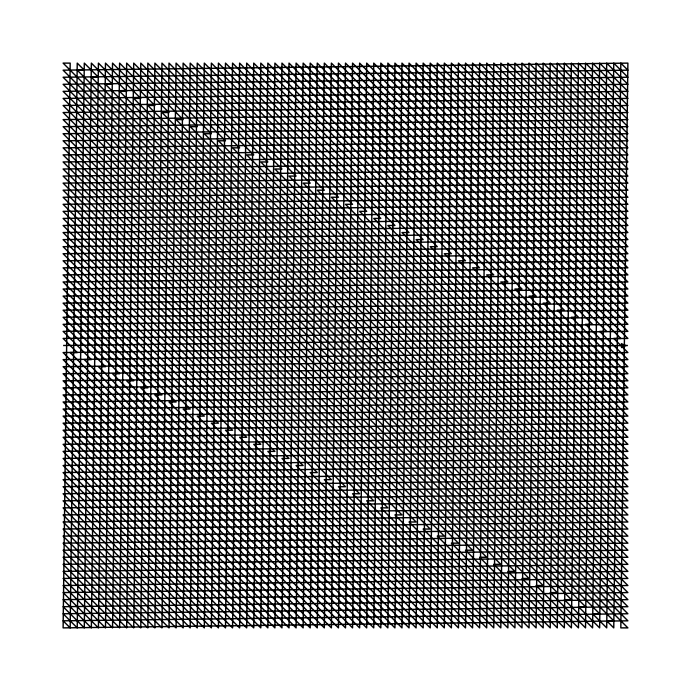

{{80,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,-80},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},«6446»,{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,-80},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{-1,1},{80,1}}

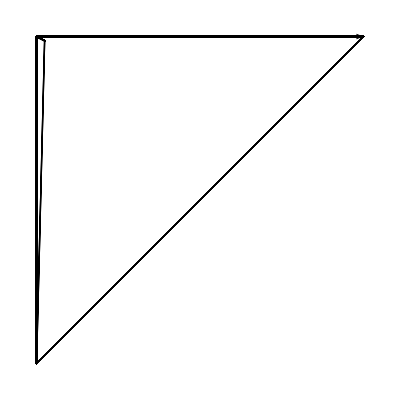

```mathematica
sq=ctvy
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
StringReplace["1 99 197 295 393 491 589 687 785 883 981 1079 1177 1275 1373 1471 1569 1667 1765 1863 1961 2059 2157 2255 2353 2451 2549 2647 2745 2843 2941 3039 3137 3235 3333 3431 3529 3627 3725 3823 3921 4019 4117 4215 4313 4411 4509 4607 4705 4803 4901 4999 5097 5195 5293 5391 5489 5587 5685 5783 5881 5979 6077 6175 6273 6371 6469 6567 6665 6763 6861 6959 7057 7155 7253 7351 7449 7547 7645 7743 7841 7939 8037 8135 8233 8331 8429 8527 8625 8723 8821 8919 9017 9115 9213 9311 9409
198 296 394 492 590 688 786 884 982 1080 1178 1276 1374 1472 1570 1668 1766 1864 1962 2060 2158 2256 2354 2452 2550 2648 2746 2844 2942 3040 3138 3236 3334 3432 3530 3628 3726 3824 3922 4020 4118 4216 4314 4412 4510 4608 4706 4804 4902 5000 5098 5196 5294 5392 5490 5588 5686 5784 5882 5980 6078 6176 6274 6372 6470 6568 6666 6764 6862 6960 7058 7156 7254 7352 7450 7548 7646 7744 7842 7940 8038 8136 8234 8332 8430 8528 8626 8724 8822 8920 9018 9116 9214 9312 9313 2 100
395 493 591 689 787 885 983 1081 1179 1277 1375 1473 1571 1669 1767 1865 1963 2061 2159 2257 2355 2453 2551 2649 2747 2845 2943 3041 3139 3237 3335 3433 3531 3629 3727 3825 3923 4021 4119 4217 4315 4413 4511 4609 4707 4805 4903 5001 5099 5197 5295 5393 5491 5589 5687 5785 5883 5981 6079 6177 6275 6373 6471 6569 6667 6765 6863 6961 7059 7157 7255 7353 7451 7549 7647 7745 7843 7941 8039 8137 8235 8333 8431 8529 8627 8725 8823 8921 9019 9117 9215 9216 9314 3 101 199 297
592 690 788 886 984 1082 1180 1278 1376 1474 1572 1670 1768 1866 1964 2062 2160 2258 2356 2454 2552 2650 2748 2846 2944 3042 3140 3238 3336 3434 3532 3630 3728 3826 3924 4022 4120 4218 4316 4414 4512 4610 4708 4806 4904 5002 5100 5198 5296 5394 5492 5590 5688 5786 5884 5982 6080 6178 6276 6374 6472 6570 6668 6766 6864 6962 7060 7158 7256 7354 7452 7550 7648 7746 7844 7942 8040 8138 8236 8334 8432 8530 8628 8726 8824 8922 9020 9118 9119 9217 9315 4 102 200 298 396 494
789 887 985 1083 1181 1279 1377 1475 1573 1671 1769 1867 1965 2063 2161 2259 2357 2455 2553 2651 2749 2847 2945 3043 3141 3239 3337 3435 3533 3631 3729 3827 3925 4023 4121 4219 4317 4415 4513 4611 4709 4807 4905 5003 5101 5199 5297 5395 5493 5591 5689 5787 5885 5983 6081 6179 6277 6375 6473 6571 6669 6767 6865 6963 7061 7159 7257 7355 7453 7551 7649 7747 7845 7943 8041 8139 8237 8335 8433 8531 8629 8727 8825 8923 9021 9022 9120 9218 9316 5 103 201 299 397 495 593 691
986 1084 1182 1280 1378 1476 1574 1672 1770 1868 1966 2064 2162 2260 2358 2456 2554 2652 2750 2848 2946 3044 3142 3240 3338 3436 3534 3632 3730 3828 3926 4024 4122 4220 4318 4416 4514 4612 4710 4808 4906 5004 5102 5200 5298 5396 5494 5592 5690 5788 5886 5984 6082 6180 6278 6376 6474 6572 6670 6768 6866 6964 7062 7160 7258 7356 7454 7552 7650 7748 7846 7944 8042 8140 8238 8336 8434 8532 8630 8728 8826 8924 8925 9023 9121 9219 9317 6 104 202 300 398 496 594 692 790 888
1183 1281 1379 1477 1575 1673 1771 1869 1967 2065 2163 2261 2359 2457 2555 2653 2751 2849 2947 3045 3143 3241 3339 3437 3535 3633 3731 3829 3927 4025 4123 4221 4319 4417 4515 4613 4711 4809 4907 5005 5103 5201 5299 5397 5495 5593 5691 5789 5887 5985 6083 6181 6279 6377 6475 6573 6671 6769 6867 6965 7063 7161 7259 7357 7455 7553 7651 7749 7847 7945 8043 8141 8239 8337 8435 8533 8631 8729 8827 8828 8926 9024 9122 9220 9318 7 105 203 301 399 497 595 693 791 889 987 1085
1380 1478 1576 1674 1772 1870 1968 2066 2164 2262 2360 2458 2556 2654 2752 2850 2948 3046 3144 3242 3340 3438 3536 3634 3732 3830 3928 4026 4124 4222 4320 4418 4516 4614 4712 4810 4908 5006 5104 5202 5300 5398 5496 5594 5692 5790 5888 5986 6084 6182 6280 6378 6476 6574 6672 6770 6868 6966 7064 7162 7260 7358 7456 7554 7652 7750 7848 7946 8044 8142 8240 8338 8436 8534 8632 8730 8731 8829 8927 9025 9123 9221 9319 8 106 204 302 400 498 596 694 792 890 988 1086 1184 1282
1577 1675 1773 1871 1969 2067 2165 2263 2361 2459 2557 2655 2753 2851 2949 3047 3145 3243 3341 3439 3537 3635 3733 3831 3929 4027 4125 4223 4321 4419 4517 4615 4713 4811 4909 5007 5105 5203 5301 5399 5497 5595 5693 5791 5889 5987 6085 6183 6281 6379 6477 6575 6673 6771 6869 6967 7065 7163 7261 7359 7457 7555 7653 7751 7849 7947 8045 8143 8241 8339 8437 8535 8633 8634 8732 8830 8928 9026 9124 9222 9320 9 107 205 303 401 499 597 695 793 891 989 1087 1185 1283 1381 1479
1774 1872 1970 2068 2166 2264 2362 2460 2558 2656 2754 2852 2950 3048 3146 3244 3342 3440 3538 3636 3734 3832 3930 4028 4126 4224 4322 4420 4518 4616 4714 4812 4910 5008 5106 5204 5302 5400 5498 5596 5694 5792 5890 5988 6086 6184 6282 6380 6478 6576 6674 6772 6870 6968 7066 7164 7262 7360 7458 7556 7654 7752 7850 7948 8046 8144 8242 8340 8438 8536 8537 8635 8733 8831 8929 9027 9125 9223 9321 10 108 206 304 402 500 598 696 794 892 990 1088 1186 1284 1382 1480 1578 1676
1971 2069 2167 2265 2363 2461 2559 2657 2755 2853 2951 3049 3147 3245 3343 3441 3539 3637 3735 3833 3931 4029 4127 4225 4323 4421 4519 4617 4715 4813 4911 5009 5107 5205 5303 5401 5499 5597 5695 5793 5891 5989 6087 6185 6283 6381 6479 6577 6675 6773 6871 6969 7067 7165 7263 7361 7459 7557 7655 7753 7851 7949 8047 8145 8243 8341 8439 8440 8538 8636 8734 8832 8930 9028 9126 9224 9322 11 109 207 305 403 501 599 697 795 893 991 1089 1187 1285 1383 1481 1579 1677 1775 1873
2168 2266 2364 2462 2560 2658 2756 2854 2952 3050 3148 3246 3344 3442 3540 3638 3736 3834 3932 4030 4128 4226 4324 4422 4520 4618 4716 4814 4912 5010 5108 5206 5304 5402 5500 5598 5696 5794 5892 5990 6088 6186 6284 6382 6480 6578 6676 6774 6872 6970 7068 7166 7264 7362 7460 7558 7656 7754 7852 7950 8048 8146 8244 8342 8343 8441 8539 8637 8735 8833 8931 9029 9127 9225 9323 12 110 208 306 404 502 600 698 796 894 992 1090 1188 1286 1384 1482 1580 1678 1776 1874 1972 2070
2365 2463 2561 2659 2757 2855 2953 3051 3149 3247 3345 3443 3541 3639 3737 3835 3933 4031 4129 4227 4325 4423 4521 4619 4717 4815 4913 5011 5109 5207 5305 5403 5501 5599 5697 5795 5893 5991 6089 6187 6285 6383 6481 6579 6677 6775 6873 6971 7069 7167 7265 7363 7461 7559 7657 7755 7853 7951 8049 8147 8245 8246 8344 8442 8540 8638 8736 8834 8932 9030 9128 9226 9324 13 111 209 307 405 503 601 699 797 895 993 1091 1189 1287 1385 1483 1581 1679 1777 1875 1973 2071 2169 2267
2562 2660 2758 2856 2954 3052 3150 3248 3346 3444 3542 3640 3738 3836 3934 4032 4130 4228 4326 4424 4522 4620 4718 4816 4914 5012 5110 5208 5306 5404 5502 5600 5698 5796 5894 5992 6090 6188 6286 6384 6482 6580 6678 6776 6874 6972 7070 7168 7266 7364 7462 7560 7658 7756 7854 7952 8050 8148 8149 8247 8345 8443 8541 8639 8737 8835 8933 9031 9129 9227 9325 14 112 210 308 406 504 602 700 798 896 994 1092 1190 1288 1386 1484 1582 1680 1778 1876 1974 2072 2170 2268 2366 2464
2759 2857 2955 3053 3151 3249 3347 3445 3543 3641 3739 3837 3935 4033 4131 4229 4327 4425 4523 4621 4719 4817 4915 5013 5111 5209 5307 5405 5503 5601 5699 5797 5895 5993 6091 6189 6287 6385 6483 6581 6679 6777 6875 6973 7071 7169 7267 7365 7463 7561 7659 7757 7855 7953 8051 8052 8150 8248 8346 8444 8542 8640 8738 8836 8934 9032 9130 9228 9326 15 113 211 309 407 505 603 701 799 897 995 1093 1191 1289 1387 1485 1583 1681 1779 1877 1975 2073 2171 2269 2367 2465 2563 2661
2956 3054 3152 3250 3348 3446 3544 3642 3740 3838 3936 4034 4132 4230 4328 4426 4524 4622 4720 4818 4916 5014 5112 5210 5308 5406 5504 5602 5700 5798 5896 5994 6092 6190 6288 6386 6484 6582 6680 6778 6876 6974 7072 7170 7268 7366 7464 7562 7660 7758 7856 7954 7955 8053 8151 8249 8347 8445 8543 8641 8739 8837 8935 9033 9131 9229 9327 16 114 212 310 408 506 604 702 800 898 996 1094 1192 1290 1388 1486 1584 1682 1780 1878 1976 2074 2172 2270 2368 2466 2564 2662 2760 2858
3153 3251 3349 3447 3545 3643 3741 3839 3937 4035 4133 4231 4329 4427 4525 4623 4721 4819 4917 5015 5113 5211 5309 5407 5505 5603 5701 5799 5897 5995 6093 6191 6289 6387 6485 6583 6681 6779 6877 6975 7073 7171 7269 7367 7465 7563 7661 7759 7857 7858 7956 8054 8152 8250 8348 8446 8544 8642 8740 8838 8936 9034 9132 9230 9328 17 115 213 311 409 507 605 703 801 899 997 1095 1193 1291 1389 1487 1585 1683 1781 1879 1977 2075 2173 2271 2369 2467 2565 2663 2761 2859 2957 3055
3350 3448 3546 3644 3742 3840 3938 4036 4134 4232 4330 4428 4526 4624 4722 4820 4918 5016 5114 5212 5310 5408 5506 5604 5702 5800 5898 5996 6094 6192 6290 6388 6486 6584 6682 6780 6878 6976 7074 7172 7270 7368 7466 7564 7662 7760 7761 7859 7957 8055 8153 8251 8349 8447 8545 8643 8741 8839 8937 9035 9133 9231 9329 18 116 214 312 410 508 606 704 802 900 998 1096 1194 1292 1390 1488 1586 1684 1782 1880 1978 2076 2174 2272 2370 2468 2566 2664 2762 2860 2958 3056 3154 3252
3547 3645 3743 3841 3939 4037 4135 4233 4331 4429 4527 4625 4723 4821 4919 5017 5115 5213 5311 5409 5507 5605 5703 5801 5899 5997 6095 6193 6291 6389 6487 6585 6683 6781 6879 6977 7075 7173 7271 7369 7467 7565 7663 7664 7762 7860 7958 8056 8154 8252 8350 8448 8546 8644 8742 8840 8938 9036 9134 9232 9330 19 117 215 313 411 509 607 705 803 901 999 1097 1195 1293 1391 1489 1587 1685 1783 1881 1979 2077 2175 2273 2371 2469 2567 2665 2763 2861 2959 3057 3155 3253 3351 3449
3744 3842 3940 4038 4136 4234 4332 4430 4528 4626 4724 4822 4920 5018 5116 5214 5312 5410 5508 5606 5704 5802 5900 5998 6096 6194 6292 6390 6488 6586 6684 6782 6880 6978 7076 7174 7272 7370 7468 7566 7567 7665 7763 7861 7959 8057 8155 8253 8351 8449 8547 8645 8743 8841 8939 9037 9135 9233 9331 20 118 216 314 412 510 608 706 804 902 1000 1098 1196 1294 1392 1490 1588 1686 1784 1882 1980 2078 2176 2274 2372 2470 2568 2666 2764 2862 2960 3058 3156 3254 3352 3450 3548 3646
3941 4039 4137 4235 4333 4431 4529 4627 4725 4823 4921 5019 5117 5215 5313 5411 5509 5607 5705 5803 5901 5999 6097 6195 6293 6391 6489 6587 6685 6783 6881 6979 7077 7175 7273 7371 7469 7470 7568 7666 7764 7862 7960 8058 8156 8254 8352 8450 8548 8646 8744 8842 8940 9038 9136 9234 9332 21 119 217 315 413 511 609 707 805 903 1001 1099 1197 1295 1393 1491 1589 1687 1785 1883 1981 2079 2177 2275 2373 2471 2569 2667 2765 2863 2961 3059 3157 3255 3353 3451 3549 3647 3745 3843
4138 4236 4334 4432 4530 4628 4726 4824 4922 5020 5118 5216 5314 5412 5510 5608 5706 5804 5902 6000 6098 6196 6294 6392 6490 6588 6686 6784 6882 6980 7078 7176 7274 7372 7373 7471 7569 7667 7765 7863 7961 8059 8157 8255 8353 8451 8549 8647 8745 8843 8941 9039 9137 9235 9333 22 120 218 316 414 512 610 708 806 904 1002 1100 1198 1296 1394 1492 1590 1688 1786 1884 1982 2080 2178 2276 2374 2472 2570 2668 2766 2864 2962 3060 3158 3256 3354 3452 3550 3648 3746 3844 3942 4040
4335 4433 4531 4629 4727 4825 4923 5021 5119 5217 5315 5413 5511 5609 5707 5805 5903 6001 6099 6197 6295 6393 6491 6589 6687 6785 6883 6981 7079 7177 7275 7276 7374 7472 7570 7668 7766 7864 7962 8060 8158 8256 8354 8452 8550 8648 8746 8844 8942 9040 9138 9236 9334 23 121 219 317 415 513 611 709 807 905 1003 1101 1199 1297 1395 1493 1591 1689 1787 1885 1983 2081 2179 2277 2375 2473 2571 2669 2767 2865 2963 3061 3159 3257 3355 3453 3551 3649 3747 3845 3943 4041 4139 4237
4532 4630 4728 4826 4924 5022 5120 5218 5316 5414 5512 5610 5708 5806 5904 6002 6100 6198 6296 6394 6492 6590 6688 6786 6884 6982 7080 7178 7179 7277 7375 7473 7571 7669 7767 7865 7963 8061 8159 8257 8355 8453 8551 8649 8747 8845 8943 9041 9139 9237 9335 24 122 220 318 416 514 612 710 808 906 1004 1102 1200 1298 1396 1494 1592 1690 1788 1886 1984 2082 2180 2278 2376 2474 2572 2670 2768 2866 2964 3062 3160 3258 3356 3454 3552 3650 3748 3846 3944 4042 4140 4238 4336 4434
4729 4827 4925 5023 5121 5219 5317 5415 5513 5611 5709 5807 5905 6003 6101 6199 6297 6395 6493 6591 6689 6787 6885 6983 7081 7082 7180 7278 7376 7474 7572 7670 7768 7866 7964 8062 8160 8258 8356 8454 8552 8650 8748 8846 8944 9042 9140 9238 9336 25 123 221 319 417 515 613 711 809 907 1005 1103 1201 1299 1397 1495 1593 1691 1789 1887 1985 2083 2181 2279 2377 2475 2573 2671 2769 2867 2965 3063 3161 3259 3357 3455 3553 3651 3749 3847 3945 4043 4141 4239 4337 4435 4533 4631
4926 5024 5122 5220 5318 5416 5514 5612 5710 5808 5906 6004 6102 6200 6298 6396 6494 6592 6690 6788 6886 6984 6985 7083 7181 7279 7377 7475 7573 7671 7769 7867 7965 8063 8161 8259 8357 8455 8553 8651 8749 8847 8945 9043 9141 9239 9337 26 124 222 320 418 516 614 712 810 908 1006 1104 1202 1300 1398 1496 1594 1692 1790 1888 1986 2084 2182 2280 2378 2476 2574 2672 2770 2868 2966 3064 3162 3260 3358 3456 3554 3652 3750 3848 3946 4044 4142 4240 4338 4436 4534 4632 4730 4828
5123 5221 5319 5417 5515 5613 5711 5809 5907 6005 6103 6201 6299 6397 6495 6593 6691 6789 6887 6888 6986 7084 7182 7280 7378 7476 7574 7672 7770 7868 7966 8064 8162 8260 8358 8456 8554 8652 8750 8848 8946 9044 9142 9240 9338 27 125 223 321 419 517 615 713 811 909 1007 1105 1203 1301 1399 1497 1595 1693 1791 1889 1987 2085 2183 2281 2379 2477 2575 2673 2771 2869 2967 3065 3163 3261 3359 3457 3555 3653 3751 3849 3947 4045 4143 4241 4339 4437 4535 4633 4731 4829 4927 5025
5320 5418 5516 5614 5712 5810 5908 6006 6104 6202 6300 6398 6496 6594 6692 6790 6791 6889 6987 7085 7183 7281 7379 7477 7575 7673 7771 7869 7967 8065 8163 8261 8359 8457 8555 8653 8751 8849 8947 9045 9143 9241 9339 28 126 224 322 420 518 616 714 812 910 1008 1106 1204 1302 1400 1498 1596 1694 1792 1890 1988 2086 2184 2282 2380 2478 2576 2674 2772 2870 2968 3066 3164 3262 3360 3458 3556 3654 3752 3850 3948 4046 4144 4242 4340 4438 4536 4634 4732 4830 4928 5026 5124 5222
5517 5615 5713 5811 5909 6007 6105 6203 6301 6399 6497 6595 6693 6694 6792 6890 6988 7086 7184 7282 7380 7478 7576 7674 7772 7870 7968 8066 8164 8262 8360 8458 8556 8654 8752 8850 8948 9046 9144 9242 9340 29 127 225 323 421 519 617 715 813 911 1009 1107 1205 1303 1401 1499 1597 1695 1793 1891 1989 2087 2185 2283 2381 2479 2577 2675 2773 2871 2969 3067 3165 3263 3361 3459 3557 3655 3753 3851 3949 4047 4145 4243 4341 4439 4537 4635 4733 4831 4929 5027 5125 5223 5321 5419
5714 5812 5910 6008 6106 6204 6302 6400 6498 6596 6597 6695 6793 6891 6989 7087 7185 7283 7381 7479 7577 7675 7773 7871 7969 8067 8165 8263 8361 8459 8557 8655 8753 8851 8949 9047 9145 9243 9341 30 128 226 324 422 520 618 716 814 912 1010 1108 1206 1304 1402 1500 1598 1696 1794 1892 1990 2088 2186 2284 2382 2480 2578 2676 2774 2872 2970 3068 3166 3264 3362 3460 3558 3656 3754 3852 3950 4048 4146 4244 4342 4440 4538 4636 4734 4832 4930 5028 5126 5224 5322 5420 5518 5616
5911 6009 6107 6205 6303 6401 6499 6500 6598 6696 6794 6892 6990 7088 7186 7284 7382 7480 7578 7676 7774 7872 7970 8068 8166 8264 8362 8460 8558 8656 8754 8852 8950 9048 9146 9244 9342 31 129 227 325 423 521 619 717 815 913 1011 1109 1207 1305 1403 1501 1599 1697 1795 1893 1991 2089 2187 2285 2383 2481 2579 2677 2775 2873 2971 3069 3167 3265 3363 3461 3559 3657 3755 3853 3951 4049 4147 4245 4343 4441 4539 4637 4735 4833 4931 5029 5127 5225 5323 5421 5519 5617 5715 5813
6108 6206 6304 6402 6403 6501 6599 6697 6795 6893 6991 7089 7187 7285 7383 7481 7579 7677 7775 7873 7971 8069 8167 8265 8363 8461 8559 8657 8755 8853 8951 9049 9147 9245 9343 32 130 228 326 424 522 620 718 816 914 1012 1110 1208 1306 1404 1502 1600 1698 1796 1894 1992 2090 2188 2286 2384 2482 2580 2678 2776 2874 2972 3070 3168 3266 3364 3462 3560 3658 3756 3854 3952 4050 4148 4246 4344 4442 4540 4638 4736 4834 4932 5030 5128 5226 5324 5422 5520 5618 5716 5814 5912 6010
6305 6306 6404 6502 6600 6698 6796 6894 6992 7090 7188 7286 7384 7482 7580 7678 7776 7874 7972 8070 8168 8266 8364 8462 8560 8658 8756 8854 8952 9050 9148 9246 9344 33 131 229 327 425 523 621 719 817 915 1013 1111 1209 1307 1405 1503 1601 1699 1797 1895 1993 2091 2189 2287 2385 2483 2581 2679 2777 2875 2973 3071 3169 3267 3365 3463 3561 3659 3757 3855 3953 4051 4149 4247 4345 4443 4541 4639 4737 4835 4933 5031 5129 5227 5325 5423 5521 5619 5717 5815 5913 6011 6109 6207
6405 6503 6601 6699 6797 6895 6993 7091 7189 7287 7385 7483 7581 7679 7777 7875 7973 8071 8169 8267 8365 8463 8561 8659 8757 8855 8953 9051 9149 9247 9345 34 132 230 328 426 524 622 720 818 916 1014 1112 1210 1308 1406 1504 1602 1700 1798 1896 1994 2092 2190 2288 2386 2484 2582 2680 2778 2876 2974 3072 3170 3268 3366 3464 3562 3660 3758 3856 3954 4052 4150 4248 4346 4444 4542 4640 4738 4836 4934 5032 5130 5228 5326 5424 5522 5620 5718 5816 5914 6012 6110 6208 6209 6307
6602 6700 6798 6896 6994 7092 7190 7288 7386 7484 7582 7680 7778 7876 7974 8072 8170 8268 8366 8464 8562 8660 8758 8856 8954 9052 9150 9248 9346 35 133 231 329 427 525 623 721 819 917 1015 1113 1211 1309 1407 1505 1603 1701 1799 1897 1995 2093 2191 2289 2387 2485 2583 2681 2779 2877 2975 3073 3171 3269 3367 3465 3563 3661 3759 3857 3955 4053 4151 4249 4347 4445 4543 4641 4739 4837 4935 5033 5131 5229 5327 5425 5523 5621 5719 5817 5915 6013 6111 6112 6210 6308 6406 6504
6799 6897 6995 7093 7191 7289 7387 7485 7583 7681 7779 7877 7975 8073 8171 8269 8367 8465 8563 8661 8759 8857 8955 9053 9151 9249 9347 36 134 232 330 428 526 624 722 820 918 1016 1114 1212 1310 1408 1506 1604 1702 1800 1898 1996 2094 2192 2290 2388 2486 2584 2682 2780 2878 2976 3074 3172 3270 3368 3466 3564 3662 3760 3858 3956 4054 4152 4250 4348 4446 4544 4642 4740 4838 4936 5034 5132 5230 5328 5426 5524 5622 5720 5818 5916 6014 6015 6113 6211 6309 6407 6505 6603 6701
6996 7094 7192 7290 7388 7486 7584 7682 7780 7878 7976 8074 8172 8270 8368 8466 8564 8662 8760 8858 8956 9054 9152 9250 9348 37 135 233 331 429 527 625 723 821 919 1017 1115 1213 1311 1409 1507 1605 1703 1801 1899 1997 2095 2193 2291 2389 2487 2585 2683 2781 2879 2977 3075 3173 3271 3369 3467 3565 3663 3761 3859 3957 4055 4153 4251 4349 4447 4545 4643 4741 4839 4937 5035 5133 5231 5329 5427 5525 5623 5721 5819 5917 5918 6016 6114 6212 6310 6408 6506 6604 6702 6800 6898
7193 7291 7389 7487 7585 7683 7781 7879 7977 8075 8173 8271 8369 8467 8565 8663 8761 8859 8957 9055 9153 9251 9349 38 136 234 332 430 528 626 724 822 920 1018 1116 1214 1312 1410 1508 1606 1704 1802 1900 1998 2096 2194 2292 2390 2488 2586 2684 2782 2880 2978 3076 3174 3272 3370 3468 3566 3664 3762 3860 3958 4056 4154 4252 4350 4448 4546 4644 4742 4840 4938 5036 5134 5232 5330 5428 5526 5624 5722 5820 5821 5919 6017 6115 6213 6311 6409 6507 6605 6703 6801 6899 6997 7095
7390 7488 7586 7684 7782 7880 7978 8076 8174 8272 8370 8468 8566 8664 8762 8860 8958 9056 9154 9252 9350 39 137 235 333 431 529 627 725 823 921 1019 1117 1215 1313 1411 1509 1607 1705 1803 1901 1999 2097 2195 2293 2391 2489 2587 2685 2783 2881 2979 3077 3175 3273 3371 3469 3567 3665 3763 3861 3959 4057 4155 4253 4351 4449 4547 4645 4743 4841 4939 5037 5135 5233 5331 5429 5527 5625 5723 5724 5822 5920 6018 6116 6214 6312 6410 6508 6606 6704 6802 6900 6998 7096 7194 7292
7587 7685 7783 7881 7979 8077 8175 8273 8371 8469 8567 8665 8763 8861 8959 9057 9155 9253 9351 40 138 236 334 432 530 628 726 824 922 1020 1118 1216 1314 1412 1510 1608 1706 1804 1902 2000 2098 2196 2294 2392 2490 2588 2686 2784 2882 2980 3078 3176 3274 3372 3470 3568 3666 3764 3862 3960 4058 4156 4254 4352 4450 4548 4646 4744 4842 4940 5038 5136 5234 5332 5430 5528 5626 5627 5725 5823 5921 6019 6117 6215 6313 6411 6509 6607 6705 6803 6901 6999 7097 7195 7293 7391 7489
7784 7882 7980 8078 8176 8274 8372 8470 8568 8666 8764 8862 8960 9058 9156 9254 9352 41 139 237 335 433 531 629 727 825 923 1021 1119 1217 1315 1413 1511 1609 1707 1805 1903 2001 2099 2197 2295 2393 2491 2589 2687 2785 2883 2981 3079 3177 3275 3373 3471 3569 3667 3765 3863 3961 4059 4157 4255 4353 4451 4549 4647 4745 4843 4941 5039 5137 5235 5333 5431 5529 5530 5628 5726 5824 5922 6020 6118 6216 6314 6412 6510 6608 6706 6804 6902 7000 7098 7196 7294 7392 7490 7588 7686
7981 8079 8177 8275 8373 8471 8569 8667 8765 8863 8961 9059 9157 9255 9353 42 140 238 336 434 532 630 728 826 924 1022 1120 1218 1316 1414 1512 1610 1708 1806 1904 2002 2100 2198 2296 2394 2492 2590 2688 2786 2884 2982 3080 3178 3276 3374 3472 3570 3668 3766 3864 3962 4060 4158 4256 4354 4452 4550 4648 4746 4844 4942 5040 5138 5236 5334 5432 5433 5531 5629 5727 5825 5923 6021 6119 6217 6315 6413 6511 6609 6707 6805 6903 7001 7099 7197 7295 7393 7491 7589 7687 7785 7883
8178 8276 8374 8472 8570 8668 8766 8864 8962 9060 9158 9256 9354 43 141 239 337 435 533 631 729 827 925 1023 1121 1219 1317 1415 1513 1611 1709 1807 1905 2003 2101 2199 2297 2395 2493 2591 2689 2787 2885 2983 3081 3179 3277 3375 3473 3571 3669 3767 3865 3963 4061 4159 4257 4355 4453 4551 4649 4747 4845 4943 5041 5139 5237 5335 5336 5434 5532 5630 5728 5826 5924 6022 6120 6218 6316 6414 6512 6610 6708 6806 6904 7002 7100 7198 7296 7394 7492 7590 7688 7786 7884 7982 8080
8375 8473 8571 8669 8767 8865 8963 9061 9159 9257 9355 44 142 240 338 436 534 632 730 828 926 1024 1122 1220 1318 1416 1514 1612 1710 1808 1906 2004 2102 2200 2298 2396 2494 2592 2690 2788 2886 2984 3082 3180 3278 3376 3474 3572 3670 3768 3866 3964 4062 4160 4258 4356 4454 4552 4650 4748 4846 4944 5042 5140 5238 5239 5337 5435 5533 5631 5729 5827 5925 6023 6121 6219 6317 6415 6513 6611 6709 6807 6905 7003 7101 7199 7297 7395 7493 7591 7689 7787 7885 7983 8081 8179 8277
8572 8670 8768 8866 8964 9062 9160 9258 9356 45 143 241 339 437 535 633 731 829 927 1025 1123 1221 1319 1417 1515 1613 1711 1809 1907 2005 2103 2201 2299 2397 2495 2593 2691 2789 2887 2985 3083 3181 3279 3377 3475 3573 3671 3769 3867 3965 4063 4161 4259 4357 4455 4553 4651 4749 4847 4945 5043 5141 5142 5240 5338 5436 5534 5632 5730 5828 5926 6024 6122 6220 6318 6416 6514 6612 6710 6808 6906 7004 7102 7200 7298 7396 7494 7592 7690 7788 7886 7984 8082 8180 8278 8376 8474
8769 8867 8965 9063 9161 9259 9357 46 144 242 340 438 536 634 732 830 928 1026 1124 1222 1320 1418 1516 1614 1712 1810 1908 2006 2104 2202 2300 2398 2496 2594 2692 2790 2888 2986 3084 3182 3280 3378 3476 3574 3672 3770 3868 3966 4064 4162 4260 4358 4456 4554 4652 4750 4848 4946 5044 5045 5143 5241 5339 5437 5535 5633 5731 5829 5927 6025 6123 6221 6319 6417 6515 6613 6711 6809 6907 7005 7103 7201 7299 7397 7495 7593 7691 7789 7887 7985 8083 8181 8279 8377 8475 8573 8671
8966 9064 9162 9260 9358 47 145 243 341 439 537 635 733 831 929 1027 1125 1223 1321 1419 1517 1615 1713 1811 1909 2007 2105 2203 2301 2399 2497 2595 2693 2791 2889 2987 3085 3183 3281 3379 3477 3575 3673 3771 3869 3967 4065 4163 4261 4359 4457 4555 4653 4751 4849 4947 4948 5046 5144 5242 5340 5438 5536 5634 5732 5830 5928 6026 6124 6222 6320 6418 6516 6614 6712 6810 6908 7006 7104 7202 7300 7398 7496 7594 7692 7790 7888 7986 8084 8182 8280 8378 8476 8574 8672 8770 8868
9163 9261 9359 48 146 244 342 440 538 636 734 832 930 1028 1126 1224 1322 1420 1518 1616 1714 1812 1910 2008 2106 2204 2302 2400 2498 2596 2694 2792 2890 2988 3086 3184 3282 3380 3478 3576 3674 3772 3870 3968 4066 4164 4262 4360 4458 4556 4654 4752 4850 4851 4949 5047 5145 5243 5341 5439 5537 5635 5733 5831 5929 6027 6125 6223 6321 6419 6517 6615 6713 6811 6909 7007 7105 7203 7301 7399 7497 7595 7693 7791 7889 7987 8085 8183 8281 8379 8477 8575 8673 8771 8869 8967 9065
9360 49 147 245 343 441 539 637 735 833 931 1029 1127 1225 1323 1421 1519 1617 1715 1813 1911 2009 2107 2205 2303 2401 2499 2597 2695 2793 2891 2989 3087 3185 3283 3381 3479 3577 3675 3773 3871 3969 4067 4165 4263 4361 4459 4557 4655 4753 4754 4852 4950 5048 5146 5244 5342 5440 5538 5636 5734 5832 5930 6028 6126 6224 6322 6420 6518 6616 6714 6812 6910 7008 7106 7204 7302 7400 7498 7596 7694 7792 7890 7988 8086 8184 8282 8380 8478 8576 8674 8772 8870 8968 9066 9164 9262
148 246 344 442 540 638 736 834 932 1030 1128 1226 1324 1422 1520 1618 1716 1814 1912 2010 2108 2206 2304 2402 2500 2598 2696 2794 2892 2990 3088 3186 3284 3382 3480 3578 3676 3774 3872 3970 4068 4166 4264 4362 4460 4558 4656 4657 4755 4853 4951 5049 5147 5245 5343 5441 5539 5637 5735 5833 5931 6029 6127 6225 6323 6421 6519 6617 6715 6813 6911 7009 7107 7205 7303 7401 7499 7597 7695 7793 7891 7989 8087 8185 8283 8381 8479 8577 8675 8773 8871 8969 9067 9165 9263 9361 50
345 443 541 639 737 835 933 1031 1129 1227 1325 1423 1521 1619 1717 1815 1913 2011 2109 2207 2305 2403 2501 2599 2697 2795 2893 2991 3089 3187 3285 3383 3481 3579 3677 3775 3873 3971 4069 4167 4265 4363 4461 4559 4560 4658 4756 4854 4952 5050 5148 5246 5344 5442 5540 5638 5736 5834 5932 6030 6128 6226 6324 6422 6520 6618 6716 6814 6912 7010 7108 7206 7304 7402 7500 7598 7696 7794 7892 7990 8088 8186 8284 8382 8480 8578 8676 8774 8872 8970 9068 9166 9264 9362 51 149 247
542 640 738 836 934 1032 1130 1228 1326 1424 1522 1620 1718 1816 1914 2012 2110 2208 2306 2404 2502 2600 2698 2796 2894 2992 3090 3188 3286 3384 3482 3580 3678 3776 3874 3972 4070 4168 4266 4364 4462 4463 4561 4659 4757 4855 4953 5051 5149 5247 5345 5443 5541 5639 5737 5835 5933 6031 6129 6227 6325 6423 6521 6619 6717 6815 6913 7011 7109 7207 7305 7403 7501 7599 7697 7795 7893 7991 8089 8187 8285 8383 8481 8579 8677 8775 8873 8971 9069 9167 9265 9363 52 150 248 346 444
739 837 935 1033 1131 1229 1327 1425 1523 1621 1719 1817 1915 2013 2111 2209 2307 2405 2503 2601 2699 2797 2895 2993 3091 3189 3287 3385 3483 3581 3679 3777 3875 3973 4071 4169 4267 4365 4366 4464 4562 4660 4758 4856 4954 5052 5150 5248 5346 5444 5542 5640 5738 5836 5934 6032 6130 6228 6326 6424 6522 6620 6718 6816 6914 7012 7110 7208 7306 7404 7502 7600 7698 7796 7894 7992 8090 8188 8286 8384 8482 8580 8678 8776 8874 8972 9070 9168 9266 9364 53 151 249 347 445 543 641
936 1034 1132 1230 1328 1426 1524 1622 1720 1818 1916 2014 2112 2210 2308 2406 2504 2602 2700 2798 2896 2994 3092 3190 3288 3386 3484 3582 3680 3778 3876 3974 4072 4170 4268 4269 4367 4465 4563 4661 4759 4857 4955 5053 5151 5249 5347 5445 5543 5641 5739 5837 5935 6033 6131 6229 6327 6425 6523 6621 6719 6817 6915 7013 7111 7209 7307 7405 7503 7601 7699 7797 7895 7993 8091 8189 8287 8385 8483 8581 8679 8777 8875 8973 9071 9169 9267 9365 54 152 250 348 446 544 642 740 838
1133 1231 1329 1427 1525 1623 1721 1819 1917 2015 2113 2211 2309 2407 2505 2603 2701 2799 2897 2995 3093 3191 3289 3387 3485 3583 3681 3779 3877 3975 4073 4171 4172 4270 4368 4466 4564 4662 4760 4858 4956 5054 5152 5250 5348 5446 5544 5642 5740 5838 5936 6034 6132 6230 6328 6426 6524 6622 6720 6818 6916 7014 7112 7210 7308 7406 7504 7602 7700 7798 7896 7994 8092 8190 8288 8386 8484 8582 8680 8778 8876 8974 9072 9170 9268 9366 55 153 251 349 447 545 643 741 839 937 1035
1330 1428 1526 1624 1722 1820 1918 2016 2114 2212 2310 2408 2506 2604 2702 2800 2898 2996 3094 3192 3290 3388 3486 3584 3682 3780 3878 3976 4074 4075 4173 4271 4369 4467 4565 4663 4761 4859 4957 5055 5153 5251 5349 5447 5545 5643 5741 5839 5937 6035 6133 6231 6329 6427 6525 6623 6721 6819 6917 7015 7113 7211 7309 7407 7505 7603 7701 7799 7897 7995 8093 8191 8289 8387 8485 8583 8681 8779 8877 8975 9073 9171 9269 9367 56 154 252 350 448 546 644 742 840 938 1036 1134 1232
1527 1625 1723 1821 1919 2017 2115 2213 2311 2409 2507 2605 2703 2801 2899 2997 3095 3193 3291 3389 3487 3585 3683 3781 3879 3977 3978 4076 4174 4272 4370 4468 4566 4664 4762 4860 4958 5056 5154 5252 5350 5448 5546 5644 5742 5840 5938 6036 6134 6232 6330 6428 6526 6624 6722 6820 6918 7016 7114 7212 7310 7408 7506 7604 7702 7800 7898 7996 8094 8192 8290 8388 8486 8584 8682 8780 8878 8976 9074 9172 9270 9368 57 155 253 351 449 547 645 743 841 939 1037 1135 1233 1331 1429
1724 1822 1920 2018 2116 2214 2312 2410 2508 2606 2704 2802 2900 2998 3096 3194 3292 3390 3488 3586 3684 3782 3880 3881 3979 4077 4175 4273 4371 4469 4567 4665 4763 4861 4959 5057 5155 5253 5351 5449 5547 5645 5743 5841 5939 6037 6135 6233 6331 6429 6527 6625 6723 6821 6919 7017 7115 7213 7311 7409 7507 7605 7703 7801 7899 7997 8095 8193 8291 8389 8487 8585 8683 8781 8879 8977 9075 9173 9271 9369 58 156 254 352 450 548 646 744 842 940 1038 1136 1234 1332 1430 1528 1626
1921 2019 2117 2215 2313 2411 2509 2607 2705 2803 2901 2999 3097 3195 3293 3391 3489 3587 3685 3783 3784 3882 3980 4078 4176 4274 4372 4470 4568 4666 4764 4862 4960 5058 5156 5254 5352 5450 5548 5646 5744 5842 5940 6038 6136 6234 6332 6430 6528 6626 6724 6822 6920 7018 7116 7214 7312 7410 7508 7606 7704 7802 7900 7998 8096 8194 8292 8390 8488 8586 8684 8782 8880 8978 9076 9174 9272 9370 59 157 255 353 451 549 647 745 843 941 1039 1137 1235 1333 1431 1529 1627 1725 1823
2118 2216 2314 2412 2510 2608 2706 2804 2902 3000 3098 3196 3294 3392 3490 3588 3686 3687 3785 3883 3981 4079 4177 4275 4373 4471 4569 4667 4765 4863 4961 5059 5157 5255 5353 5451 5549 5647 5745 5843 5941 6039 6137 6235 6333 6431 6529 6627 6725 6823 6921 7019 7117 7215 7313 7411 7509 7607 7705 7803 7901 7999 8097 8195 8293 8391 8489 8587 8685 8783 8881 8979 9077 9175 9273 9371 60 158 256 354 452 550 648 746 844 942 1040 1138 1236 1334 1432 1530 1628 1726 1824 1922 2020
2315 2413 2511 2609 2707 2805 2903 3001 3099 3197 3295 3393 3491 3589 3590 3688 3786 3884 3982 4080 4178 4276 4374 4472 4570 4668 4766 4864 4962 5060 5158 5256 5354 5452 5550 5648 5746 5844 5942 6040 6138 6236 6334 6432 6530 6628 6726 6824 6922 7020 7118 7216 7314 7412 7510 7608 7706 7804 7902 8000 8098 8196 8294 8392 8490 8588 8686 8784 8882 8980 9078 9176 9274 9372 61 159 257 355 453 551 649 747 845 943 1041 1139 1237 1335 1433 1531 1629 1727 1825 1923 2021 2119 2217
2512 2610 2708 2806 2904 3002 3100 3198 3296 3394 3492 3493 3591 3689 3787 3885 3983 4081 4179 4277 4375 4473 4571 4669 4767 4865 4963 5061 5159 5257 5355 5453 5551 5649 5747 5845 5943 6041 6139 6237 6335 6433 6531 6629 6727 6825 6923 7021 7119 7217 7315 7413 7511 7609 7707 7805 7903 8001 8099 8197 8295 8393 8491 8589 8687 8785 8883 8981 9079 9177 9275 9373 62 160 258 356 454 552 650 748 846 944 1042 1140 1238 1336 1434 1532 1630 1728 1826 1924 2022 2120 2218 2316 2414
2709 2807 2905 3003 3101 3199 3297 3395 3396 3494 3592 3690 3788 3886 3984 4082 4180 4278 4376 4474 4572 4670 4768 4866 4964 5062 5160 5258 5356 5454 5552 5650 5748 5846 5944 6042 6140 6238 6336 6434 6532 6630 6728 6826 6924 7022 7120 7218 7316 7414 7512 7610 7708 7806 7904 8002 8100 8198 8296 8394 8492 8590 8688 8786 8884 8982 9080 9178 9276 9374 63 161 259 357 455 553 651 749 847 945 1043 1141 1239 1337 1435 1533 1631 1729 1827 1925 2023 2121 2219 2317 2415 2513 2611
2906 3004 3102 3200 3298 3299 3397 3495 3593 3691 3789 3887 3985 4083 4181 4279 4377 4475 4573 4671 4769 4867 4965 5063 5161 5259 5357 5455 5553 5651 5749 5847 5945 6043 6141 6239 6337 6435 6533 6631 6729 6827 6925 7023 7121 7219 7317 7415 7513 7611 7709 7807 7905 8003 8101 8199 8297 8395 8493 8591 8689 8787 8885 8983 9081 9179 9277 9375 64 162 260 358 456 554 652 750 848 946 1044 1142 1240 1338 1436 1534 1632 1730 1828 1926 2024 2122 2220 2318 2416 2514 2612 2710 2808
3103 3201 3202 3300 3398 3496 3594 3692 3790 3888 3986 4084 4182 4280 4378 4476 4574 4672 4770 4868 4966 5064 5162 5260 5358 5456 5554 5652 5750 5848 5946 6044 6142 6240 6338 6436 6534 6632 6730 6828 6926 7024 7122 7220 7318 7416 7514 7612 7710 7808 7906 8004 8102 8200 8298 8396 8494 8592 8690 8788 8886 8984 9082 9180 9278 9376 65 163 261 359 457 555 653 751 849 947 1045 1143 1241 1339 1437 1535 1633 1731 1829 1927 2025 2123 2221 2319 2417 2515 2613 2711 2809 2907 3005
3203 3301 3399 3497 3595 3693 3791 3889 3987 4085 4183 4281 4379 4477 4575 4673 4771 4869 4967 5065 5163 5261 5359 5457 5555 5653 5751 5849 5947 6045 6143 6241 6339 6437 6535 6633 6731 6829 6927 7025 7123 7221 7319 7417 7515 7613 7711 7809 7907 8005 8103 8201 8299 8397 8495 8593 8691 8789 8887 8985 9083 9181 9279 9377 66 164 262 360 458 556 654 752 850 948 1046 1144 1242 1340 1438 1536 1634 1732 1830 1928 2026 2124 2222 2320 2418 2516 2614 2712 2810 2908 3006 3104 3105
3400 3498 3596 3694 3792 3890 3988 4086 4184 4282 4380 4478 4576 4674 4772 4870 4968 5066 5164 5262 5360 5458 5556 5654 5752 5850 5948 6046 6144 6242 6340 6438 6536 6634 6732 6830 6928 7026 7124 7222 7320 7418 7516 7614 7712 7810 7908 8006 8104 8202 8300 8398 8496 8594 8692 8790 8888 8986 9084 9182 9280 9378 67 165 263 361 459 557 655 753 851 949 1047 1145 1243 1341 1439 1537 1635 1733 1831 1929 2027 2125 2223 2321 2419 2517 2615 2713 2811 2909 3007 3008 3106 3204 3302
3597 3695 3793 3891 3989 4087 4185 4283 4381 4479 4577 4675 4773 4871 4969 5067 5165 5263 5361 5459 5557 5655 5753 5851 5949 6047 6145 6243 6341 6439 6537 6635 6733 6831 6929 7027 7125 7223 7321 7419 7517 7615 7713 7811 7909 8007 8105 8203 8301 8399 8497 8595 8693 8791 8889 8987 9085 9183 9281 9379 68 166 264 362 460 558 656 754 852 950 1048 1146 1244 1342 1440 1538 1636 1734 1832 1930 2028 2126 2224 2322 2420 2518 2616 2714 2812 2910 2911 3009 3107 3205 3303 3401 3499
3794 3892 3990 4088 4186 4284 4382 4480 4578 4676 4774 4872 4970 5068 5166 5264 5362 5460 5558 5656 5754 5852 5950 6048 6146 6244 6342 6440 6538 6636 6734 6832 6930 7028 7126 7224 7322 7420 7518 7616 7714 7812 7910 8008 8106 8204 8302 8400 8498 8596 8694 8792 8890 8988 9086 9184 9282 9380 69 167 265 363 461 559 657 755 853 951 1049 1147 1245 1343 1441 1539 1637 1735 1833 1931 2029 2127 2225 2323 2421 2519 2617 2715 2813 2814 2912 3010 3108 3206 3304 3402 3500 3598 3696
3991 4089 4187 4285 4383 4481 4579 4677 4775 4873 4971 5069 5167 5265 5363 5461 5559 5657 5755 5853 5951 6049 6147 6245 6343 6441 6539 6637 6735 6833 6931 7029 7127 7225 7323 7421 7519 7617 7715 7813 7911 8009 8107 8205 8303 8401 8499 8597 8695 8793 8891 8989 9087 9185 9283 9381 70 168 266 364 462 560 658 756 854 952 1050 1148 1246 1344 1442 1540 1638 1736 1834 1932 2030 2128 2226 2324 2422 2520 2618 2716 2717 2815 2913 3011 3109 3207 3305 3403 3501 3599 3697 3795 3893
4188 4286 4384 4482 4580 4678 4776 4874 4972 5070 5168 5266 5364 5462 5560 5658 5756 5854 5952 6050 6148 6246 6344 6442 6540 6638 6736 6834 6932 7030 7128 7226 7324 7422 7520 7618 7716 7814 7912 8010 8108 8206 8304 8402 8500 8598 8696 8794 8892 8990 9088 9186 9284 9382 71 169 267 365 463 561 659 757 855 953 1051 1149 1247 1345 1443 1541 1639 1737 1835 1933 2031 2129 2227 2325 2423 2521 2619 2620 2718 2816 2914 3012 3110 3208 3306 3404 3502 3600 3698 3796 3894 3992 4090
4385 4483 4581 4679 4777 4875 4973 5071 5169 5267 5365 5463 5561 5659 5757 5855 5953 6051 6149 6247 6345 6443 6541 6639 6737 6835 6933 7031 7129 7227 7325 7423 7521 7619 7717 7815 7913 8011 8109 8207 8305 8403 8501 8599 8697 8795 8893 8991 9089 9187 9285 9383 72 170 268 366 464 562 660 758 856 954 1052 1150 1248 1346 1444 1542 1640 1738 1836 1934 2032 2130 2228 2326 2424 2522 2523 2621 2719 2817 2915 3013 3111 3209 3307 3405 3503 3601 3699 3797 3895 3993 4091 4189 4287
4582 4680 4778 4876 4974 5072 5170 5268 5366 5464 5562 5660 5758 5856 5954 6052 6150 6248 6346 6444 6542 6640 6738 6836 6934 7032 7130 7228 7326 7424 7522 7620 7718 7816 7914 8012 8110 8208 8306 8404 8502 8600 8698 8796 8894 8992 9090 9188 9286 9384 73 171 269 367 465 563 661 759 857 955 1053 1151 1249 1347 1445 1543 1641 1739 1837 1935 2033 2131 2229 2327 2425 2426 2524 2622 2720 2818 2916 3014 3112 3210 3308 3406 3504 3602 3700 3798 3896 3994 4092 4190 4288 4386 4484
4779 4877 4975 5073 5171 5269 5367 5465 5563 5661 5759 5857 5955 6053 6151 6249 6347 6445 6543 6641 6739 6837 6935 7033 7131 7229 7327 7425 7523 7621 7719 7817 7915 8013 8111 8209 8307 8405 8503 8601 8699 8797 8895 8993 9091 9189 9287 9385 74 172 270 368 466 564 662 760 858 956 1054 1152 1250 1348 1446 1544 1642 1740 1838 1936 2034 2132 2230 2328 2329 2427 2525 2623 2721 2819 2917 3015 3113 3211 3309 3407 3505 3603 3701 3799 3897 3995 4093 4191 4289 4387 4485 4583 4681
4976 5074 5172 5270 5368 5466 5564 5662 5760 5858 5956 6054 6152 6250 6348 6446 6544 6642 6740 6838 6936 7034 7132 7230 7328 7426 7524 7622 7720 7818 7916 8014 8112 8210 8308 8406 8504 8602 8700 8798 8896 8994 9092 9190 9288 9386 75 173 271 369 467 565 663 761 859 957 1055 1153 1251 1349 1447 1545 1643 1741 1839 1937 2035 2133 2231 2232 2330 2428 2526 2624 2722 2820 2918 3016 3114 3212 3310 3408 3506 3604 3702 3800 3898 3996 4094 4192 4290 4388 4486 4584 4682 4780 4878
5173 5271 5369 5467 5565 5663 5761 5859 5957 6055 6153 6251 6349 6447 6545 6643 6741 6839 6937 7035 7133 7231 7329 7427 7525 7623 7721 7819 7917 8015 8113 8211 8309 8407 8505 8603 8701 8799 8897 8995 9093 9191 9289 9387 76 174 272 370 468 566 664 762 860 958 1056 1154 1252 1350 1448 1546 1644 1742 1840 1938 2036 2134 2135 2233 2331 2429 2527 2625 2723 2821 2919 3017 3115 3213 3311 3409 3507 3605 3703 3801 3899 3997 4095 4193 4291 4389 4487 4585 4683 4781 4879 4977 5075
5370 5468 5566 5664 5762 5860 5958 6056 6154 6252 6350 6448 6546 6644 6742 6840 6938 7036 7134 7232 7330 7428 7526 7624 7722 7820 7918 8016 8114 8212 8310 8408 8506 8604 8702 8800 8898 8996 9094 9192 9290 9388 77 175 273 371 469 567 665 763 861 959 1057 1155 1253 1351 1449 1547 1645 1743 1841 1939 2037 2038 2136 2234 2332 2430 2528 2626 2724 2822 2920 3018 3116 3214 3312 3410 3508 3606 3704 3802 3900 3998 4096 4194 4292 4390 4488 4586 4684 4782 4880 4978 5076 5174 5272
5567 5665 5763 5861 5959 6057 6155 6253 6351 6449 6547 6645 6743 6841 6939 7037 7135 7233 7331 7429 7527 7625 7723 7821 7919 8017 8115 8213 8311 8409 8507 8605 8703 8801 8899 8997 9095 9193 9291 9389 78 176 274 372 470 568 666 764 862 960 1058 1156 1254 1352 1450 1548 1646 1744 1842 1940 1941 2039 2137 2235 2333 2431 2529 2627 2725 2823 2921 3019 3117 3215 3313 3411 3509 3607 3705 3803 3901 3999 4097 4195 4293 4391 4489 4587 4685 4783 4881 4979 5077 5175 5273 5371 5469
5764 5862 5960 6058 6156 6254 6352 6450 6548 6646 6744 6842 6940 7038 7136 7234 7332 7430 7528 7626 7724 7822 7920 8018 8116 8214 8312 8410 8508 8606 8704 8802 8900 8998 9096 9194 9292 9390 79 177 275 373 471 569 667 765 863 961 1059 1157 1255 1353 1451 1549 1647 1745 1843 1844 1942 2040 2138 2236 2334 2432 2530 2628 2726 2824 2922 3020 3118 3216 3314 3412 3510 3608 3706 3804 3902 4000 4098 4196 4294 4392 4490 4588 4686 4784 4882 4980 5078 5176 5274 5372 5470 5568 5666
5961 6059 6157 6255 6353 6451 6549 6647 6745 6843 6941 7039 7137 7235 7333 7431 7529 7627 7725 7823 7921 8019 8117 8215 8313 8411 8509 8607 8705 8803 8901 8999 9097 9195 9293 9391 80 178 276 374 472 570 668 766 864 962 1060 1158 1256 1354 1452 1550 1648 1746 1747 1845 1943 2041 2139 2237 2335 2433 2531 2629 2727 2825 2923 3021 3119 3217 3315 3413 3511 3609 3707 3805 3903 4001 4099 4197 4295 4393 4491 4589 4687 4785 4883 4981 5079 5177 5275 5373 5471 5569 5667 5765 5863
6158 6256 6354 6452 6550 6648 6746 6844 6942 7040 7138 7236 7334 7432 7530 7628 7726 7824 7922 8020 8118 8216 8314 8412 8510 8608 8706 8804 8902 9000 9098 9196 9294 9392 81 179 277 375 473 571 669 767 865 963 1061 1159 1257 1355 1453 1551 1649 1650 1748 1846 1944 2042 2140 2238 2336 2434 2532 2630 2728 2826 2924 3022 3120 3218 3316 3414 3512 3610 3708 3806 3904 4002 4100 4198 4296 4394 4492 4590 4688 4786 4884 4982 5080 5178 5276 5374 5472 5570 5668 5766 5864 5962 6060
6355 6453 6551 6649 6747 6845 6943 7041 7139 7237 7335 7433 7531 7629 7727 7825 7923 8021 8119 8217 8315 8413 8511 8609 8707 8805 8903 9001 9099 9197 9295 9393 82 180 278 376 474 572 670 768 866 964 1062 1160 1258 1356 1454 1552 1553 1651 1749 1847 1945 2043 2141 2239 2337 2435 2533 2631 2729 2827 2925 3023 3121 3219 3317 3415 3513 3611 3709 3807 3905 4003 4101 4199 4297 4395 4493 4591 4689 4787 4885 4983 5081 5179 5277 5375 5473 5571 5669 5767 5865 5963 6061 6159 6257
6552 6650 6748 6846 6944 7042 7140 7238 7336 7434 7532 7630 7728 7826 7924 8022 8120 8218 8316 8414 8512 8610 8708 8806 8904 9002 9100 9198 9296 9394 83 181 279 377 475 573 671 769 867 965 1063 1161 1259 1357 1455 1456 1554 1652 1750 1848 1946 2044 2142 2240 2338 2436 2534 2632 2730 2828 2926 3024 3122 3220 3318 3416 3514 3612 3710 3808 3906 4004 4102 4200 4298 4396 4494 4592 4690 4788 4886 4984 5082 5180 5278 5376 5474 5572 5670 5768 5866 5964 6062 6160 6258 6356 6454
6749 6847 6945 7043 7141 7239 7337 7435 7533 7631 7729 7827 7925 8023 8121 8219 8317 8415 8513 8611 8709 8807 8905 9003 9101 9199 9297 9395 84 182 280 378 476 574 672 770 868 966 1064 1162 1260 1358 1359 1457 1555 1653 1751 1849 1947 2045 2143 2241 2339 2437 2535 2633 2731 2829 2927 3025 3123 3221 3319 3417 3515 3613 3711 3809 3907 4005 4103 4201 4299 4397 4495 4593 4691 4789 4887 4985 5083 5181 5279 5377 5475 5573 5671 5769 5867 5965 6063 6161 6259 6357 6455 6553 6651
6946 7044 7142 7240 7338 7436 7534 7632 7730 7828 7926 8024 8122 8220 8318 8416 8514 8612 8710 8808 8906 9004 9102 9200 9298 9396 85 183 281 379 477 575 673 771 869 967 1065 1163 1261 1262 1360 1458 1556 1654 1752 1850 1948 2046 2144 2242 2340 2438 2536 2634 2732 2830 2928 3026 3124 3222 3320 3418 3516 3614 3712 3810 3908 4006 4104 4202 4300 4398 4496 4594 4692 4790 4888 4986 5084 5182 5280 5378 5476 5574 5672 5770 5868 5966 6064 6162 6260 6358 6456 6554 6652 6750 6848
7143 7241 7339 7437 7535 7633 7731 7829 7927 8025 8123 8221 8319 8417 8515 8613 8711 8809 8907 9005 9103 9201 9299 9397 86 184 282 380 478 576 674 772 870 968 1066 1164 1165 1263 1361 1459 1557 1655 1753 1851 1949 2047 2145 2243 2341 2439 2537 2635 2733 2831 2929 3027 3125 3223 3321 3419 3517 3615 3713 3811 3909 4007 4105 4203 4301 4399 4497 4595 4693 4791 4889 4987 5085 5183 5281 5379 5477 5575 5673 5771 5869 5967 6065 6163 6261 6359 6457 6555 6653 6751 6849 6947 7045
7340 7438 7536 7634 7732 7830 7928 8026 8124 8222 8320 8418 8516 8614 8712 8810 8908 9006 9104 9202 9300 9398 87 185 283 381 479 577 675 773 871 969 1067 1068 1166 1264 1362 1460 1558 1656 1754 1852 1950 2048 2146 2244 2342 2440 2538 2636 2734 2832 2930 3028 3126 3224 3322 3420 3518 3616 3714 3812 3910 4008 4106 4204 4302 4400 4498 4596 4694 4792 4890 4988 5086 5184 5282 5380 5478 5576 5674 5772 5870 5968 6066 6164 6262 6360 6458 6556 6654 6752 6850 6948 7046 7144 7242
7537 7635 7733 7831 7929 8027 8125 8223 8321 8419 8517 8615 8713 8811 8909 9007 9105 9203 9301 9399 88 186 284 382 480 578 676 774 872 970 971 1069 1167 1265 1363 1461 1559 1657 1755 1853 1951 2049 2147 2245 2343 2441 2539 2637 2735 2833 2931 3029 3127 3225 3323 3421 3519 3617 3715 3813 3911 4009 4107 4205 4303 4401 4499 4597 4695 4793 4891 4989 5087 5185 5283 5381 5479 5577 5675 5773 5871 5969 6067 6165 6263 6361 6459 6557 6655 6753 6851 6949 7047 7145 7243 7341 7439
7734 7832 7930 8028 8126 8224 8322 8420 8518 8616 8714 8812 8910 9008 9106 9204 9302 9400 89 187 285 383 481 579 677 775 873 874 972 1070 1168 1266 1364 1462 1560 1658 1756 1854 1952 2050 2148 2246 2344 2442 2540 2638 2736 2834 2932 3030 3128 3226 3324 3422 3520 3618 3716 3814 3912 4010 4108 4206 4304 4402 4500 4598 4696 4794 4892 4990 5088 5186 5284 5382 5480 5578 5676 5774 5872 5970 6068 6166 6264 6362 6460 6558 6656 6754 6852 6950 7048 7146 7244 7342 7440 7538 7636
7931 8029 8127 8225 8323 8421 8519 8617 8715 8813 8911 9009 9107 9205 9303 9401 90 188 286 384 482 580 678 776 777 875 973 1071 1169 1267 1365 1463 1561 1659 1757 1855 1953 2051 2149 2247 2345 2443 2541 2639 2737 2835 2933 3031 3129 3227 3325 3423 3521 3619 3717 3815 3913 4011 4109 4207 4305 4403 4501 4599 4697 4795 4893 4991 5089 5187 5285 5383 5481 5579 5677 5775 5873 5971 6069 6167 6265 6363 6461 6559 6657 6755 6853 6951 7049 7147 7245 7343 7441 7539 7637 7735 7833
8128 8226 8324 8422 8520 8618 8716 8814 8912 9010 9108 9206 9304 9402 91 189 287 385 483 581 679 680 778 876 974 1072 1170 1268 1366 1464 1562 1660 1758 1856 1954 2052 2150 2248 2346 2444 2542 2640 2738 2836 2934 3032 3130 3228 3326 3424 3522 3620 3718 3816 3914 4012 4110 4208 4306 4404 4502 4600 4698 4796 4894 4992 5090 5188 5286 5384 5482 5580 5678 5776 5874 5972 6070 6168 6266 6364 6462 6560 6658 6756 6854 6952 7050 7148 7246 7344 7442 7540 7638 7736 7834 7932 8030
8325 8423 8521 8619 8717 8815 8913 9011 9109 9207 9305 9403 92 190 288 386 484 582 583 681 779 877 975 1073 1171 1269 1367 1465 1563 1661 1759 1857 1955 2053 2151 2249 2347 2445 2543 2641 2739 2837 2935 3033 3131 3229 3327 3425 3523 3621 3719 3817 3915 4013 4111 4209 4307 4405 4503 4601 4699 4797 4895 4993 5091 5189 5287 5385 5483 5581 5679 5777 5875 5973 6071 6169 6267 6365 6463 6561 6659 6757 6855 6953 7051 7149 7247 7345 7443 7541 7639 7737 7835 7933 8031 8129 8227
8522 8620 8718 8816 8914 9012 9110 9208 9306 9404 93 191 289 387 485 486 584 682 780 878 976 1074 1172 1270 1368 1466 1564 1662 1760 1858 1956 2054 2152 2250 2348 2446 2544 2642 2740 2838 2936 3034 3132 3230 3328 3426 3524 3622 3720 3818 3916 4014 4112 4210 4308 4406 4504 4602 4700 4798 4896 4994 5092 5190 5288 5386 5484 5582 5680 5778 5876 5974 6072 6170 6268 6366 6464 6562 6660 6758 6856 6954 7052 7150 7248 7346 7444 7542 7640 7738 7836 7934 8032 8130 8228 8326 8424
8719 8817 8915 9013 9111 9209 9307 9405 94 192 290 388 389 487 585 683 781 879 977 1075 1173 1271 1369 1467 1565 1663 1761 1859 1957 2055 2153 2251 2349 2447 2545 2643 2741 2839 2937 3035 3133 3231 3329 3427 3525 3623 3721 3819 3917 4015 4113 4211 4309 4407 4505 4603 4701 4799 4897 4995 5093 5191 5289 5387 5485 5583 5681 5779 5877 5975 6073 6171 6269 6367 6465 6563 6661 6759 6857 6955 7053 7151 7249 7347 7445 7543 7641 7739 7837 7935 8033 8131 8229 8327 8425 8523 8621
8916 9014 9112 9210 9308 9406 95 193 291 292 390 488 586 684 782 880 978 1076 1174 1272 1370 1468 1566 1664 1762 1860 1958 2056 2154 2252 2350 2448 2546 2644 2742 2840 2938 3036 3134 3232 3330 3428 3526 3624 3722 3820 3918 4016 4114 4212 4310 4408 4506 4604 4702 4800 4898 4996 5094 5192 5290 5388 5486 5584 5682 5780 5878 5976 6074 6172 6270 6368 6466 6564 6662 6760 6858 6956 7054 7152 7250 7348 7446 7544 7642 7740 7838 7936 8034 8132 8230 8328 8426 8524 8622 8720 8818
9113 9211 9309 9407 96 194 195 293 391 489 587 685 783 881 979 1077 1175 1273 1371 1469 1567 1665 1763 1861 1959 2057 2155 2253 2351 2449 2547 2645 2743 2841 2939 3037 3135 3233 3331 3429 3527 3625 3723 3821 3919 4017 4115 4213 4311 4409 4507 4605 4703 4801 4899 4997 5095 5193 5291 5389 5487 5585 5683 5781 5879 5977 6075 6173 6271 6369 6467 6565 6663 6761 6859 6957 7055 7153 7251 7349 7447 7545 7643 7741 7839 7937 8035 8133 8231 8329 8427 8525 8623 8721 8819 8917 9015
9310 9408 97 98 196 294 392 490 588 686 784 882 980 1078 1176 1274 1372 1470 1568 1666 1764 1862 1960 2058 2156 2254 2352 2450 2548 2646 2744 2842 2940 3038 3136 3234 3332 3430 3528 3626 3724 3822 3920 4018 4116 4214 4312 4410 4508 4606 4704 4802 4900 4998 5096 5194 5292 5390 5488 5586 5684 5782 5880 5978 6076 6174 6272 6370 6468 6566 6664 6762 6860 6958 7056 7154 7252 7350 7448 7546 7644 7742 7840 7938 8036 8134 8232 8330 8428 8526 8624 8722 8820 8918 9016 9114 9212"," "->","]
```

```mathematica
StringReplace["1,99,197,295,393,491,589,687,785,883,981,1079,1177,1275,1373,1471,1569,1667,1765,1863,1961,2059,2157,2255,2353,2451,2549,2647,2745,2843,2941,3039,3137,3235,3333,3431,3529,3627,3725,3823,3921,4019,4117,4215,4313,4411,4509,4607,4705,4803,4901,4999,5097,5195,5293,5391,5489,5587,5685,5783,5881,5979,6077,6175,6273,6371,6469,6567,6665,6763,6861,6959,7057,7155,7253,7351,7449,7547,7645,7743,7841,7939,8037,8135,8233,8331,8429,8527,8625,8723,8821,8919,9017,9115,9213,9311,9409\n198,296,394,492,590,688,786,884,982,1080,1178,1276,1374,1472,1570,1668,1766,1864,1962,2060,2158,2256,2354,2452,2550,2648,2746,2844,2942,3040,3138,3236,3334,3432,3530,3628,3726,3824,3922,4020,4118,4216,4314,4412,4510,4608,4706,4804,4902,5000,5098,5196,5294,5392,5490,5588,5686,5784,5882,5980,6078,6176,6274,6372,6470,6568,6666,6764,6862,6960,7058,7156,7254,7352,7450,7548,7646,7744,7842,7940,8038,8136,8234,8332,8430,8528,8626,8724,8822,8920,9018,9116,9214,9312,9313,2,100\n395,493,591,689,787,885,983,1081,1179,1277,1375,1473,1571,1669,1767,1865,1963,2061,2159,2257,2355,2453,2551,2649,2747,2845,2943,3041,3139,3237,3335,3433,3531,3629,3727,3825,3923,4021,4119,4217,4315,4413,4511,4609,4707,4805,4903,5001,5099,5197,5295,5393,5491,5589,5687,5785,5883,5981,6079,6177,6275,6373,6471,6569,6667,6765,6863,6961,7059,7157,7255,7353,7451,7549,7647,7745,7843,7941,8039,8137,8235,8333,8431,8529,8627,8725,8823,8921,9019,9117,9215,9216,9314,3,101,199,297\n592,690,788,886,984,1082,1180,1278,1376,1474,1572,1670,1768,1866,1964,2062,2160,2258,2356,2454,2552,2650,2748,2846,2944,3042,3140,3238,3336,3434,3532,3630,3728,3826,3924,4022,4120,4218,4316,4414,4512,4610,4708,4806,4904,5002,5100,5198,5296,5394,5492,5590,5688,5786,5884,5982,6080,6178,6276,6374,6472,6570,6668,6766,6864,6962,7060,7158,7256,7354,7452,7550,7648,7746,7844,7942,8040,8138,8236,8334,8432,8530,8628,8726,8824,8922,9020,9118,9119,9217,9315,4,102,200,298,396,494\n789,887,985,1083,1181,1279,1377,1475,1573,1671,1769,1867,1965,2063,2161,2259,2357,2455,2553,2651,2749,2847,2945,3043,3141,3239,3337,3435,3533,3631,3729,3827,3925,4023,4121,4219,4317,4415,4513,4611,4709,4807,4905,5003,5101,5199,5297,5395,5493,5591,5689,5787,5885,5983,6081,6179,6277,6375,6473,6571,6669,6767,6865,6963,7061,7159,7257,7355,7453,7551,7649,7747,7845,7943,8041,8139,8237,8335,8433,8531,8629,8727,8825,8923,9021,9022,9120,9218,9316,5,103,201,299,397,495,593,691\n986,1084,1182,1280,1378,1476,1574,1672,1770,1868,1966,2064,2162,2260,2358,2456,2554,2652,2750,2848,2946,3044,3142,3240,3338,3436,3534,3632,3730,3828,3926,4024,4122,4220,4318,4416,4514,4612,4710,4808,4906,5004,5102,5200,5298,5396,5494,5592,5690,5788,5886,5984,6082,6180,6278,6376,6474,6572,6670,6768,6866,6964,7062,7160,7258,7356,7454,7552,7650,7748,7846,7944,8042,8140,8238,8336,8434,8532,8630,8728,8826,8924,8925,9023,9121,9219,9317,6,104,202,300,398,496,594,692,790,888\n1183,1281,1379,1477,1575,1673,1771,1869,1967,2065,2163,2261,2359,2457,2555,2653,2751,2849,2947,3045,3143,3241,3339,3437,3535,3633,3731,3829,3927,4025,4123,4221,4319,4417,4515,4613,4711,4809,4907,5005,5103,5201,5299,5397,5495,5593,5691,5789,5887,5985,6083,6181,6279,6377,6475,6573,6671,6769,6867,6965,7063,7161,7259,7357,7455,7553,7651,7749,7847,7945,8043,8141,8239,8337,8435,8533,8631,8729,8827,8828,8926,9024,9122,9220,9318,7,105,203,301,399,497,595,693,791,889,987,1085\n1380,1478,1576,1674,1772,1870,1968,2066,2164,2262,2360,2458,2556,2654,2752,2850,2948,3046,3144,3242,3340,3438,3536,3634,3732,3830,3928,4026,4124,4222,4320,4418,4516,4614,4712,4810,4908,5006,5104,5202,5300,5398,5496,5594,5692,5790,5888,5986,6084,6182,6280,6378,6476,6574,6672,6770,6868,6966,7064,7162,7260,7358,7456,7554,7652,7750,7848,7946,8044,8142,8240,8338,8436,8534,8632,8730,8731,8829,8927,9025,9123,9221,9319,8,106,204,302,400,498,596,694,792,890,988,1086,1184,1282\n1577,1675,1773,1871,1969,2067,2165,2263,2361,2459,2557,2655,2753,2851,2949,3047,3145,3243,3341,3439,3537,3635,3733,3831,3929,4027,4125,4223,4321,4419,4517,4615,4713,4811,4909,5007,5105,5203,5301,5399,5497,5595,5693,5791,5889,5987,6085,6183,6281,6379,6477,6575,6673,6771,6869,6967,7065,7163,7261,7359,7457,7555,7653,7751,7849,7947,8045,8143,8241,8339,8437,8535,8633,8634,8732,8830,8928,9026,9124,9222,9320,9,107,205,303,401,499,597,695,793,891,989,1087,1185,1283,1381,1479\n1774,1872,1970,2068,2166,2264,2362,2460,2558,2656,2754,2852,2950,3048,3146,3244,3342,3440,3538,3636,3734,3832,3930,4028,4126,4224,4322,4420,4518,4616,4714,4812,4910,5008,5106,5204,5302,5400,5498,5596,5694,5792,5890,5988,6086,6184,6282,6380,6478,6576,6674,6772,6870,6968,7066,7164,7262,7360,7458,7556,7654,7752,7850,7948,8046,8144,8242,8340,8438,8536,8537,8635,8733,8831,8929,9027,9125,9223,9321,10,108,206,304,402,500,598,696,794,892,990,1088,1186,1284,1382,1480,1578,1676\n1971,2069,2167,2265,2363,2461,2559,2657,2755,2853,2951,3049,3147,3245,3343,3441,3539,3637,3735,3833,3931,4029,4127,4225,4323,4421,4519,4617,4715,4813,4911,5009,5107,5205,5303,5401,5499,5597,5695,5793,5891,5989,6087,6185,6283,6381,6479,6577,6675,6773,6871,6969,7067,7165,7263,7361,7459,7557,7655,7753,7851,7949,8047,8145,8243,8341,8439,8440,8538,8636,8734,8832,8930,9028,9126,9224,9322,11,109,207,305,403,501,599,697,795,893,991,1089,1187,1285,1383,1481,1579,1677,1775,1873\n2168,2266,2364,2462,2560,2658,2756,2854,2952,3050,3148,3246,3344,3442,3540,3638,3736,3834,3932,4030,4128,4226,4324,4422,4520,4618,4716,4814,4912,5010,5108,5206,5304,5402,5500,5598,5696,5794,5892,5990,6088,6186,6284,6382,6480,6578,6676,6774,6872,6970,7068,7166,7264,7362,7460,7558,7656,7754,7852,7950,8048,8146,8244,8342,8343,8441,8539,8637,8735,8833,8931,9029,9127,9225,9323,12,110,208,306,404,502,600,698,796,894,992,1090,1188,1286,1384,1482,1580,1678,1776,1874,1972,2070\n2365,2463,2561,2659,2757,2855,2953,3051,3149,3247,3345,3443,3541,3639,3737,3835,3933,4031,4129,4227,4325,4423,4521,4619,4717,4815,4913,5011,5109,5207,5305,5403,5501,5599,5697,5795,5893,5991,6089,6187,6285,6383,6481,6579,6677,6775,6873,6971,7069,7167,7265,7363,7461,7559,7657,7755,7853,7951,8049,8147,8245,8246,8344,8442,8540,8638,8736,8834,8932,9030,9128,9226,9324,13,111,209,307,405,503,601,699,797,895,993,1091,1189,1287,1385,1483,1581,1679,1777,1875,1973,2071,2169,2267\n2562,2660,2758,2856,2954,3052,3150,3248,3346,3444,3542,3640,3738,3836,3934,4032,4130,4228,4326,4424,4522,4620,4718,4816,4914,5012,5110,5208,5306,5404,5502,5600,5698,5796,5894,5992,6090,6188,6286,6384,6482,6580,6678,6776,6874,6972,7070,7168,7266,7364,7462,7560,7658,7756,7854,7952,8050,8148,8149,8247,8345,8443,8541,8639,8737,8835,8933,9031,9129,9227,9325,14,112,210,308,406,504,602,700,798,896,994,1092,1190,1288,1386,1484,1582,1680,1778,1876,1974,2072,2170,2268,2366,2464\n2759,2857,2955,3053,3151,3249,3347,3445,3543,3641,3739,3837,3935,4033,4131,4229,4327,4425,4523,4621,4719,4817,4915,5013,5111,5209,5307,5405,5503,5601,5699,5797,5895,5993,6091,6189,6287,6385,6483,6581,6679,6777,6875,6973,7071,7169,7267,7365,7463,7561,7659,7757,7855,7953,8051,8052,8150,8248,8346,8444,8542,8640,8738,8836,8934,9032,9130,9228,9326,15,113,211,309,407,505,603,701,799,897,995,1093,1191,1289,1387,1485,1583,1681,1779,1877,1975,2073,2171,2269,2367,2465,2563,2661\n2956,3054,3152,3250,3348,3446,3544,3642,3740,3838,3936,4034,4132,4230,4328,4426,4524,4622,4720,4818,4916,5014,5112,5210,5308,5406,5504,5602,5700,5798,5896,5994,6092,6190,6288,6386,6484,6582,6680,6778,6876,6974,7072,7170,7268,7366,7464,7562,7660,7758,7856,7954,7955,8053,8151,8249,8347,8445,8543,8641,8739,8837,8935,9033,9131,9229,9327,16,114,212,310,408,506,604,702,800,898,996,1094,1192,1290,1388,1486,1584,1682,1780,1878,1976,2074,2172,2270,2368,2466,2564,2662,2760,2858\n3153,3251,3349,3447,3545,3643,3741,3839,3937,4035,4133,4231,4329,4427,4525,4623,4721,4819,4917,5015,5113,5211,5309,5407,5505,5603,5701,5799,5897,5995,6093,6191,6289,6387,6485,6583,6681,6779,6877,6975,7073,7171,7269,7367,7465,7563,7661,7759,7857,7858,7956,8054,8152,8250,8348,8446,8544,8642,8740,8838,8936,9034,9132,9230,9328,17,115,213,311,409,507,605,703,801,899,997,1095,1193,1291,1389,1487,1585,1683,1781,1879,1977,2075,2173,2271,2369,2467,2565,2663,2761,2859,2957,3055\n3350,3448,3546,3644,3742,3840,3938,4036,4134,4232,4330,4428,4526,4624,4722,4820,4918,5016,5114,5212,5310,5408,5506,5604,5702,5800,5898,5996,6094,6192,6290,6388,6486,6584,6682,6780,6878,6976,7074,7172,7270,7368,7466,7564,7662,7760,7761,7859,7957,8055,8153,8251,8349,8447,8545,8643,8741,8839,8937,9035,9133,9231,9329,18,116,214,312,410,508,606,704,802,900,998,1096,1194,1292,1390,1488,1586,1684,1782,1880,1978,2076,2174,2272,2370,2468,2566,2664,2762,2860,2958,3056,3154,3252\n3547,3645,3743,3841,3939,4037,4135,4233,4331,4429,4527,4625,4723,4821,4919,5017,5115,5213,5311,5409,5507,5605,5703,5801,5899,5997,6095,6193,6291,6389,6487,6585,6683,6781,6879,6977,7075,7173,7271,7369,7467,7565,7663,7664,7762,7860,7958,8056,8154,8252,8350,8448,8546,8644,8742,8840,8938,9036,9134,9232,9330,19,117,215,313,411,509,607,705,803,901,999,1097,1195,1293,1391,1489,1587,1685,1783,1881,1979,2077,2175,2273,2371,2469,2567,2665,2763,2861,2959,3057,3155,3253,3351,3449\n3744,3842,3940,4038,4136,4234,4332,4430,4528,4626,4724,4822,4920,5018,5116,5214,5312,5410,5508,5606,5704,5802,5900,5998,6096,6194,6292,6390,6488,6586,6684,6782,6880,6978,7076,7174,7272,7370,7468,7566,7567,7665,7763,7861,7959,8057,8155,8253,8351,8449,8547,8645,8743,8841,8939,9037,9135,9233,9331,20,118,216,314,412,510,608,706,804,902,1000,1098,1196,1294,1392,1490,1588,1686,1784,1882,1980,2078,2176,2274,2372,2470,2568,2666,2764,2862,2960,3058,3156,3254,3352,3450,3548,3646\n3941,4039,4137,4235,4333,4431,4529,4627,4725,4823,4921,5019,5117,5215,5313,5411,5509,5607,5705,5803,5901,5999,6097,6195,6293,6391,6489,6587,6685,6783,6881,6979,7077,7175,7273,7371,7469,7470,7568,7666,7764,7862,7960,8058,8156,8254,8352,8450,8548,8646,8744,8842,8940,9038,9136,9234,9332,21,119,217,315,413,511,609,707,805,903,1001,1099,1197,1295,1393,1491,1589,1687,1785,1883,1981,2079,2177,2275,2373,2471,2569,2667,2765,2863,2961,3059,3157,3255,3353,3451,3549,3647,3745,3843\n4138,4236,4334,4432,4530,4628,4726,4824,4922,5020,5118,5216,5314,5412,5510,5608,5706,5804,5902,6000,6098,6196,6294,6392,6490,6588,6686,6784,6882,6980,7078,7176,7274,7372,7373,7471,7569,7667,7765,7863,7961,8059,8157,8255,8353,8451,8549,8647,8745,8843,8941,9039,9137,9235,9333,22,120,218,316,414,512,610,708,806,904,1002,1100,1198,1296,1394,1492,1590,1688,1786,1884,1982,2080,2178,2276,2374,2472,2570,2668,2766,2864,2962,3060,3158,3256,3354,3452,3550,3648,3746,3844,3942,4040\n4335,4433,4531,4629,4727,4825,4923,5021,5119,5217,5315,5413,5511,5609,5707,5805,5903,6001,6099,6197,6295,6393,6491,6589,6687,6785,6883,6981,7079,7177,7275,7276,7374,7472,7570,7668,7766,7864,7962,8060,8158,8256,8354,8452,8550,8648,8746,8844,8942,9040,9138,9236,9334,23,121,219,317,415,513,611,709,807,905,1003,1101,1199,1297,1395,1493,1591,1689,1787,1885,1983,2081,2179,2277,2375,2473,2571,2669,2767,2865,2963,3061,3159,3257,3355,3453,3551,3649,3747,3845,3943,4041,4139,4237\n4532,4630,4728,4826,4924,5022,5120,5218,5316,5414,5512,5610,5708,5806,5904,6002,6100,6198,6296,6394,6492,6590,6688,6786,6884,6982,7080,7178,7179,7277,7375,7473,7571,7669,7767,7865,7963,8061,8159,8257,8355,8453,8551,8649,8747,8845,8943,9041,9139,9237,9335,24,122,220,318,416,514,612,710,808,906,1004,1102,1200,1298,1396,1494,1592,1690,1788,1886,1984,2082,2180,2278,2376,2474,2572,2670,2768,2866,2964,3062,3160,3258,3356,3454,3552,3650,3748,3846,3944,4042,4140,4238,4336,4434\n4729,4827,4925,5023,5121,5219,5317,5415,5513,5611,5709,5807,5905,6003,6101,6199,6297,6395,6493,6591,6689,6787,6885,6983,7081,7082,7180,7278,7376,7474,7572,7670,7768,7866,7964,8062,8160,8258,8356,8454,8552,8650,8748,8846,8944,9042,9140,9238,9336,25,123,221,319,417,515,613,711,809,907,1005,1103,1201,1299,1397,1495,1593,1691,1789,1887,1985,2083,2181,2279,2377,2475,2573,2671,2769,2867,2965,3063,3161,3259,3357,3455,3553,3651,3749,3847,3945,4043,4141,4239,4337,4435,4533,4631\n4926,5024,5122,5220,5318,5416,5514,5612,5710,5808,5906,6004,6102,6200,6298,6396,6494,6592,6690,6788,6886,6984,6985,7083,7181,7279,7377,7475,7573,7671,7769,7867,7965,8063,8161,8259,8357,8455,8553,8651,8749,8847,8945,9043,9141,9239,9337,26,124,222,320,418,516,614,712,810,908,1006,1104,1202,1300,1398,1496,1594,1692,1790,1888,1986,2084,2182,2280,2378,2476,2574,2672,2770,2868,2966,3064,3162,3260,3358,3456,3554,3652,3750,3848,3946,4044,4142,4240,4338,4436,4534,4632,4730,4828\n5123,5221,5319,5417,5515,5613,5711,5809,5907,6005,6103,6201,6299,6397,6495,6593,6691,6789,6887,6888,6986,7084,7182,7280,7378,7476,7574,7672,7770,7868,7966,8064,8162,8260,8358,8456,8554,8652,8750,8848,8946,9044,9142,9240,9338,27,125,223,321,419,517,615,713,811,909,1007,1105,1203,1301,1399,1497,1595,1693,1791,1889,1987,2085,2183,2281,2379,2477,2575,2673,2771,2869,2967,3065,3163,3261,3359,3457,3555,3653,3751,3849,3947,4045,4143,4241,4339,4437,4535,4633,4731,4829,4927,5025\n5320,5418,5516,5614,5712,5810,5908,6006,6104,6202,6300,6398,6496,6594,6692,6790,6791,6889,6987,7085,7183,7281,7379,7477,7575,7673,7771,7869,7967,8065,8163,8261,8359,8457,8555,8653,8751,8849,8947,9045,9143,9241,9339,28,126,224,322,420,518,616,714,812,910,1008,1106,1204,1302,1400,1498,1596,1694,1792,1890,1988,2086,2184,2282,2380,2478,2576,2674,2772,2870,2968,3066,3164,3262,3360,3458,3556,3654,3752,3850,3948,4046,4144,4242,4340,4438,4536,4634,4732,4830,4928,5026,5124,5222\n5517,5615,5713,5811,5909,6007,6105,6203,6301,6399,6497,6595,6693,6694,6792,6890,6988,7086,7184,7282,7380,7478,7576,7674,7772,7870,7968,8066,8164,8262,8360,8458,8556,8654,8752,8850,8948,9046,9144,9242,9340,29,127,225,323,421,519,617,715,813,911,1009,1107,1205,1303,1401,1499,1597,1695,1793,1891,1989,2087,2185,2283,2381,2479,2577,2675,2773,2871,2969,3067,3165,3263,3361,3459,3557,3655,3753,3851,3949,4047,4145,4243,4341,4439,4537,4635,4733,4831,4929,5027,5125,5223,5321,5419\n5714,5812,5910,6008,6106,6204,6302,6400,6498,6596,6597,6695,6793,6891,6989,7087,7185,7283,7381,7479,7577,7675,7773,7871,7969,8067,8165,8263,8361,8459,8557,8655,8753,8851,8949,9047,9145,9243,9341,30,128,226,324,422,520,618,716,814,912,1010,1108,1206,1304,1402,1500,1598,1696,1794,1892,1990,2088,2186,2284,2382,2480,2578,2676,2774,2872,2970,3068,3166,3264,3362,3460,3558,3656,3754,3852,3950,4048,4146,4244,4342,4440,4538,4636,4734,4832,4930,5028,5126,5224,5322,5420,5518,5616\n5911,6009,6107,6205,6303,6401,6499,6500,6598,6696,6794,6892,6990,7088,7186,7284,7382,7480,7578,7676,7774,7872,7970,8068,8166,8264,8362,8460,8558,8656,8754,8852,8950,9048,9146,9244,9342,31,129,227,325,423,521,619,717,815,913,1011,1109,1207,1305,1403,1501,1599,1697,1795,1893,1991,2089,2187,2285,2383,2481,2579,2677,2775,2873,2971,3069,3167,3265,3363,3461,3559,3657,3755,3853,3951,4049,4147,4245,4343,4441,4539,4637,4735,4833,4931,5029,5127,5225,5323,5421,5519,5617,5715,5813\n6108,6206,6304,6402,6403,6501,6599,6697,6795,6893,6991,7089,7187,7285,7383,7481,7579,7677,7775,7873,7971,8069,8167,8265,8363,8461,8559,8657,8755,8853,8951,9049,9147,9245,9343,32,130,228,326,424,522,620,718,816,914,1012,1110,1208,1306,1404,1502,1600,1698,1796,1894,1992,2090,2188,2286,2384,2482,2580,2678,2776,2874,2972,3070,3168,3266,3364,3462,3560,3658,3756,3854,3952,4050,4148,4246,4344,4442,4540,4638,4736,4834,4932,5030,5128,5226,5324,5422,5520,5618,5716,5814,5912,6010\n6305,6306,6404,6502,6600,6698,6796,6894,6992,7090,7188,7286,7384,7482,7580,7678,7776,7874,7972,8070,8168,8266,8364,8462,8560,8658,8756,8854,8952,9050,9148,9246,9344,33,131,229,327,425,523,621,719,817,915,1013,1111,1209,1307,1405,1503,1601,1699,1797,1895,1993,2091,2189,2287,2385,2483,2581,2679,2777,2875,2973,3071,3169,3267,3365,3463,3561,3659,3757,3855,3953,4051,4149,4247,4345,4443,4541,4639,4737,4835,4933,5031,5129,5227,5325,5423,5521,5619,5717,5815,5913,6011,6109,6207\n6405,6503,6601,6699,6797,6895,6993,7091,7189,7287,7385,7483,7581,7679,7777,7875,7973,8071,8169,8267,8365,8463,8561,8659,8757,8855,8953,9051,9149,9247,9345,34,132,230,328,426,524,622,720,818,916,1014,1112,1210,1308,1406,1504,1602,1700,1798,1896,1994,2092,2190,2288,2386,2484,2582,2680,2778,2876,2974,3072,3170,3268,3366,3464,3562,3660,3758,3856,3954,4052,4150,4248,4346,4444,4542,4640,4738,4836,4934,5032,5130,5228,5326,5424,5522,5620,5718,5816,5914,6012,6110,6208,6209,6307\n6602,6700,6798,6896,6994,7092,7190,7288,7386,7484,7582,7680,7778,7876,7974,8072,8170,8268,8366,8464,8562,8660,8758,8856,8954,9052,9150,9248,9346,35,133,231,329,427,525,623,721,819,917,1015,1113,1211,1309,1407,1505,1603,1701,1799,1897,1995,2093,2191,2289,2387,2485,2583,2681,2779,2877,2975,3073,3171,3269,3367,3465,3563,3661,3759,3857,3955,4053,4151,4249,4347,4445,4543,4641,4739,4837,4935,5033,5131,5229,5327,5425,5523,5621,5719,5817,5915,6013,6111,6112,6210,6308,6406,6504\n6799,6897,6995,7093,7191,7289,7387,7485,7583,7681,7779,7877,7975,8073,8171,8269,8367,8465,8563,8661,8759,8857,8955,9053,9151,9249,9347,36,134,232,330,428,526,624,722,820,918,1016,1114,1212,1310,1408,1506,1604,1702,1800,1898,1996,2094,2192,2290,2388,2486,2584,2682,2780,2878,2976,3074,3172,3270,3368,3466,3564,3662,3760,3858,3956,4054,4152,4250,4348,4446,4544,4642,4740,4838,4936,5034,5132,5230,5328,5426,5524,5622,5720,5818,5916,6014,6015,6113,6211,6309,6407,6505,6603,6701\n6996,7094,7192,7290,7388,7486,7584,7682,7780,7878,7976,8074,8172,8270,8368,8466,8564,8662,8760,8858,8956,9054,9152,9250,9348,37,135,233,331,429,527,625,723,821,919,1017,1115,1213,1311,1409,1507,1605,1703,1801,1899,1997,2095,2193,2291,2389,2487,2585,2683,2781,2879,2977,3075,3173,3271,3369,3467,3565,3663,3761,3859,3957,4055,4153,4251,4349,4447,4545,4643,4741,4839,4937,5035,5133,5231,5329,5427,5525,5623,5721,5819,5917,5918,6016,6114,6212,6310,6408,6506,6604,6702,6800,6898\n7193,7291,7389,7487,7585,7683,7781,7879,7977,8075,8173,8271,8369,8467,8565,8663,8761,8859,8957,9055,9153,9251,9349,38,136,234,332,430,528,626,724,822,920,1018,1116,1214,1312,1410,1508,1606,1704,1802,1900,1998,2096,2194,2292,2390,2488,2586,2684,2782,2880,2978,3076,3174,3272,3370,3468,3566,3664,3762,3860,3958,4056,4154,4252,4350,4448,4546,4644,4742,4840,4938,5036,5134,5232,5330,5428,5526,5624,5722,5820,5821,5919,6017,6115,6213,6311,6409,6507,6605,6703,6801,6899,6997,7095\n7390,7488,7586,7684,7782,7880,7978,8076,8174,8272,8370,8468,8566,8664,8762,8860,8958,9056,9154,9252,9350,39,137,235,333,431,529,627,725,823,921,1019,1117,1215,1313,1411,1509,1607,1705,1803,1901,1999,2097,2195,2293,2391,2489,2587,2685,2783,2881,2979,3077,3175,3273,3371,3469,3567,3665,3763,3861,3959,4057,4155,4253,4351,4449,4547,4645,4743,4841,4939,5037,5135,5233,5331,5429,5527,5625,5723,5724,5822,5920,6018,6116,6214,6312,6410,6508,6606,6704,6802,6900,6998,7096,7194,7292\n7587,7685,7783,7881,7979,8077,8175,8273,8371,8469,8567,8665,8763,8861,8959,9057,9155,9253,9351,40,138,236,334,432,530,628,726,824,922,1020,1118,1216,1314,1412,1510,1608,1706,1804,1902,2000,2098,2196,2294,2392,2490,2588,2686,2784,2882,2980,3078,3176,3274,3372,3470,3568,3666,3764,3862,3960,4058,4156,4254,4352,4450,4548,4646,4744,4842,4940,5038,5136,5234,5332,5430,5528,5626,5627,5725,5823,5921,6019,6117,6215,6313,6411,6509,6607,6705,6803,6901,6999,7097,7195,7293,7391,7489\n7784,7882,7980,8078,8176,8274,8372,8470,8568,8666,8764,8862,8960,9058,9156,9254,9352,41,139,237,335,433,531,629,727,825,923,1021,1119,1217,1315,1413,1511,1609,1707,1805,1903,2001,2099,2197,2295,2393,2491,2589,2687,2785,2883,2981,3079,3177,3275,3373,3471,3569,3667,3765,3863,3961,4059,4157,4255,4353,4451,4549,4647,4745,4843,4941,5039,5137,5235,5333,5431,5529,5530,5628,5726,5824,5922,6020,6118,6216,6314,6412,6510,6608,6706,6804,6902,7000,7098,7196,7294,7392,7490,7588,7686\n7981,8079,8177,8275,8373,8471,8569,8667,8765,8863,8961,9059,9157,9255,9353,42,140,238,336,434,532,630,728,826,924,1022,1120,1218,1316,1414,1512,1610,1708,1806,1904,2002,2100,2198,2296,2394,2492,2590,2688,2786,2884,2982,3080,3178,3276,3374,3472,3570,3668,3766,3864,3962,4060,4158,4256,4354,4452,4550,4648,4746,4844,4942,5040,5138,5236,5334,5432,5433,5531,5629,5727,5825,5923,6021,6119,6217,6315,6413,6511,6609,6707,6805,6903,7001,7099,7197,7295,7393,7491,7589,7687,7785,7883\n8178,8276,8374,8472,8570,8668,8766,8864,8962,9060,9158,9256,9354,43,141,239,337,435,533,631,729,827,925,1023,1121,1219,1317,1415,1513,1611,1709,1807,1905,2003,2101,2199,2297,2395,2493,2591,2689,2787,2885,2983,3081,3179,3277,3375,3473,3571,3669,3767,3865,3963,4061,4159,4257,4355,4453,4551,4649,4747,4845,4943,5041,5139,5237,5335,5336,5434,5532,5630,5728,5826,5924,6022,6120,6218,6316,6414,6512,6610,6708,6806,6904,7002,7100,7198,7296,7394,7492,7590,7688,7786,7884,7982,8080\n8375,8473,8571,8669,8767,8865,8963,9061,9159,9257,9355,44,142,240,338,436,534,632,730,828,926,1024,1122,1220,1318,1416,1514,1612,1710,1808,1906,2004,2102,2200,2298,2396,2494,2592,2690,2788,2886,2984,3082,3180,3278,3376,3474,3572,3670,3768,3866,3964,4062,4160,4258,4356,4454,4552,4650,4748,4846,4944,5042,5140,5238,5239,5337,5435,5533,5631,5729,5827,5925,6023,6121,6219,6317,6415,6513,6611,6709,6807,6905,7003,7101,7199,7297,7395,7493,7591,7689,7787,7885,7983,8081,8179,8277\n8572,8670,8768,8866,8964,9062,9160,9258,9356,45,143,241,339,437,535,633,731,829,927,1025,1123,1221,1319,1417,1515,1613,1711,1809,1907,2005,2103,2201,2299,2397,2495,2593,2691,2789,2887,2985,3083,3181,3279,3377,3475,3573,3671,3769,3867,3965,4063,4161,4259,4357,4455,4553,4651,4749,4847,4945,5043,5141,5142,5240,5338,5436,5534,5632,5730,5828,5926,6024,6122,6220,6318,6416,6514,6612,6710,6808,6906,7004,7102,7200,7298,7396,7494,7592,7690,7788,7886,7984,8082,8180,8278,8376,8474\n8769,8867,8965,9063,9161,9259,9357,46,144,242,340,438,536,634,732,830,928,1026,1124,1222,1320,1418,1516,1614,1712,1810,1908,2006,2104,2202,2300,2398,2496,2594,2692,2790,2888,2986,3084,3182,3280,3378,3476,3574,3672,3770,3868,3966,4064,4162,4260,4358,4456,4554,4652,4750,4848,4946,5044,5045,5143,5241,5339,5437,5535,5633,5731,5829,5927,6025,6123,6221,6319,6417,6515,6613,6711,6809,6907,7005,7103,7201,7299,7397,7495,7593,7691,7789,7887,7985,8083,8181,8279,8377,8475,8573,8671\n8966,9064,9162,9260,9358,47,145,243,341,439,537,635,733,831,929,1027,1125,1223,1321,1419,1517,1615,1713,1811,1909,2007,2105,2203,2301,2399,2497,2595,2693,2791,2889,2987,3085,3183,3281,3379,3477,3575,3673,3771,3869,3967,4065,4163,4261,4359,4457,4555,4653,4751,4849,4947,4948,5046,5144,5242,5340,5438,5536,5634,5732,5830,5928,6026,6124,6222,6320,6418,6516,6614,6712,6810,6908,7006,7104,7202,7300,7398,7496,7594,7692,7790,7888,7986,8084,8182,8280,8378,8476,8574,8672,8770,8868\n9163,9261,9359,48,146,244,342,440,538,636,734,832,930,1028,1126,1224,1322,1420,1518,1616,1714,1812,1910,2008,2106,2204,2302,2400,2498,2596,2694,2792,2890,2988,3086,3184,3282,3380,3478,3576,3674,3772,3870,3968,4066,4164,4262,4360,4458,4556,4654,4752,4850,4851,4949,5047,5145,5243,5341,5439,5537,5635,5733,5831,5929,6027,6125,6223,6321,6419,6517,6615,6713,6811,6909,7007,7105,7203,7301,7399,7497,7595,7693,7791,7889,7987,8085,8183,8281,8379,8477,8575,8673,8771,8869,8967,9065\n9360,49,147,245,343,441,539,637,735,833,931,1029,1127,1225,1323,1421,1519,1617,1715,1813,1911,2009,2107,2205,2303,2401,2499,2597,2695,2793,2891,2989,3087,3185,3283,3381,3479,3577,3675,3773,3871,3969,4067,4165,4263,4361,4459,4557,4655,4753,4754,4852,4950,5048,5146,5244,5342,5440,5538,5636,5734,5832,5930,6028,6126,6224,6322,6420,6518,6616,6714,6812,6910,7008,7106,7204,7302,7400,7498,7596,7694,7792,7890,7988,8086,8184,8282,8380,8478,8576,8674,8772,8870,8968,9066,9164,9262\n148,246,344,442,540,638,736,834,932,1030,1128,1226,1324,1422,1520,1618,1716,1814,1912,2010,2108,2206,2304,2402,2500,2598,2696,2794,2892,2990,3088,3186,3284,3382,3480,3578,3676,3774,3872,3970,4068,4166,4264,4362,4460,4558,4656,4657,4755,4853,4951,5049,5147,5245,5343,5441,5539,5637,5735,5833,5931,6029,6127,6225,6323,6421,6519,6617,6715,6813,6911,7009,7107,7205,7303,7401,7499,7597,7695,7793,7891,7989,8087,8185,8283,8381,8479,8577,8675,8773,8871,8969,9067,9165,9263,9361,50\n345,443,541,639,737,835,933,1031,1129,1227,1325,1423,1521,1619,1717,1815,1913,2011,2109,2207,2305,2403,2501,2599,2697,2795,2893,2991,3089,3187,3285,3383,3481,3579,3677,3775,3873,3971,4069,4167,4265,4363,4461,4559,4560,4658,4756,4854,4952,5050,5148,5246,5344,5442,5540,5638,5736,5834,5932,6030,6128,6226,6324,6422,6520,6618,6716,6814,6912,7010,7108,7206,7304,7402,7500,7598,7696,7794,7892,7990,8088,8186,8284,8382,8480,8578,8676,8774,8872,8970,9068,9166,9264,9362,51,149,247\n542,640,738,836,934,1032,1130,1228,1326,1424,1522,1620,1718,1816,1914,2012,2110,2208,2306,2404,2502,2600,2698,2796,2894,2992,3090,3188,3286,3384,3482,3580,3678,3776,3874,3972,4070,4168,4266,4364,4462,4463,4561,4659,4757,4855,4953,5051,5149,5247,5345,5443,5541,5639,5737,5835,5933,6031,6129,6227,6325,6423,6521,6619,6717,6815,6913,7011,7109,7207,7305,7403,7501,7599,7697,7795,7893,7991,8089,8187,8285,8383,8481,8579,8677,8775,8873,8971,9069,9167,9265,9363,52,150,248,346,444\n739,837,935,1033,1131,1229,1327,1425,1523,1621,1719,1817,1915,2013,2111,2209,2307,2405,2503,2601,2699,2797,2895,2993,3091,3189,3287,3385,3483,3581,3679,3777,3875,3973,4071,4169,4267,4365,4366,4464,4562,4660,4758,4856,4954,5052,5150,5248,5346,5444,5542,5640,5738,5836,5934,6032,6130,6228,6326,6424,6522,6620,6718,6816,6914,7012,7110,7208,7306,7404,7502,7600,7698,7796,7894,7992,8090,8188,8286,8384,8482,8580,8678,8776,8874,8972,9070,9168,9266,9364,53,151,249,347,445,543,641\n936,1034,1132,1230,1328,1426,1524,1622,1720,1818,1916,2014,2112,2210,2308,2406,2504,2602,2700,2798,2896,2994,3092,3190,3288,3386,3484,3582,3680,3778,3876,3974,4072,4170,4268,4269,4367,4465,4563,4661,4759,4857,4955,5053,5151,5249,5347,5445,5543,5641,5739,5837,5935,6033,6131,6229,6327,6425,6523,6621,6719,6817,6915,7013,7111,7209,7307,7405,7503,7601,7699,7797,7895,7993,8091,8189,8287,8385,8483,8581,8679,8777,8875,8973,9071,9169,9267,9365,54,152,250,348,446,544,642,740,838\n1133,1231,1329,1427,1525,1623,1721,1819,1917,2015,2113,2211,2309,2407,2505,2603,2701,2799,2897,2995,3093,3191,3289,3387,3485,3583,3681,3779,3877,3975,4073,4171,4172,4270,4368,4466,4564,4662,4760,4858,4956,5054,5152,5250,5348,5446,5544,5642,5740,5838,5936,6034,6132,6230,6328,6426,6524,6622,6720,6818,6916,7014,7112,7210,7308,7406,7504,7602,7700,7798,7896,7994,8092,8190,8288,8386,8484,8582,8680,8778,8876,8974,9072,9170,9268,9366,55,153,251,349,447,545,643,741,839,937,1035\n1330,1428,1526,1624,1722,1820,1918,2016,2114,2212,2310,2408,2506,2604,2702,2800,2898,2996,3094,3192,3290,3388,3486,3584,3682,3780,3878,3976,4074,4075,4173,4271,4369,4467,4565,4663,4761,4859,4957,5055,5153,5251,5349,5447,5545,5643,5741,5839,5937,6035,6133,6231,6329,6427,6525,6623,6721,6819,6917,7015,7113,7211,7309,7407,7505,7603,7701,7799,7897,7995,8093,8191,8289,8387,8485,8583,8681,8779,8877,8975,9073,9171,9269,9367,56,154,252,350,448,546,644,742,840,938,1036,1134,1232\n1527,1625,1723,1821,1919,2017,2115,2213,2311,2409,2507,2605,2703,2801,2899,2997,3095,3193,3291,3389,3487,3585,3683,3781,3879,3977,3978,4076,4174,4272,4370,4468,4566,4664,4762,4860,4958,5056,5154,5252,5350,5448,5546,5644,5742,5840,5938,6036,6134,6232,6330,6428,6526,6624,6722,6820,6918,7016,7114,7212,7310,7408,7506,7604,7702,7800,7898,7996,8094,8192,8290,8388,8486,8584,8682,8780,8878,8976,9074,9172,9270,9368,57,155,253,351,449,547,645,743,841,939,1037,1135,1233,1331,1429\n1724,1822,1920,2018,2116,2214,2312,2410,2508,2606,2704,2802,2900,2998,3096,3194,3292,3390,3488,3586,3684,3782,3880,3881,3979,4077,4175,4273,4371,4469,4567,4665,4763,4861,4959,5057,5155,5253,5351,5449,5547,5645,5743,5841,5939,6037,6135,6233,6331,6429,6527,6625,6723,6821,6919,7017,7115,7213,7311,7409,7507,7605,7703,7801,7899,7997,8095,8193,8291,8389,8487,8585,8683,8781,8879,8977,9075,9173,9271,9369,58,156,254,352,450,548,646,744,842,940,1038,1136,1234,1332,1430,1528,1626\n1921,2019,2117,2215,2313,2411,2509,2607,2705,2803,2901,2999,3097,3195,3293,3391,3489,3587,3685,3783,3784,3882,3980,4078,4176,4274,4372,4470,4568,4666,4764,4862,4960,5058,5156,5254,5352,5450,5548,5646,5744,5842,5940,6038,6136,6234,6332,6430,6528,6626,6724,6822,6920,7018,7116,7214,7312,7410,7508,7606,7704,7802,7900,7998,8096,8194,8292,8390,8488,8586,8684,8782,8880,8978,9076,9174,9272,9370,59,157,255,353,451,549,647,745,843,941,1039,1137,1235,1333,1431,1529,1627,1725,1823\n2118,2216,2314,2412,2510,2608,2706,2804,2902,3000,3098,3196,3294,3392,3490,3588,3686,3687,3785,3883,3981,4079,4177,4275,4373,4471,4569,4667,4765,4863,4961,5059,5157,5255,5353,5451,5549,5647,5745,5843,5941,6039,6137,6235,6333,6431,6529,6627,6725,6823,6921,7019,7117,7215,7313,7411,7509,7607,7705,7803,7901,7999,8097,8195,8293,8391,8489,8587,8685,8783,8881,8979,9077,9175,9273,9371,60,158,256,354,452,550,648,746,844,942,1040,1138,1236,1334,1432,1530,1628,1726,1824,1922,2020\n2315,2413,2511,2609,2707,2805,2903,3001,3099,3197,3295,3393,3491,3589,3590,3688,3786,3884,3982,4080,4178,4276,4374,4472,4570,4668,4766,4864,4962,5060,5158,5256,5354,5452,5550,5648,5746,5844,5942,6040,6138,6236,6334,6432,6530,6628,6726,6824,6922,7020,7118,7216,7314,7412,7510,7608,7706,7804,7902,8000,8098,8196,8294,8392,8490,8588,8686,8784,8882,8980,9078,9176,9274,9372,61,159,257,355,453,551,649,747,845,943,1041,1139,1237,1335,1433,1531,1629,1727,1825,1923,2021,2119,2217\n2512,2610,2708,2806,2904,3002,3100,3198,3296,3394,3492,3493,3591,3689,3787,3885,3983,4081,4179,4277,4375,4473,4571,4669,4767,4865,4963,5061,5159,5257,5355,5453,5551,5649,5747,5845,5943,6041,6139,6237,6335,6433,6531,6629,6727,6825,6923,7021,7119,7217,7315,7413,7511,7609,7707,7805,7903,8001,8099,8197,8295,8393,8491,8589,8687,8785,8883,8981,9079,9177,9275,9373,62,160,258,356,454,552,650,748,846,944,1042,1140,1238,1336,1434,1532,1630,1728,1826,1924,2022,2120,2218,2316,2414\n2709,2807,2905,3003,3101,3199,3297,3395,3396,3494,3592,3690,3788,3886,3984,4082,4180,4278,4376,4474,4572,4670,4768,4866,4964,5062,5160,5258,5356,5454,5552,5650,5748,5846,5944,6042,6140,6238,6336,6434,6532,6630,6728,6826,6924,7022,7120,7218,7316,7414,7512,7610,7708,7806,7904,8002,8100,8198,8296,8394,8492,8590,8688,8786,8884,8982,9080,9178,9276,9374,63,161,259,357,455,553,651,749,847,945,1043,1141,1239,1337,1435,1533,1631,1729,1827,1925,2023,2121,2219,2317,2415,2513,2611\n2906,3004,3102,3200,3298,3299,3397,3495,3593,3691,3789,3887,3985,4083,4181,4279,4377,4475,4573,4671,4769,4867,4965,5063,5161,5259,5357,5455,5553,5651,5749,5847,5945,6043,6141,6239,6337,6435,6533,6631,6729,6827,6925,7023,7121,7219,7317,7415,7513,7611,7709,7807,7905,8003,8101,8199,8297,8395,8493,8591,8689,8787,8885,8983,9081,9179,9277,9375,64,162,260,358,456,554,652,750,848,946,1044,1142,1240,1338,1436,1534,1632,1730,1828,1926,2024,2122,2220,2318,2416,2514,2612,2710,2808\n3103,3201,3202,3300,3398,3496,3594,3692,3790,3888,3986,4084,4182,4280,4378,4476,4574,4672,4770,4868,4966,5064,5162,5260,5358,5456,5554,5652,5750,5848,5946,6044,6142,6240,6338,6436,6534,6632,6730,6828,6926,7024,7122,7220,7318,7416,7514,7612,7710,7808,7906,8004,8102,8200,8298,8396,8494,8592,8690,8788,8886,8984,9082,9180,9278,9376,65,163,261,359,457,555,653,751,849,947,1045,1143,1241,1339,1437,1535,1633,1731,1829,1927,2025,2123,2221,2319,2417,2515,2613,2711,2809,2907,3005\n3203,3301,3399,3497,3595,3693,3791,3889,3987,4085,4183,4281,4379,4477,4575,4673,4771,4869,4967,5065,5163,5261,5359,5457,5555,5653,5751,5849,5947,6045,6143,6241,6339,6437,6535,6633,6731,6829,6927,7025,7123,7221,7319,7417,7515,7613,7711,7809,7907,8005,8103,8201,8299,8397,8495,8593,8691,8789,8887,8985,9083,9181,9279,9377,66,164,262,360,458,556,654,752,850,948,1046,1144,1242,1340,1438,1536,1634,1732,1830,1928,2026,2124,2222,2320,2418,2516,2614,2712,2810,2908,3006,3104,3105\n3400,3498,3596,3694,3792,3890,3988,4086,4184,4282,4380,4478,4576,4674,4772,4870,4968,5066,5164,5262,5360,5458,5556,5654,5752,5850,5948,6046,6144,6242,6340,6438,6536,6634,6732,6830,6928,7026,7124,7222,7320,7418,7516,7614,7712,7810,7908,8006,8104,8202,8300,8398,8496,8594,8692,8790,8888,8986,9084,9182,9280,9378,67,165,263,361,459,557,655,753,851,949,1047,1145,1243,1341,1439,1537,1635,1733,1831,1929,2027,2125,2223,2321,2419,2517,2615,2713,2811,2909,3007,3008,3106,3204,3302\n3597,3695,3793,3891,3989,4087,4185,4283,4381,4479,4577,4675,4773,4871,4969,5067,5165,5263,5361,5459,5557,5655,5753,5851,5949,6047,6145,6243,6341,6439,6537,6635,6733,6831,6929,7027,7125,7223,7321,7419,7517,7615,7713,7811,7909,8007,8105,8203,8301,8399,8497,8595,8693,8791,8889,8987,9085,9183,9281,9379,68,166,264,362,460,558,656,754,852,950,1048,1146,1244,1342,1440,1538,1636,1734,1832,1930,2028,2126,2224,2322,2420,2518,2616,2714,2812,2910,2911,3009,3107,3205,3303,3401,3499\n3794,3892,3990,4088,4186,4284,4382,4480,4578,4676,4774,4872,4970,5068,5166,5264,5362,5460,5558,5656,5754,5852,5950,6048,6146,6244,6342,6440,6538,6636,6734,6832,6930,7028,7126,7224,7322,7420,7518,7616,7714,7812,7910,8008,8106,8204,8302,8400,8498,8596,8694,8792,8890,8988,9086,9184,9282,9380,69,167,265,363,461,559,657,755,853,951,1049,1147,1245,1343,1441,1539,1637,1735,1833,1931,2029,2127,2225,2323,2421,2519,2617,2715,2813,2814,2912,3010,3108,3206,3304,3402,3500,3598,3696\n3991,4089,4187,4285,4383,4481,4579,4677,4775,4873,4971,5069,5167,5265,5363,5461,5559,5657,5755,5853,5951,6049,6147,6245,6343,6441,6539,6637,6735,6833,6931,7029,7127,7225,7323,7421,7519,7617,7715,7813,7911,8009,8107,8205,8303,8401,8499,8597,8695,8793,8891,8989,9087,9185,9283,9381,70,168,266,364,462,560,658,756,854,952,1050,1148,1246,1344,1442,1540,1638,1736,1834,1932,2030,2128,2226,2324,2422,2520,2618,2716,2717,2815,2913,3011,3109,3207,3305,3403,3501,3599,3697,3795,3893\n4188,4286,4384,4482,4580,4678,4776,4874,4972,5070,5168,5266,5364,5462,5560,5658,5756,5854,5952,6050,6148,6246,6344,6442,6540,6638,6736,6834,6932,7030,7128,7226,7324,7422,7520,7618,7716,7814,7912,8010,8108,8206,8304,8402,8500,8598,8696,8794,8892,8990,9088,9186,9284,9382,71,169,267,365,463,561,659,757,855,953,1051,1149,1247,1345,1443,1541,1639,1737,1835,1933,2031,2129,2227,2325,2423,2521,2619,2620,2718,2816,2914,3012,3110,3208,3306,3404,3502,3600,3698,3796,3894,3992,4090\n4385,4483,4581,4679,4777,4875,4973,5071,5169,5267,5365,5463,5561,5659,5757,5855,5953,6051,6149,6247,6345,6443,6541,6639,6737,6835,6933,7031,7129,7227,7325,7423,7521,7619,7717,7815,7913,8011,8109,8207,8305,8403,8501,8599,8697,8795,8893,8991,9089,9187,9285,9383,72,170,268,366,464,562,660,758,856,954,1052,1150,1248,1346,1444,1542,1640,1738,1836,1934,2032,2130,2228,2326,2424,2522,2523,2621,2719,2817,2915,3013,3111,3209,3307,3405,3503,3601,3699,3797,3895,3993,4091,4189,4287\n4582,4680,4778,4876,4974,5072,5170,5268,5366,5464,5562,5660,5758,5856,5954,6052,6150,6248,6346,6444,6542,6640,6738,6836,6934,7032,7130,7228,7326,7424,7522,7620,7718,7816,7914,8012,8110,8208,8306,8404,8502,8600,8698,8796,8894,8992,9090,9188,9286,9384,73,171,269,367,465,563,661,759,857,955,1053,1151,1249,1347,1445,1543,1641,1739,1837,1935,2033,2131,2229,2327,2425,2426,2524,2622,2720,2818,2916,3014,3112,3210,3308,3406,3504,3602,3700,3798,3896,3994,4092,4190,4288,4386,4484\n4779,4877,4975,5073,5171,5269,5367,5465,5563,5661,5759,5857,5955,6053,6151,6249,6347,6445,6543,6641,6739,6837,6935,7033,7131,7229,7327,7425,7523,7621,7719,7817,7915,8013,8111,8209,8307,8405,8503,8601,8699,8797,8895,8993,9091,9189,9287,9385,74,172,270,368,466,564,662,760,858,956,1054,1152,1250,1348,1446,1544,1642,1740,1838,1936,2034,2132,2230,2328,2329,2427,2525,2623,2721,2819,2917,3015,3113,3211,3309,3407,3505,3603,3701,3799,3897,3995,4093,4191,4289,4387,4485,4583,4681\n4976,5074,5172,5270,5368,5466,5564,5662,5760,5858,5956,6054,6152,6250,6348,6446,6544,6642,6740,6838,6936,7034,7132,7230,7328,7426,7524,7622,7720,7818,7916,8014,8112,8210,8308,8406,8504,8602,8700,8798,8896,8994,9092,9190,9288,9386,75,173,271,369,467,565,663,761,859,957,1055,1153,1251,1349,1447,1545,1643,1741,1839,1937,2035,2133,2231,2232,2330,2428,2526,2624,2722,2820,2918,3016,3114,3212,3310,3408,3506,3604,3702,3800,3898,3996,4094,4192,4290,4388,4486,4584,4682,4780,4878\n5173,5271,5369,5467,5565,5663,5761,5859,5957,6055,6153,6251,6349,6447,6545,6643,6741,6839,6937,7035,7133,7231,7329,7427,7525,7623,7721,7819,7917,8015,8113,8211,8309,8407,8505,8603,8701,8799,8897,8995,9093,9191,9289,9387,76,174,272,370,468,566,664,762,860,958,1056,1154,1252,1350,1448,1546,1644,1742,1840,1938,2036,2134,2135,2233,2331,2429,2527,2625,2723,2821,2919,3017,3115,3213,3311,3409,3507,3605,3703,3801,3899,3997,4095,4193,4291,4389,4487,4585,4683,4781,4879,4977,5075\n5370,5468,5566,5664,5762,5860,5958,6056,6154,6252,6350,6448,6546,6644,6742,6840,6938,7036,7134,7232,7330,7428,7526,7624,7722,7820,7918,8016,8114,8212,8310,8408,8506,8604,8702,8800,8898,8996,9094,9192,9290,9388,77,175,273,371,469,567,665,763,861,959,1057,1155,1253,1351,1449,1547,1645,1743,1841,1939,2037,2038,2136,2234,2332,2430,2528,2626,2724,2822,2920,3018,3116,3214,3312,3410,3508,3606,3704,3802,3900,3998,4096,4194,4292,4390,4488,4586,4684,4782,4880,4978,5076,5174,5272\n5567,5665,5763,5861,5959,6057,6155,6253,6351,6449,6547,6645,6743,6841,6939,7037,7135,7233,7331,7429,7527,7625,7723,7821,7919,8017,8115,8213,8311,8409,8507,8605,8703,8801,8899,8997,9095,9193,9291,9389,78,176,274,372,470,568,666,764,862,960,1058,1156,1254,1352,1450,1548,1646,1744,1842,1940,1941,2039,2137,2235,2333,2431,2529,2627,2725,2823,2921,3019,3117,3215,3313,3411,3509,3607,3705,3803,3901,3999,4097,4195,4293,4391,4489,4587,4685,4783,4881,4979,5077,5175,5273,5371,5469\n5764,5862,5960,6058,6156,6254,6352,6450,6548,6646,6744,6842,6940,7038,7136,7234,7332,7430,7528,7626,7724,7822,7920,8018,8116,8214,8312,8410,8508,8606,8704,8802,8900,8998,9096,9194,9292,9390,79,177,275,373,471,569,667,765,863,961,1059,1157,1255,1353,1451,1549,1647,1745,1843,1844,1942,2040,2138,2236,2334,2432,2530,2628,2726,2824,2922,3020,3118,3216,3314,3412,3510,3608,3706,3804,3902,4000,4098,4196,4294,4392,4490,4588,4686,4784,4882,4980,5078,5176,5274,5372,5470,5568,5666\n5961,6059,6157,6255,6353,6451,6549,6647,6745,6843,6941,7039,7137,7235,7333,7431,7529,7627,7725,7823,7921,8019,8117,8215,8313,8411,8509,8607,8705,8803,8901,8999,9097,9195,9293,9391,80,178,276,374,472,570,668,766,864,962,1060,1158,1256,1354,1452,1550,1648,1746,1747,1845,1943,2041,2139,2237,2335,2433,2531,2629,2727,2825,2923,3021,3119,3217,3315,3413,3511,3609,3707,3805,3903,4001,4099,4197,4295,4393,4491,4589,4687,4785,4883,4981,5079,5177,5275,5373,5471,5569,5667,5765,5863\n6158,6256,6354,6452,6550,6648,6746,6844,6942,7040,7138,7236,7334,7432,7530,7628,7726,7824,7922,8020,8118,8216,8314,8412,8510,8608,8706,8804,8902,9000,9098,9196,9294,9392,81,179,277,375,473,571,669,767,865,963,1061,1159,1257,1355,1453,1551,1649,1650,1748,1846,1944,2042,2140,2238,2336,2434,2532,2630,2728,2826,2924,3022,3120,3218,3316,3414,3512,3610,3708,3806,3904,4002,4100,4198,4296,4394,4492,4590,4688,4786,4884,4982,5080,5178,5276,5374,5472,5570,5668,5766,5864,5962,6060\n6355,6453,6551,6649,6747,6845,6943,7041,7139,7237,7335,7433,7531,7629,7727,7825,7923,8021,8119,8217,8315,8413,8511,8609,8707,8805,8903,9001,9099,9197,9295,9393,82,180,278,376,474,572,670,768,866,964,1062,1160,1258,1356,1454,1552,1553,1651,1749,1847,1945,2043,2141,2239,2337,2435,2533,2631,2729,2827,2925,3023,3121,3219,3317,3415,3513,3611,3709,3807,3905,4003,4101,4199,4297,4395,4493,4591,4689,4787,4885,4983,5081,5179,5277,5375,5473,5571,5669,5767,5865,5963,6061,6159,6257\n6552,6650,6748,6846,6944,7042,7140,7238,7336,7434,7532,7630,7728,7826,7924,8022,8120,8218,8316,8414,8512,8610,8708,8806,8904,9002,9100,9198,9296,9394,83,181,279,377,475,573,671,769,867,965,1063,1161,1259,1357,1455,1456,1554,1652,1750,1848,1946,2044,2142,2240,2338,2436,2534,2632,2730,2828,2926,3024,3122,3220,3318,3416,3514,3612,3710,3808,3906,4004,4102,4200,4298,4396,4494,4592,4690,4788,4886,4984,5082,5180,5278,5376,5474,5572,5670,5768,5866,5964,6062,6160,6258,6356,6454\n6749,6847,6945,7043,7141,7239,7337,7435,7533,7631,7729,7827,7925,8023,8121,8219,8317,8415,8513,8611,8709,8807,8905,9003,9101,9199,9297,9395,84,182,280,378,476,574,672,770,868,966,1064,1162,1260,1358,1359,1457,1555,1653,1751,1849,1947,2045,2143,2241,2339,2437,2535,2633,2731,2829,2927,3025,3123,3221,3319,3417,3515,3613,3711,3809,3907,4005,4103,4201,4299,4397,4495,4593,4691,4789,4887,4985,5083,5181,5279,5377,5475,5573,5671,5769,5867,5965,6063,6161,6259,6357,6455,6553,6651\n6946,7044,7142,7240,7338,7436,7534,7632,7730,7828,7926,8024,8122,8220,8318,8416,8514,8612,8710,8808,8906,9004,9102,9200,9298,9396,85,183,281,379,477,575,673,771,869,967,1065,1163,1261,1262,1360,1458,1556,1654,1752,1850,1948,2046,2144,2242,2340,2438,2536,2634,2732,2830,2928,3026,3124,3222,3320,3418,3516,3614,3712,3810,3908,4006,4104,4202,4300,4398,4496,4594,4692,4790,4888,4986,5084,5182,5280,5378,5476,5574,5672,5770,5868,5966,6064,6162,6260,6358,6456,6554,6652,6750,6848\n7143,7241,7339,7437,7535,7633,7731,7829,7927,8025,8123,8221,8319,8417,8515,8613,8711,8809,8907,9005,9103,9201,9299,9397,86,184,282,380,478,576,674,772,870,968,1066,1164,1165,1263,1361,1459,1557,1655,1753,1851,1949,2047,2145,2243,2341,2439,2537,2635,2733,2831,2929,3027,3125,3223,3321,3419,3517,3615,3713,3811,3909,4007,4105,4203,4301,4399,4497,4595,4693,4791,4889,4987,5085,5183,5281,5379,5477,5575,5673,5771,5869,5967,6065,6163,6261,6359,6457,6555,6653,6751,6849,6947,7045\n7340,7438,7536,7634,7732,7830,7928,8026,8124,8222,8320,8418,8516,8614,8712,8810,8908,9006,9104,9202,9300,9398,87,185,283,381,479,577,675,773,871,969,1067,1068,1166,1264,1362,1460,1558,1656,1754,1852,1950,2048,2146,2244,2342,2440,2538,2636,2734,2832,2930,3028,3126,3224,3322,3420,3518,3616,3714,3812,3910,4008,4106,4204,4302,4400,4498,4596,4694,4792,4890,4988,5086,5184,5282,5380,5478,5576,5674,5772,5870,5968,6066,6164,6262,6360,6458,6556,6654,6752,6850,6948,7046,7144,7242\n7537,7635,7733,7831,7929,8027,8125,8223,8321,8419,8517,8615,8713,8811,8909,9007,9105,9203,9301,9399,88,186,284,382,480,578,676,774,872,970,971,1069,1167,1265,1363,1461,1559,1657,1755,1853,1951,2049,2147,2245,2343,2441,2539,2637,2735,2833,2931,3029,3127,3225,3323,3421,3519,3617,3715,3813,3911,4009,4107,4205,4303,4401,4499,4597,4695,4793,4891,4989,5087,5185,5283,5381,5479,5577,5675,5773,5871,5969,6067,6165,6263,6361,6459,6557,6655,6753,6851,6949,7047,7145,7243,7341,7439\n7734,7832,7930,8028,8126,8224,8322,8420,8518,8616,8714,8812,8910,9008,9106,9204,9302,9400,89,187,285,383,481,579,677,775,873,874,972,1070,1168,1266,1364,1462,1560,1658,1756,1854,1952,2050,2148,2246,2344,2442,2540,2638,2736,2834,2932,3030,3128,3226,3324,3422,3520,3618,3716,3814,3912,4010,4108,4206,4304,4402,4500,4598,4696,4794,4892,4990,5088,5186,5284,5382,5480,5578,5676,5774,5872,5970,6068,6166,6264,6362,6460,6558,6656,6754,6852,6950,7048,7146,7244,7342,7440,7538,7636\n7931,8029,8127,8225,8323,8421,8519,8617,8715,8813,8911,9009,9107,9205,9303,9401,90,188,286,384,482,580,678,776,777,875,973,1071,1169,1267,1365,1463,1561,1659,1757,1855,1953,2051,2149,2247,2345,2443,2541,2639,2737,2835,2933,3031,3129,3227,3325,3423,3521,3619,3717,3815,3913,4011,4109,4207,4305,4403,4501,4599,4697,4795,4893,4991,5089,5187,5285,5383,5481,5579,5677,5775,5873,5971,6069,6167,6265,6363,6461,6559,6657,6755,6853,6951,7049,7147,7245,7343,7441,7539,7637,7735,7833\n8128,8226,8324,8422,8520,8618,8716,8814,8912,9010,9108,9206,9304,9402,91,189,287,385,483,581,679,680,778,876,974,1072,1170,1268,1366,1464,1562,1660,1758,1856,1954,2052,2150,2248,2346,2444,2542,2640,2738,2836,2934,3032,3130,3228,3326,3424,3522,3620,3718,3816,3914,4012,4110,4208,4306,4404,4502,4600,4698,4796,4894,4992,5090,5188,5286,5384,5482,5580,5678,5776,5874,5972,6070,6168,6266,6364,6462,6560,6658,6756,6854,6952,7050,7148,7246,7344,7442,7540,7638,7736,7834,7932,8030\n8325,8423,8521,8619,8717,8815,8913,9011,9109,9207,9305,9403,92,190,288,386,484,582,583,681,779,877,975,1073,1171,1269,1367,1465,1563,1661,1759,1857,1955,2053,2151,2249,2347,2445,2543,2641,2739,2837,2935,3033,3131,3229,3327,3425,3523,3621,3719,3817,3915,4013,4111,4209,4307,4405,4503,4601,4699,4797,4895,4993,5091,5189,5287,5385,5483,5581,5679,5777,5875,5973,6071,6169,6267,6365,6463,6561,6659,6757,6855,6953,7051,7149,7247,7345,7443,7541,7639,7737,7835,7933,8031,8129,8227\n8522,8620,8718,8816,8914,9012,9110,9208,9306,9404,93,191,289,387,485,486,584,682,780,878,976,1074,1172,1270,1368,1466,1564,1662,1760,1858,1956,2054,2152,2250,2348,2446,2544,2642,2740,2838,2936,3034,3132,3230,3328,3426,3524,3622,3720,3818,3916,4014,4112,4210,4308,4406,4504,4602,4700,4798,4896,4994,5092,5190,5288,5386,5484,5582,5680,5778,5876,5974,6072,6170,6268,6366,6464,6562,6660,6758,6856,6954,7052,7150,7248,7346,7444,7542,7640,7738,7836,7934,8032,8130,8228,8326,8424\n8719,8817,8915,9013,9111,9209,9307,9405,94,192,290,388,389,487,585,683,781,879,977,1075,1173,1271,1369,1467,1565,1663,1761,1859,1957,2055,2153,2251,2349,2447,2545,2643,2741,2839,2937,3035,3133,3231,3329,3427,3525,3623,3721,3819,3917,4015,4113,4211,4309,4407,4505,4603,4701,4799,4897,4995,5093,5191,5289,5387,5485,5583,5681,5779,5877,5975,6073,6171,6269,6367,6465,6563,6661,6759,6857,6955,7053,7151,7249,7347,7445,7543,7641,7739,7837,7935,8033,8131,8229,8327,8425,8523,8621\n8916,9014,9112,9210,9308,9406,95,193,291,292,390,488,586,684,782,880,978,1076,1174,1272,1370,1468,1566,1664,1762,1860,1958,2056,2154,2252,2350,2448,2546,2644,2742,2840,2938,3036,3134,3232,3330,3428,3526,3624,3722,3820,3918,4016,4114,4212,4310,4408,4506,4604,4702,4800,4898,4996,5094,5192,5290,5388,5486,5584,5682,5780,5878,5976,6074,6172,6270,6368,6466,6564,6662,6760,6858,6956,7054,7152,7250,7348,7446,7544,7642,7740,7838,7936,8034,8132,8230,8328,8426,8524,8622,8720,8818\n9113,9211,9309,9407,96,194,195,293,391,489,587,685,783,881,979,1077,1175,1273,1371,1469,1567,1665,1763,1861,1959,2057,2155,2253,2351,2449,2547,2645,2743,2841,2939,3037,3135,3233,3331,3429,3527,3625,3723,3821,3919,4017,4115,4213,4311,4409,4507,4605,4703,4801,4899,4997,5095,5193,5291,5389,5487,5585,5683,5781,5879,5977,6075,6173,6271,6369,6467,6565,6663,6761,6859,6957,7055,7153,7251,7349,7447,7545,7643,7741,7839,7937,8035,8133,8231,8329,8427,8525,8623,8721,8819,8917,9015\n9310,9408,97,98,196,294,392,490,588,686,784,882,980,1078,1176,1274,1372,1470,1568,1666,1764,1862,1960,2058,2156,2254,2352,2450,2548,2646,2744,2842,2940,3038,3136,3234,3332,3430,3528,3626,3724,3822,3920,4018,4116,4214,4312,4410,4508,4606,4704,4802,4900,4998,5096,5194,5292,5390,5488,5586,5684,5782,5880,5978,6076,6174,6272,6370,6468,6566,6664,6762,6860,6958,7056,7154,7252,7350,7448,7546,7644,7742,7840,7938,8036,8134,8232,8330,8428,8526,8624,8722,8820,8918,9016,9114,9212","\n"->"},{"]
```

```mathematica
{{1,99,197,295,393,491,589,687,785,883,981,1079,1177,1275,1373,1471,1569,1667,1765,1863,1961,2059,2157,2255,2353,2451,2549,2647,2745,2843,2941,3039,3137,3235,3333,3431,3529,3627,3725,3823,3921,4019,4117,4215,4313,4411,4509,4607,4705,4803,4901,4999,5097,5195,5293,5391,5489,5587,5685,5783,5881,5979,6077,6175,6273,6371,6469,6567,6665,6763,6861,6959,7057,7155,7253,7351,7449,7547,7645,7743,7841,7939,8037,8135,8233,8331,8429,8527,8625,8723,8821,8919,9017,9115,9213,9311,9409},{198,296,394,492,590,688,786,884,982,1080,1178,1276,1374,1472,1570,1668,1766,1864,1962,2060,2158,2256,2354,2452,2550,2648,2746,2844,2942,3040,3138,3236,3334,3432,3530,3628,3726,3824,3922,4020,4118,4216,4314,4412,4510,4608,4706,4804,4902,5000,5098,5196,5294,5392,5490,5588,5686,5784,5882,5980,6078,6176,6274,6372,6470,6568,6666,6764,6862,6960,7058,7156,7254,7352,7450,7548,7646,7744,7842,7940,8038,8136,8234,8332,8430,8528,8626,8724,8822,8920,9018,9116,9214,9312,9313,2,100},{395,493,591,689,787,885,983,1081,1179,1277,1375,1473,1571,1669,1767,1865,1963,2061,2159,2257,2355,2453,2551,2649,2747,2845,2943,3041,3139,3237,3335,3433,3531,3629,3727,3825,3923,4021,4119,4217,4315,4413,4511,4609,4707,4805,4903,5001,5099,5197,5295,5393,5491,5589,5687,5785,5883,5981,6079,6177,6275,6373,6471,6569,6667,6765,6863,6961,7059,7157,7255,7353,7451,7549,7647,7745,7843,7941,8039,8137,8235,8333,8431,8529,8627,8725,8823,8921,9019,9117,9215,9216,9314,3,101,199,297},{592,690,788,886,984,1082,1180,1278,1376,1474,1572,1670,1768,1866,1964,2062,2160,2258,2356,2454,2552,2650,2748,2846,2944,3042,3140,3238,3336,3434,3532,3630,3728,3826,3924,4022,4120,4218,4316,4414,4512,4610,4708,4806,4904,5002,5100,5198,5296,5394,5492,5590,5688,5786,5884,5982,6080,6178,6276,6374,6472,6570,6668,6766,6864,6962,7060,7158,7256,7354,7452,7550,7648,7746,7844,7942,8040,8138,8236,8334,8432,8530,8628,8726,8824,8922,9020,9118,9119,9217,9315,4,102,200,298,396,494},{789,887,985,1083,1181,1279,1377,1475,1573,1671,1769,1867,1965,2063,2161,2259,2357,2455,2553,2651,2749,2847,2945,3043,3141,3239,3337,3435,3533,3631,3729,3827,3925,4023,4121,4219,4317,4415,4513,4611,4709,4807,4905,5003,5101,5199,5297,5395,5493,5591,5689,5787,5885,5983,6081,6179,6277,6375,6473,6571,6669,6767,6865,6963,7061,7159,7257,7355,7453,7551,7649,7747,7845,7943,8041,8139,8237,8335,8433,8531,8629,8727,8825,8923,9021,9022,9120,9218,9316,5,103,201,299,397,495,593,691},{986,1084,1182,1280,1378,1476,1574,1672,1770,1868,1966,2064,2162,2260,2358,2456,2554,2652,2750,2848,2946,3044,3142,3240,3338,3436,3534,3632,3730,3828,3926,4024,4122,4220,4318,4416,4514,4612,4710,4808,4906,5004,5102,5200,5298,5396,5494,5592,5690,5788,5886,5984,6082,6180,6278,6376,6474,6572,6670,6768,6866,6964,7062,7160,7258,7356,7454,7552,7650,7748,7846,7944,8042,8140,8238,8336,8434,8532,8630,8728,8826,8924,8925,9023,9121,9219,9317,6,104,202,300,398,496,594,692,790,888},{1183,1281,1379,1477,1575,1673,1771,1869,1967,2065,2163,2261,2359,2457,2555,2653,2751,2849,2947,3045,3143,3241,3339,3437,3535,3633,3731,3829,3927,4025,4123,4221,4319,4417,4515,4613,4711,4809,4907,5005,5103,5201,5299,5397,5495,5593,5691,5789,5887,5985,6083,6181,6279,6377,6475,6573,6671,6769,6867,6965,7063,7161,7259,7357,7455,7553,7651,7749,7847,7945,8043,8141,8239,8337,8435,8533,8631,8729,8827,8828,8926,9024,9122,9220,9318,7,105,203,301,399,497,595,693,791,889,987,1085},{1380,1478,1576,1674,1772,1870,1968,2066,2164,2262,2360,2458,2556,2654,2752,2850,2948,3046,3144,3242,3340,3438,3536,3634,3732,3830,3928,4026,4124,4222,4320,4418,4516,4614,4712,4810,4908,5006,5104,5202,5300,5398,5496,5594,5692,5790,5888,5986,6084,6182,6280,6378,6476,6574,6672,6770,6868,6966,7064,7162,7260,7358,7456,7554,7652,7750,7848,7946,8044,8142,8240,8338,8436,8534,8632,8730,8731,8829,8927,9025,9123,9221,9319,8,106,204,302,400,498,596,694,792,890,988,1086,1184,1282},{1577,1675,1773,1871,1969,2067,2165,2263,2361,2459,2557,2655,2753,2851,2949,3047,3145,3243,3341,3439,3537,3635,3733,3831,3929,4027,4125,4223,4321,4419,4517,4615,4713,4811,4909,5007,5105,5203,5301,5399,5497,5595,5693,5791,5889,5987,6085,6183,6281,6379,6477,6575,6673,6771,6869,6967,7065,7163,7261,7359,7457,7555,7653,7751,7849,7947,8045,8143,8241,8339,8437,8535,8633,8634,8732,8830,8928,9026,9124,9222,9320,9,107,205,303,401,499,597,695,793,891,989,1087,1185,1283,1381,1479},{1774,1872,1970,2068,2166,2264,2362,2460,2558,2656,2754,2852,2950,3048,3146,3244,3342,3440,3538,3636,3734,3832,3930,4028,4126,4224,4322,4420,4518,4616,4714,4812,4910,5008,5106,5204,5302,5400,5498,5596,5694,5792,5890,5988,6086,6184,6282,6380,6478,6576,6674,6772,6870,6968,7066,7164,7262,7360,7458,7556,7654,7752,7850,7948,8046,8144,8242,8340,8438,8536,8537,8635,8733,8831,8929,9027,9125,9223,9321,10,108,206,304,402,500,598,696,794,892,990,1088,1186,1284,1382,1480,1578,1676},{1971,2069,2167,2265,2363,2461,2559,2657,2755,2853,2951,3049,3147,3245,3343,3441,3539,3637,3735,3833,3931,4029,4127,4225,4323,4421,4519,4617,4715,4813,4911,5009,5107,5205,5303,5401,5499,5597,5695,5793,5891,5989,6087,6185,6283,6381,6479,6577,6675,6773,6871,6969,7067,7165,7263,7361,7459,7557,7655,7753,7851,7949,8047,8145,8243,8341,8439,8440,8538,8636,8734,8832,8930,9028,9126,9224,9322,11,109,207,305,403,501,599,697,795,893,991,1089,1187,1285,1383,1481,1579,1677,1775,1873},{2168,2266,2364,2462,2560,2658,2756,2854,2952,3050,3148,3246,3344,3442,3540,3638,3736,3834,3932,4030,4128,4226,4324,4422,4520,4618,4716,4814,4912,5010,5108,5206,5304,5402,5500,5598,5696,5794,5892,5990,6088,6186,6284,6382,6480,6578,6676,6774,6872,6970,7068,7166,7264,7362,7460,7558,7656,7754,7852,7950,8048,8146,8244,8342,8343,8441,8539,8637,8735,8833,8931,9029,9127,9225,9323,12,110,208,306,404,502,600,698,796,894,992,1090,1188,1286,1384,1482,1580,1678,1776,1874,1972,2070},{2365,2463,2561,2659,2757,2855,2953,3051,3149,3247,3345,3443,3541,3639,3737,3835,3933,4031,4129,4227,4325,4423,4521,4619,4717,4815,4913,5011,5109,5207,5305,5403,5501,5599,5697,5795,5893,5991,6089,6187,6285,6383,6481,6579,6677,6775,6873,6971,7069,7167,7265,7363,7461,7559,7657,7755,7853,7951,8049,8147,8245,8246,8344,8442,8540,8638,8736,8834,8932,9030,9128,9226,9324,13,111,209,307,405,503,601,699,797,895,993,1091,1189,1287,1385,1483,1581,1679,1777,1875,1973,2071,2169,2267},{2562,2660,2758,2856,2954,3052,3150,3248,3346,3444,3542,3640,3738,3836,3934,4032,4130,4228,4326,4424,4522,4620,4718,4816,4914,5012,5110,5208,5306,5404,5502,5600,5698,5796,5894,5992,6090,6188,6286,6384,6482,6580,6678,6776,6874,6972,7070,7168,7266,7364,7462,7560,7658,7756,7854,7952,8050,8148,8149,8247,8345,8443,8541,8639,8737,8835,8933,9031,9129,9227,9325,14,112,210,308,406,504,602,700,798,896,994,1092,1190,1288,1386,1484,1582,1680,1778,1876,1974,2072,2170,2268,2366,2464},{2759,2857,2955,3053,3151,3249,3347,3445,3543,3641,3739,3837,3935,4033,4131,4229,4327,4425,4523,4621,4719,4817,4915,5013,5111,5209,5307,5405,5503,5601,5699,5797,5895,5993,6091,6189,6287,6385,6483,6581,6679,6777,6875,6973,7071,7169,7267,7365,7463,7561,7659,7757,7855,7953,8051,8052,8150,8248,8346,8444,8542,8640,8738,8836,8934,9032,9130,9228,9326,15,113,211,309,407,505,603,701,799,897,995,1093,1191,1289,1387,1485,1583,1681,1779,1877,1975,2073,2171,2269,2367,2465,2563,2661},{2956,3054,3152,3250,3348,3446,3544,3642,3740,3838,3936,4034,4132,4230,4328,4426,4524,4622,4720,4818,4916,5014,5112,5210,5308,5406,5504,5602,5700,5798,5896,5994,6092,6190,6288,6386,6484,6582,6680,6778,6876,6974,7072,7170,7268,7366,7464,7562,7660,7758,7856,7954,7955,8053,8151,8249,8347,8445,8543,8641,8739,8837,8935,9033,9131,9229,9327,16,114,212,310,408,506,604,702,800,898,996,1094,1192,1290,1388,1486,1584,1682,1780,1878,1976,2074,2172,2270,2368,2466,2564,2662,2760,2858},{3153,3251,3349,3447,3545,3643,3741,3839,3937,4035,4133,4231,4329,4427,4525,4623,4721,4819,4917,5015,5113,5211,5309,5407,5505,5603,5701,5799,5897,5995,6093,6191,6289,6387,6485,6583,6681,6779,6877,6975,7073,7171,7269,7367,7465,7563,7661,7759,7857,7858,7956,8054,8152,8250,8348,8446,8544,8642,8740,8838,8936,9034,9132,9230,9328,17,115,213,311,409,507,605,703,801,899,997,1095,1193,1291,1389,1487,1585,1683,1781,1879,1977,2075,2173,2271,2369,2467,2565,2663,2761,2859,2957,3055},{3350,3448,3546,3644,3742,3840,3938,4036,4134,4232,4330,4428,4526,4624,4722,4820,4918,5016,5114,5212,5310,5408,5506,5604,5702,5800,5898,5996,6094,6192,6290,6388,6486,6584,6682,6780,6878,6976,7074,7172,7270,7368,7466,7564,7662,7760,7761,7859,7957,8055,8153,8251,8349,8447,8545,8643,8741,8839,8937,9035,9133,9231,9329,18,116,214,312,410,508,606,704,802,900,998,1096,1194,1292,1390,1488,1586,1684,1782,1880,1978,2076,2174,2272,2370,2468,2566,2664,2762,2860,2958,3056,3154,3252},{3547,3645,3743,3841,3939,4037,4135,4233,4331,4429,4527,4625,4723,4821,4919,5017,5115,5213,5311,5409,5507,5605,5703,5801,5899,5997,6095,6193,6291,6389,6487,6585,6683,6781,6879,6977,7075,7173,7271,7369,7467,7565,7663,7664,7762,7860,7958,8056,8154,8252,8350,8448,8546,8644,8742,8840,8938,9036,9134,9232,9330,19,117,215,313,411,509,607,705,803,901,999,1097,1195,1293,1391,1489,1587,1685,1783,1881,1979,2077,2175,2273,2371,2469,2567,2665,2763,2861,2959,3057,3155,3253,3351,3449},{3744,3842,3940,4038,4136,4234,4332,4430,4528,4626,4724,4822,4920,5018,5116,5214,5312,5410,5508,5606,5704,5802,5900,5998,6096,6194,6292,6390,6488,6586,6684,6782,6880,6978,7076,7174,7272,7370,7468,7566,7567,7665,7763,7861,7959,8057,8155,8253,8351,8449,8547,8645,8743,8841,8939,9037,9135,9233,9331,20,118,216,314,412,510,608,706,804,902,1000,1098,1196,1294,1392,1490,1588,1686,1784,1882,1980,2078,2176,2274,2372,2470,2568,2666,2764,2862,2960,3058,3156,3254,3352,3450,3548,3646},{3941,4039,4137,4235,4333,4431,4529,4627,4725,4823,4921,5019,5117,5215,5313,5411,5509,5607,5705,5803,5901,5999,6097,6195,6293,6391,6489,6587,6685,6783,6881,6979,7077,7175,7273,7371,7469,7470,7568,7666,7764,7862,7960,8058,8156,8254,8352,8450,8548,8646,8744,8842,8940,9038,9136,9234,9332,21,119,217,315,413,511,609,707,805,903,1001,1099,1197,1295,1393,1491,1589,1687,1785,1883,1981,2079,2177,2275,2373,2471,2569,2667,2765,2863,2961,3059,3157,3255,3353,3451,3549,3647,3745,3843},{4138,4236,4334,4432,4530,4628,4726,4824,4922,5020,5118,5216,5314,5412,5510,5608,5706,5804,5902,6000,6098,6196,6294,6392,6490,6588,6686,6784,6882,6980,7078,7176,7274,7372,7373,7471,7569,7667,7765,7863,7961,8059,8157,8255,8353,8451,8549,8647,8745,8843,8941,9039,9137,9235,9333,22,120,218,316,414,512,610,708,806,904,1002,1100,1198,1296,1394,1492,1590,1688,1786,1884,1982,2080,2178,2276,2374,2472,2570,2668,2766,2864,2962,3060,3158,3256,3354,3452,3550,3648,3746,3844,3942,4040},{4335,4433,4531,4629,4727,4825,4923,5021,5119,5217,5315,5413,5511,5609,5707,5805,5903,6001,6099,6197,6295,6393,6491,6589,6687,6785,6883,6981,7079,7177,7275,7276,7374,7472,7570,7668,7766,7864,7962,8060,8158,8256,8354,8452,8550,8648,8746,8844,8942,9040,9138,9236,9334,23,121,219,317,415,513,611,709,807,905,1003,1101,1199,1297,1395,1493,1591,1689,1787,1885,1983,2081,2179,2277,2375,2473,2571,2669,2767,2865,2963,3061,3159,3257,3355,3453,3551,3649,3747,3845,3943,4041,4139,4237},{4532,4630,4728,4826,4924,5022,5120,5218,5316,5414,5512,5610,5708,5806,5904,6002,6100,6198,6296,6394,6492,6590,6688,6786,6884,6982,7080,7178,7179,7277,7375,7473,7571,7669,7767,7865,7963,8061,8159,8257,8355,8453,8551,8649,8747,8845,8943,9041,9139,9237,9335,24,122,220,318,416,514,612,710,808,906,1004,1102,1200,1298,1396,1494,1592,1690,1788,1886,1984,2082,2180,2278,2376,2474,2572,2670,2768,2866,2964,3062,3160,3258,3356,3454,3552,3650,3748,3846,3944,4042,4140,4238,4336,4434},{4729,4827,4925,5023,5121,5219,5317,5415,5513,5611,5709,5807,5905,6003,6101,6199,6297,6395,6493,6591,6689,6787,6885,6983,7081,7082,7180,7278,7376,7474,7572,7670,7768,7866,7964,8062,8160,8258,8356,8454,8552,8650,8748,8846,8944,9042,9140,9238,9336,25,123,221,319,417,515,613,711,809,907,1005,1103,1201,1299,1397,1495,1593,1691,1789,1887,1985,2083,2181,2279,2377,2475,2573,2671,2769,2867,2965,3063,3161,3259,3357,3455,3553,3651,3749,3847,3945,4043,4141,4239,4337,4435,4533,4631},{4926,5024,5122,5220,5318,5416,5514,5612,5710,5808,5906,6004,6102,6200,6298,6396,6494,6592,6690,6788,6886,6984,6985,7083,7181,7279,7377,7475,7573,7671,7769,7867,7965,8063,8161,8259,8357,8455,8553,8651,8749,8847,8945,9043,9141,9239,9337,26,124,222,320,418,516,614,712,810,908,1006,1104,1202,1300,1398,1496,1594,1692,1790,1888,1986,2084,2182,2280,2378,2476,2574,2672,2770,2868,2966,3064,3162,3260,3358,3456,3554,3652,3750,3848,3946,4044,4142,4240,4338,4436,4534,4632,4730,4828},{5123,5221,5319,5417,5515,5613,5711,5809,5907,6005,6103,6201,6299,6397,6495,6593,6691,6789,6887,6888,6986,7084,7182,7280,7378,7476,7574,7672,7770,7868,7966,8064,8162,8260,8358,8456,8554,8652,8750,8848,8946,9044,9142,9240,9338,27,125,223,321,419,517,615,713,811,909,1007,1105,1203,1301,1399,1497,1595,1693,1791,1889,1987,2085,2183,2281,2379,2477,2575,2673,2771,2869,2967,3065,3163,3261,3359,3457,3555,3653,3751,3849,3947,4045,4143,4241,4339,4437,4535,4633,4731,4829,4927,5025},{5320,5418,5516,5614,5712,5810,5908,6006,6104,6202,6300,6398,6496,6594,6692,6790,6791,6889,6987,7085,7183,7281,7379,7477,7575,7673,7771,7869,7967,8065,8163,8261,8359,8457,8555,8653,8751,8849,8947,9045,9143,9241,9339,28,126,224,322,420,518,616,714,812,910,1008,1106,1204,1302,1400,1498,1596,1694,1792,1890,1988,2086,2184,2282,2380,2478,2576,2674,2772,2870,2968,3066,3164,3262,3360,3458,3556,3654,3752,3850,3948,4046,4144,4242,4340,4438,4536,4634,4732,4830,4928,5026,5124,5222},{5517,5615,5713,5811,5909,6007,6105,6203,6301,6399,6497,6595,6693,6694,6792,6890,6988,7086,7184,7282,7380,7478,7576,7674,7772,7870,7968,8066,8164,8262,8360,8458,8556,8654,8752,8850,8948,9046,9144,9242,9340,29,127,225,323,421,519,617,715,813,911,1009,1107,1205,1303,1401,1499,1597,1695,1793,1891,1989,2087,2185,2283,2381,2479,2577,2675,2773,2871,2969,3067,3165,3263,3361,3459,3557,3655,3753,3851,3949,4047,4145,4243,4341,4439,4537,4635,4733,4831,4929,5027,5125,5223,5321,5419},{5714,5812,5910,6008,6106,6204,6302,6400,6498,6596,6597,6695,6793,6891,6989,7087,7185,7283,7381,7479,7577,7675,7773,7871,7969,8067,8165,8263,8361,8459,8557,8655,8753,8851,8949,9047,9145,9243,9341,30,128,226,324,422,520,618,716,814,912,1010,1108,1206,1304,1402,1500,1598,1696,1794,1892,1990,2088,2186,2284,2382,2480,2578,2676,2774,2872,2970,3068,3166,3264,3362,3460,3558,3656,3754,3852,3950,4048,4146,4244,4342,4440,4538,4636,4734,4832,4930,5028,5126,5224,5322,5420,5518,5616},{5911,6009,6107,6205,6303,6401,6499,6500,6598,6696,6794,6892,6990,7088,7186,7284,7382,7480,7578,7676,7774,7872,7970,8068,8166,8264,8362,8460,8558,8656,8754,8852,8950,9048,9146,9244,9342,31,129,227,325,423,521,619,717,815,913,1011,1109,1207,1305,1403,1501,1599,1697,1795,1893,1991,2089,2187,2285,2383,2481,2579,2677,2775,2873,2971,3069,3167,3265,3363,3461,3559,3657,3755,3853,3951,4049,4147,4245,4343,4441,4539,4637,4735,4833,4931,5029,5127,5225,5323,5421,5519,5617,5715,5813},{6108,6206,6304,6402,6403,6501,6599,6697,6795,6893,6991,7089,7187,7285,7383,7481,7579,7677,7775,7873,7971,8069,8167,8265,8363,8461,8559,8657,8755,8853,8951,9049,9147,9245,9343,32,130,228,326,424,522,620,718,816,914,1012,1110,1208,1306,1404,1502,1600,1698,1796,1894,1992,2090,2188,2286,2384,2482,2580,2678,2776,2874,2972,3070,3168,3266,3364,3462,3560,3658,3756,3854,3952,4050,4148,4246,4344,4442,4540,4638,4736,4834,4932,5030,5128,5226,5324,5422,5520,5618,5716,5814,5912,6010},{6305,6306,6404,6502,6600,6698,6796,6894,6992,7090,7188,7286,7384,7482,7580,7678,7776,7874,7972,8070,8168,8266,8364,8462,8560,8658,8756,8854,8952,9050,9148,9246,9344,33,131,229,327,425,523,621,719,817,915,1013,1111,1209,1307,1405,1503,1601,1699,1797,1895,1993,2091,2189,2287,2385,2483,2581,2679,2777,2875,2973,3071,3169,3267,3365,3463,3561,3659,3757,3855,3953,4051,4149,4247,4345,4443,4541,4639,4737,4835,4933,5031,5129,5227,5325,5423,5521,5619,5717,5815,5913,6011,6109,6207},{6405,6503,6601,6699,6797,6895,6993,7091,7189,7287,7385,7483,7581,7679,7777,7875,7973,8071,8169,8267,8365,8463,8561,8659,8757,8855,8953,9051,9149,9247,9345,34,132,230,328,426,524,622,720,818,916,1014,1112,1210,1308,1406,1504,1602,1700,1798,1896,1994,2092,2190,2288,2386,2484,2582,2680,2778,2876,2974,3072,3170,3268,3366,3464,3562,3660,3758,3856,3954,4052,4150,4248,4346,4444,4542,4640,4738,4836,4934,5032,5130,5228,5326,5424,5522,5620,5718,5816,5914,6012,6110,6208,6209,6307},{6602,6700,6798,6896,6994,7092,7190,7288,7386,7484,7582,7680,7778,7876,7974,8072,8170,8268,8366,8464,8562,8660,8758,8856,8954,9052,9150,9248,9346,35,133,231,329,427,525,623,721,819,917,1015,1113,1211,1309,1407,1505,1603,1701,1799,1897,1995,2093,2191,2289,2387,2485,2583,2681,2779,2877,2975,3073,3171,3269,3367,3465,3563,3661,3759,3857,3955,4053,4151,4249,4347,4445,4543,4641,4739,4837,4935,5033,5131,5229,5327,5425,5523,5621,5719,5817,5915,6013,6111,6112,6210,6308,6406,6504},{6799,6897,6995,7093,7191,7289,7387,7485,7583,7681,7779,7877,7975,8073,8171,8269,8367,8465,8563,8661,8759,8857,8955,9053,9151,9249,9347,36,134,232,330,428,526,624,722,820,918,1016,1114,1212,1310,1408,1506,1604,1702,1800,1898,1996,2094,2192,2290,2388,2486,2584,2682,2780,2878,2976,3074,3172,3270,3368,3466,3564,3662,3760,3858,3956,4054,4152,4250,4348,4446,4544,4642,4740,4838,4936,5034,5132,5230,5328,5426,5524,5622,5720,5818,5916,6014,6015,6113,6211,6309,6407,6505,6603,6701},{6996,7094,7192,7290,7388,7486,7584,7682,7780,7878,7976,8074,8172,8270,8368,8466,8564,8662,8760,8858,8956,9054,9152,9250,9348,37,135,233,331,429,527,625,723,821,919,1017,1115,1213,1311,1409,1507,1605,1703,1801,1899,1997,2095,2193,2291,2389,2487,2585,2683,2781,2879,2977,3075,3173,3271,3369,3467,3565,3663,3761,3859,3957,4055,4153,4251,4349,4447,4545,4643,4741,4839,4937,5035,5133,5231,5329,5427,5525,5623,5721,5819,5917,5918,6016,6114,6212,6310,6408,6506,6604,6702,6800,6898},{7193,7291,7389,7487,7585,7683,7781,7879,7977,8075,8173,8271,8369,8467,8565,8663,8761,8859,8957,9055,9153,9251,9349,38,136,234,332,430,528,626,724,822,920,1018,1116,1214,1312,1410,1508,1606,1704,1802,1900,1998,2096,2194,2292,2390,2488,2586,2684,2782,2880,2978,3076,3174,3272,3370,3468,3566,3664,3762,3860,3958,4056,4154,4252,4350,4448,4546,4644,4742,4840,4938,5036,5134,5232,5330,5428,5526,5624,5722,5820,5821,5919,6017,6115,6213,6311,6409,6507,6605,6703,6801,6899,6997,7095},{7390,7488,7586,7684,7782,7880,7978,8076,8174,8272,8370,8468,8566,8664,8762,8860,8958,9056,9154,9252,9350,39,137,235,333,431,529,627,725,823,921,1019,1117,1215,1313,1411,1509,1607,1705,1803,1901,1999,2097,2195,2293,2391,2489,2587,2685,2783,2881,2979,3077,3175,3273,3371,3469,3567,3665,3763,3861,3959,4057,4155,4253,4351,4449,4547,4645,4743,4841,4939,5037,5135,5233,5331,5429,5527,5625,5723,5724,5822,5920,6018,6116,6214,6312,6410,6508,6606,6704,6802,6900,6998,7096,7194,7292},{7587,7685,7783,7881,7979,8077,8175,8273,8371,8469,8567,8665,8763,8861,8959,9057,9155,9253,9351,40,138,236,334,432,530,628,726,824,922,1020,1118,1216,1314,1412,1510,1608,1706,1804,1902,2000,2098,2196,2294,2392,2490,2588,2686,2784,2882,2980,3078,3176,3274,3372,3470,3568,3666,3764,3862,3960,4058,4156,4254,4352,4450,4548,4646,4744,4842,4940,5038,5136,5234,5332,5430,5528,5626,5627,5725,5823,5921,6019,6117,6215,6313,6411,6509,6607,6705,6803,6901,6999,7097,7195,7293,7391,7489},{7784,7882,7980,8078,8176,8274,8372,8470,8568,8666,8764,8862,8960,9058,9156,9254,9352,41,139,237,335,433,531,629,727,825,923,1021,1119,1217,1315,1413,1511,1609,1707,1805,1903,2001,2099,2197,2295,2393,2491,2589,2687,2785,2883,2981,3079,3177,3275,3373,3471,3569,3667,3765,3863,3961,4059,4157,4255,4353,4451,4549,4647,4745,4843,4941,5039,5137,5235,5333,5431,5529,5530,5628,5726,5824,5922,6020,6118,6216,6314,6412,6510,6608,6706,6804,6902,7000,7098,7196,7294,7392,7490,7588,7686},{7981,8079,8177,8275,8373,8471,8569,8667,8765,8863,8961,9059,9157,9255,9353,42,140,238,336,434,532,630,728,826,924,1022,1120,1218,1316,1414,1512,1610,1708,1806,1904,2002,2100,2198,2296,2394,2492,2590,2688,2786,2884,2982,3080,3178,3276,3374,3472,3570,3668,3766,3864,3962,4060,4158,4256,4354,4452,4550,4648,4746,4844,4942,5040,5138,5236,5334,5432,5433,5531,5629,5727,5825,5923,6021,6119,6217,6315,6413,6511,6609,6707,6805,6903,7001,7099,7197,7295,7393,7491,7589,7687,7785,7883},{8178,8276,8374,8472,8570,8668,8766,8864,8962,9060,9158,9256,9354,43,141,239,337,435,533,631,729,827,925,1023,1121,1219,1317,1415,1513,1611,1709,1807,1905,2003,2101,2199,2297,2395,2493,2591,2689,2787,2885,2983,3081,3179,3277,3375,3473,3571,3669,3767,3865,3963,4061,4159,4257,4355,4453,4551,4649,4747,4845,4943,5041,5139,5237,5335,5336,5434,5532,5630,5728,5826,5924,6022,6120,6218,6316,6414,6512,6610,6708,6806,6904,7002,7100,7198,7296,7394,7492,7590,7688,7786,7884,7982,8080},{8375,8473,8571,8669,8767,8865,8963,9061,9159,9257,9355,44,142,240,338,436,534,632,730,828,926,1024,1122,1220,1318,1416,1514,1612,1710,1808,1906,2004,2102,2200,2298,2396,2494,2592,2690,2788,2886,2984,3082,3180,3278,3376,3474,3572,3670,3768,3866,3964,4062,4160,4258,4356,4454,4552,4650,4748,4846,4944,5042,5140,5238,5239,5337,5435,5533,5631,5729,5827,5925,6023,6121,6219,6317,6415,6513,6611,6709,6807,6905,7003,7101,7199,7297,7395,7493,7591,7689,7787,7885,7983,8081,8179,8277},{8572,8670,8768,8866,8964,9062,9160,9258,9356,45,143,241,339,437,535,633,731,829,927,1025,1123,1221,1319,1417,1515,1613,1711,1809,1907,2005,2103,2201,2299,2397,2495,2593,2691,2789,2887,2985,3083,3181,3279,3377,3475,3573,3671,3769,3867,3965,4063,4161,4259,4357,4455,4553,4651,4749,4847,4945,5043,5141,5142,5240,5338,5436,5534,5632,5730,5828,5926,6024,6122,6220,6318,6416,6514,6612,6710,6808,6906,7004,7102,7200,7298,7396,7494,7592,7690,7788,7886,7984,8082,8180,8278,8376,8474},{8769,8867,8965,9063,9161,9259,9357,46,144,242,340,438,536,634,732,830,928,1026,1124,1222,1320,1418,1516,1614,1712,1810,1908,2006,2104,2202,2300,2398,2496,2594,2692,2790,2888,2986,3084,3182,3280,3378,3476,3574,3672,3770,3868,3966,4064,4162,4260,4358,4456,4554,4652,4750,4848,4946,5044,5045,5143,5241,5339,5437,5535,5633,5731,5829,5927,6025,6123,6221,6319,6417,6515,6613,6711,6809,6907,7005,7103,7201,7299,7397,7495,7593,7691,7789,7887,7985,8083,8181,8279,8377,8475,8573,8671},{8966,9064,9162,9260,9358,47,145,243,341,439,537,635,733,831,929,1027,1125,1223,1321,1419,1517,1615,1713,1811,1909,2007,2105,2203,2301,2399,2497,2595,2693,2791,2889,2987,3085,3183,3281,3379,3477,3575,3673,3771,3869,3967,4065,4163,4261,4359,4457,4555,4653,4751,4849,4947,4948,5046,5144,5242,5340,5438,5536,5634,5732,5830,5928,6026,6124,6222,6320,6418,6516,6614,6712,6810,6908,7006,7104,7202,7300,7398,7496,7594,7692,7790,7888,7986,8084,8182,8280,8378,8476,8574,8672,8770,8868},{9163,9261,9359,48,146,244,342,440,538,636,734,832,930,1028,1126,1224,1322,1420,1518,1616,1714,1812,1910,2008,2106,2204,2302,2400,2498,2596,2694,2792,2890,2988,3086,3184,3282,3380,3478,3576,3674,3772,3870,3968,4066,4164,4262,4360,4458,4556,4654,4752,4850,4851,4949,5047,5145,5243,5341,5439,5537,5635,5733,5831,5929,6027,6125,6223,6321,6419,6517,6615,6713,6811,6909,7007,7105,7203,7301,7399,7497,7595,7693,7791,7889,7987,8085,8183,8281,8379,8477,8575,8673,8771,8869,8967,9065},{9360,49,147,245,343,441,539,637,735,833,931,1029,1127,1225,1323,1421,1519,1617,1715,1813,1911,2009,2107,2205,2303,2401,2499,2597,2695,2793,2891,2989,3087,3185,3283,3381,3479,3577,3675,3773,3871,3969,4067,4165,4263,4361,4459,4557,4655,4753,4754,4852,4950,5048,5146,5244,5342,5440,5538,5636,5734,5832,5930,6028,6126,6224,6322,6420,6518,6616,6714,6812,6910,7008,7106,7204,7302,7400,7498,7596,7694,7792,7890,7988,8086,8184,8282,8380,8478,8576,8674,8772,8870,8968,9066,9164,9262},{148,246,344,442,540,638,736,834,932,1030,1128,1226,1324,1422,1520,1618,1716,1814,1912,2010,2108,2206,2304,2402,2500,2598,2696,2794,2892,2990,3088,3186,3284,3382,3480,3578,3676,3774,3872,3970,4068,4166,4264,4362,4460,4558,4656,4657,4755,4853,4951,5049,5147,5245,5343,5441,5539,5637,5735,5833,5931,6029,6127,6225,6323,6421,6519,6617,6715,6813,6911,7009,7107,7205,7303,7401,7499,7597,7695,7793,7891,7989,8087,8185,8283,8381,8479,8577,8675,8773,8871,8969,9067,9165,9263,9361,50},{345,443,541,639,737,835,933,1031,1129,1227,1325,1423,1521,1619,1717,1815,1913,2011,2109,2207,2305,2403,2501,2599,2697,2795,2893,2991,3089,3187,3285,3383,3481,3579,3677,3775,3873,3971,4069,4167,4265,4363,4461,4559,4560,4658,4756,4854,4952,5050,5148,5246,5344,5442,5540,5638,5736,5834,5932,6030,6128,6226,6324,6422,6520,6618,6716,6814,6912,7010,7108,7206,7304,7402,7500,7598,7696,7794,7892,7990,8088,8186,8284,8382,8480,8578,8676,8774,8872,8970,9068,9166,9264,9362,51,149,247},{542,640,738,836,934,1032,1130,1228,1326,1424,1522,1620,1718,1816,1914,2012,2110,2208,2306,2404,2502,2600,2698,2796,2894,2992,3090,3188,3286,3384,3482,3580,3678,3776,3874,3972,4070,4168,4266,4364,4462,4463,4561,4659,4757,4855,4953,5051,5149,5247,5345,5443,5541,5639,5737,5835,5933,6031,6129,6227,6325,6423,6521,6619,6717,6815,6913,7011,7109,7207,7305,7403,7501,7599,7697,7795,7893,7991,8089,8187,8285,8383,8481,8579,8677,8775,8873,8971,9069,9167,9265,9363,52,150,248,346,444},{739,837,935,1033,1131,1229,1327,1425,1523,1621,1719,1817,1915,2013,2111,2209,2307,2405,2503,2601,2699,2797,2895,2993,3091,3189,3287,3385,3483,3581,3679,3777,3875,3973,4071,4169,4267,4365,4366,4464,4562,4660,4758,4856,4954,5052,5150,5248,5346,5444,5542,5640,5738,5836,5934,6032,6130,6228,6326,6424,6522,6620,6718,6816,6914,7012,7110,7208,7306,7404,7502,7600,7698,7796,7894,7992,8090,8188,8286,8384,8482,8580,8678,8776,8874,8972,9070,9168,9266,9364,53,151,249,347,445,543,641},{936,1034,1132,1230,1328,1426,1524,1622,1720,1818,1916,2014,2112,2210,2308,2406,2504,2602,2700,2798,2896,2994,3092,3190,3288,3386,3484,3582,3680,3778,3876,3974,4072,4170,4268,4269,4367,4465,4563,4661,4759,4857,4955,5053,5151,5249,5347,5445,5543,5641,5739,5837,5935,6033,6131,6229,6327,6425,6523,6621,6719,6817,6915,7013,7111,7209,7307,7405,7503,7601,7699,7797,7895,7993,8091,8189,8287,8385,8483,8581,8679,8777,8875,8973,9071,9169,9267,9365,54,152,250,348,446,544,642,740,838},{1133,1231,1329,1427,1525,1623,1721,1819,1917,2015,2113,2211,2309,2407,2505,2603,2701,2799,2897,2995,3093,3191,3289,3387,3485,3583,3681,3779,3877,3975,4073,4171,4172,4270,4368,4466,4564,4662,4760,4858,4956,5054,5152,5250,5348,5446,5544,5642,5740,5838,5936,6034,6132,6230,6328,6426,6524,6622,6720,6818,6916,7014,7112,7210,7308,7406,7504,7602,7700,7798,7896,7994,8092,8190,8288,8386,8484,8582,8680,8778,8876,8974,9072,9170,9268,9366,55,153,251,349,447,545,643,741,839,937,1035},{1330,1428,1526,1624,1722,1820,1918,2016,2114,2212,2310,2408,2506,2604,2702,2800,2898,2996,3094,3192,3290,3388,3486,3584,3682,3780,3878,3976,4074,4075,4173,4271,4369,4467,4565,4663,4761,4859,4957,5055,5153,5251,5349,5447,5545,5643,5741,5839,5937,6035,6133,6231,6329,6427,6525,6623,6721,6819,6917,7015,7113,7211,7309,7407,7505,7603,7701,7799,7897,7995,8093,8191,8289,8387,8485,8583,8681,8779,8877,8975,9073,9171,9269,9367,56,154,252,350,448,546,644,742,840,938,1036,1134,1232},{1527,1625,1723,1821,1919,2017,2115,2213,2311,2409,2507,2605,2703,2801,2899,2997,3095,3193,3291,3389,3487,3585,3683,3781,3879,3977,3978,4076,4174,4272,4370,4468,4566,4664,4762,4860,4958,5056,5154,5252,5350,5448,5546,5644,5742,5840,5938,6036,6134,6232,6330,6428,6526,6624,6722,6820,6918,7016,7114,7212,7310,7408,7506,7604,7702,7800,7898,7996,8094,8192,8290,8388,8486,8584,8682,8780,8878,8976,9074,9172,9270,9368,57,155,253,351,449,547,645,743,841,939,1037,1135,1233,1331,1429},{1724,1822,1920,2018,2116,2214,2312,2410,2508,2606,2704,2802,2900,2998,3096,3194,3292,3390,3488,3586,3684,3782,3880,3881,3979,4077,4175,4273,4371,4469,4567,4665,4763,4861,4959,5057,5155,5253,5351,5449,5547,5645,5743,5841,5939,6037,6135,6233,6331,6429,6527,6625,6723,6821,6919,7017,7115,7213,7311,7409,7507,7605,7703,7801,7899,7997,8095,8193,8291,8389,8487,8585,8683,8781,8879,8977,9075,9173,9271,9369,58,156,254,352,450,548,646,744,842,940,1038,1136,1234,1332,1430,1528,1626},{1921,2019,2117,2215,2313,2411,2509,2607,2705,2803,2901,2999,3097,3195,3293,3391,3489,3587,3685,3783,3784,3882,3980,4078,4176,4274,4372,4470,4568,4666,4764,4862,4960,5058,5156,5254,5352,5450,5548,5646,5744,5842,5940,6038,6136,6234,6332,6430,6528,6626,6724,6822,6920,7018,7116,7214,7312,7410,7508,7606,7704,7802,7900,7998,8096,8194,8292,8390,8488,8586,8684,8782,8880,8978,9076,9174,9272,9370,59,157,255,353,451,549,647,745,843,941,1039,1137,1235,1333,1431,1529,1627,1725,1823},{2118,2216,2314,2412,2510,2608,2706,2804,2902,3000,3098,3196,3294,3392,3490,3588,3686,3687,3785,3883,3981,4079,4177,4275,4373,4471,4569,4667,4765,4863,4961,5059,5157,5255,5353,5451,5549,5647,5745,5843,5941,6039,6137,6235,6333,6431,6529,6627,6725,6823,6921,7019,7117,7215,7313,7411,7509,7607,7705,7803,7901,7999,8097,8195,8293,8391,8489,8587,8685,8783,8881,8979,9077,9175,9273,9371,60,158,256,354,452,550,648,746,844,942,1040,1138,1236,1334,1432,1530,1628,1726,1824,1922,2020},{2315,2413,2511,2609,2707,2805,2903,3001,3099,3197,3295,3393,3491,3589,3590,3688,3786,3884,3982,4080,4178,4276,4374,4472,4570,4668,4766,4864,4962,5060,5158,5256,5354,5452,5550,5648,5746,5844,5942,6040,6138,6236,6334,6432,6530,6628,6726,6824,6922,7020,7118,7216,7314,7412,7510,7608,7706,7804,7902,8000,8098,8196,8294,8392,8490,8588,8686,8784,8882,8980,9078,9176,9274,9372,61,159,257,355,453,551,649,747,845,943,1041,1139,1237,1335,1433,1531,1629,1727,1825,1923,2021,2119,2217},{2512,2610,2708,2806,2904,3002,3100,3198,3296,3394,3492,3493,3591,3689,3787,3885,3983,4081,4179,4277,4375,4473,4571,4669,4767,4865,4963,5061,5159,5257,5355,5453,5551,5649,5747,5845,5943,6041,6139,6237,6335,6433,6531,6629,6727,6825,6923,7021,7119,7217,7315,7413,7511,7609,7707,7805,7903,8001,8099,8197,8295,8393,8491,8589,8687,8785,8883,8981,9079,9177,9275,9373,62,160,258,356,454,552,650,748,846,944,1042,1140,1238,1336,1434,1532,1630,1728,1826,1924,2022,2120,2218,2316,2414},{2709,2807,2905,3003,3101,3199,3297,3395,3396,3494,3592,3690,3788,3886,3984,4082,4180,4278,4376,4474,4572,4670,4768,4866,4964,5062,5160,5258,5356,5454,5552,5650,5748,5846,5944,6042,6140,6238,6336,6434,6532,6630,6728,6826,6924,7022,7120,7218,7316,7414,7512,7610,7708,7806,7904,8002,8100,8198,8296,8394,8492,8590,8688,8786,8884,8982,9080,9178,9276,9374,63,161,259,357,455,553,651,749,847,945,1043,1141,1239,1337,1435,1533,1631,1729,1827,1925,2023,2121,2219,2317,2415,2513,2611},{2906,3004,3102,3200,3298,3299,3397,3495,3593,3691,3789,3887,3985,4083,4181,4279,4377,4475,4573,4671,4769,4867,4965,5063,5161,5259,5357,5455,5553,5651,5749,5847,5945,6043,6141,6239,6337,6435,6533,6631,6729,6827,6925,7023,7121,7219,7317,7415,7513,7611,7709,7807,7905,8003,8101,8199,8297,8395,8493,8591,8689,8787,8885,8983,9081,9179,9277,9375,64,162,260,358,456,554,652,750,848,946,1044,1142,1240,1338,1436,1534,1632,1730,1828,1926,2024,2122,2220,2318,2416,2514,2612,2710,2808},{3103,3201,3202,3300,3398,3496,3594,3692,3790,3888,3986,4084,4182,4280,4378,4476,4574,4672,4770,4868,4966,5064,5162,5260,5358,5456,5554,5652,5750,5848,5946,6044,6142,6240,6338,6436,6534,6632,6730,6828,6926,7024,7122,7220,7318,7416,7514,7612,7710,7808,7906,8004,8102,8200,8298,8396,8494,8592,8690,8788,8886,8984,9082,9180,9278,9376,65,163,261,359,457,555,653,751,849,947,1045,1143,1241,1339,1437,1535,1633,1731,1829,1927,2025,2123,2221,2319,2417,2515,2613,2711,2809,2907,3005},{3203,3301,3399,3497,3595,3693,3791,3889,3987,4085,4183,4281,4379,4477,4575,4673,4771,4869,4967,5065,5163,5261,5359,5457,5555,5653,5751,5849,5947,6045,6143,6241,6339,6437,6535,6633,6731,6829,6927,7025,7123,7221,7319,7417,7515,7613,7711,7809,7907,8005,8103,8201,8299,8397,8495,8593,8691,8789,8887,8985,9083,9181,9279,9377,66,164,262,360,458,556,654,752,850,948,1046,1144,1242,1340,1438,1536,1634,1732,1830,1928,2026,2124,2222,2320,2418,2516,2614,2712,2810,2908,3006,3104,3105},{3400,3498,3596,3694,3792,3890,3988,4086,4184,4282,4380,4478,4576,4674,4772,4870,4968,5066,5164,5262,5360,5458,5556,5654,5752,5850,5948,6046,6144,6242,6340,6438,6536,6634,6732,6830,6928,7026,7124,7222,7320,7418,7516,7614,7712,7810,7908,8006,8104,8202,8300,8398,8496,8594,8692,8790,8888,8986,9084,9182,9280,9378,67,165,263,361,459,557,655,753,851,949,1047,1145,1243,1341,1439,1537,1635,1733,1831,1929,2027,2125,2223,2321,2419,2517,2615,2713,2811,2909,3007,3008,3106,3204,3302},{3597,3695,3793,3891,3989,4087,4185,4283,4381,4479,4577,4675,4773,4871,4969,5067,5165,5263,5361,5459,5557,5655,5753,5851,5949,6047,6145,6243,6341,6439,6537,6635,6733,6831,6929,7027,7125,7223,7321,7419,7517,7615,7713,7811,7909,8007,8105,8203,8301,8399,8497,8595,8693,8791,8889,8987,9085,9183,9281,9379,68,166,264,362,460,558,656,754,852,950,1048,1146,1244,1342,1440,1538,1636,1734,1832,1930,2028,2126,2224,2322,2420,2518,2616,2714,2812,2910,2911,3009,3107,3205,3303,3401,3499},{3794,3892,3990,4088,4186,4284,4382,4480,4578,4676,4774,4872,4970,5068,5166,5264,5362,5460,5558,5656,5754,5852,5950,6048,6146,6244,6342,6440,6538,6636,6734,6832,6930,7028,7126,7224,7322,7420,7518,7616,7714,7812,7910,8008,8106,8204,8302,8400,8498,8596,8694,8792,8890,8988,9086,9184,9282,9380,69,167,265,363,461,559,657,755,853,951,1049,1147,1245,1343,1441,1539,1637,1735,1833,1931,2029,2127,2225,2323,2421,2519,2617,2715,2813,2814,2912,3010,3108,3206,3304,3402,3500,3598,3696},{3991,4089,4187,4285,4383,4481,4579,4677,4775,4873,4971,5069,5167,5265,5363,5461,5559,5657,5755,5853,5951,6049,6147,6245,6343,6441,6539,6637,6735,6833,6931,7029,7127,7225,7323,7421,7519,7617,7715,7813,7911,8009,8107,8205,8303,8401,8499,8597,8695,8793,8891,8989,9087,9185,9283,9381,70,168,266,364,462,560,658,756,854,952,1050,1148,1246,1344,1442,1540,1638,1736,1834,1932,2030,2128,2226,2324,2422,2520,2618,2716,2717,2815,2913,3011,3109,3207,3305,3403,3501,3599,3697,3795,3893},{4188,4286,4384,4482,4580,4678,4776,4874,4972,5070,5168,5266,5364,5462,5560,5658,5756,5854,5952,6050,6148,6246,6344,6442,6540,6638,6736,6834,6932,7030,7128,7226,7324,7422,7520,7618,7716,7814,7912,8010,8108,8206,8304,8402,8500,8598,8696,8794,8892,8990,9088,9186,9284,9382,71,169,267,365,463,561,659,757,855,953,1051,1149,1247,1345,1443,1541,1639,1737,1835,1933,2031,2129,2227,2325,2423,2521,2619,2620,2718,2816,2914,3012,3110,3208,3306,3404,3502,3600,3698,3796,3894,3992,4090},{4385,4483,4581,4679,4777,4875,4973,5071,5169,5267,5365,5463,5561,5659,5757,5855,5953,6051,6149,6247,6345,6443,6541,6639,6737,6835,6933,7031,7129,7227,7325,7423,7521,7619,7717,7815,7913,8011,8109,8207,8305,8403,8501,8599,8697,8795,8893,8991,9089,9187,9285,9383,72,170,268,366,464,562,660,758,856,954,1052,1150,1248,1346,1444,1542,1640,1738,1836,1934,2032,2130,2228,2326,2424,2522,2523,2621,2719,2817,2915,3013,3111,3209,3307,3405,3503,3601,3699,3797,3895,3993,4091,4189,4287},{4582,4680,4778,4876,4974,5072,5170,5268,5366,5464,5562,5660,5758,5856,5954,6052,6150,6248,6346,6444,6542,6640,6738,6836,6934,7032,7130,7228,7326,7424,7522,7620,7718,7816,7914,8012,8110,8208,8306,8404,8502,8600,8698,8796,8894,8992,9090,9188,9286,9384,73,171,269,367,465,563,661,759,857,955,1053,1151,1249,1347,1445,1543,1641,1739,1837,1935,2033,2131,2229,2327,2425,2426,2524,2622,2720,2818,2916,3014,3112,3210,3308,3406,3504,3602,3700,3798,3896,3994,4092,4190,4288,4386,4484},{4779,4877,4975,5073,5171,5269,5367,5465,5563,5661,5759,5857,5955,6053,6151,6249,6347,6445,6543,6641,6739,6837,6935,7033,7131,7229,7327,7425,7523,7621,7719,7817,7915,8013,8111,8209,8307,8405,8503,8601,8699,8797,8895,8993,9091,9189,9287,9385,74,172,270,368,466,564,662,760,858,956,1054,1152,1250,1348,1446,1544,1642,1740,1838,1936,2034,2132,2230,2328,2329,2427,2525,2623,2721,2819,2917,3015,3113,3211,3309,3407,3505,3603,3701,3799,3897,3995,4093,4191,4289,4387,4485,4583,4681},{4976,5074,5172,5270,5368,5466,5564,5662,5760,5858,5956,6054,6152,6250,6348,6446,6544,6642,6740,6838,6936,7034,7132,7230,7328,7426,7524,7622,7720,7818,7916,8014,8112,8210,8308,8406,8504,8602,8700,8798,8896,8994,9092,9190,9288,9386,75,173,271,369,467,565,663,761,859,957,1055,1153,1251,1349,1447,1545,1643,1741,1839,1937,2035,2133,2231,2232,2330,2428,2526,2624,2722,2820,2918,3016,3114,3212,3310,3408,3506,3604,3702,3800,3898,3996,4094,4192,4290,4388,4486,4584,4682,4780,4878},{5173,5271,5369,5467,5565,5663,5761,5859,5957,6055,6153,6251,6349,6447,6545,6643,6741,6839,6937,7035,7133,7231,7329,7427,7525,7623,7721,7819,7917,8015,8113,8211,8309,8407,8505,8603,8701,8799,8897,8995,9093,9191,9289,9387,76,174,272,370,468,566,664,762,860,958,1056,1154,1252,1350,1448,1546,1644,1742,1840,1938,2036,2134,2135,2233,2331,2429,2527,2625,2723,2821,2919,3017,3115,3213,3311,3409,3507,3605,3703,3801,3899,3997,4095,4193,4291,4389,4487,4585,4683,4781,4879,4977,5075},{5370,5468,5566,5664,5762,5860,5958,6056,6154,6252,6350,6448,6546,6644,6742,6840,6938,7036,7134,7232,7330,7428,7526,7624,7722,7820,7918,8016,8114,8212,8310,8408,8506,8604,8702,8800,8898,8996,9094,9192,9290,9388,77,175,273,371,469,567,665,763,861,959,1057,1155,1253,1351,1449,1547,1645,1743,1841,1939,2037,2038,2136,2234,2332,2430,2528,2626,2724,2822,2920,3018,3116,3214,3312,3410,3508,3606,3704,3802,3900,3998,4096,4194,4292,4390,4488,4586,4684,4782,4880,4978,5076,5174,5272},{5567,5665,5763,5861,5959,6057,6155,6253,6351,6449,6547,6645,6743,6841,6939,7037,7135,7233,7331,7429,7527,7625,7723,7821,7919,8017,8115,8213,8311,8409,8507,8605,8703,8801,8899,8997,9095,9193,9291,9389,78,176,274,372,470,568,666,764,862,960,1058,1156,1254,1352,1450,1548,1646,1744,1842,1940,1941,2039,2137,2235,2333,2431,2529,2627,2725,2823,2921,3019,3117,3215,3313,3411,3509,3607,3705,3803,3901,3999,4097,4195,4293,4391,4489,4587,4685,4783,4881,4979,5077,5175,5273,5371,5469},{5764,5862,5960,6058,6156,6254,6352,6450,6548,6646,6744,6842,6940,7038,7136,7234,7332,7430,7528,7626,7724,7822,7920,8018,8116,8214,8312,8410,8508,8606,8704,8802,8900,8998,9096,9194,9292,9390,79,177,275,373,471,569,667,765,863,961,1059,1157,1255,1353,1451,1549,1647,1745,1843,1844,1942,2040,2138,2236,2334,2432,2530,2628,2726,2824,2922,3020,3118,3216,3314,3412,3510,3608,3706,3804,3902,4000,4098,4196,4294,4392,4490,4588,4686,4784,4882,4980,5078,5176,5274,5372,5470,5568,5666},{5961,6059,6157,6255,6353,6451,6549,6647,6745,6843,6941,7039,7137,7235,7333,7431,7529,7627,7725,7823,7921,8019,8117,8215,8313,8411,8509,8607,8705,8803,8901,8999,9097,9195,9293,9391,80,178,276,374,472,570,668,766,864,962,1060,1158,1256,1354,1452,1550,1648,1746,1747,1845,1943,2041,2139,2237,2335,2433,2531,2629,2727,2825,2923,3021,3119,3217,3315,3413,3511,3609,3707,3805,3903,4001,4099,4197,4295,4393,4491,4589,4687,4785,4883,4981,5079,5177,5275,5373,5471,5569,5667,5765,5863},{6158,6256,6354,6452,6550,6648,6746,6844,6942,7040,7138,7236,7334,7432,7530,7628,7726,7824,7922,8020,8118,8216,8314,8412,8510,8608,8706,8804,8902,9000,9098,9196,9294,9392,81,179,277,375,473,571,669,767,865,963,1061,1159,1257,1355,1453,1551,1649,1650,1748,1846,1944,2042,2140,2238,2336,2434,2532,2630,2728,2826,2924,3022,3120,3218,3316,3414,3512,3610,3708,3806,3904,4002,4100,4198,4296,4394,4492,4590,4688,4786,4884,4982,5080,5178,5276,5374,5472,5570,5668,5766,5864,5962,6060},{6355,6453,6551,6649,6747,6845,6943,7041,7139,7237,7335,7433,7531,7629,7727,7825,7923,8021,8119,8217,8315,8413,8511,8609,8707,8805,8903,9001,9099,9197,9295,9393,82,180,278,376,474,572,670,768,866,964,1062,1160,1258,1356,1454,1552,1553,1651,1749,1847,1945,2043,2141,2239,2337,2435,2533,2631,2729,2827,2925,3023,3121,3219,3317,3415,3513,3611,3709,3807,3905,4003,4101,4199,4297,4395,4493,4591,4689,4787,4885,4983,5081,5179,5277,5375,5473,5571,5669,5767,5865,5963,6061,6159,6257},{6552,6650,6748,6846,6944,7042,7140,7238,7336,7434,7532,7630,7728,7826,7924,8022,8120,8218,8316,8414,8512,8610,8708,8806,8904,9002,9100,9198,9296,9394,83,181,279,377,475,573,671,769,867,965,1063,1161,1259,1357,1455,1456,1554,1652,1750,1848,1946,2044,2142,2240,2338,2436,2534,2632,2730,2828,2926,3024,3122,3220,3318,3416,3514,3612,3710,3808,3906,4004,4102,4200,4298,4396,4494,4592,4690,4788,4886,4984,5082,5180,5278,5376,5474,5572,5670,5768,5866,5964,6062,6160,6258,6356,6454},{6749,6847,6945,7043,7141,7239,7337,7435,7533,7631,7729,7827,7925,8023,8121,8219,8317,8415,8513,8611,8709,8807,8905,9003,9101,9199,9297,9395,84,182,280,378,476,574,672,770,868,966,1064,1162,1260,1358,1359,1457,1555,1653,1751,1849,1947,2045,2143,2241,2339,2437,2535,2633,2731,2829,2927,3025,3123,3221,3319,3417,3515,3613,3711,3809,3907,4005,4103,4201,4299,4397,4495,4593,4691,4789,4887,4985,5083,5181,5279,5377,5475,5573,5671,5769,5867,5965,6063,6161,6259,6357,6455,6553,6651},{6946,7044,7142,7240,7338,7436,7534,7632,7730,7828,7926,8024,8122,8220,8318,8416,8514,8612,8710,8808,8906,9004,9102,9200,9298,9396,85,183,281,379,477,575,673,771,869,967,1065,1163,1261,1262,1360,1458,1556,1654,1752,1850,1948,2046,2144,2242,2340,2438,2536,2634,2732,2830,2928,3026,3124,3222,3320,3418,3516,3614,3712,3810,3908,4006,4104,4202,4300,4398,4496,4594,4692,4790,4888,4986,5084,5182,5280,5378,5476,5574,5672,5770,5868,5966,6064,6162,6260,6358,6456,6554,6652,6750,6848},{7143,7241,7339,7437,7535,7633,7731,7829,7927,8025,8123,8221,8319,8417,8515,8613,8711,8809,8907,9005,9103,9201,9299,9397,86,184,282,380,478,576,674,772,870,968,1066,1164,1165,1263,1361,1459,1557,1655,1753,1851,1949,2047,2145,2243,2341,2439,2537,2635,2733,2831,2929,3027,3125,3223,3321,3419,3517,3615,3713,3811,3909,4007,4105,4203,4301,4399,4497,4595,4693,4791,4889,4987,5085,5183,5281,5379,5477,5575,5673,5771,5869,5967,6065,6163,6261,6359,6457,6555,6653,6751,6849,6947,7045},{7340,7438,7536,7634,7732,7830,7928,8026,8124,8222,8320,8418,8516,8614,8712,8810,8908,9006,9104,9202,9300,9398,87,185,283,381,479,577,675,773,871,969,1067,1068,1166,1264,1362,1460,1558,1656,1754,1852,1950,2048,2146,2244,2342,2440,2538,2636,2734,2832,2930,3028,3126,3224,3322,3420,3518,3616,3714,3812,3910,4008,4106,4204,4302,4400,4498,4596,4694,4792,4890,4988,5086,5184,5282,5380,5478,5576,5674,5772,5870,5968,6066,6164,6262,6360,6458,6556,6654,6752,6850,6948,7046,7144,7242},{7537,7635,7733,7831,7929,8027,8125,8223,8321,8419,8517,8615,8713,8811,8909,9007,9105,9203,9301,9399,88,186,284,382,480,578,676,774,872,970,971,1069,1167,1265,1363,1461,1559,1657,1755,1853,1951,2049,2147,2245,2343,2441,2539,2637,2735,2833,2931,3029,3127,3225,3323,3421,3519,3617,3715,3813,3911,4009,4107,4205,4303,4401,4499,4597,4695,4793,4891,4989,5087,5185,5283,5381,5479,5577,5675,5773,5871,5969,6067,6165,6263,6361,6459,6557,6655,6753,6851,6949,7047,7145,7243,7341,7439},{7734,7832,7930,8028,8126,8224,8322,8420,8518,8616,8714,8812,8910,9008,9106,9204,9302,9400,89,187,285,383,481,579,677,775,873,874,972,1070,1168,1266,1364,1462,1560,1658,1756,1854,1952,2050,2148,2246,2344,2442,2540,2638,2736,2834,2932,3030,3128,3226,3324,3422,3520,3618,3716,3814,3912,4010,4108,4206,4304,4402,4500,4598,4696,4794,4892,4990,5088,5186,5284,5382,5480,5578,5676,5774,5872,5970,6068,6166,6264,6362,6460,6558,6656,6754,6852,6950,7048,7146,7244,7342,7440,7538,7636},{7931,8029,8127,8225,8323,8421,8519,8617,8715,8813,8911,9009,9107,9205,9303,9401,90,188,286,384,482,580,678,776,777,875,973,1071,1169,1267,1365,1463,1561,1659,1757,1855,1953,2051,2149,2247,2345,2443,2541,2639,2737,2835,2933,3031,3129,3227,3325,3423,3521,3619,3717,3815,3913,4011,4109,4207,4305,4403,4501,4599,4697,4795,4893,4991,5089,5187,5285,5383,5481,5579,5677,5775,5873,5971,6069,6167,6265,6363,6461,6559,6657,6755,6853,6951,7049,7147,7245,7343,7441,7539,7637,7735,7833},{8128,8226,8324,8422,8520,8618,8716,8814,8912,9010,9108,9206,9304,9402,91,189,287,385,483,581,679,680,778,876,974,1072,1170,1268,1366,1464,1562,1660,1758,1856,1954,2052,2150,2248,2346,2444,2542,2640,2738,2836,2934,3032,3130,3228,3326,3424,3522,3620,3718,3816,3914,4012,4110,4208,4306,4404,4502,4600,4698,4796,4894,4992,5090,5188,5286,5384,5482,5580,5678,5776,5874,5972,6070,6168,6266,6364,6462,6560,6658,6756,6854,6952,7050,7148,7246,7344,7442,7540,7638,7736,7834,7932,8030},{8325,8423,8521,8619,8717,8815,8913,9011,9109,9207,9305,9403,92,190,288,386,484,582,583,681,779,877,975,1073,1171,1269,1367,1465,1563,1661,1759,1857,1955,2053,2151,2249,2347,2445,2543,2641,2739,2837,2935,3033,3131,3229,3327,3425,3523,3621,3719,3817,3915,4013,4111,4209,4307,4405,4503,4601,4699,4797,4895,4993,5091,5189,5287,5385,5483,5581,5679,5777,5875,5973,6071,6169,6267,6365,6463,6561,6659,6757,6855,6953,7051,7149,7247,7345,7443,7541,7639,7737,7835,7933,8031,8129,8227},{8522,8620,8718,8816,8914,9012,9110,9208,9306,9404,93,191,289,387,485,486,584,682,780,878,976,1074,1172,1270,1368,1466,1564,1662,1760,1858,1956,2054,2152,2250,2348,2446,2544,2642,2740,2838,2936,3034,3132,3230,3328,3426,3524,3622,3720,3818,3916,4014,4112,4210,4308,4406,4504,4602,4700,4798,4896,4994,5092,5190,5288,5386,5484,5582,5680,5778,5876,5974,6072,6170,6268,6366,6464,6562,6660,6758,6856,6954,7052,7150,7248,7346,7444,7542,7640,7738,7836,7934,8032,8130,8228,8326,8424},{8719,8817,8915,9013,9111,9209,9307,9405,94,192,290,388,389,487,585,683,781,879,977,1075,1173,1271,1369,1467,1565,1663,1761,1859,1957,2055,2153,2251,2349,2447,2545,2643,2741,2839,2937,3035,3133,3231,3329,3427,3525,3623,3721,3819,3917,4015,4113,4211,4309,4407,4505,4603,4701,4799,4897,4995,5093,5191,5289,5387,5485,5583,5681,5779,5877,5975,6073,6171,6269,6367,6465,6563,6661,6759,6857,6955,7053,7151,7249,7347,7445,7543,7641,7739,7837,7935,8033,8131,8229,8327,8425,8523,8621},{8916,9014,9112,9210,9308,9406,95,193,291,292,390,488,586,684,782,880,978,1076,1174,1272,1370,1468,1566,1664,1762,1860,1958,2056,2154,2252,2350,2448,2546,2644,2742,2840,2938,3036,3134,3232,3330,3428,3526,3624,3722,3820,3918,4016,4114,4212,4310,4408,4506,4604,4702,4800,4898,4996,5094,5192,5290,5388,5486,5584,5682,5780,5878,5976,6074,6172,6270,6368,6466,6564,6662,6760,6858,6956,7054,7152,7250,7348,7446,7544,7642,7740,7838,7936,8034,8132,8230,8328,8426,8524,8622,8720,8818},{9113,9211,9309,9407,96,194,195,293,391,489,587,685,783,881,979,1077,1175,1273,1371,1469,1567,1665,1763,1861,1959,2057,2155,2253,2351,2449,2547,2645,2743,2841,2939,3037,3135,3233,3331,3429,3527,3625,3723,3821,3919,4017,4115,4213,4311,4409,4507,4605,4703,4801,4899,4997,5095,5193,5291,5389,5487,5585,5683,5781,5879,5977,6075,6173,6271,6369,6467,6565,6663,6761,6859,6957,7055,7153,7251,7349,7447,7545,7643,7741,7839,7937,8035,8133,8231,8329,8427,8525,8623,8721,8819,8917,9015},{9310,9408,97,98,196,294,392,490,588,686,784,882,980,1078,1176,1274,1372,1470,1568,1666,1764,1862,1960,2058,2156,2254,2352,2450,2548,2646,2744,2842,2940,3038,3136,3234,3332,3430,3528,3626,3724,3822,3920,4018,4116,4214,4312,4410,4508,4606,4704,4802,4900,4998,5096,5194,5292,5390,5488,5586,5684,5782,5880,5978,6076,6174,6272,6370,6468,6566,6664,6762,6860,6958,7056,7154,7252,7350,7448,7546,7644,7742,7840,7938,8036,8134,8232,8330,8428,8526,8624,8722,8820,8918,9016,9114,9212}}//MatrixForm
```

```mathematica
vybu=({{1, 99, 197, 295, 393, 491, 589, 687, 785, 883, 981, 1079, 1177, 1275, 1373, 1471, 1569, 1667, 1765, 1863, 1961, 2059, 2157, 2255, 2353, 2451, 2549, 2647, 2745, 2843, 2941, 3039, 3137, 3235, 3333, 3431, 3529, 3627, 3725, 3823, 3921, 4019, 4117, 4215, 4313, 4411, 4509, 4607, 4705, 4803, 4901, 4999, 5097, 5195, 5293, 5391, 5489, 5587, 5685, 5783, 5881, 5979, 6077, 6175, 6273, 6371, 6469, 6567, 6665, 6763, 6861, 6959, 7057, 7155, 7253, 7351, 7449, 7547, 7645, 7743, 7841, 7939, 8037, 8135, 8233, 8331, 8429, 8527, 8625, 8723, 8821, 8919, 9017, 9115, 9213, 9311, 9409}, {198, 296, 394, 492, 590, 688, 786, 884, 982, 1080, 1178, 1276, 1374, 1472, 1570, 1668, 1766, 1864, 1962, 2060, 2158, 2256, 2354, 2452, 2550, 2648, 2746, 2844, 2942, 3040, 3138, 3236, 3334, 3432, 3530, 3628, 3726, 3824, 3922, 4020, 4118, 4216, 4314, 4412, 4510, 4608, 4706, 4804, 4902, 5000, 5098, 5196, 5294, 5392, 5490, 5588, 5686, 5784, 5882, 5980, 6078, 6176, 6274, 6372, 6470, 6568, 6666, 6764, 6862, 6960, 7058, 7156, 7254, 7352, 7450, 7548, 7646, 7744, 7842, 7940, 8038, 8136, 8234, 8332, 8430, 8528, 8626, 8724, 8822, 8920, 9018, 9116, 9214, 9312, 9313, 2, 100}, {395, 493, 591, 689, 787, 885, 983, 1081, 1179, 1277, 1375, 1473, 1571, 1669, 1767, 1865, 1963, 2061, 2159, 2257, 2355, 2453, 2551, 2649, 2747, 2845, 2943, 3041, 3139, 3237, 3335, 3433, 3531, 3629, 3727, 3825, 3923, 4021, 4119, 4217, 4315, 4413, 4511, 4609, 4707, 4805, 4903, 5001, 5099, 5197, 5295, 5393, 5491, 5589, 5687, 5785, 5883, 5981, 6079, 6177, 6275, 6373, 6471, 6569, 6667, 6765, 6863, 6961, 7059, 7157, 7255, 7353, 7451, 7549, 7647, 7745, 7843, 7941, 8039, 8137, 8235, 8333, 8431, 8529, 8627, 8725, 8823, 8921, 9019, 9117, 9215, 9216, 9314, 3, 101, 199, 297}, {592, 690, 788, 886, 984, 1082, 1180, 1278, 1376, 1474, 1572, 1670, 1768, 1866, 1964, 2062, 2160, 2258, 2356, 2454, 2552, 2650, 2748, 2846, 2944, 3042, 3140, 3238, 3336, 3434, 3532, 3630, 3728, 3826, 3924, 4022, 4120, 4218, 4316, 4414, 4512, 4610, 4708, 4806, 4904, 5002, 5100, 5198, 5296, 5394, 5492, 5590, 5688, 5786, 5884, 5982, 6080, 6178, 6276, 6374, 6472, 6570, 6668, 6766, 6864, 6962, 7060, 7158, 7256, 7354, 7452, 7550, 7648, 7746, 7844, 7942, 8040, 8138, 8236, 8334, 8432, 8530, 8628, 8726, 8824, 8922, 9020, 9118, 9119, 9217, 9315, 4, 102, 200, 298, 396, 494}, {789, 887, 985, 1083, 1181, 1279, 1377, 1475, 1573, 1671, 1769, 1867, 1965, 2063, 2161, 2259, 2357, 2455, 2553, 2651, 2749, 2847, 2945, 3043, 3141, 3239, 3337, 3435, 3533, 3631, 3729, 3827, 3925, 4023, 4121, 4219, 4317, 4415, 4513, 4611, 4709, 4807, 4905, 5003, 5101, 5199, 5297, 5395, 5493, 5591, 5689, 5787, 5885, 5983, 6081, 6179, 6277, 6375, 6473, 6571, 6669, 6767, 6865, 6963, 7061, 7159, 7257, 7355, 7453, 7551, 7649, 7747, 7845, 7943, 8041, 8139, 8237, 8335, 8433, 8531, 8629, 8727, 8825, 8923, 9021, 9022, 9120, 9218, 9316, 5, 103, 201, 299, 397, 495, 593, 691}, {986, 1084, 1182, 1280, 1378, 1476, 1574, 1672, 1770, 1868, 1966, 2064, 2162, 2260, 2358, 2456, 2554, 2652, 2750, 2848, 2946, 3044, 3142, 3240, 3338, 3436, 3534, 3632, 3730, 3828, 3926, 4024, 4122, 4220, 4318, 4416, 4514, 4612, 4710, 4808, 4906, 5004, 5102, 5200, 5298, 5396, 5494, 5592, 5690, 5788, 5886, 5984, 6082, 6180, 6278, 6376, 6474, 6572, 6670, 6768, 6866, 6964, 7062, 7160, 7258, 7356, 7454, 7552, 7650, 7748, 7846, 7944, 8042, 8140, 8238, 8336, 8434, 8532, 8630, 8728, 8826, 8924, 8925, 9023, 9121, 9219, 9317, 6, 104, 202, 300, 398, 496, 594, 692, 790, 888}, {1183, 1281, 1379, 1477, 1575, 1673, 1771, 1869, 1967, 2065, 2163, 2261, 2359, 2457, 2555, 2653, 2751, 2849, 2947, 3045, 3143, 3241, 3339, 3437, 3535, 3633, 3731, 3829, 3927, 4025, 4123, 4221, 4319, 4417, 4515, 4613, 4711, 4809, 4907, 5005, 5103, 5201, 5299, 5397, 5495, 5593, 5691, 5789, 5887, 5985, 6083, 6181, 6279, 6377, 6475, 6573, 6671, 6769, 6867, 6965, 7063, 7161, 7259, 7357, 7455, 7553, 7651, 7749, 7847, 7945, 8043, 8141, 8239, 8337, 8435, 8533, 8631, 8729, 8827, 8828, 8926, 9024, 9122, 9220, 9318, 7, 105, 203, 301, 399, 497, 595, 693, 791, 889, 987, 1085}, {1380, 1478, 1576, 1674, 1772, 1870, 1968, 2066, 2164, 2262, 2360, 2458, 2556, 2654, 2752, 2850, 2948, 3046, 3144, 3242, 3340, 3438, 3536, 3634, 3732, 3830, 3928, 4026, 4124, 4222, 4320, 4418, 4516, 4614, 4712, 4810, 4908, 5006, 5104, 5202, 5300, 5398, 5496, 5594, 5692, 5790, 5888, 5986, 6084, 6182, 6280, 6378, 6476, 6574, 6672, 6770, 6868, 6966, 7064, 7162, 7260, 7358, 7456, 7554, 7652, 7750, 7848, 7946, 8044, 8142, 8240, 8338, 8436, 8534, 8632, 8730, 8731, 8829, 8927, 9025, 9123, 9221, 9319, 8, 106, 204, 302, 400, 498, 596, 694, 792, 890, 988, 1086, 1184, 1282}, {1577, 1675, 1773, 1871, 1969, 2067, 2165, 2263, 2361, 2459, 2557, 2655, 2753, 2851, 2949, 3047, 3145, 3243, 3341, 3439, 3537, 3635, 3733, 3831, 3929, 4027, 4125, 4223, 4321, 4419, 4517, 4615, 4713, 4811, 4909, 5007, 5105, 5203, 5301, 5399, 5497, 5595, 5693, 5791, 5889, 5987, 6085, 6183, 6281, 6379, 6477, 6575, 6673, 6771, 6869, 6967, 7065, 7163, 7261, 7359, 7457, 7555, 7653, 7751, 7849, 7947, 8045, 8143, 8241, 8339, 8437, 8535, 8633, 8634, 8732, 8830, 8928, 9026, 9124, 9222, 9320, 9, 107, 205, 303, 401, 499, 597, 695, 793, 891, 989, 1087, 1185, 1283, 1381, 1479}, {1774, 1872, 1970, 2068, 2166, 2264, 2362, 2460, 2558, 2656, 2754, 2852, 2950, 3048, 3146, 3244, 3342, 3440, 3538, 3636, 3734, 3832, 3930, 4028, 4126, 4224, 4322, 4420, 4518, 4616, 4714, 4812, 4910, 5008, 5106, 5204, 5302, 5400, 5498, 5596, 5694, 5792, 5890, 5988, 6086, 6184, 6282, 6380, 6478, 6576, 6674, 6772, 6870, 6968, 7066, 7164, 7262, 7360, 7458, 7556, 7654, 7752, 7850, 7948, 8046, 8144, 8242, 8340, 8438, 8536, 8537, 8635, 8733, 8831, 8929, 9027, 9125, 9223, 9321, 10, 108, 206, 304, 402, 500, 598, 696, 794, 892, 990, 1088, 1186, 1284, 1382, 1480, 1578, 1676}, {1971, 2069, 2167, 2265, 2363, 2461, 2559, 2657, 2755, 2853, 2951, 3049, 3147, 3245, 3343, 3441, 3539, 3637, 3735, 3833, 3931, 4029, 4127, 4225, 4323, 4421, 4519, 4617, 4715, 4813, 4911, 5009, 5107, 5205, 5303, 5401, 5499, 5597, 5695, 5793, 5891, 5989, 6087, 6185, 6283, 6381, 6479, 6577, 6675, 6773, 6871, 6969, 7067, 7165, 7263, 7361, 7459, 7557, 7655, 7753, 7851, 7949, 8047, 8145, 8243, 8341, 8439, 8440, 8538, 8636, 8734, 8832, 8930, 9028, 9126, 9224, 9322, 11, 109, 207, 305, 403, 501, 599, 697, 795, 893, 991, 1089, 1187, 1285, 1383, 1481, 1579, 1677, 1775, 1873}, {2168, 2266, 2364, 2462, 2560, 2658, 2756, 2854, 2952, 3050, 3148, 3246, 3344, 3442, 3540, 3638, 3736, 3834, 3932, 4030, 4128, 4226, 4324, 4422, 4520, 4618, 4716, 4814, 4912, 5010, 5108, 5206, 5304, 5402, 5500, 5598, 5696, 5794, 5892, 5990, 6088, 6186, 6284, 6382, 6480, 6578, 6676, 6774, 6872, 6970, 7068, 7166, 7264, 7362, 7460, 7558, 7656, 7754, 7852, 7950, 8048, 8146, 8244, 8342, 8343, 8441, 8539, 8637, 8735, 8833, 8931, 9029, 9127, 9225, 9323, 12, 110, 208, 306, 404, 502, 600, 698, 796, 894, 992, 1090, 1188, 1286, 1384, 1482, 1580, 1678, 1776, 1874, 1972, 2070}, {2365, 2463, 2561, 2659, 2757, 2855, 2953, 3051, 3149, 3247, 3345, 3443, 3541, 3639, 3737, 3835, 3933, 4031, 4129, 4227, 4325, 4423, 4521, 4619, 4717, 4815, 4913, 5011, 5109, 5207, 5305, 5403, 5501, 5599, 5697, 5795, 5893, 5991, 6089, 6187, 6285, 6383, 6481, 6579, 6677, 6775, 6873, 6971, 7069, 7167, 7265, 7363, 7461, 7559, 7657, 7755, 7853, 7951, 8049, 8147, 8245, 8246, 8344, 8442, 8540, 8638, 8736, 8834, 8932, 9030, 9128, 9226, 9324, 13, 111, 209, 307, 405, 503, 601, 699, 797, 895, 993, 1091, 1189, 1287, 1385, 1483, 1581, 1679, 1777, 1875, 1973, 2071, 2169, 2267}, {2562, 2660, 2758, 2856, 2954, 3052, 3150, 3248, 3346, 3444, 3542, 3640, 3738, 3836, 3934, 4032, 4130, 4228, 4326, 4424, 4522, 4620, 4718, 4816, 4914, 5012, 5110, 5208, 5306, 5404, 5502, 5600, 5698, 5796, 5894, 5992, 6090, 6188, 6286, 6384, 6482, 6580, 6678, 6776, 6874, 6972, 7070, 7168, 7266, 7364, 7462, 7560, 7658, 7756, 7854, 7952, 8050, 8148, 8149, 8247, 8345, 8443, 8541, 8639, 8737, 8835, 8933, 9031, 9129, 9227, 9325, 14, 112, 210, 308, 406, 504, 602, 700, 798, 896, 994, 1092, 1190, 1288, 1386, 1484, 1582, 1680, 1778, 1876, 1974, 2072, 2170, 2268, 2366, 2464}, {2759, 2857, 2955, 3053, 3151, 3249, 3347, 3445, 3543, 3641, 3739, 3837, 3935, 4033, 4131, 4229, 4327, 4425, 4523, 4621, 4719, 4817, 4915, 5013, 5111, 5209, 5307, 5405, 5503, 5601, 5699, 5797, 5895, 5993, 6091, 6189, 6287, 6385, 6483, 6581, 6679, 6777, 6875, 6973, 7071, 7169, 7267, 7365, 7463, 7561, 7659, 7757, 7855, 7953, 8051, 8052, 8150, 8248, 8346, 8444, 8542, 8640, 8738, 8836, 8934, 9032, 9130, 9228, 9326, 15, 113, 211, 309, 407, 505, 603, 701, 799, 897, 995, 1093, 1191, 1289, 1387, 1485, 1583, 1681, 1779, 1877, 1975, 2073, 2171, 2269, 2367, 2465, 2563, 2661}, {2956, 3054, 3152, 3250, 3348, 3446, 3544, 3642, 3740, 3838, 3936, 4034, 4132, 4230, 4328, 4426, 4524, 4622, 4720, 4818, 4916, 5014, 5112, 5210, 5308, 5406, 5504, 5602, 5700, 5798, 5896, 5994, 6092, 6190, 6288, 6386, 6484, 6582, 6680, 6778, 6876, 6974, 7072, 7170, 7268, 7366, 7464, 7562, 7660, 7758, 7856, 7954, 7955, 8053, 8151, 8249, 8347, 8445, 8543, 8641, 8739, 8837, 8935, 9033, 9131, 9229, 9327, 16, 114, 212, 310, 408, 506, 604, 702, 800, 898, 996, 1094, 1192, 1290, 1388, 1486, 1584, 1682, 1780, 1878, 1976, 2074, 2172, 2270, 2368, 2466, 2564, 2662, 2760, 2858}, {3153, 3251, 3349, 3447, 3545, 3643, 3741, 3839, 3937, 4035, 4133, 4231, 4329, 4427, 4525, 4623, 4721, 4819, 4917, 5015, 5113, 5211, 5309, 5407, 5505, 5603, 5701, 5799, 5897, 5995, 6093, 6191, 6289, 6387, 6485, 6583, 6681, 6779, 6877, 6975, 7073, 7171, 7269, 7367, 7465, 7563, 7661, 7759, 7857, 7858, 7956, 8054, 8152, 8250, 8348, 8446, 8544, 8642, 8740, 8838, 8936, 9034, 9132, 9230, 9328, 17, 115, 213, 311, 409, 507, 605, 703, 801, 899, 997, 1095, 1193, 1291, 1389, 1487, 1585, 1683, 1781, 1879, 1977, 2075, 2173, 2271, 2369, 2467, 2565, 2663, 2761, 2859, 2957, 3055}, {3350, 3448, 3546, 3644, 3742, 3840, 3938, 4036, 4134, 4232, 4330, 4428, 4526, 4624, 4722, 4820, 4918, 5016, 5114, 5212, 5310, 5408, 5506, 5604, 5702, 5800, 5898, 5996, 6094, 6192, 6290, 6388, 6486, 6584, 6682, 6780, 6878, 6976, 7074, 7172, 7270, 7368, 7466, 7564, 7662, 7760, 7761, 7859, 7957, 8055, 8153, 8251, 8349, 8447, 8545, 8643, 8741, 8839, 8937, 9035, 9133, 9231, 9329, 18, 116, 214, 312, 410, 508, 606, 704, 802, 900, 998, 1096, 1194, 1292, 1390, 1488, 1586, 1684, 1782, 1880, 1978, 2076, 2174, 2272, 2370, 2468, 2566, 2664, 2762, 2860, 2958, 3056, 3154, 3252}, {3547, 3645, 3743, 3841, 3939, 4037, 4135, 4233, 4331, 4429, 4527, 4625, 4723, 4821, 4919, 5017, 5115, 5213, 5311, 5409, 5507, 5605, 5703, 5801, 5899, 5997, 6095, 6193, 6291, 6389, 6487, 6585, 6683, 6781, 6879, 6977, 7075, 7173, 7271, 7369, 7467, 7565, 7663, 7664, 7762, 7860, 7958, 8056, 8154, 8252, 8350, 8448, 8546, 8644, 8742, 8840, 8938, 9036, 9134, 9232, 9330, 19, 117, 215, 313, 411, 509, 607, 705, 803, 901, 999, 1097, 1195, 1293, 1391, 1489, 1587, 1685, 1783, 1881, 1979, 2077, 2175, 2273, 2371, 2469, 2567, 2665, 2763, 2861, 2959, 3057, 3155, 3253, 3351, 3449}, {3744, 3842, 3940, 4038, 4136, 4234, 4332, 4430, 4528, 4626, 4724, 4822, 4920, 5018, 5116, 5214, 5312, 5410, 5508, 5606, 5704, 5802, 5900, 5998, 6096, 6194, 6292, 6390, 6488, 6586, 6684, 6782, 6880, 6978, 7076, 7174, 7272, 7370, 7468, 7566, 7567, 7665, 7763, 7861, 7959, 8057, 8155, 8253, 8351, 8449, 8547, 8645, 8743, 8841, 8939, 9037, 9135, 9233, 9331, 20, 118, 216, 314, 412, 510, 608, 706, 804, 902, 1000, 1098, 1196, 1294, 1392, 1490, 1588, 1686, 1784, 1882, 1980, 2078, 2176, 2274, 2372, 2470, 2568, 2666, 2764, 2862, 2960, 3058, 3156, 3254, 3352, 3450, 3548, 3646}, {3941, 4039, 4137, 4235, 4333, 4431, 4529, 4627, 4725, 4823, 4921, 5019, 5117, 5215, 5313, 5411, 5509, 5607, 5705, 5803, 5901, 5999, 6097, 6195, 6293, 6391, 6489, 6587, 6685, 6783, 6881, 6979, 7077, 7175, 7273, 7371, 7469, 7470, 7568, 7666, 7764, 7862, 7960, 8058, 8156, 8254, 8352, 8450, 8548, 8646, 8744, 8842, 8940, 9038, 9136, 9234, 9332, 21, 119, 217, 315, 413, 511, 609, 707, 805, 903, 1001, 1099, 1197, 1295, 1393, 1491, 1589, 1687, 1785, 1883, 1981, 2079, 2177, 2275, 2373, 2471, 2569, 2667, 2765, 2863, 2961, 3059, 3157, 3255, 3353, 3451, 3549, 3647, 3745, 3843}, {4138, 4236, 4334, 4432, 4530, 4628, 4726, 4824, 4922, 5020, 5118, 5216, 5314, 5412, 5510, 5608, 5706, 5804, 5902, 6000, 6098, 6196, 6294, 6392, 6490, 6588, 6686, 6784, 6882, 6980, 7078, 7176, 7274, 7372, 7373, 7471, 7569, 7667, 7765, 7863, 7961, 8059, 8157, 8255, 8353, 8451, 8549, 8647, 8745, 8843, 8941, 9039, 9137, 9235, 9333, 22, 120, 218, 316, 414, 512, 610, 708, 806, 904, 1002, 1100, 1198, 1296, 1394, 1492, 1590, 1688, 1786, 1884, 1982, 2080, 2178, 2276, 2374, 2472, 2570, 2668, 2766, 2864, 2962, 3060, 3158, 3256, 3354, 3452, 3550, 3648, 3746, 3844, 3942, 4040}, {4335, 4433, 4531, 4629, 4727, 4825, 4923, 5021, 5119, 5217, 5315, 5413, 5511, 5609, 5707, 5805, 5903, 6001, 6099, 6197, 6295, 6393, 6491, 6589, 6687, 6785, 6883, 6981, 7079, 7177, 7275, 7276, 7374, 7472, 7570, 7668, 7766, 7864, 7962, 8060, 8158, 8256, 8354, 8452, 8550, 8648, 8746, 8844, 8942, 9040, 9138, 9236, 9334, 23, 121, 219, 317, 415, 513, 611, 709, 807, 905, 1003, 1101, 1199, 1297, 1395, 1493, 1591, 1689, 1787, 1885, 1983, 2081, 2179, 2277, 2375, 2473, 2571, 2669, 2767, 2865, 2963, 3061, 3159, 3257, 3355, 3453, 3551, 3649, 3747, 3845, 3943, 4041, 4139, 4237}, {4532, 4630, 4728, 4826, 4924, 5022, 5120, 5218, 5316, 5414, 5512, 5610, 5708, 5806, 5904, 6002, 6100, 6198, 6296, 6394, 6492, 6590, 6688, 6786, 6884, 6982, 7080, 7178, 7179, 7277, 7375, 7473, 7571, 7669, 7767, 7865, 7963, 8061, 8159, 8257, 8355, 8453, 8551, 8649, 8747, 8845, 8943, 9041, 9139, 9237, 9335, 24, 122, 220, 318, 416, 514, 612, 710, 808, 906, 1004, 1102, 1200, 1298, 1396, 1494, 1592, 1690, 1788, 1886, 1984, 2082, 2180, 2278, 2376, 2474, 2572, 2670, 2768, 2866, 2964, 3062, 3160, 3258, 3356, 3454, 3552, 3650, 3748, 3846, 3944, 4042, 4140, 4238, 4336, 4434}, {4729, 4827, 4925, 5023, 5121, 5219, 5317, 5415, 5513, 5611, 5709, 5807, 5905, 6003, 6101, 6199, 6297, 6395, 6493, 6591, 6689, 6787, 6885, 6983, 7081, 7082, 7180, 7278, 7376, 7474, 7572, 7670, 7768, 7866, 7964, 8062, 8160, 8258, 8356, 8454, 8552, 8650, 8748, 8846, 8944, 9042, 9140, 9238, 9336, 25, 123, 221, 319, 417, 515, 613, 711, 809, 907, 1005, 1103, 1201, 1299, 1397, 1495, 1593, 1691, 1789, 1887, 1985, 2083, 2181, 2279, 2377, 2475, 2573, 2671, 2769, 2867, 2965, 3063, 3161, 3259, 3357, 3455, 3553, 3651, 3749, 3847, 3945, 4043, 4141, 4239, 4337, 4435, 4533, 4631}, {4926, 5024, 5122, 5220, 5318, 5416, 5514, 5612, 5710, 5808, 5906, 6004, 6102, 6200, 6298, 6396, 6494, 6592, 6690, 6788, 6886, 6984, 6985, 7083, 7181, 7279, 7377, 7475, 7573, 7671, 7769, 7867, 7965, 8063, 8161, 8259, 8357, 8455, 8553, 8651, 8749, 8847, 8945, 9043, 9141, 9239, 9337, 26, 124, 222, 320, 418, 516, 614, 712, 810, 908, 1006, 1104, 1202, 1300, 1398, 1496, 1594, 1692, 1790, 1888, 1986, 2084, 2182, 2280, 2378, 2476, 2574, 2672, 2770, 2868, 2966, 3064, 3162, 3260, 3358, 3456, 3554, 3652, 3750, 3848, 3946, 4044, 4142, 4240, 4338, 4436, 4534, 4632, 4730, 4828}, {5123, 5221, 5319, 5417, 5515, 5613, 5711, 5809, 5907, 6005, 6103, 6201, 6299, 6397, 6495, 6593, 6691, 6789, 6887, 6888, 6986, 7084, 7182, 7280, 7378, 7476, 7574, 7672, 7770, 7868, 7966, 8064, 8162, 8260, 8358, 8456, 8554, 8652, 8750, 8848, 8946, 9044, 9142, 9240, 9338, 27, 125, 223, 321, 419, 517, 615, 713, 811, 909, 1007, 1105, 1203, 1301, 1399, 1497, 1595, 1693, 1791, 1889, 1987, 2085, 2183, 2281, 2379, 2477, 2575, 2673, 2771, 2869, 2967, 3065, 3163, 3261, 3359, 3457, 3555, 3653, 3751, 3849, 3947, 4045, 4143, 4241, 4339, 4437, 4535, 4633, 4731, 4829, 4927, 5025}, {5320, 5418, 5516, 5614, 5712, 5810, 5908, 6006, 6104, 6202, 6300, 6398, 6496, 6594, 6692, 6790, 6791, 6889, 6987, 7085, 7183, 7281, 7379, 7477, 7575, 7673, 7771, 7869, 7967, 8065, 8163, 8261, 8359, 8457, 8555, 8653, 8751, 8849, 8947, 9045, 9143, 9241, 9339, 28, 126, 224, 322, 420, 518, 616, 714, 812, 910, 1008, 1106, 1204, 1302, 1400, 1498, 1596, 1694, 1792, 1890, 1988, 2086, 2184, 2282, 2380, 2478, 2576, 2674, 2772, 2870, 2968, 3066, 3164, 3262, 3360, 3458, 3556, 3654, 3752, 3850, 3948, 4046, 4144, 4242, 4340, 4438, 4536, 4634, 4732, 4830, 4928, 5026, 5124, 5222}, {5517, 5615, 5713, 5811, 5909, 6007, 6105, 6203, 6301, 6399, 6497, 6595, 6693, 6694, 6792, 6890, 6988, 7086, 7184, 7282, 7380, 7478, 7576, 7674, 7772, 7870, 7968, 8066, 8164, 8262, 8360, 8458, 8556, 8654, 8752, 8850, 8948, 9046, 9144, 9242, 9340, 29, 127, 225, 323, 421, 519, 617, 715, 813, 911, 1009, 1107, 1205, 1303, 1401, 1499, 1597, 1695, 1793, 1891, 1989, 2087, 2185, 2283, 2381, 2479, 2577, 2675, 2773, 2871, 2969, 3067, 3165, 3263, 3361, 3459, 3557, 3655, 3753, 3851, 3949, 4047, 4145, 4243, 4341, 4439, 4537, 4635, 4733, 4831, 4929, 5027, 5125, 5223, 5321, 5419}, {5714, 5812, 5910, 6008, 6106, 6204, 6302, 6400, 6498, 6596, 6597, 6695, 6793, 6891, 6989, 7087, 7185, 7283, 7381, 7479, 7577, 7675, 7773, 7871, 7969, 8067, 8165, 8263, 8361, 8459, 8557, 8655, 8753, 8851, 8949, 9047, 9145, 9243, 9341, 30, 128, 226, 324, 422, 520, 618, 716, 814, 912, 1010, 1108, 1206, 1304, 1402, 1500, 1598, 1696, 1794, 1892, 1990, 2088, 2186, 2284, 2382, 2480, 2578, 2676, 2774, 2872, 2970, 3068, 3166, 3264, 3362, 3460, 3558, 3656, 3754, 3852, 3950, 4048, 4146, 4244, 4342, 4440, 4538, 4636, 4734, 4832, 4930, 5028, 5126, 5224, 5322, 5420, 5518, 5616}, {5911, 6009, 6107, 6205, 6303, 6401, 6499, 6500, 6598, 6696, 6794, 6892, 6990, 7088, 7186, 7284, 7382, 7480, 7578, 7676, 7774, 7872, 7970, 8068, 8166, 8264, 8362, 8460, 8558, 8656, 8754, 8852, 8950, 9048, 9146, 9244, 9342, 31, 129, 227, 325, 423, 521, 619, 717, 815, 913, 1011, 1109, 1207, 1305, 1403, 1501, 1599, 1697, 1795, 1893, 1991, 2089, 2187, 2285, 2383, 2481, 2579, 2677, 2775, 2873, 2971, 3069, 3167, 3265, 3363, 3461, 3559, 3657, 3755, 3853, 3951, 4049, 4147, 4245, 4343, 4441, 4539, 4637, 4735, 4833, 4931, 5029, 5127, 5225, 5323, 5421, 5519, 5617, 5715, 5813}, {6108, 6206, 6304, 6402, 6403, 6501, 6599, 6697, 6795, 6893, 6991, 7089, 7187, 7285, 7383, 7481, 7579, 7677, 7775, 7873, 7971, 8069, 8167, 8265, 8363, 8461, 8559, 8657, 8755, 8853, 8951, 9049, 9147, 9245, 9343, 32, 130, 228, 326, 424, 522, 620, 718, 816, 914, 1012, 1110, 1208, 1306, 1404, 1502, 1600, 1698, 1796, 1894, 1992, 2090, 2188, 2286, 2384, 2482, 2580, 2678, 2776, 2874, 2972, 3070, 3168, 3266, 3364, 3462, 3560, 3658, 3756, 3854, 3952, 4050, 4148, 4246, 4344, 4442, 4540, 4638, 4736, 4834, 4932, 5030, 5128, 5226, 5324, 5422, 5520, 5618, 5716, 5814, 5912, 6010}, {6305, 6306, 6404, 6502, 6600, 6698, 6796, 6894, 6992, 7090, 7188, 7286, 7384, 7482, 7580, 7678, 7776, 7874, 7972, 8070, 8168, 8266, 8364, 8462, 8560, 8658, 8756, 8854, 8952, 9050, 9148, 9246, 9344, 33, 131, 229, 327, 425, 523, 621, 719, 817, 915, 1013, 1111, 1209, 1307, 1405, 1503, 1601, 1699, 1797, 1895, 1993, 2091, 2189, 2287, 2385, 2483, 2581, 2679, 2777, 2875, 2973, 3071, 3169, 3267, 3365, 3463, 3561, 3659, 3757, 3855, 3953, 4051, 4149, 4247, 4345, 4443, 4541, 4639, 4737, 4835, 4933, 5031, 5129, 5227, 5325, 5423, 5521, 5619, 5717, 5815, 5913, 6011, 6109, 6207}, {6405, 6503, 6601, 6699, 6797, 6895, 6993, 7091, 7189, 7287, 7385, 7483, 7581, 7679, 7777, 7875, 7973, 8071, 8169, 8267, 8365, 8463, 8561, 8659, 8757, 8855, 8953, 9051, 9149, 9247, 9345, 34, 132, 230, 328, 426, 524, 622, 720, 818, 916, 1014, 1112, 1210, 1308, 1406, 1504, 1602, 1700, 1798, 1896, 1994, 2092, 2190, 2288, 2386, 2484, 2582, 2680, 2778, 2876, 2974, 3072, 3170, 3268, 3366, 3464, 3562, 3660, 3758, 3856, 3954, 4052, 4150, 4248, 4346, 4444, 4542, 4640, 4738, 4836, 4934, 5032, 5130, 5228, 5326, 5424, 5522, 5620, 5718, 5816, 5914, 6012, 6110, 6208, 6209, 6307}, {6602, 6700, 6798, 6896, 6994, 7092, 7190, 7288, 7386, 7484, 7582, 7680, 7778, 7876, 7974, 8072, 8170, 8268, 8366, 8464, 8562, 8660, 8758, 8856, 8954, 9052, 9150, 9248, 9346, 35, 133, 231, 329, 427, 525, 623, 721, 819, 917, 1015, 1113, 1211, 1309, 1407, 1505, 1603, 1701, 1799, 1897, 1995, 2093, 2191, 2289, 2387, 2485, 2583, 2681, 2779, 2877, 2975, 3073, 3171, 3269, 3367, 3465, 3563, 3661, 3759, 3857, 3955, 4053, 4151, 4249, 4347, 4445, 4543, 4641, 4739, 4837, 4935, 5033, 5131, 5229, 5327, 5425, 5523, 5621, 5719, 5817, 5915, 6013, 6111, 6112, 6210, 6308, 6406, 6504}, {6799, 6897, 6995, 7093, 7191, 7289, 7387, 7485, 7583, 7681, 7779, 7877, 7975, 8073, 8171, 8269, 8367, 8465, 8563, 8661, 8759, 8857, 8955, 9053, 9151, 9249, 9347, 36, 134, 232, 330, 428, 526, 624, 722, 820, 918, 1016, 1114, 1212, 1310, 1408, 1506, 1604, 1702, 1800, 1898, 1996, 2094, 2192, 2290, 2388, 2486, 2584, 2682, 2780, 2878, 2976, 3074, 3172, 3270, 3368, 3466, 3564, 3662, 3760, 3858, 3956, 4054, 4152, 4250, 4348, 4446, 4544, 4642, 4740, 4838, 4936, 5034, 5132, 5230, 5328, 5426, 5524, 5622, 5720, 5818, 5916, 6014, 6015, 6113, 6211, 6309, 6407, 6505, 6603, 6701}, {6996, 7094, 7192, 7290, 7388, 7486, 7584, 7682, 7780, 7878, 7976, 8074, 8172, 8270, 8368, 8466, 8564, 8662, 8760, 8858, 8956, 9054, 9152, 9250, 9348, 37, 135, 233, 331, 429, 527, 625, 723, 821, 919, 1017, 1115, 1213, 1311, 1409, 1507, 1605, 1703, 1801, 1899, 1997, 2095, 2193, 2291, 2389, 2487, 2585, 2683, 2781, 2879, 2977, 3075, 3173, 3271, 3369, 3467, 3565, 3663, 3761, 3859, 3957, 4055, 4153, 4251, 4349, 4447, 4545, 4643, 4741, 4839, 4937, 5035, 5133, 5231, 5329, 5427, 5525, 5623, 5721, 5819, 5917, 5918, 6016, 6114, 6212, 6310, 6408, 6506, 6604, 6702, 6800, 6898}, {7193, 7291, 7389, 7487, 7585, 7683, 7781, 7879, 7977, 8075, 8173, 8271, 8369, 8467, 8565, 8663, 8761, 8859, 8957, 9055, 9153, 9251, 9349, 38, 136, 234, 332, 430, 528, 626, 724, 822, 920, 1018, 1116, 1214, 1312, 1410, 1508, 1606, 1704, 1802, 1900, 1998, 2096, 2194, 2292, 2390, 2488, 2586, 2684, 2782, 2880, 2978, 3076, 3174, 3272, 3370, 3468, 3566, 3664, 3762, 3860, 3958, 4056, 4154, 4252, 4350, 4448, 4546, 4644, 4742, 4840, 4938, 5036, 5134, 5232, 5330, 5428, 5526, 5624, 5722, 5820, 5821, 5919, 6017, 6115, 6213, 6311, 6409, 6507, 6605, 6703, 6801, 6899, 6997, 7095}, {7390, 7488, 7586, 7684, 7782, 7880, 7978, 8076, 8174, 8272, 8370, 8468, 8566, 8664, 8762, 8860, 8958, 9056, 9154, 9252, 9350, 39, 137, 235, 333, 431, 529, 627, 725, 823, 921, 1019, 1117, 1215, 1313, 1411, 1509, 1607, 1705, 1803, 1901, 1999, 2097, 2195, 2293, 2391, 2489, 2587, 2685, 2783, 2881, 2979, 3077, 3175, 3273, 3371, 3469, 3567, 3665, 3763, 3861, 3959, 4057, 4155, 4253, 4351, 4449, 4547, 4645, 4743, 4841, 4939, 5037, 5135, 5233, 5331, 5429, 5527, 5625, 5723, 5724, 5822, 5920, 6018, 6116, 6214, 6312, 6410, 6508, 6606, 6704, 6802, 6900, 6998, 7096, 7194, 7292}, {7587, 7685, 7783, 7881, 7979, 8077, 8175, 8273, 8371, 8469, 8567, 8665, 8763, 8861, 8959, 9057, 9155, 9253, 9351, 40, 138, 236, 334, 432, 530, 628, 726, 824, 922, 1020, 1118, 1216, 1314, 1412, 1510, 1608, 1706, 1804, 1902, 2000, 2098, 2196, 2294, 2392, 2490, 2588, 2686, 2784, 2882, 2980, 3078, 3176, 3274, 3372, 3470, 3568, 3666, 3764, 3862, 3960, 4058, 4156, 4254, 4352, 4450, 4548, 4646, 4744, 4842, 4940, 5038, 5136, 5234, 5332, 5430, 5528, 5626, 5627, 5725, 5823, 5921, 6019, 6117, 6215, 6313, 6411, 6509, 6607, 6705, 6803, 6901, 6999, 7097, 7195, 7293, 7391, 7489}, {7784, 7882, 7980, 8078, 8176, 8274, 8372, 8470, 8568, 8666, 8764, 8862, 8960, 9058, 9156, 9254, 9352, 41, 139, 237, 335, 433, 531, 629, 727, 825, 923, 1021, 1119, 1217, 1315, 1413, 1511, 1609, 1707, 1805, 1903, 2001, 2099, 2197, 2295, 2393, 2491, 2589, 2687, 2785, 2883, 2981, 3079, 3177, 3275, 3373, 3471, 3569, 3667, 3765, 3863, 3961, 4059, 4157, 4255, 4353, 4451, 4549, 4647, 4745, 4843, 4941, 5039, 5137, 5235, 5333, 5431, 5529, 5530, 5628, 5726, 5824, 5922, 6020, 6118, 6216, 6314, 6412, 6510, 6608, 6706, 6804, 6902, 7000, 7098, 7196, 7294, 7392, 7490, 7588, 7686}, {7981, 8079, 8177, 8275, 8373, 8471, 8569, 8667, 8765, 8863, 8961, 9059, 9157, 9255, 9353, 42, 140, 238, 336, 434, 532, 630, 728, 826, 924, 1022, 1120, 1218, 1316, 1414, 1512, 1610, 1708, 1806, 1904, 2002, 2100, 2198, 2296, 2394, 2492, 2590, 2688, 2786, 2884, 2982, 3080, 3178, 3276, 3374, 3472, 3570, 3668, 3766, 3864, 3962, 4060, 4158, 4256, 4354, 4452, 4550, 4648, 4746, 4844, 4942, 5040, 5138, 5236, 5334, 5432, 5433, 5531, 5629, 5727, 5825, 5923, 6021, 6119, 6217, 6315, 6413, 6511, 6609, 6707, 6805, 6903, 7001, 7099, 7197, 7295, 7393, 7491, 7589, 7687, 7785, 7883}, {8178, 8276, 8374, 8472, 8570, 8668, 8766, 8864, 8962, 9060, 9158, 9256, 9354, 43, 141, 239, 337, 435, 533, 631, 729, 827, 925, 1023, 1121, 1219, 1317, 1415, 1513, 1611, 1709, 1807, 1905, 2003, 2101, 2199, 2297, 2395, 2493, 2591, 2689, 2787, 2885, 2983, 3081, 3179, 3277, 3375, 3473, 3571, 3669, 3767, 3865, 3963, 4061, 4159, 4257, 4355, 4453, 4551, 4649, 4747, 4845, 4943, 5041, 5139, 5237, 5335, 5336, 5434, 5532, 5630, 5728, 5826, 5924, 6022, 6120, 6218, 6316, 6414, 6512, 6610, 6708, 6806, 6904, 7002, 7100, 7198, 7296, 7394, 7492, 7590, 7688, 7786, 7884, 7982, 8080}, {8375, 8473, 8571, 8669, 8767, 8865, 8963, 9061, 9159, 9257, 9355, 44, 142, 240, 338, 436, 534, 632, 730, 828, 926, 1024, 1122, 1220, 1318, 1416, 1514, 1612, 1710, 1808, 1906, 2004, 2102, 2200, 2298, 2396, 2494, 2592, 2690, 2788, 2886, 2984, 3082, 3180, 3278, 3376, 3474, 3572, 3670, 3768, 3866, 3964, 4062, 4160, 4258, 4356, 4454, 4552, 4650, 4748, 4846, 4944, 5042, 5140, 5238, 5239, 5337, 5435, 5533, 5631, 5729, 5827, 5925, 6023, 6121, 6219, 6317, 6415, 6513, 6611, 6709, 6807, 6905, 7003, 7101, 7199, 7297, 7395, 7493, 7591, 7689, 7787, 7885, 7983, 8081, 8179, 8277}, {8572, 8670, 8768, 8866, 8964, 9062, 9160, 9258, 9356, 45, 143, 241, 339, 437, 535, 633, 731, 829, 927, 1025, 1123, 1221, 1319, 1417, 1515, 1613, 1711, 1809, 1907, 2005, 2103, 2201, 2299, 2397, 2495, 2593, 2691, 2789, 2887, 2985, 3083, 3181, 3279, 3377, 3475, 3573, 3671, 3769, 3867, 3965, 4063, 4161, 4259, 4357, 4455, 4553, 4651, 4749, 4847, 4945, 5043, 5141, 5142, 5240, 5338, 5436, 5534, 5632, 5730, 5828, 5926, 6024, 6122, 6220, 6318, 6416, 6514, 6612, 6710, 6808, 6906, 7004, 7102, 7200, 7298, 7396, 7494, 7592, 7690, 7788, 7886, 7984, 8082, 8180, 8278, 8376, 8474}, {8769, 8867, 8965, 9063, 9161, 9259, 9357, 46, 144, 242, 340, 438, 536, 634, 732, 830, 928, 1026, 1124, 1222, 1320, 1418, 1516, 1614, 1712, 1810, 1908, 2006, 2104, 2202, 2300, 2398, 2496, 2594, 2692, 2790, 2888, 2986, 3084, 3182, 3280, 3378, 3476, 3574, 3672, 3770, 3868, 3966, 4064, 4162, 4260, 4358, 4456, 4554, 4652, 4750, 4848, 4946, 5044, 5045, 5143, 5241, 5339, 5437, 5535, 5633, 5731, 5829, 5927, 6025, 6123, 6221, 6319, 6417, 6515, 6613, 6711, 6809, 6907, 7005, 7103, 7201, 7299, 7397, 7495, 7593, 7691, 7789, 7887, 7985, 8083, 8181, 8279, 8377, 8475, 8573, 8671}, {8966, 9064, 9162, 9260, 9358, 47, 145, 243, 341, 439, 537, 635, 733, 831, 929, 1027, 1125, 1223, 1321, 1419, 1517, 1615, 1713, 1811, 1909, 2007, 2105, 2203, 2301, 2399, 2497, 2595, 2693, 2791, 2889, 2987, 3085, 3183, 3281, 3379, 3477, 3575, 3673, 3771, 3869, 3967, 4065, 4163, 4261, 4359, 4457, 4555, 4653, 4751, 4849, 4947, 4948, 5046, 5144, 5242, 5340, 5438, 5536, 5634, 5732, 5830, 5928, 6026, 6124, 6222, 6320, 6418, 6516, 6614, 6712, 6810, 6908, 7006, 7104, 7202, 7300, 7398, 7496, 7594, 7692, 7790, 7888, 7986, 8084, 8182, 8280, 8378, 8476, 8574, 8672, 8770, 8868}, {9163, 9261, 9359, 48, 146, 244, 342, 440, 538, 636, 734, 832, 930, 1028, 1126, 1224, 1322, 1420, 1518, 1616, 1714, 1812, 1910, 2008, 2106, 2204, 2302, 2400, 2498, 2596, 2694, 2792, 2890, 2988, 3086, 3184, 3282, 3380, 3478, 3576, 3674, 3772, 3870, 3968, 4066, 4164, 4262, 4360, 4458, 4556, 4654, 4752, 4850, 4851, 4949, 5047, 5145, 5243, 5341, 5439, 5537, 5635, 5733, 5831, 5929, 6027, 6125, 6223, 6321, 6419, 6517, 6615, 6713, 6811, 6909, 7007, 7105, 7203, 7301, 7399, 7497, 7595, 7693, 7791, 7889, 7987, 8085, 8183, 8281, 8379, 8477, 8575, 8673, 8771, 8869, 8967, 9065}, {9360, 49, 147, 245, 343, 441, 539, 637, 735, 833, 931, 1029, 1127, 1225, 1323, 1421, 1519, 1617, 1715, 1813, 1911, 2009, 2107, 2205, 2303, 2401, 2499, 2597, 2695, 2793, 2891, 2989, 3087, 3185, 3283, 3381, 3479, 3577, 3675, 3773, 3871, 3969, 4067, 4165, 4263, 4361, 4459, 4557, 4655, 4753, 4754, 4852, 4950, 5048, 5146, 5244, 5342, 5440, 5538, 5636, 5734, 5832, 5930, 6028, 6126, 6224, 6322, 6420, 6518, 6616, 6714, 6812, 6910, 7008, 7106, 7204, 7302, 7400, 7498, 7596, 7694, 7792, 7890, 7988, 8086, 8184, 8282, 8380, 8478, 8576, 8674, 8772, 8870, 8968, 9066, 9164, 9262}, {148, 246, 344, 442, 540, 638, 736, 834, 932, 1030, 1128, 1226, 1324, 1422, 1520, 1618, 1716, 1814, 1912, 2010, 2108, 2206, 2304, 2402, 2500, 2598, 2696, 2794, 2892, 2990, 3088, 3186, 3284, 3382, 3480, 3578, 3676, 3774, 3872, 3970, 4068, 4166, 4264, 4362, 4460, 4558, 4656, 4657, 4755, 4853, 4951, 5049, 5147, 5245, 5343, 5441, 5539, 5637, 5735, 5833, 5931, 6029, 6127, 6225, 6323, 6421, 6519, 6617, 6715, 6813, 6911, 7009, 7107, 7205, 7303, 7401, 7499, 7597, 7695, 7793, 7891, 7989, 8087, 8185, 8283, 8381, 8479, 8577, 8675, 8773, 8871, 8969, 9067, 9165, 9263, 9361, 50}, {345, 443, 541, 639, 737, 835, 933, 1031, 1129, 1227, 1325, 1423, 1521, 1619, 1717, 1815, 1913, 2011, 2109, 2207, 2305, 2403, 2501, 2599, 2697, 2795, 2893, 2991, 3089, 3187, 3285, 3383, 3481, 3579, 3677, 3775, 3873, 3971, 4069, 4167, 4265, 4363, 4461, 4559, 4560, 4658, 4756, 4854, 4952, 5050, 5148, 5246, 5344, 5442, 5540, 5638, 5736, 5834, 5932, 6030, 6128, 6226, 6324, 6422, 6520, 6618, 6716, 6814, 6912, 7010, 7108, 7206, 7304, 7402, 7500, 7598, 7696, 7794, 7892, 7990, 8088, 8186, 8284, 8382, 8480, 8578, 8676, 8774, 8872, 8970, 9068, 9166, 9264, 9362, 51, 149, 247}, {542, 640, 738, 836, 934, 1032, 1130, 1228, 1326, 1424, 1522, 1620, 1718, 1816, 1914, 2012, 2110, 2208, 2306, 2404, 2502, 2600, 2698, 2796, 2894, 2992, 3090, 3188, 3286, 3384, 3482, 3580, 3678, 3776, 3874, 3972, 4070, 4168, 4266, 4364, 4462, 4463, 4561, 4659, 4757, 4855, 4953, 5051, 5149, 5247, 5345, 5443, 5541, 5639, 5737, 5835, 5933, 6031, 6129, 6227, 6325, 6423, 6521, 6619, 6717, 6815, 6913, 7011, 7109, 7207, 7305, 7403, 7501, 7599, 7697, 7795, 7893, 7991, 8089, 8187, 8285, 8383, 8481, 8579, 8677, 8775, 8873, 8971, 9069, 9167, 9265, 9363, 52, 150, 248, 346, 444}, {739, 837, 935, 1033, 1131, 1229, 1327, 1425, 1523, 1621, 1719, 1817, 1915, 2013, 2111, 2209, 2307, 2405, 2503, 2601, 2699, 2797, 2895, 2993, 3091, 3189, 3287, 3385, 3483, 3581, 3679, 3777, 3875, 3973, 4071, 4169, 4267, 4365, 4366, 4464, 4562, 4660, 4758, 4856, 4954, 5052, 5150, 5248, 5346, 5444, 5542, 5640, 5738, 5836, 5934, 6032, 6130, 6228, 6326, 6424, 6522, 6620, 6718, 6816, 6914, 7012, 7110, 7208, 7306, 7404, 7502, 7600, 7698, 7796, 7894, 7992, 8090, 8188, 8286, 8384, 8482, 8580, 8678, 8776, 8874, 8972, 9070, 9168, 9266, 9364, 53, 151, 249, 347, 445, 543, 641}, {936, 1034, 1132, 1230, 1328, 1426, 1524, 1622, 1720, 1818, 1916, 2014, 2112, 2210, 2308, 2406, 2504, 2602, 2700, 2798, 2896, 2994, 3092, 3190, 3288, 3386, 3484, 3582, 3680, 3778, 3876, 3974, 4072, 4170, 4268, 4269, 4367, 4465, 4563, 4661, 4759, 4857, 4955, 5053, 5151, 5249, 5347, 5445, 5543, 5641, 5739, 5837, 5935, 6033, 6131, 6229, 6327, 6425, 6523, 6621, 6719, 6817, 6915, 7013, 7111, 7209, 7307, 7405, 7503, 7601, 7699, 7797, 7895, 7993, 8091, 8189, 8287, 8385, 8483, 8581, 8679, 8777, 8875, 8973, 9071, 9169, 9267, 9365, 54, 152, 250, 348, 446, 544, 642, 740, 838}, {1133, 1231, 1329, 1427, 1525, 1623, 1721, 1819, 1917, 2015, 2113, 2211, 2309, 2407, 2505, 2603, 2701, 2799, 2897, 2995, 3093, 3191, 3289, 3387, 3485, 3583, 3681, 3779, 3877, 3975, 4073, 4171, 4172, 4270, 4368, 4466, 4564, 4662, 4760, 4858, 4956, 5054, 5152, 5250, 5348, 5446, 5544, 5642, 5740, 5838, 5936, 6034, 6132, 6230, 6328, 6426, 6524, 6622, 6720, 6818, 6916, 7014, 7112, 7210, 7308, 7406, 7504, 7602, 7700, 7798, 7896, 7994, 8092, 8190, 8288, 8386, 8484, 8582, 8680, 8778, 8876, 8974, 9072, 9170, 9268, 9366, 55, 153, 251, 349, 447, 545, 643, 741, 839, 937, 1035}, {1330, 1428, 1526, 1624, 1722, 1820, 1918, 2016, 2114, 2212, 2310, 2408, 2506, 2604, 2702, 2800, 2898, 2996, 3094, 3192, 3290, 3388, 3486, 3584, 3682, 3780, 3878, 3976, 4074, 4075, 4173, 4271, 4369, 4467, 4565, 4663, 4761, 4859, 4957, 5055, 5153, 5251, 5349, 5447, 5545, 5643, 5741, 5839, 5937, 6035, 6133, 6231, 6329, 6427, 6525, 6623, 6721, 6819, 6917, 7015, 7113, 7211, 7309, 7407, 7505, 7603, 7701, 7799, 7897, 7995, 8093, 8191, 8289, 8387, 8485, 8583, 8681, 8779, 8877, 8975, 9073, 9171, 9269, 9367, 56, 154, 252, 350, 448, 546, 644, 742, 840, 938, 1036, 1134, 1232}, {1527, 1625, 1723, 1821, 1919, 2017, 2115, 2213, 2311, 2409, 2507, 2605, 2703, 2801, 2899, 2997, 3095, 3193, 3291, 3389, 3487, 3585, 3683, 3781, 3879, 3977, 3978, 4076, 4174, 4272, 4370, 4468, 4566, 4664, 4762, 4860, 4958, 5056, 5154, 5252, 5350, 5448, 5546, 5644, 5742, 5840, 5938, 6036, 6134, 6232, 6330, 6428, 6526, 6624, 6722, 6820, 6918, 7016, 7114, 7212, 7310, 7408, 7506, 7604, 7702, 7800, 7898, 7996, 8094, 8192, 8290, 8388, 8486, 8584, 8682, 8780, 8878, 8976, 9074, 9172, 9270, 9368, 57, 155, 253, 351, 449, 547, 645, 743, 841, 939, 1037, 1135, 1233, 1331, 1429}, {1724, 1822, 1920, 2018, 2116, 2214, 2312, 2410, 2508, 2606, 2704, 2802, 2900, 2998, 3096, 3194, 3292, 3390, 3488, 3586, 3684, 3782, 3880, 3881, 3979, 4077, 4175, 4273, 4371, 4469, 4567, 4665, 4763, 4861, 4959, 5057, 5155, 5253, 5351, 5449, 5547, 5645, 5743, 5841, 5939, 6037, 6135, 6233, 6331, 6429, 6527, 6625, 6723, 6821, 6919, 7017, 7115, 7213, 7311, 7409, 7507, 7605, 7703, 7801, 7899, 7997, 8095, 8193, 8291, 8389, 8487, 8585, 8683, 8781, 8879, 8977, 9075, 9173, 9271, 9369, 58, 156, 254, 352, 450, 548, 646, 744, 842, 940, 1038, 1136, 1234, 1332, 1430, 1528, 1626}, {1921, 2019, 2117, 2215, 2313, 2411, 2509, 2607, 2705, 2803, 2901, 2999, 3097, 3195, 3293, 3391, 3489, 3587, 3685, 3783, 3784, 3882, 3980, 4078, 4176, 4274, 4372, 4470, 4568, 4666, 4764, 4862, 4960, 5058, 5156, 5254, 5352, 5450, 5548, 5646, 5744, 5842, 5940, 6038, 6136, 6234, 6332, 6430, 6528, 6626, 6724, 6822, 6920, 7018, 7116, 7214, 7312, 7410, 7508, 7606, 7704, 7802, 7900, 7998, 8096, 8194, 8292, 8390, 8488, 8586, 8684, 8782, 8880, 8978, 9076, 9174, 9272, 9370, 59, 157, 255, 353, 451, 549, 647, 745, 843, 941, 1039, 1137, 1235, 1333, 1431, 1529, 1627, 1725, 1823}, {2118, 2216, 2314, 2412, 2510, 2608, 2706, 2804, 2902, 3000, 3098, 3196, 3294, 3392, 3490, 3588, 3686, 3687, 3785, 3883, 3981, 4079, 4177, 4275, 4373, 4471, 4569, 4667, 4765, 4863, 4961, 5059, 5157, 5255, 5353, 5451, 5549, 5647, 5745, 5843, 5941, 6039, 6137, 6235, 6333, 6431, 6529, 6627, 6725, 6823, 6921, 7019, 7117, 7215, 7313, 7411, 7509, 7607, 7705, 7803, 7901, 7999, 8097, 8195, 8293, 8391, 8489, 8587, 8685, 8783, 8881, 8979, 9077, 9175, 9273, 9371, 60, 158, 256, 354, 452, 550, 648, 746, 844, 942, 1040, 1138, 1236, 1334, 1432, 1530, 1628, 1726, 1824, 1922, 2020}, {2315, 2413, 2511, 2609, 2707, 2805, 2903, 3001, 3099, 3197, 3295, 3393, 3491, 3589, 3590, 3688, 3786, 3884, 3982, 4080, 4178, 4276, 4374, 4472, 4570, 4668, 4766, 4864, 4962, 5060, 5158, 5256, 5354, 5452, 5550, 5648, 5746, 5844, 5942, 6040, 6138, 6236, 6334, 6432, 6530, 6628, 6726, 6824, 6922, 7020, 7118, 7216, 7314, 7412, 7510, 7608, 7706, 7804, 7902, 8000, 8098, 8196, 8294, 8392, 8490, 8588, 8686, 8784, 8882, 8980, 9078, 9176, 9274, 9372, 61, 159, 257, 355, 453, 551, 649, 747, 845, 943, 1041, 1139, 1237, 1335, 1433, 1531, 1629, 1727, 1825, 1923, 2021, 2119, 2217}, {2512, 2610, 2708, 2806, 2904, 3002, 3100, 3198, 3296, 3394, 3492, 3493, 3591, 3689, 3787, 3885, 3983, 4081, 4179, 4277, 4375, 4473, 4571, 4669, 4767, 4865, 4963, 5061, 5159, 5257, 5355, 5453, 5551, 5649, 5747, 5845, 5943, 6041, 6139, 6237, 6335, 6433, 6531, 6629, 6727, 6825, 6923, 7021, 7119, 7217, 7315, 7413, 7511, 7609, 7707, 7805, 7903, 8001, 8099, 8197, 8295, 8393, 8491, 8589, 8687, 8785, 8883, 8981, 9079, 9177, 9275, 9373, 62, 160, 258, 356, 454, 552, 650, 748, 846, 944, 1042, 1140, 1238, 1336, 1434, 1532, 1630, 1728, 1826, 1924, 2022, 2120, 2218, 2316, 2414}, {2709, 2807, 2905, 3003, 3101, 3199, 3297, 3395, 3396, 3494, 3592, 3690, 3788, 3886, 3984, 4082, 4180, 4278, 4376, 4474, 4572, 4670, 4768, 4866, 4964, 5062, 5160, 5258, 5356, 5454, 5552, 5650, 5748, 5846, 5944, 6042, 6140, 6238, 6336, 6434, 6532, 6630, 6728, 6826, 6924, 7022, 7120, 7218, 7316, 7414, 7512, 7610, 7708, 7806, 7904, 8002, 8100, 8198, 8296, 8394, 8492, 8590, 8688, 8786, 8884, 8982, 9080, 9178, 9276, 9374, 63, 161, 259, 357, 455, 553, 651, 749, 847, 945, 1043, 1141, 1239, 1337, 1435, 1533, 1631, 1729, 1827, 1925, 2023, 2121, 2219, 2317, 2415, 2513, 2611}, {2906, 3004, 3102, 3200, 3298, 3299, 3397, 3495, 3593, 3691, 3789, 3887, 3985, 4083, 4181, 4279, 4377, 4475, 4573, 4671, 4769, 4867, 4965, 5063, 5161, 5259, 5357, 5455, 5553, 5651, 5749, 5847, 5945, 6043, 6141, 6239, 6337, 6435, 6533, 6631, 6729, 6827, 6925, 7023, 7121, 7219, 7317, 7415, 7513, 7611, 7709, 7807, 7905, 8003, 8101, 8199, 8297, 8395, 8493, 8591, 8689, 8787, 8885, 8983, 9081, 9179, 9277, 9375, 64, 162, 260, 358, 456, 554, 652, 750, 848, 946, 1044, 1142, 1240, 1338, 1436, 1534, 1632, 1730, 1828, 1926, 2024, 2122, 2220, 2318, 2416, 2514, 2612, 2710, 2808}, {3103, 3201, 3202, 3300, 3398, 3496, 3594, 3692, 3790, 3888, 3986, 4084, 4182, 4280, 4378, 4476, 4574, 4672, 4770, 4868, 4966, 5064, 5162, 5260, 5358, 5456, 5554, 5652, 5750, 5848, 5946, 6044, 6142, 6240, 6338, 6436, 6534, 6632, 6730, 6828, 6926, 7024, 7122, 7220, 7318, 7416, 7514, 7612, 7710, 7808, 7906, 8004, 8102, 8200, 8298, 8396, 8494, 8592, 8690, 8788, 8886, 8984, 9082, 9180, 9278, 9376, 65, 163, 261, 359, 457, 555, 653, 751, 849, 947, 1045, 1143, 1241, 1339, 1437, 1535, 1633, 1731, 1829, 1927, 2025, 2123, 2221, 2319, 2417, 2515, 2613, 2711, 2809, 2907, 3005}, {3203, 3301, 3399, 3497, 3595, 3693, 3791, 3889, 3987, 4085, 4183, 4281, 4379, 4477, 4575, 4673, 4771, 4869, 4967, 5065, 5163, 5261, 5359, 5457, 5555, 5653, 5751, 5849, 5947, 6045, 6143, 6241, 6339, 6437, 6535, 6633, 6731, 6829, 6927, 7025, 7123, 7221, 7319, 7417, 7515, 7613, 7711, 7809, 7907, 8005, 8103, 8201, 8299, 8397, 8495, 8593, 8691, 8789, 8887, 8985, 9083, 9181, 9279, 9377, 66, 164, 262, 360, 458, 556, 654, 752, 850, 948, 1046, 1144, 1242, 1340, 1438, 1536, 1634, 1732, 1830, 1928, 2026, 2124, 2222, 2320, 2418, 2516, 2614, 2712, 2810, 2908, 3006, 3104, 3105}, {3400, 3498, 3596, 3694, 3792, 3890, 3988, 4086, 4184, 4282, 4380, 4478, 4576, 4674, 4772, 4870, 4968, 5066, 5164, 5262, 5360, 5458, 5556, 5654, 5752, 5850, 5948, 6046, 6144, 6242, 6340, 6438, 6536, 6634, 6732, 6830, 6928, 7026, 7124, 7222, 7320, 7418, 7516, 7614, 7712, 7810, 7908, 8006, 8104, 8202, 8300, 8398, 8496, 8594, 8692, 8790, 8888, 8986, 9084, 9182, 9280, 9378, 67, 165, 263, 361, 459, 557, 655, 753, 851, 949, 1047, 1145, 1243, 1341, 1439, 1537, 1635, 1733, 1831, 1929, 2027, 2125, 2223, 2321, 2419, 2517, 2615, 2713, 2811, 2909, 3007, 3008, 3106, 3204, 3302}, {3597, 3695, 3793, 3891, 3989, 4087, 4185, 4283, 4381, 4479, 4577, 4675, 4773, 4871, 4969, 5067, 5165, 5263, 5361, 5459, 5557, 5655, 5753, 5851, 5949, 6047, 6145, 6243, 6341, 6439, 6537, 6635, 6733, 6831, 6929, 7027, 7125, 7223, 7321, 7419, 7517, 7615, 7713, 7811, 7909, 8007, 8105, 8203, 8301, 8399, 8497, 8595, 8693, 8791, 8889, 8987, 9085, 9183, 9281, 9379, 68, 166, 264, 362, 460, 558, 656, 754, 852, 950, 1048, 1146, 1244, 1342, 1440, 1538, 1636, 1734, 1832, 1930, 2028, 2126, 2224, 2322, 2420, 2518, 2616, 2714, 2812, 2910, 2911, 3009, 3107, 3205, 3303, 3401, 3499}, {3794, 3892, 3990, 4088, 4186, 4284, 4382, 4480, 4578, 4676, 4774, 4872, 4970, 5068, 5166, 5264, 5362, 5460, 5558, 5656, 5754, 5852, 5950, 6048, 6146, 6244, 6342, 6440, 6538, 6636, 6734, 6832, 6930, 7028, 7126, 7224, 7322, 7420, 7518, 7616, 7714, 7812, 7910, 8008, 8106, 8204, 8302, 8400, 8498, 8596, 8694, 8792, 8890, 8988, 9086, 9184, 9282, 9380, 69, 167, 265, 363, 461, 559, 657, 755, 853, 951, 1049, 1147, 1245, 1343, 1441, 1539, 1637, 1735, 1833, 1931, 2029, 2127, 2225, 2323, 2421, 2519, 2617, 2715, 2813, 2814, 2912, 3010, 3108, 3206, 3304, 3402, 3500, 3598, 3696}, {3991, 4089, 4187, 4285, 4383, 4481, 4579, 4677, 4775, 4873, 4971, 5069, 5167, 5265, 5363, 5461, 5559, 5657, 5755, 5853, 5951, 6049, 6147, 6245, 6343, 6441, 6539, 6637, 6735, 6833, 6931, 7029, 7127, 7225, 7323, 7421, 7519, 7617, 7715, 7813, 7911, 8009, 8107, 8205, 8303, 8401, 8499, 8597, 8695, 8793, 8891, 8989, 9087, 9185, 9283, 9381, 70, 168, 266, 364, 462, 560, 658, 756, 854, 952, 1050, 1148, 1246, 1344, 1442, 1540, 1638, 1736, 1834, 1932, 2030, 2128, 2226, 2324, 2422, 2520, 2618, 2716, 2717, 2815, 2913, 3011, 3109, 3207, 3305, 3403, 3501, 3599, 3697, 3795, 3893}, {4188, 4286, 4384, 4482, 4580, 4678, 4776, 4874, 4972, 5070, 5168, 5266, 5364, 5462, 5560, 5658, 5756, 5854, 5952, 6050, 6148, 6246, 6344, 6442, 6540, 6638, 6736, 6834, 6932, 7030, 7128, 7226, 7324, 7422, 7520, 7618, 7716, 7814, 7912, 8010, 8108, 8206, 8304, 8402, 8500, 8598, 8696, 8794, 8892, 8990, 9088, 9186, 9284, 9382, 71, 169, 267, 365, 463, 561, 659, 757, 855, 953, 1051, 1149, 1247, 1345, 1443, 1541, 1639, 1737, 1835, 1933, 2031, 2129, 2227, 2325, 2423, 2521, 2619, 2620, 2718, 2816, 2914, 3012, 3110, 3208, 3306, 3404, 3502, 3600, 3698, 3796, 3894, 3992, 4090}, {4385, 4483, 4581, 4679, 4777, 4875, 4973, 5071, 5169, 5267, 5365, 5463, 5561, 5659, 5757, 5855, 5953, 6051, 6149, 6247, 6345, 6443, 6541, 6639, 6737, 6835, 6933, 7031, 7129, 7227, 7325, 7423, 7521, 7619, 7717, 7815, 7913, 8011, 8109, 8207, 8305, 8403, 8501, 8599, 8697, 8795, 8893, 8991, 9089, 9187, 9285, 9383, 72, 170, 268, 366, 464, 562, 660, 758, 856, 954, 1052, 1150, 1248, 1346, 1444, 1542, 1640, 1738, 1836, 1934, 2032, 2130, 2228, 2326, 2424, 2522, 2523, 2621, 2719, 2817, 2915, 3013, 3111, 3209, 3307, 3405, 3503, 3601, 3699, 3797, 3895, 3993, 4091, 4189, 4287}, {4582, 4680, 4778, 4876, 4974, 5072, 5170, 5268, 5366, 5464, 5562, 5660, 5758, 5856, 5954, 6052, 6150, 6248, 6346, 6444, 6542, 6640, 6738, 6836, 6934, 7032, 7130, 7228, 7326, 7424, 7522, 7620, 7718, 7816, 7914, 8012, 8110, 8208, 8306, 8404, 8502, 8600, 8698, 8796, 8894, 8992, 9090, 9188, 9286, 9384, 73, 171, 269, 367, 465, 563, 661, 759, 857, 955, 1053, 1151, 1249, 1347, 1445, 1543, 1641, 1739, 1837, 1935, 2033, 2131, 2229, 2327, 2425, 2426, 2524, 2622, 2720, 2818, 2916, 3014, 3112, 3210, 3308, 3406, 3504, 3602, 3700, 3798, 3896, 3994, 4092, 4190, 4288, 4386, 4484}, {4779, 4877, 4975, 5073, 5171, 5269, 5367, 5465, 5563, 5661, 5759, 5857, 5955, 6053, 6151, 6249, 6347, 6445, 6543, 6641, 6739, 6837, 6935, 7033, 7131, 7229, 7327, 7425, 7523, 7621, 7719, 7817, 7915, 8013, 8111, 8209, 8307, 8405, 8503, 8601, 8699, 8797, 8895, 8993, 9091, 9189, 9287, 9385, 74, 172, 270, 368, 466, 564, 662, 760, 858, 956, 1054, 1152, 1250, 1348, 1446, 1544, 1642, 1740, 1838, 1936, 2034, 2132, 2230, 2328, 2329, 2427, 2525, 2623, 2721, 2819, 2917, 3015, 3113, 3211, 3309, 3407, 3505, 3603, 3701, 3799, 3897, 3995, 4093, 4191, 4289, 4387, 4485, 4583, 4681}, {4976, 5074, 5172, 5270, 5368, 5466, 5564, 5662, 5760, 5858, 5956, 6054, 6152, 6250, 6348, 6446, 6544, 6642, 6740, 6838, 6936, 7034, 7132, 7230, 7328, 7426, 7524, 7622, 7720, 7818, 7916, 8014, 8112, 8210, 8308, 8406, 8504, 8602, 8700, 8798, 8896, 8994, 9092, 9190, 9288, 9386, 75, 173, 271, 369, 467, 565, 663, 761, 859, 957, 1055, 1153, 1251, 1349, 1447, 1545, 1643, 1741, 1839, 1937, 2035, 2133, 2231, 2232, 2330, 2428, 2526, 2624, 2722, 2820, 2918, 3016, 3114, 3212, 3310, 3408, 3506, 3604, 3702, 3800, 3898, 3996, 4094, 4192, 4290, 4388, 4486, 4584, 4682, 4780, 4878}, {5173, 5271, 5369, 5467, 5565, 5663, 5761, 5859, 5957, 6055, 6153, 6251, 6349, 6447, 6545, 6643, 6741, 6839, 6937, 7035, 7133, 7231, 7329, 7427, 7525, 7623, 7721, 7819, 7917, 8015, 8113, 8211, 8309, 8407, 8505, 8603, 8701, 8799, 8897, 8995, 9093, 9191, 9289, 9387, 76, 174, 272, 370, 468, 566, 664, 762, 860, 958, 1056, 1154, 1252, 1350, 1448, 1546, 1644, 1742, 1840, 1938, 2036, 2134, 2135, 2233, 2331, 2429, 2527, 2625, 2723, 2821, 2919, 3017, 3115, 3213, 3311, 3409, 3507, 3605, 3703, 3801, 3899, 3997, 4095, 4193, 4291, 4389, 4487, 4585, 4683, 4781, 4879, 4977, 5075}, {5370, 5468, 5566, 5664, 5762, 5860, 5958, 6056, 6154, 6252, 6350, 6448, 6546, 6644, 6742, 6840, 6938, 7036, 7134, 7232, 7330, 7428, 7526, 7624, 7722, 7820, 7918, 8016, 8114, 8212, 8310, 8408, 8506, 8604, 8702, 8800, 8898, 8996, 9094, 9192, 9290, 9388, 77, 175, 273, 371, 469, 567, 665, 763, 861, 959, 1057, 1155, 1253, 1351, 1449, 1547, 1645, 1743, 1841, 1939, 2037, 2038, 2136, 2234, 2332, 2430, 2528, 2626, 2724, 2822, 2920, 3018, 3116, 3214, 3312, 3410, 3508, 3606, 3704, 3802, 3900, 3998, 4096, 4194, 4292, 4390, 4488, 4586, 4684, 4782, 4880, 4978, 5076, 5174, 5272}, {5567, 5665, 5763, 5861, 5959, 6057, 6155, 6253, 6351, 6449, 6547, 6645, 6743, 6841, 6939, 7037, 7135, 7233, 7331, 7429, 7527, 7625, 7723, 7821, 7919, 8017, 8115, 8213, 8311, 8409, 8507, 8605, 8703, 8801, 8899, 8997, 9095, 9193, 9291, 9389, 78, 176, 274, 372, 470, 568, 666, 764, 862, 960, 1058, 1156, 1254, 1352, 1450, 1548, 1646, 1744, 1842, 1940, 1941, 2039, 2137, 2235, 2333, 2431, 2529, 2627, 2725, 2823, 2921, 3019, 3117, 3215, 3313, 3411, 3509, 3607, 3705, 3803, 3901, 3999, 4097, 4195, 4293, 4391, 4489, 4587, 4685, 4783, 4881, 4979, 5077, 5175, 5273, 5371, 5469}, {5764, 5862, 5960, 6058, 6156, 6254, 6352, 6450, 6548, 6646, 6744, 6842, 6940, 7038, 7136, 7234, 7332, 7430, 7528, 7626, 7724, 7822, 7920, 8018, 8116, 8214, 8312, 8410, 8508, 8606, 8704, 8802, 8900, 8998, 9096, 9194, 9292, 9390, 79, 177, 275, 373, 471, 569, 667, 765, 863, 961, 1059, 1157, 1255, 1353, 1451, 1549, 1647, 1745, 1843, 1844, 1942, 2040, 2138, 2236, 2334, 2432, 2530, 2628, 2726, 2824, 2922, 3020, 3118, 3216, 3314, 3412, 3510, 3608, 3706, 3804, 3902, 4000, 4098, 4196, 4294, 4392, 4490, 4588, 4686, 4784, 4882, 4980, 5078, 5176, 5274, 5372, 5470, 5568, 5666}, {5961, 6059, 6157, 6255, 6353, 6451, 6549, 6647, 6745, 6843, 6941, 7039, 7137, 7235, 7333, 7431, 7529, 7627, 7725, 7823, 7921, 8019, 8117, 8215, 8313, 8411, 8509, 8607, 8705, 8803, 8901, 8999, 9097, 9195, 9293, 9391, 80, 178, 276, 374, 472, 570, 668, 766, 864, 962, 1060, 1158, 1256, 1354, 1452, 1550, 1648, 1746, 1747, 1845, 1943, 2041, 2139, 2237, 2335, 2433, 2531, 2629, 2727, 2825, 2923, 3021, 3119, 3217, 3315, 3413, 3511, 3609, 3707, 3805, 3903, 4001, 4099, 4197, 4295, 4393, 4491, 4589, 4687, 4785, 4883, 4981, 5079, 5177, 5275, 5373, 5471, 5569, 5667, 5765, 5863}, {6158, 6256, 6354, 6452, 6550, 6648, 6746, 6844, 6942, 7040, 7138, 7236, 7334, 7432, 7530, 7628, 7726, 7824, 7922, 8020, 8118, 8216, 8314, 8412, 8510, 8608, 8706, 8804, 8902, 9000, 9098, 9196, 9294, 9392, 81, 179, 277, 375, 473, 571, 669, 767, 865, 963, 1061, 1159, 1257, 1355, 1453, 1551, 1649, 1650, 1748, 1846, 1944, 2042, 2140, 2238, 2336, 2434, 2532, 2630, 2728, 2826, 2924, 3022, 3120, 3218, 3316, 3414, 3512, 3610, 3708, 3806, 3904, 4002, 4100, 4198, 4296, 4394, 4492, 4590, 4688, 4786, 4884, 4982, 5080, 5178, 5276, 5374, 5472, 5570, 5668, 5766, 5864, 5962, 6060}, {6355, 6453, 6551, 6649, 6747, 6845, 6943, 7041, 7139, 7237, 7335, 7433, 7531, 7629, 7727, 7825, 7923, 8021, 8119, 8217, 8315, 8413, 8511, 8609, 8707, 8805, 8903, 9001, 9099, 9197, 9295, 9393, 82, 180, 278, 376, 474, 572, 670, 768, 866, 964, 1062, 1160, 1258, 1356, 1454, 1552, 1553, 1651, 1749, 1847, 1945, 2043, 2141, 2239, 2337, 2435, 2533, 2631, 2729, 2827, 2925, 3023, 3121, 3219, 3317, 3415, 3513, 3611, 3709, 3807, 3905, 4003, 4101, 4199, 4297, 4395, 4493, 4591, 4689, 4787, 4885, 4983, 5081, 5179, 5277, 5375, 5473, 5571, 5669, 5767, 5865, 5963, 6061, 6159, 6257}, {6552, 6650, 6748, 6846, 6944, 7042, 7140, 7238, 7336, 7434, 7532, 7630, 7728, 7826, 7924, 8022, 8120, 8218, 8316, 8414, 8512, 8610, 8708, 8806, 8904, 9002, 9100, 9198, 9296, 9394, 83, 181, 279, 377, 475, 573, 671, 769, 867, 965, 1063, 1161, 1259, 1357, 1455, 1456, 1554, 1652, 1750, 1848, 1946, 2044, 2142, 2240, 2338, 2436, 2534, 2632, 2730, 2828, 2926, 3024, 3122, 3220, 3318, 3416, 3514, 3612, 3710, 3808, 3906, 4004, 4102, 4200, 4298, 4396, 4494, 4592, 4690, 4788, 4886, 4984, 5082, 5180, 5278, 5376, 5474, 5572, 5670, 5768, 5866, 5964, 6062, 6160, 6258, 6356, 6454}, {6749, 6847, 6945, 7043, 7141, 7239, 7337, 7435, 7533, 7631, 7729, 7827, 7925, 8023, 8121, 8219, 8317, 8415, 8513, 8611, 8709, 8807, 8905, 9003, 9101, 9199, 9297, 9395, 84, 182, 280, 378, 476, 574, 672, 770, 868, 966, 1064, 1162, 1260, 1358, 1359, 1457, 1555, 1653, 1751, 1849, 1947, 2045, 2143, 2241, 2339, 2437, 2535, 2633, 2731, 2829, 2927, 3025, 3123, 3221, 3319, 3417, 3515, 3613, 3711, 3809, 3907, 4005, 4103, 4201, 4299, 4397, 4495, 4593, 4691, 4789, 4887, 4985, 5083, 5181, 5279, 5377, 5475, 5573, 5671, 5769, 5867, 5965, 6063, 6161, 6259, 6357, 6455, 6553, 6651}, {6946, 7044, 7142, 7240, 7338, 7436, 7534, 7632, 7730, 7828, 7926, 8024, 8122, 8220, 8318, 8416, 8514, 8612, 8710, 8808, 8906, 9004, 9102, 9200, 9298, 9396, 85, 183, 281, 379, 477, 575, 673, 771, 869, 967, 1065, 1163, 1261, 1262, 1360, 1458, 1556, 1654, 1752, 1850, 1948, 2046, 2144, 2242, 2340, 2438, 2536, 2634, 2732, 2830, 2928, 3026, 3124, 3222, 3320, 3418, 3516, 3614, 3712, 3810, 3908, 4006, 4104, 4202, 4300, 4398, 4496, 4594, 4692, 4790, 4888, 4986, 5084, 5182, 5280, 5378, 5476, 5574, 5672, 5770, 5868, 5966, 6064, 6162, 6260, 6358, 6456, 6554, 6652, 6750, 6848}, {7143, 7241, 7339, 7437, 7535, 7633, 7731, 7829, 7927, 8025, 8123, 8221, 8319, 8417, 8515, 8613, 8711, 8809, 8907, 9005, 9103, 9201, 9299, 9397, 86, 184, 282, 380, 478, 576, 674, 772, 870, 968, 1066, 1164, 1165, 1263, 1361, 1459, 1557, 1655, 1753, 1851, 1949, 2047, 2145, 2243, 2341, 2439, 2537, 2635, 2733, 2831, 2929, 3027, 3125, 3223, 3321, 3419, 3517, 3615, 3713, 3811, 3909, 4007, 4105, 4203, 4301, 4399, 4497, 4595, 4693, 4791, 4889, 4987, 5085, 5183, 5281, 5379, 5477, 5575, 5673, 5771, 5869, 5967, 6065, 6163, 6261, 6359, 6457, 6555, 6653, 6751, 6849, 6947, 7045}, {7340, 7438, 7536, 7634, 7732, 7830, 7928, 8026, 8124, 8222, 8320, 8418, 8516, 8614, 8712, 8810, 8908, 9006, 9104, 9202, 9300, 9398, 87, 185, 283, 381, 479, 577, 675, 773, 871, 969, 1067, 1068, 1166, 1264, 1362, 1460, 1558, 1656, 1754, 1852, 1950, 2048, 2146, 2244, 2342, 2440, 2538, 2636, 2734, 2832, 2930, 3028, 3126, 3224, 3322, 3420, 3518, 3616, 3714, 3812, 3910, 4008, 4106, 4204, 4302, 4400, 4498, 4596, 4694, 4792, 4890, 4988, 5086, 5184, 5282, 5380, 5478, 5576, 5674, 5772, 5870, 5968, 6066, 6164, 6262, 6360, 6458, 6556, 6654, 6752, 6850, 6948, 7046, 7144, 7242}, {7537, 7635, 7733, 7831, 7929, 8027, 8125, 8223, 8321, 8419, 8517, 8615, 8713, 8811, 8909, 9007, 9105, 9203, 9301, 9399, 88, 186, 284, 382, 480, 578, 676, 774, 872, 970, 971, 1069, 1167, 1265, 1363, 1461, 1559, 1657, 1755, 1853, 1951, 2049, 2147, 2245, 2343, 2441, 2539, 2637, 2735, 2833, 2931, 3029, 3127, 3225, 3323, 3421, 3519, 3617, 3715, 3813, 3911, 4009, 4107, 4205, 4303, 4401, 4499, 4597, 4695, 4793, 4891, 4989, 5087, 5185, 5283, 5381, 5479, 5577, 5675, 5773, 5871, 5969, 6067, 6165, 6263, 6361, 6459, 6557, 6655, 6753, 6851, 6949, 7047, 7145, 7243, 7341, 7439}, {7734, 7832, 7930, 8028, 8126, 8224, 8322, 8420, 8518, 8616, 8714, 8812, 8910, 9008, 9106, 9204, 9302, 9400, 89, 187, 285, 383, 481, 579, 677, 775, 873, 874, 972, 1070, 1168, 1266, 1364, 1462, 1560, 1658, 1756, 1854, 1952, 2050, 2148, 2246, 2344, 2442, 2540, 2638, 2736, 2834, 2932, 3030, 3128, 3226, 3324, 3422, 3520, 3618, 3716, 3814, 3912, 4010, 4108, 4206, 4304, 4402, 4500, 4598, 4696, 4794, 4892, 4990, 5088, 5186, 5284, 5382, 5480, 5578, 5676, 5774, 5872, 5970, 6068, 6166, 6264, 6362, 6460, 6558, 6656, 6754, 6852, 6950, 7048, 7146, 7244, 7342, 7440, 7538, 7636}, {7931, 8029, 8127, 8225, 8323, 8421, 8519, 8617, 8715, 8813, 8911, 9009, 9107, 9205, 9303, 9401, 90, 188, 286, 384, 482, 580, 678, 776, 777, 875, 973, 1071, 1169, 1267, 1365, 1463, 1561, 1659, 1757, 1855, 1953, 2051, 2149, 2247, 2345, 2443, 2541, 2639, 2737, 2835, 2933, 3031, 3129, 3227, 3325, 3423, 3521, 3619, 3717, 3815, 3913, 4011, 4109, 4207, 4305, 4403, 4501, 4599, 4697, 4795, 4893, 4991, 5089, 5187, 5285, 5383, 5481, 5579, 5677, 5775, 5873, 5971, 6069, 6167, 6265, 6363, 6461, 6559, 6657, 6755, 6853, 6951, 7049, 7147, 7245, 7343, 7441, 7539, 7637, 7735, 7833}, {8128, 8226, 8324, 8422, 8520, 8618, 8716, 8814, 8912, 9010, 9108, 9206, 9304, 9402, 91, 189, 287, 385, 483, 581, 679, 680, 778, 876, 974, 1072, 1170, 1268, 1366, 1464, 1562, 1660, 1758, 1856, 1954, 2052, 2150, 2248, 2346, 2444, 2542, 2640, 2738, 2836, 2934, 3032, 3130, 3228, 3326, 3424, 3522, 3620, 3718, 3816, 3914, 4012, 4110, 4208, 4306, 4404, 4502, 4600, 4698, 4796, 4894, 4992, 5090, 5188, 5286, 5384, 5482, 5580, 5678, 5776, 5874, 5972, 6070, 6168, 6266, 6364, 6462, 6560, 6658, 6756, 6854, 6952, 7050, 7148, 7246, 7344, 7442, 7540, 7638, 7736, 7834, 7932, 8030}, {8325, 8423, 8521, 8619, 8717, 8815, 8913, 9011, 9109, 9207, 9305, 9403, 92, 190, 288, 386, 484, 582, 583, 681, 779, 877, 975, 1073, 1171, 1269, 1367, 1465, 1563, 1661, 1759, 1857, 1955, 2053, 2151, 2249, 2347, 2445, 2543, 2641, 2739, 2837, 2935, 3033, 3131, 3229, 3327, 3425, 3523, 3621, 3719, 3817, 3915, 4013, 4111, 4209, 4307, 4405, 4503, 4601, 4699, 4797, 4895, 4993, 5091, 5189, 5287, 5385, 5483, 5581, 5679, 5777, 5875, 5973, 6071, 6169, 6267, 6365, 6463, 6561, 6659, 6757, 6855, 6953, 7051, 7149, 7247, 7345, 7443, 7541, 7639, 7737, 7835, 7933, 8031, 8129, 8227}, {8522, 8620, 8718, 8816, 8914, 9012, 9110, 9208, 9306, 9404, 93, 191, 289, 387, 485, 486, 584, 682, 780, 878, 976, 1074, 1172, 1270, 1368, 1466, 1564, 1662, 1760, 1858, 1956, 2054, 2152, 2250, 2348, 2446, 2544, 2642, 2740, 2838, 2936, 3034, 3132, 3230, 3328, 3426, 3524, 3622, 3720, 3818, 3916, 4014, 4112, 4210, 4308, 4406, 4504, 4602, 4700, 4798, 4896, 4994, 5092, 5190, 5288, 5386, 5484, 5582, 5680, 5778, 5876, 5974, 6072, 6170, 6268, 6366, 6464, 6562, 6660, 6758, 6856, 6954, 7052, 7150, 7248, 7346, 7444, 7542, 7640, 7738, 7836, 7934, 8032, 8130, 8228, 8326, 8424}, {8719, 8817, 8915, 9013, 9111, 9209, 9307, 9405, 94, 192, 290, 388, 389, 487, 585, 683, 781, 879, 977, 1075, 1173, 1271, 1369, 1467, 1565, 1663, 1761, 1859, 1957, 2055, 2153, 2251, 2349, 2447, 2545, 2643, 2741, 2839, 2937, 3035, 3133, 3231, 3329, 3427, 3525, 3623, 3721, 3819, 3917, 4015, 4113, 4211, 4309, 4407, 4505, 4603, 4701, 4799, 4897, 4995, 5093, 5191, 5289, 5387, 5485, 5583, 5681, 5779, 5877, 5975, 6073, 6171, 6269, 6367, 6465, 6563, 6661, 6759, 6857, 6955, 7053, 7151, 7249, 7347, 7445, 7543, 7641, 7739, 7837, 7935, 8033, 8131, 8229, 8327, 8425, 8523, 8621}, {8916, 9014, 9112, 9210, 9308, 9406, 95, 193, 291, 292, 390, 488, 586, 684, 782, 880, 978, 1076, 1174, 1272, 1370, 1468, 1566, 1664, 1762, 1860, 1958, 2056, 2154, 2252, 2350, 2448, 2546, 2644, 2742, 2840, 2938, 3036, 3134, 3232, 3330, 3428, 3526, 3624, 3722, 3820, 3918, 4016, 4114, 4212, 4310, 4408, 4506, 4604, 4702, 4800, 4898, 4996, 5094, 5192, 5290, 5388, 5486, 5584, 5682, 5780, 5878, 5976, 6074, 6172, 6270, 6368, 6466, 6564, 6662, 6760, 6858, 6956, 7054, 7152, 7250, 7348, 7446, 7544, 7642, 7740, 7838, 7936, 8034, 8132, 8230, 8328, 8426, 8524, 8622, 8720, 8818}, {9113, 9211, 9309, 9407, 96, 194, 195, 293, 391, 489, 587, 685, 783, 881, 979, 1077, 1175, 1273, 1371, 1469, 1567, 1665, 1763, 1861, 1959, 2057, 2155, 2253, 2351, 2449, 2547, 2645, 2743, 2841, 2939, 3037, 3135, 3233, 3331, 3429, 3527, 3625, 3723, 3821, 3919, 4017, 4115, 4213, 4311, 4409, 4507, 4605, 4703, 4801, 4899, 4997, 5095, 5193, 5291, 5389, 5487, 5585, 5683, 5781, 5879, 5977, 6075, 6173, 6271, 6369, 6467, 6565, 6663, 6761, 6859, 6957, 7055, 7153, 7251, 7349, 7447, 7545, 7643, 7741, 7839, 7937, 8035, 8133, 8231, 8329, 8427, 8525, 8623, 8721, 8819, 8917, 9015}, {9310, 9408, 97, 98, 196, 294, 392, 490, 588, 686, 784, 882, 980, 1078, 1176, 1274, 1372, 1470, 1568, 1666, 1764, 1862, 1960, 2058, 2156, 2254, 2352, 2450, 2548, 2646, 2744, 2842, 2940, 3038, 3136, 3234, 3332, 3430, 3528, 3626, 3724, 3822, 3920, 4018, 4116, 4214, 4312, 4410, 4508, 4606, 4704, 4802, 4900, 4998, 5096, 5194, 5292, 5390, 5488, 5586, 5684, 5782, 5880, 5978, 6076, 6174, 6272, 6370, 6468, 6566, 6664, 6762, 6860, 6958, 7056, 7154, 7252, 7350, 7448, 7546, 7644, 7742, 7840, 7938, 8036, 8134, 8232, 8330, 8428, 8526, 8624, 8722, 8820, 8918, 9016, 9114, 9212}})
```

{{1,99,197,295,393,491,589,687,785,883,981,1079,1177,1275,1373,1471,1569,1667,1765,1863,1961,2059,2157,2255,2353,2451,2549,2647,2745,2843,2941,3039,3137,3235,3333,3431,3529,3627,3725,3823,3921,4019,4117,4215,4313,4411,4509,4607,4705,4803,4901,4999,5097,5195,5293,5391,5489,5587,5685,5783,5881,5979,6077,6175,6273,6371,6469,6567,6665,6763,6861,6959,7057,7155,7253,7351,7449,7547,7645,7743,7841,7939,8037,8135,8233,8331,8429,8527,8625,8723,8821,8919,9017,9115,9213,9311,9409},«95»,{9310,9408,97,98,196,294,392,490,588,686,784,882,980,1078,1176,1274,1372,1470,1568,1666,1764,1862,1960,2058,2156,2254,2352,2450,2548,2646,2744,2842,2940,3038,«29»,5978,6076,6174,6272,6370,6468,6566,6664,6762,6860,6958,7056,7154,7252,7350,7448,7546,7644,7742,7840,7938,8036,8134,8232,8330,8428,8526,8624,8722,8820,8918,9016,9114,9212}}

{{1,99,197,295,393,491,589,687,785,883,981,1079,1177,1275,1373,1471,1569,1667,1765,1863,1961,2059,2157,2255,2353,2451,2549,2647,2745,2843,2941,3039,3137,3235,3333,3431,3529,3627,3725,3823,3921,4019,4117,4215,4313,4411,4509,4607,4705,4803,4901,4999,5097,5195,5293,5391,5489,5587,5685,5783,5881,5979,6077,6175,6273,6371,6469,6567,6665,6763,6861,6959,7057,7155,7253,7351,7449,7547,7645,7743,7841,7939,8037,8135,8233,8331,8429,8527,8625,8723,8821,8919,9017,9115,9213,9311,9409},«95»,{9310,9408,97,98,196,294,392,490,588,686,784,882,980,1078,1176,1274,1372,1470,1568,1666,1764,1862,1960,2058,2156,2254,2352,2450,2548,2646,2744,2842,2940,3038,«29»,5978,6076,6174,6272,6370,6468,6566,6664,6762,6860,6958,7056,7154,7252,7350,7448,7546,7644,7742,7840,7938,8036,8134,8232,8330,8428,8526,8624,8722,8820,8918,9016,9114,9212}}

{{1,1,1},{99,1,2},{197,1,3},{295,1,4},{393,1,5},{491,1,6},{589,1,7},{687,1,8},{785,1,9},{883,1,10},{981,1,11},{1079,1,12},{1177,1,13},{1275,1,14},{1373,1,15},{1471,1,16},{1569,1,17},{1667,1,18},{1765,1,19},{1863,1,20},{1961,1,21},{2059,1,22},{2157,1,23},{2255,1,24},{2353,1,25},{2451,1,26},{2549,1,27},{2647,1,28},{2745,1,29},{2843,1,30},{2941,1,31},{3039,1,32},{3137,1,33},«9343»,{6076,97,65},{6174,97,66},{6272,97,67},{6370,97,68},{6468,97,69},{6566,97,70},{6664,97,71},{6762,97,72},{6860,97,73},{6958,97,74},{7056,97,75},{7154,97,76},{7252,97,77},{7350,97,78},{7448,97,79},{7546,97,80},{7644,97,81},{7742,97,82},{7840,97,83},{7938,97,84},{8036,97,85},{8134,97,86},{8232,97,87},{8330,97,88},{8428,97,89},{8526,97,90},{8624,97,91},{8722,97,92},{8820,97,93},{8918,97,94},{9016,97,95},{9114,97,96},{9212,97,97}}

{{1,1,1},{2,2,96},{3,3,94},{4,4,92},{5,5,90},{6,6,88},{7,7,86},{8,8,84},{9,9,82},{10,10,80},{11,11,78},{12,12,76},{13,13,74},{14,14,72},{15,15,70},{16,16,68},{17,17,66},{18,18,64},{19,19,62},{20,20,60},{21,21,58},{22,22,56},{23,23,54},{24,24,52},{25,25,50},{26,26,48},{27,27,46},{28,28,44},{29,29,42},{30,30,40},{31,31,38},{32,32,36},{33,33,34},{34,34,32},{35,35,30},«9340»,{9376,65,66},{9377,66,64},{9378,67,62},{9379,68,60},{9380,69,58},{9381,70,56},{9382,71,54},{9383,72,52},{9384,73,50},{9385,74,48},{9386,75,46},{9387,76,44},{9388,77,42},{9389,78,40},{9390,79,38},{9391,80,36},{9392,81,34},{9393,82,32},{9394,83,30},{9395,84,28},{9396,85,26},{9397,86,24},{9398,87,22},{9399,88,20},{9400,89,18},{9401,90,16},{9402,91,14},{9403,92,12},{9404,93,10},{9405,94,8},{9406,95,6},{9407,96,4},{9408,97,2},{9409,1,97}}

{{1,1},{2,96},{3,94},{4,92},{5,90},{6,88},{7,86},{8,84},{9,82},{10,80},{11,78},{12,76},{13,74},{14,72},{15,70},{16,68},{17,66},{18,64},{19,62},{20,60},{21,58},{22,56},{23,54},{24,52},{25,50},{26,48},{27,46},{28,44},{29,42},{30,40},{31,38},{32,36},{33,34},{34,32},{35,30},{36,28},{37,26},{38,24},{39,22},{40,20},{41,18},{42,16},{43,14},{44,12},{45,10},{46,8},{47,6},{48,4},{49,2},{50,97},{51,95},{52,93},«9306»,{48,3},{49,1},{50,96},{51,94},{52,92},{53,90},{54,88},{55,86},{56,84},{57,82},{58,80},{59,78},{60,76},{61,74},{62,72},{63,70},{64,68},{65,66},{66,64},{67,62},{68,60},{69,58},{70,56},{71,54},{72,52},{73,50},{74,48},{75,46},{76,44},{77,42},{78,40},{79,38},{80,36},{81,34},{82,32},{83,30},{84,28},{85,26},{86,24},{87,22},{88,20},{89,18},{90,16},{91,14},{92,12},{93,10},{94,8},{95,6},{96,4},{97,2},{1,97}}

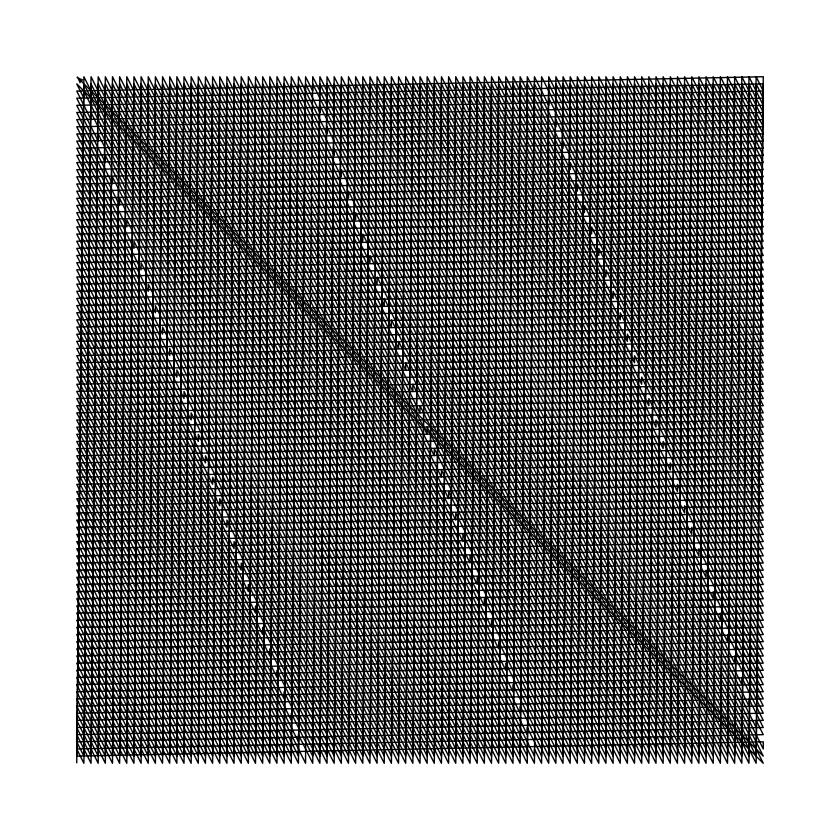

{{1,95},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,95},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},«9294»,{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,95},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{1,-2},{-96,95}}

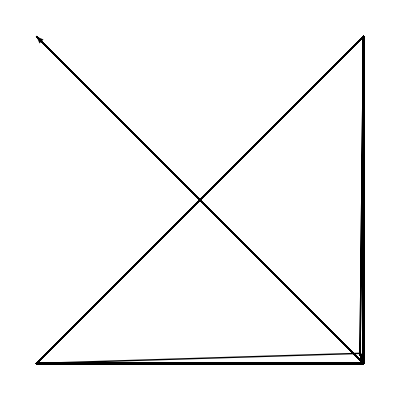

```mathematica
sq=vybu
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
sq=Transpose[Reverse[({{1, □, 10, □, □, 7, □, 16}, {□, □, □, □, □, □, □, □}, {6, □, 11, □, □, 15, □, 4}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {5, □, 14, □, □, 12, □, 9}, {□, □, □, □, □, □, □, □}, {2, □, 8, □, □, 13, □, 3}})]]
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

{{2,5,6,1},{8,14,11,10},{13,12,15,7},{3,9,4,16}}

{{2,1,1},{5,1,2},{6,1,3},{1,1,4},{8,2,1},{14,2,2},{11,2,3},{10,2,4},{13,3,1},{12,3,2},{15,3,3},{7,3,4},{3,4,1},{9,4,2},{4,4,3},{16,4,4}}

{{1,1,4},{2,1,1},{3,4,1},{4,4,3},{5,1,2},{6,1,3},{7,3,4},{8,2,1},{9,4,2},{10,2,4},{11,2,3},{12,3,2},{13,3,1},{14,2,2},{15,3,3},{16,4,4}}

{{1,4},{1,1},{4,1},{4,3},{1,2},{1,3},{3,4},{2,1},{4,2},{2,4},{2,3},{3,2},{3,1},{2,2},{3,3},{4,4}}

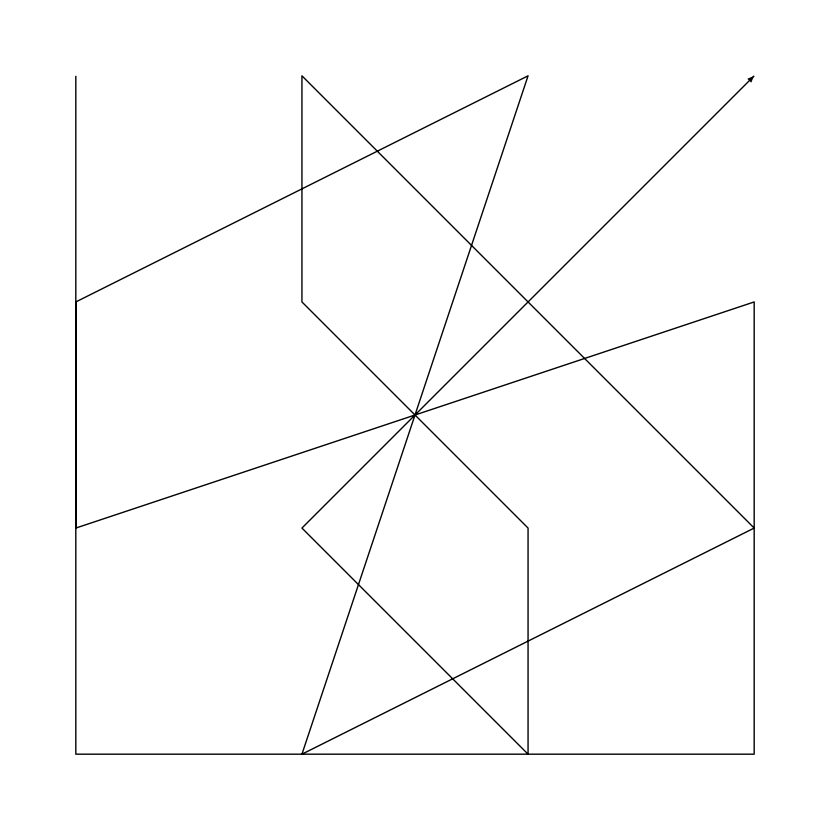

{{0,-3},{3,0},{0,2},{-3,-1},{0,1},{2,1},{-1,-3},{2,1},{-2,2},{0,-1},{1,-1},{0,-1},{-1,1},{1,1},{1,1}}

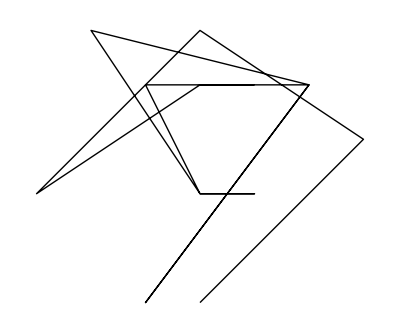

```mathematica
sq=Transpose[Reverse[({{1, □, 10, □, □, 7, □, 16}, {□, □, □, □, □, □, □, □}, {6, □, 11, □, □, 15, □, 4}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {5, □, 14, □, □, 12, □, 9}, {□, □, □, □, □, □, □, □}, {2, □, 8, □, □, 13, □, 3}})]]
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```